```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[{1,0.960006,0.900008}]]
```

```mathematica
(*Each lettered subfolder (a,b,c,and d) is designed to be run independently to generate the corresponding panel of its figure. For this reason, the required functions are defined separately within each lettered subfolder rather than being shared across the complete figure directory. This organization ensures that every panel is self-contained and can be reproduced without first running code from the other subfolders. The brief descriptions below summarize the output produced by each subfolder*)
```

## Figure 2

```mathematica
(*a:This subfolder calculates and plots the final state-transfer error for both initial instantaneous eigenstates as a function of the dimensionless loop duration.It compares the uncontrolled evolution with the constrained-control protocol,showing the suppression of the final transfer error by the real-control construction.*)

(*b:This subfolder calculates and plots the final state-transfer error as the loop base point is varied at a fixed loop duration of Γ₀t₀=5. It demonstrates that the constrained-control protocol maintains low final error without requiring a specially selected starting point on the exceptional-point loop.*)
```

### a

#### functions

```mathematica
σx=({{0, 1}, {1, 0}});
σy=({{0, -ⅈ}, {ⅈ, 0}});
σz=({{1, 0}, {0, -1}});
```

```mathematica
ΔCircPath[Δ0_?NumericQ,φ_?NumericQ,x_?NumericQ]:=
Δ0 Sin[2 π x+φ];

ΩCircPath[Δ0_?NumericQ,Ω0_?NumericQ,φ_?NumericQ,x_?NumericQ]:=
Ω0 + Δ0 Cos[2π x+φ];
(*time dependant parametrization of contour for single (ωCirc1) and double loop (ωCirc1DL)*)
ωCirc1:=#1(6(#3/#2)^5-15(#3/#2)^4+10(#3/#2)^3)&;
ωCirc1DL:=(ωCirc1[#1,#2,#3]UnitStep[#2-#3]+((#1)+ωCirc1[#1,#2,#3-#2])UnitStep[#3-#2])&;
```

```mathematica
(*constucting the holomorphic eigenvalue, works for a double loop*)
EigCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]])^2);
```

```mathematica
(*constucting thederivative of the holomorphic eigenvalue, works for a double loop*)
EigDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])((2 ⅈ π Δ0 (Γ Cos[φ+2 π ω[dir,t0,t]]+2 ⅈ Ω0 Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,1][ω][dir,t0,t])/(√(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])));
```

```mathematica
(*constucting the holomorphic pseduo rotation angle into the adiabatic frame, works for a double loop*)
θDiagCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
-2ArcTan[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]/(√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]^2)+(ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ))]+π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))];
```

```mathematica
(*constucting the derivative of the pseduo rotation angle into the adiabatic frame*)
θDiagDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
((4 π Δ0 (2 Δ0+2 Ω0 Cos[φ+2 π ω[dir,t0,t]]+ⅈ Γ Sin[φ+2 π ω[dir,t0,t]]))/(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]]))Derivative[0,0,1][ω][dir,t0,t];
```

```mathematica
(*constucting the 2nd derivative of the pseduo rotation angle into the adiabatic frame*)
θDiagDDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(4 π Δ0 (2 π (Γ^2+4 (Δ0-Ω0) (Δ0+Ω0)) (-ⅈ Γ Cos[φ+2 π ω[dir,t0,t]]+2 Ω0 Sin[φ+2 π ω[dir,t0,t]]) (Derivative[0,0,1][ω][dir,t0,t])^2+(4 Δ0 (-Γ^2+2 Δ0^2+4 Ω0^2)-2 Ω0 (Γ^2-4 (3 Δ0^2+Ω0^2)) Cos[φ+2 π ω[dir,t0,t]]+2 Δ0 (Γ^2+4 Ω0^2) Cos[2 (φ+2 π ω[dir,t0,t])]+ⅈ Γ (-Γ^2+4 (3 Δ0^2+Ω0^2)+16 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]) Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,2][ω][dir,t0,t]))/(Γ^2-4 (Δ0^2+Ω0^2)-8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]-4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])^2;
```

```mathematica
TotalIntSolv[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ]:=
x[t]/.First[NDSolve[{x'[t]== 1/4 ⅇ^(-ⅈ(2 Φ[t]+ μz[t,t0,totalterms]))(Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Cos[μx[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Cos[μx[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-(2 ⅈ Cos[1/2 μx[t,t0,totalterms]]^2 (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-((1+Cos[μx[t,t0,totalterms]]) ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))+2 ⅇ^(2 ⅈ μz[t,t0,totalterms]) Sin[1/2 μx[t,t0,totalterms]]^2 (-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+ⅈ Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-(ⅈ (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))+2 ⅈ ⅇ^(ⅈ μz[t,t0,totalterms]) (ⅈ μxdot[t,t0,totalterms]+Sin[μx[t,t0,totalterms]] (2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-μzdot[t,t0,totalterms]+(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)+2 ⅈ (Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-(Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))))))),Φ'[t]==1/2 (Cos[μz[t,t0,totalterms]] (ⅈ Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]) Sin[μx[t,t0,totalterms]]+(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]]-ⅈ Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-(Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))+Cos[μx[t,t0,totalterms]] (2 ⅈ Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-μzdot[t,t0,totalterms]-(ⅈ Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))),x[0]==0,Φ[0]==0},{x,Φ},{t,0,t0(1-10^-16)},AccuracyGoal->8,PrecisionGoal->8,WorkingPrecision->16,MaxSteps->10^6]]/.t->t0(1-10^-16)//N
```

```mathematica
TotalIntSolvPlot[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ]:=
x[t]/.First[NDSolve[{x'[t]== 1/4 ⅇ^(-ⅈ(2 Φ[t]+ μz[t,t0,totalterms]))(Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Cos[μx[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Cos[μx[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-(2 ⅈ Cos[1/2 μx[t,t0,totalterms]]^2 (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-((1+Cos[μx[t,t0,totalterms]]) ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))+2 ⅇ^(2 ⅈ μz[t,t0,totalterms]) Sin[1/2 μx[t,t0,totalterms]]^2 (-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+ⅈ Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-(ⅈ (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))+2 ⅈ ⅇ^(ⅈ μz[t,t0,totalterms]) (ⅈ μxdot[t,t0,totalterms]+Sin[μx[t,t0,totalterms]] (2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-μzdot[t,t0,totalterms]+(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)+2 ⅈ (Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-(Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))))))),Φ'[t]==1/2 (Cos[μz[t,t0,totalterms]] (ⅈ Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]) Sin[μx[t,t0,totalterms]]+(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]]-ⅈ Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-(Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))+Cos[μx[t,t0,totalterms]] (2 ⅈ Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-μzdot[t,t0,totalterms]-(ⅈ Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))),x[0]==0,Φ[0]==0},{x,Φ},{t,0,t0(1-10^-16)},AccuracyGoal->8,PrecisionGoal->8,WorkingPrecision->16,MaxSteps->10^6]]
```

```mathematica
acoefficients[totalterms_]:=Table[Symbol["A"<>ToString[n]],{n,1,totalterms}];
bcoefficients[totalterms_]:=Table[Symbol["B"<>ToString[n]],{n,1,totalterms}];
ccoefficients[totalterms_]:=Table[Symbol["C"<>ToString[n]],{n,1,totalterms}];
dcoefficients[totalterms_]:=Table[Symbol["D"<>ToString[n]],{n,1,totalterms}];
```

```mathematica
μx[t_,t0_,totalterms_]:= (π/2/(Sum[2 Abs[acoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[bcoefficients[totalterms][[n]]],{n,totalterms}]))(Sum[acoefficients[totalterms][[n]] (1-Cos[(2n π t)/t0]),{n,totalterms}]+Sum[bcoefficients[totalterms][[m]] Sin[(2m π t)/t0],{m,totalterms}]);
μxdot[t_,t0_,totalterms_]:=(π/2/(Sum[2 Abs[acoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[bcoefficients[totalterms][[n]]],{n,totalterms}])) (Sum[(acoefficients[totalterms][[n]] 2 n π Sin[(2 n π t)/t0])/t0,{n,totalterms}]+Sum[(bcoefficients[totalterms][[m]]2 m π Cos[(2m π t)/t0])/t0,{m,totalterms}]);
```

```mathematica
μz[t_,t0_,totalterms_]:=π/2+ (π/2/(Sum[2 Abs[ccoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[dcoefficients[totalterms][[n]]],{n,totalterms}]))(Sum[ccoefficients[totalterms][[n]] (1-Cos[(2n π t)/t0]),{n,totalterms}]+Sum[dcoefficients[totalterms][[m]] Sin[(2m π t)/t0],{m,totalterms}]);
μzdot[t_,t0_,totalterms_]:= (π/2/(Sum[2 Abs[ccoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[dcoefficients[totalterms][[n]]],{n,totalterms}]))(Sum[(ccoefficients[totalterms][[n]] 2n π Sin[(2n π t)/t0])/t0,{n,totalterms}]+Sum[(dcoefficients[totalterms][[m]] 2m π Cos[(2m π t)/t0])/t0,{m,totalterms}]);
```

```mathematica
FunctionValidityCheck[φ_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=Module[{FistDenomMinVal1,FistDenomMinVal2,SecondDenomMinVal1,SecondDenomMinVal2},
FistDenomMinVal1=NMinimize[{2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])),0<=t<=t0/2},t][[1]];
FistDenomMinVal2=NMinimize[{2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])),t0/2<=t<=t0},t][[1]];
SecondDenomMinVal1=NMinimize[{Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2,0<=t<=t0/2},t][[1]];
SecondDenomMinVal2=NMinimize[{Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2,t0/2<=t<=t0},t][[1]];

If[FistDenomMinVal1>1/10^6&&SecondDenomMinVal1>1/10^6&&FistDenomMinVal2>1/10^6&&SecondDenomMinVal2>1/10^6,True,False]
];
```

```mathematica
AbsIntegralFunction[φ_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=
If[FunctionValidityCheck[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]==True,
Abs[TotalIntSolv[Δ0,Ω0,Γ,Rationalize[φ,10^-16],ω,dir,t0,totalterms]],10];
```

```mathematica
WadRF[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,time_?NumericQ,totalterms_?NumericQ]:=
Module[{t},
t=SetPrecision[time,50];
(*this is the σ+ solution only, all our numerics only assume this for the optomization*)
EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σz-1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σy+(((Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(2 (Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)))+ⅈ (-(((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))))) Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])PauliMatrix[3]+((-(((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))))-ⅈ ((Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(2 (Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2))) Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])PauliMatrix[1]];
```

```mathematica
μxδΔ0[t_,t0_,totalterms_,A1_,A2_,A3_,B1_,B2_,B3_,C1_,C2_,C3_,D1_,D2_,D3_]:= (π (A1 (1-Cos[(2 π t)/t0])+A2 (1-Cos[(4 π t)/t0])+A3 (1-Cos[(6 π t)/t0])+B1 Sin[(2 π t)/t0]+B2 Sin[(4 π t)/t0]+B3 Sin[(6 π t)/t0]))/(2 (2 Abs[A1]+2 Abs[A2]+2 Abs[A3]+Abs[B1]+Abs[B2]+Abs[B3]));
μxdotδΔ0[t_,t0_,totalterms_,A1_,A2_,A3_,B1_,B2_,B3_,C1_,C2_,C3_,D1_,D2_,D3_]:=(π ((2 B1 π Cos[(2 π t)/t0])/t0+(4 B2 π Cos[(4 π t)/t0])/t0+(6 B3 π Cos[(6 π t)/t0])/t0+(2 A1 π Sin[(2 π t)/t0])/t0+(4 A2 π Sin[(4 π t)/t0])/t0+(6 A3 π Sin[(6 π t)/t0])/t0))/(2 (2 Abs[A1]+2 Abs[A2]+2 Abs[A3]+Abs[B1]+Abs[B2]+Abs[B3]));
```

```mathematica
DynMatAdOpto:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σz-1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σy
];
```

```mathematica
SolCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0},
Module[{U},
First[U[t]/.NDSolve[{U'[t]==-ⅈ DynMatAdOpto[Δ0,Ω0,Γ,φ,ω,dir,t0,t].U[t],U[0]==IdentityMatrix[2]},U,{t,0,t0},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->30,MaxSteps->10^6]]
]
];
```

```mathematica
SolCircPathRF:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms},
Module[{U},
First[U[t]/.NDSolve[{U'[t]==-ⅈ WadRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms].U[t],U[0]==IdentityMatrix[2]},U,{t,0,t0},PrecisionGoal->12,AccuracyGoal->12,WorkingPrecision->24,MaxSteps->10^6]]
]
];
```

```mathematica
(*in adiabatic frame*)
```

```mathematica
gzReRFSolCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ]:=((Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(2 (Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)))
gxReRFSolCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ]:=(-(((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))))
```

```mathematica
(*in lab frame*)
```

```mathematica
GxReLabRF[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ]:=Sech[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]+gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms] Sin[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])

GzReLabRF[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ]:=Sech[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]-gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms] Sin[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])
```

#### data for ϕ=0 results

##### t0=1

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=1/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=0;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation ({«1»}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {1.,-0.3661967774580942-0.5321967914968391 ⅈ,3.179381808504065+0.1747123745842339 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/10000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({«1»}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {1.,0.7690624050312784+0.3442910080943822 ⅈ,1.888171477738555+0.06584510959814177 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/10000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({«1»}) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {1.,-0.8171061234958852-0.05437925961393083 ⅈ,3.598804621805229+0.1778133550714921 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/10000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{36464.8,{5.80946×10^-10,{A1→0.0933825,C1→3.5789,D1→-4.84242,A2→4.99989,C2→-4.99258,D2→-2.55371}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

0.0933825

3.5789

-4.84242

4.99989

-4.99258

-2.55371

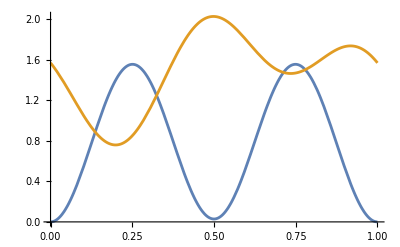

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

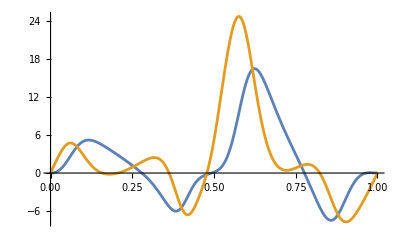

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

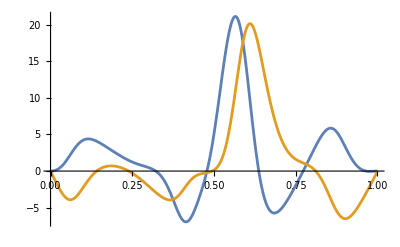

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-9.15356×10^-15

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-3.41895×10^-30

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,1,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {1.,6.203193328776249×10^-6+9.598125365875802×10^-6 ⅈ,3.272032840101425+0.1030648264180386 ⅈ}.

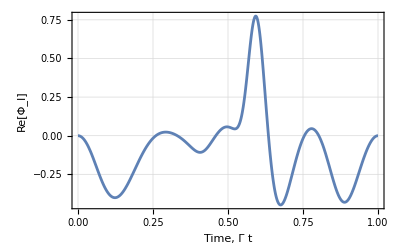

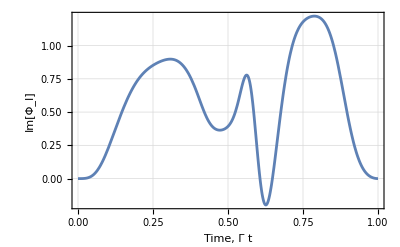

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$117995224[t]} = {1.,{{0.182754846963741085396849879039-1.74605846027123568816206613287×10^-14 ⅈ,0.906126790399979621656018457214+0.451472646800101841957679503631 ⅈ},{-0.906126790399975067499632021072+0.451472646800098464112250830922 ⅈ,-0.136211495907336251596244896425+5.05698393920607636084896271106×10^-15 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$117995248[t]} = {1.,{{-1.09914575104632916184369+0.144191461279442657543074 ⅈ,1.17782669549906970951137×10^-11-3.85824269084983438314272×10^-12 ⅈ},{-4.39079571900903416971668×10^-6-9.39551563369430136139578×10^-6 ⅈ,-0.894405173489241144925147-0.117332563782635232182092 ⅈ}}}.

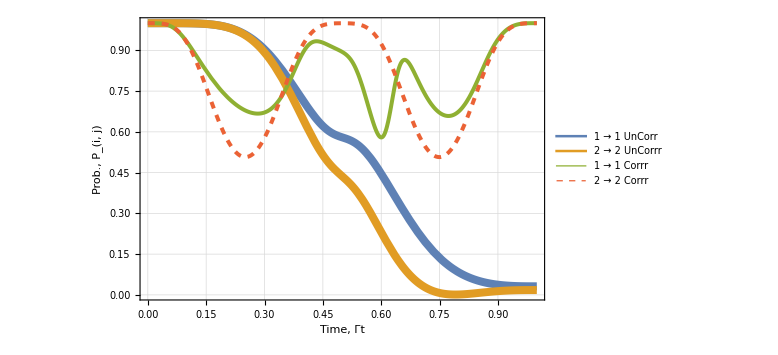

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

##### t0=1.5

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=15/(10Γ);
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=0;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,3/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 («1»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {1.5,-0.6708776210224645-0.7595855139876921 ⅈ,3.151557130448493+0.2620685382203705 ⅈ}.

InterpolatingFunction::dmval: Input value {29999999999999997/20000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,3/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 («1»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {1.5,0.8670985109491635-0.02781682244389097 ⅈ,1.813510111816041+0.09876767237589405 ⅈ}.

InterpolatingFunction::dmval: Input value {29999999999999997/20000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,3/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 («1»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {1.5,-1.081905084598914-0.3382663734442108 ⅈ,3.486733202637339+0.2667199987874474 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {29999999999999997/20000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{30035.6,{7.66473×10^-9,{A1→5.,C1→-4.77977,D1→-1.51091,A2→-0.00863253,C2→4.6429,D2→2.46658}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

5.

-4.77977

-1.51091

-0.00863253

4.6429

2.46658

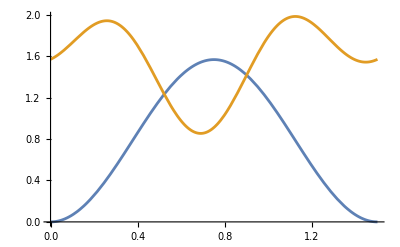

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

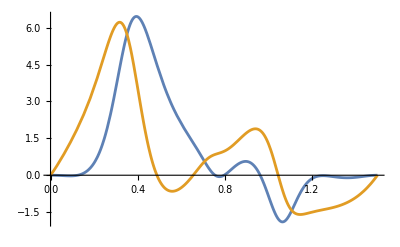

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

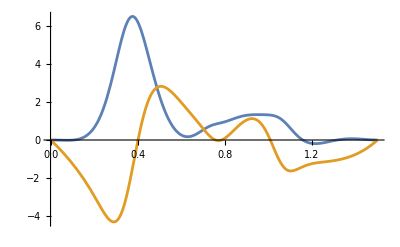

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-1.53353×10^-15

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-5.26951×10^-33

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,3/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 («1»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {1.5,-3.580081751942715×10^-6+7.93029752020809×10^-7 ⅈ,2.282459269333205+0.08101321117710545 ⅈ}.

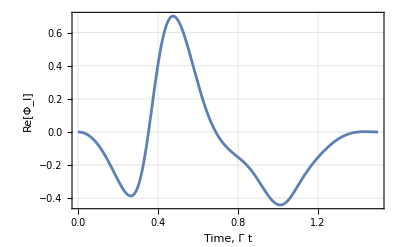

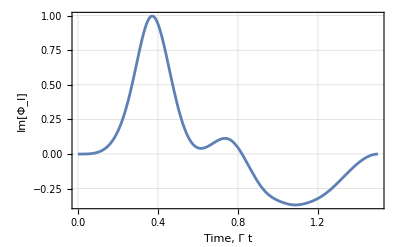

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$68485762[t]} = {1.5,{{0.294296830218334124256653859068-8.96395304472665495321563771474×10^-15 ⅈ,0.791894447221567880080348313064+0.65465848593453784533878274542 ⅈ},{-0.791894447221571304264722112153+0.654658485934517519491775588869 ⅈ,-0.189178214067572814747777345892+1.46012377588515399235279256693×10^-14 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$68485787[t]} = {1.5,{{-0.708205423705758215300686-0.82117986969168888330127 ⅈ,1.56063803581851273585137×10^-11+6.09836093471170976645349×10^-12 ⅈ},{1.51386394295909856292062×10^-6-3.00133395291816868909844×10^-6 ⅈ,-0.602271165185997204776006+0.69834675136902202864334 ⅈ}}}.

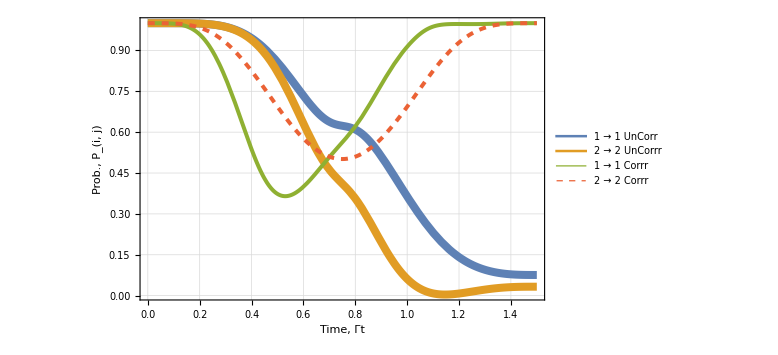

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

##### t0=2

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=2/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=0;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {2.,-1.072754988422952-0.9145196053884682 ⅈ,3.123732435369777+0.3494247054649814 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/5000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {2.,0.9056536431243282-0.4672987464180475 ⅈ,1.738848731509964+0.1316902165761419 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/5000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {2.,-1.417472402754238-0.625777992991786 ⅈ,3.374661449626032+0.3556267023769636 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/5000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{27721.,{6.95821×10^-9,{A1→4.99996,C1→-3.19155,D1→-3.31042,A2→-0.00751441,C2→2.53259,D2→-4.99319}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

4.99996

-3.19155

-3.31042

-0.00751441

2.53259

-4.99319

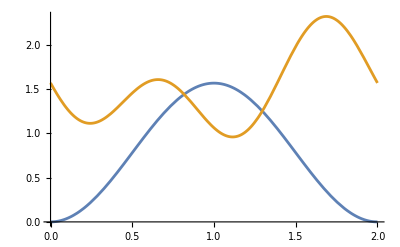

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

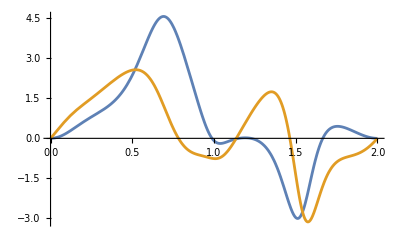

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

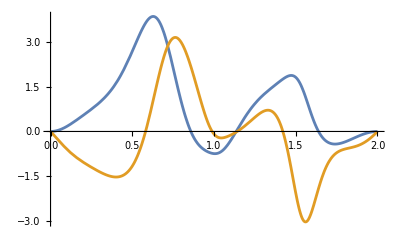

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-1.15144×10^-15

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-5.72116×10^-31

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {2.,-5.638357093018889×10^-6+2.030309920409442×10^-6 ⅈ,1.803101280697151+0.1240268346044231 ⅈ}.

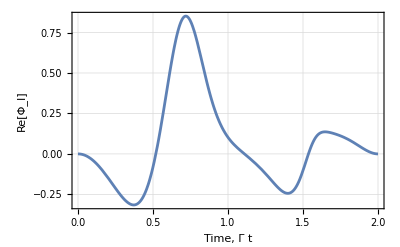

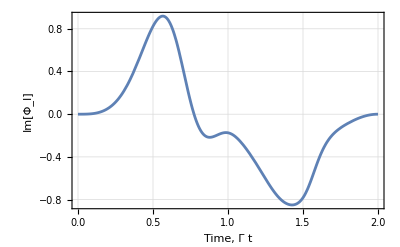

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$134660146[t]} = {2.,{{0.420973746846505302688369633771-5.88255296855149524326874363948×10^-15 ⅈ,0.637713960939871285532734876819+0.831537136162912405926007040097 ⅈ},{-0.637713960939870307616530398644+0.831537136162898970086548490005 ⅈ,-0.23310979729913204640023693871+1.7617661257734866083313689806×10^-14 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$134660170[t]} = {2.,{{-0.260621008311686300065874-1.10163757171903707781244 ⅈ,1.05759938028217673941051×10^-11+6.92279142369837109416284×10^-12 ⅈ},{-5.54737730866364436954917×10^-7-5.32244072035962345595236×10^-6 ⅈ,-0.203367289853707504105814+0.859627736155398625808606 ⅈ}}}.

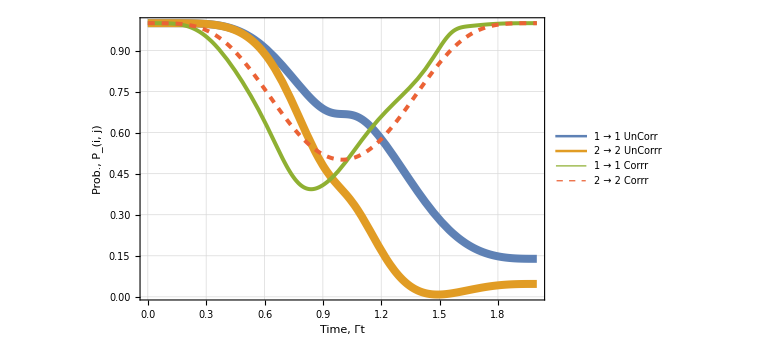

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

##### t0=2.5

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=25/(10Γ);
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=0;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,5/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 («1»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {2.5,-1.545789223799047-0.9740242328651161 ⅈ,3.095907785568698+0.4367808748285446 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/4000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,5/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 («1»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {2.5,0.8707190434342645-0.9720278743293408 ⅈ,1.664187396082873+0.1646126889289568 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/4000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,5/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 («1»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {2.5,-1.801380834148617-0.9058178242450819 ⅈ,3.262589800348187+0.4445333763043863 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/4000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{25421.9,{9.13355×10^-9,{A1→-0.253661,C1→0.624766,D1→-2.97025,A2→4.99984,C2→-2.56379,D2→0.488206}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

-0.253661

0.624766

-2.97025

4.99984

-2.56379

0.488206

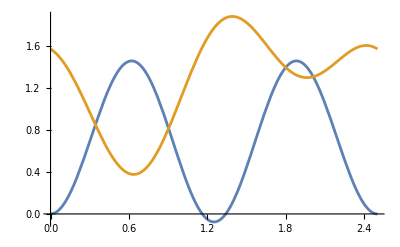

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

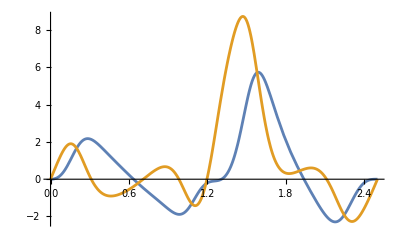

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

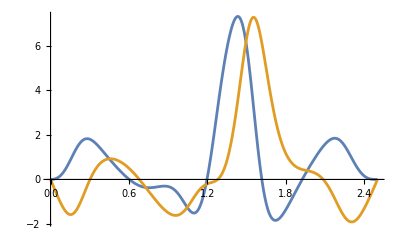

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-3.48841×10^-15

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-8.72634×10^-31

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,5/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 («1»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {2.5,4.868927851368786×10^-6+6.352402412180658×10^-6 ⅈ,3.28285679479292+0.2379850212846953 ⅈ}.

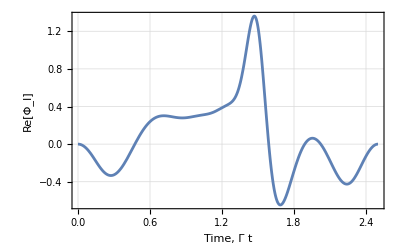

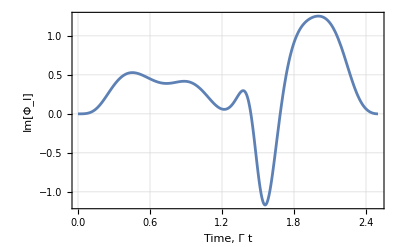

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$67180310[t]} = {2.5,{{0.564231028505506556919230927835+1.34508993174792168430374365813×10^-15 ⅈ,0.449192604128405991922040696353+0.974597616030222249459057152128 ⅈ},{-0.449192604128403790012149878887+0.974597616030208336141559041584 ⅈ,-0.268709980691861076223528599238+2.04201319878411947668477322493×10^-14 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$67180335[t]} = {2.5,{{-1.25605252215397823475245+0.178624910633185080652926 ⅈ,1.56451932995173749228292×10^-12+2.03507985793816658244589×10^-12 ⅈ},{-3.13414947910940941987382×10^-6-5.6149486227940315385372×10^-6 ⅈ,-0.780362940829978654290233-0.110976458480395497207805 ⅈ}}}.

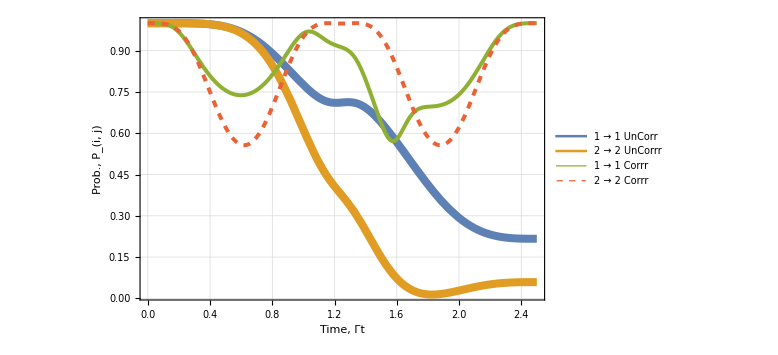

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

##### t0=3

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=3/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=0;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,3,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {3.,-2.057999737075152-0.9267221840171157 ⅈ,3.068083106507726+0.5241370529556032 ⅈ}.

InterpolatingFunction::dmval: Input value {29999999999999997/10000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,3,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {3.,0.7476397824815184-1.53798066449782 ⅈ,1.589525994333876+0.1975353233374379 ⅈ}.

InterpolatingFunction::dmval: Input value {29999999999999997/10000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,3,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {3.,-2.202718115908085-1.172756125097321 ⅈ,3.150518354406595+0.5334400334856687 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {29999999999999997/10000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{37121.3,{5.35221×10^-8,{A1→-0.491086,C1→-4.98226,D1→-3.91232,A2→4.02838,C2→-1.2588,D2→-3.51339}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

-0.491086

-4.98226

-3.91232

4.02838

-1.2588

-3.51339

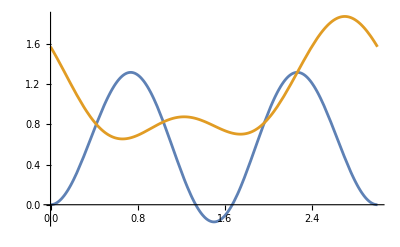

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

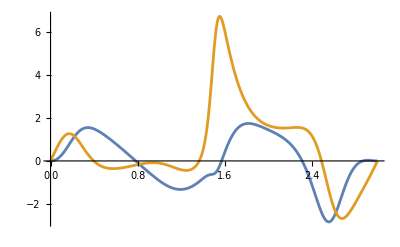

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

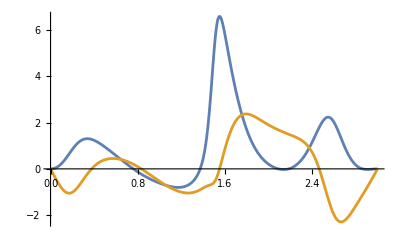

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-2.67352×10^-15

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-9.98589×10^-31

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,3,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {3.,-8.625292440660052×10^-6+7.672843826750538×10^-6 ⅈ,2.446365514294208+0.350672243674068 ⅈ}.

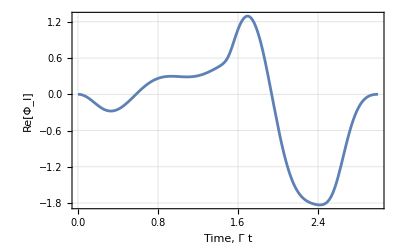

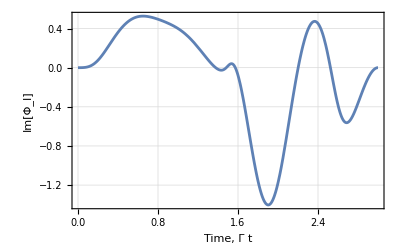

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$158063220[t]} = {3.,{{0.725672029347343559927436923862-2.67398157152138544769424429919×10^-14 ⅈ,0.233332085683459168895708704205+1.0774083461681968767302121905 ⅈ},{-0.233332085683448581632571718336+1.07740834616819509866119523237 ⅈ,-0.296625194160902813529841584297+3.17198159926229997817800193274×10^-15 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$158063244[t]} = {3.,{{-1.09044641511528232833457-0.909609059972538261124206 ⅈ,2.16771702911471824872944×10^-12+1.12824702636512356561852×10^-11 ⅈ},{1.20703107032148273281048×10^-6-8.07059573023774727307386×10^-6 ⅈ,-0.540772105277321352155111+0.451091589204047854824194 ⅈ}}}.

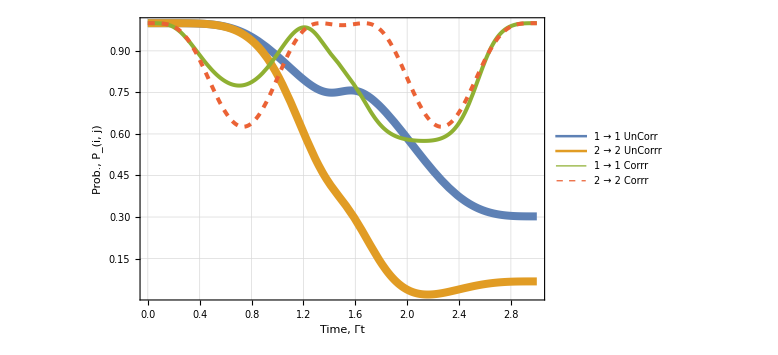

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

##### t0=3.5

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=35/(10Γ);
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=0;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,7/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 («1»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {3.5,-2.575965325893313-0.7746585535490598 ⅈ,3.040258392220863+0.6114932426019823 ⅈ}.

InterpolatingFunction::dmval: Input value {69999999999999993/20000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,7/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 («1»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {3.5,0.5212914267382408-2.159042751978671 ⅈ,1.514864614812638+0.2304578823308076 ⅈ}.

InterpolatingFunction::dmval: Input value {69999999999999993/20000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,7/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 («1»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {3.5,-2.583311417419832-1.427510959574755 ⅈ,3.038446677602686+0.6223467177649879 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {69999999999999993/20000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{51530.3,{7.55046×10^-9,{A1→-0.167917,C1→1.82937,D1→-5.,A2→1.00453,C2→-2.90725,D2→-3.93054}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

-0.167917

1.82937

-5.

1.00453

-2.90725

-3.93054

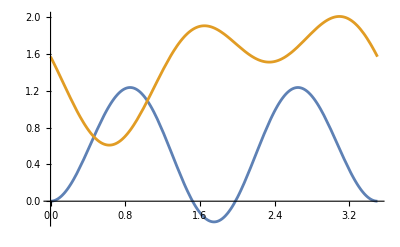

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

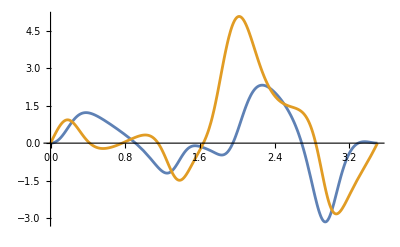

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

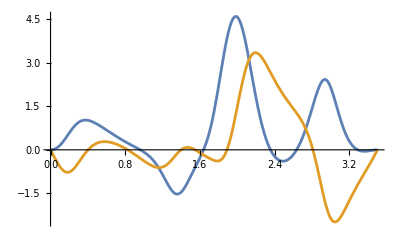

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-2.17704×10^-15

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-1.0817×10^-30

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,7/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 («1»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {3.5,-2.516163944759417×10^-6-1.828109231047355×10^-7 ⅈ,1.974803719059713+0.4358664139077679 ⅈ}.

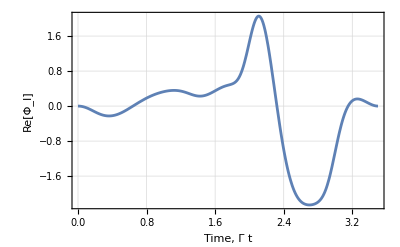

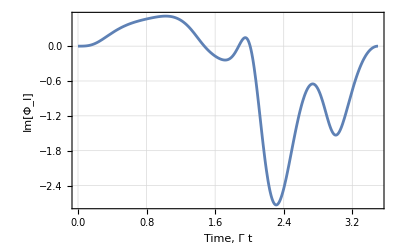

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$64330507[t]} = {3.5,{{0.907073368088446194527489009564-2.56195022531513617570027449109×10^-14 ⅈ,-0.00164444988315970240022760299447+1.1348802484174782306000641281 ⅈ},{0.00164444988316774733587208351431+1.13488024841747367187086354974 ⅈ,-0.317455999254363996030531869818+3.33884416795325127968840160527×10^-15 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$64330532[t]} = {3.5,{{-0.607861064103670980726542-1.42181416982105727093756 ⅈ,-2.90897542810145146149758×10^-13+1.12395770354641907392184×10^-11 ⅈ},{8.18227579839117101012535×10^-7-1.39256632759068412704884×10^-6 ⅈ,-0.254223420606546949825173+0.594639931831065815262297 ⅈ}}}.

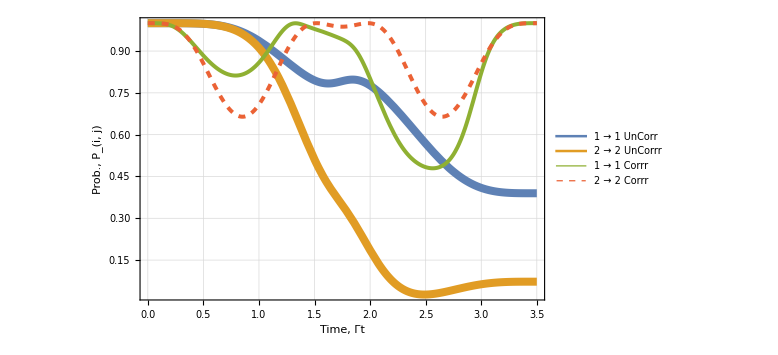

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

##### t0=4

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=4/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=0;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,4,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {4.,-3.069863989299674-0.5335228389223629 ⅈ,3.012433677259651+0.6988494152368567 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2500000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,4,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {4.,0.1762882479750201-2.826829045313433 ⅈ,1.44020327377127+0.2633804295422216 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2500000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,4,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {4.,-2.899389166968303-1.677910707290317 ⅈ,2.926375129236988+0.7112533824989039 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/2500000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{56040.3,{1.99682×10^-8,{A1→-0.656872,C1→-4.99894,D1→-4.40957,A2→4.49964,C2→3.76509,D2→4.91154}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

-0.656872

-4.99894

-4.40957

4.49964

3.76509

4.91154

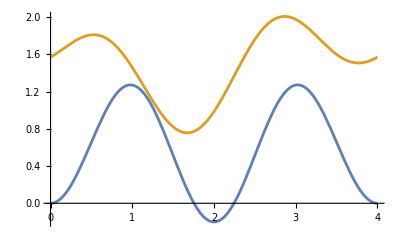

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

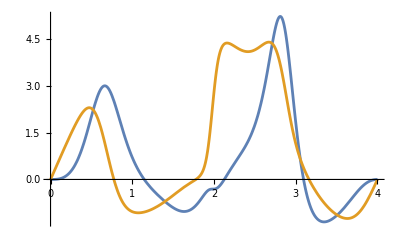

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

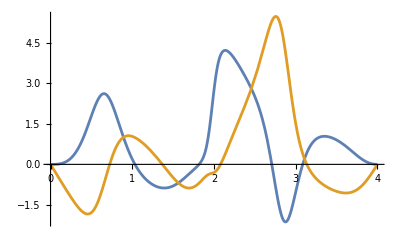

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-1.95083×10^-15

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-6.7034×10^-33

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,4,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {4.,-3.019580871194303×10^-6-1.704360267159946×10^-6 ⅈ,4.924332329447919+0.6011092981744666 ⅈ}.

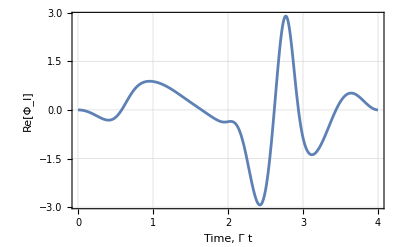

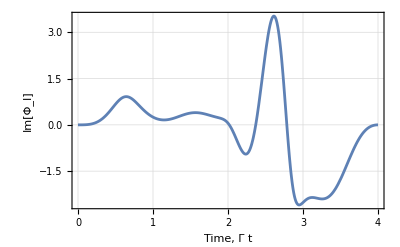

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$139506024[t]} = {4.,{{1.1104020155264277652109755365-1.98535732078606991745639160251×10^-14 ⅈ,-0.246518727452721674382537892501+1.1435140036623570158063467666 ⅈ},{0.246518727452724437248692800809+1.1435140036623366753801962683 ⅈ,-0.331767913247298122623874540111-6.46755238660258564481142535619×10^-15 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$139506048[t]} = {4.,{{0.383726649581911458993368+1.78332413207568671101406 ⅈ,9.98918088292697139482631×10^-12+1.10090979394059859716907×10^-11 ⅈ},{-1.26097695094734712438631×10^-6+1.43234177258188462647874×10^-6 ⅈ,0.115320112920159446366269-0.535936559286996654531637 ⅈ}}}.

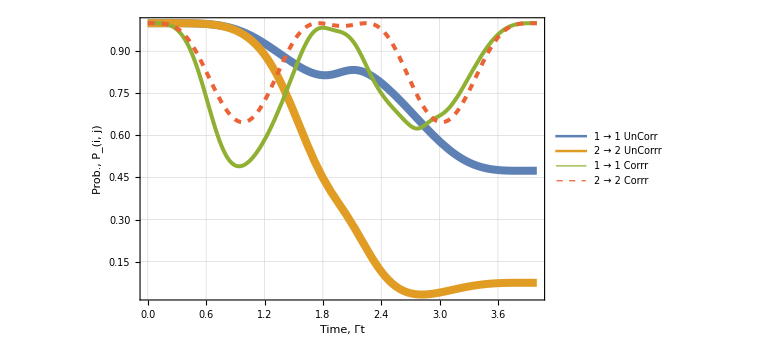

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

##### t0=4.5

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=45/(10Γ);
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=0;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,9/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 («1»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {4.5,-3.518480979413419-0.2311034041885266 ⅈ,2.984608990620237+0.7862055961061427 ⅈ}.

InterpolatingFunction::dmval: Input value {89999999999999991/20000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,9/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 («1»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {4.5,-0.3027822466834682-3.530513942073372 ⅈ,1.36554186110115+0.2963029683665247 ⅈ}.

InterpolatingFunction::dmval: Input value {89999999999999991/20000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,9/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 («1»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {4.5,-3.103556704758428-1.938223010956359 ⅈ,2.814303637042989+0.800160025136545 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {89999999999999991/20000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{17871.8,{2.36452×10^-8,{A1→4.93832,C1→-0.124538,D1→-3.95621,A2→-1.15932,C2→-4.91763,D2→3.16835}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

4.93832

-0.124538

-3.95621

-1.15932

-4.91763

3.16835

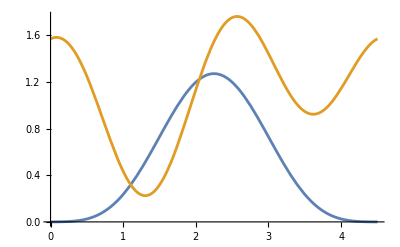

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

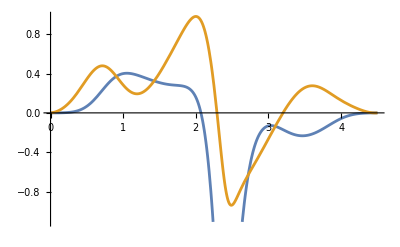

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

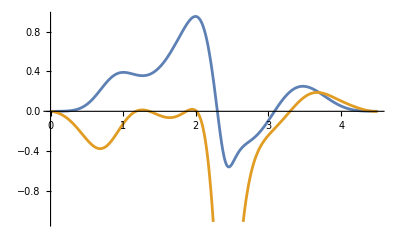

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-2.54549×10^-17

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-8.74679×10^-35

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,9/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 («1»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {4.5,-5.35951102636548×10^-6-5.553975996464144×10^-7 ⅈ,0.3239832515473796+0.4096765135417163 ⅈ}.

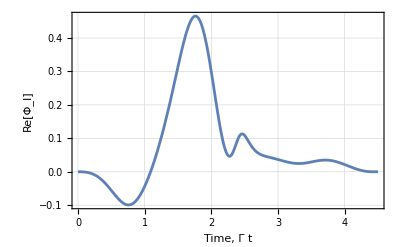

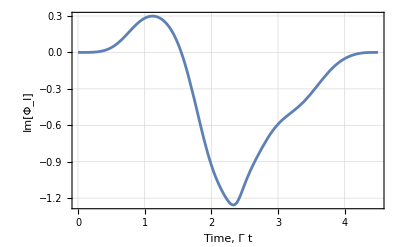

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$181012278[t]} = {4.5,{{1.33783465479621693890039917358-1.04044099097079397376732998679×10^-14 ⅈ,-0.49136037295335765387012534276+1.10161898202671086998410753429 ⅈ},{0.491360372953347107362774426656+1.10161898202670005548143534777 ⅈ,-0.340101369058733370375063111874+2.03278018365391034241471805887×10^-15 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$181012302[t]} = {4.5,{{1.4279634055544444313908-0.479532832385255868922657 ⅈ,9.90248109410053999557738×10^-12+1.07768429312238857482209×10^-11 ⅈ},{-3.32864721489528040787043×10^-6-1.56897139551224140058192×10^-6 ⅈ,0.629327348984862137194916+0.211338137224458138587133 ⅈ}}}.

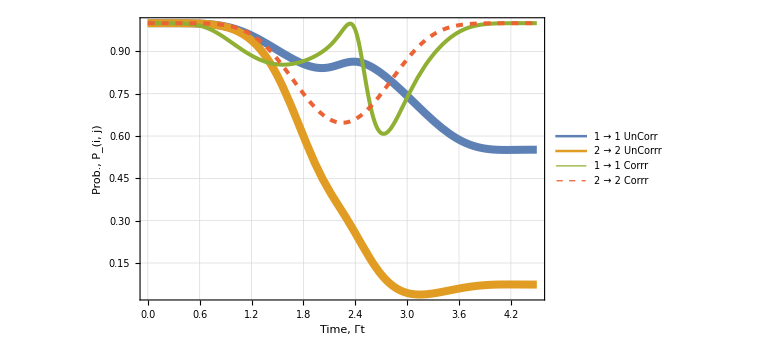

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

##### t0=5

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=5/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=0;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,5,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-3.913581981332186+0.09596330573523619 ⅈ,2.956784276650545+0.873561764525842 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,5,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-0.931098028470065-4.256679013805976 ⅈ,1.290880497817102+0.3292255522637367 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,5,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-3.146948714245765-2.22774935062114 ⅈ,2.702231986811651+0.8890666933738511 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{44021.2,{2.517×10^-8,{A1→4.99967,C1→-4.99134,D1→-3.43749,A2→-1.72756,C2→4.90727,D2→5.}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

4.99967

-4.99134

-3.43749

-1.72756

4.90727

5.

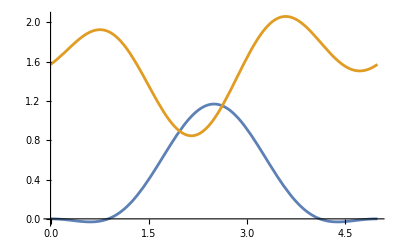

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

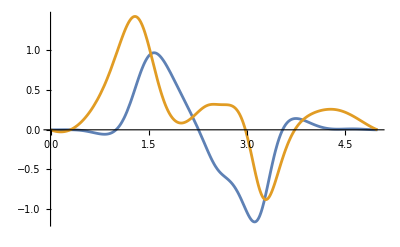

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

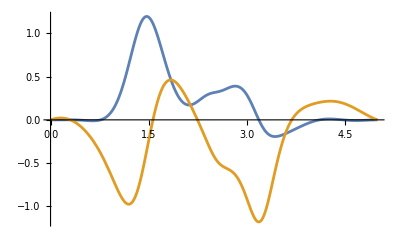

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

1.31794×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

4.5287×10^-34

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,5,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,1.767231010027047×10^-6+5.928212765233163×10^-6 ⅈ,1.127045722537359+0.6604936632424528 ⅈ}.

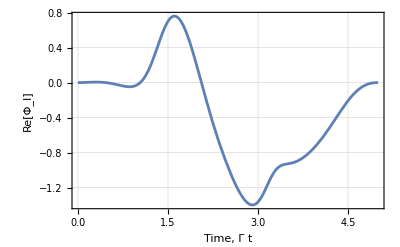

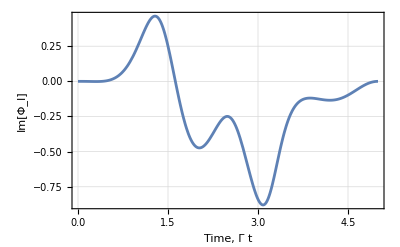

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$278356[t]} = {5.,{{1.59177987804987434479811596804+3.66359819817819976276097821648×10^-15 ⅈ,-0.725866588811615849055215594382+1.00948859951639697066684708705 ⅈ},{0.725866588811602961187332371799+1.00948859951640367063844279798 ⅈ,-0.34298054953142089783056378681+3.899234439237801971249726524×10^-20 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$278380[t]} = {5.,{{-1.86632502157818326174961-1.14398162004388320017276 ⅈ,1.59915342557241366112696-0.498784299220697870437688 ⅈ},{1.45831805078593204554269-1.90253522722662129411258 ⅈ,-0.0281847324707617078235216+2.03719858269552990273994 ⅈ}}}.

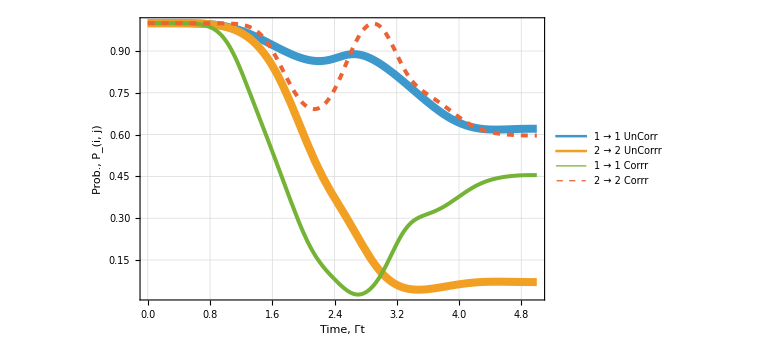

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

##### t0=5.5

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=55/(10Γ);
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=0;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ («1»)) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,11/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«1»-«1»+Cos[Times[«2»]] («1»)),«1»,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.499999999999999,-4.26307214221597+0.4069108496732103 ⅈ,2.928959584379167+0.9609179570495638 ⅈ}.

InterpolatingFunction::dmval: Input value {109999999999999989/20000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ («1»)) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,11/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«1»-«1»+Cos[Times[«2»]] («1»)),«1»,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.499999999999999,-1.723312691253664-4.989181615923392 ⅈ,1.216219202985833+0.3621481184603717 ⅈ}.

InterpolatingFunction::dmval: Input value {109999999999999989/20000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ («1»)) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,11/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«1»-«1»+Cos[Times[«2»]] («1»)),«1»,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.499999999999999,-2.981415551180426-2.568506258559009 ⅈ,2.590160391386643+0.9779733750303463 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {109999999999999989/20000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{65671.7,{3.99467×10^-8,{A1→4.99643,C1→-4.9724,D1→-5.,A2→-1.84778,C2→5.,D2→2.2014}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

4.99643

-4.9724

-5.

-1.84778

5.

2.2014

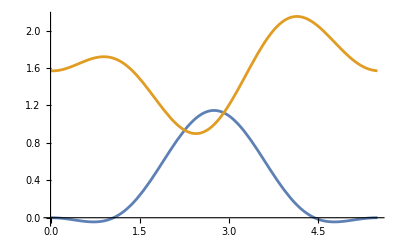

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

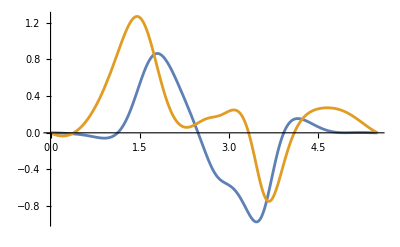

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

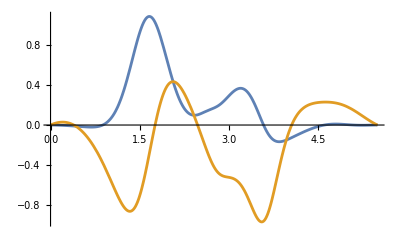

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

1.47606×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

1.87156×10^-32

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ («1»)) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,11/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«1»-«1»+Cos[Times[«2»]] («1»)),«1»,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.499999999999999,0.00001193988030702847+0.00002465099311689119 ⅈ,1.177015955935423+0.7489251377175051 ⅈ}.

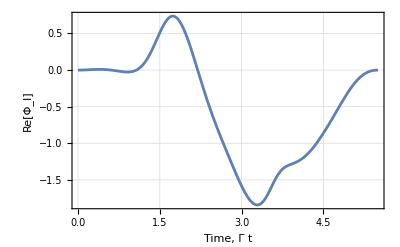

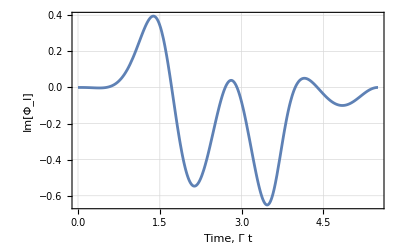

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$129716816[t]} = {5.5,{{1.87490380319009167588436555774+1.78960030714116531204509111766×10^-15 ⅈ,-0.939753727193833776141516275228+0.869515222031430755652677539686 ⅈ},{0.939753727193821695900296901974+0.869515222031445871172490929975 ⅈ,-0.340920845128976694166977776304-3.0292340177713402976187293833×10^-15 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$129716840[t]} = {5.5,{{0.811382540495115471292368-1.95287568266871921064537 ⅈ,-1.44669584127508734783971×10^-11+7.49163212958501508814056×10^-12 ⅈ},{-8.52875404875729346143716×10^-6+9.62541483081110687296776×10^-6 ⅈ,0.181433527865813696675308+0.436683200466827609015708 ⅈ}}}.

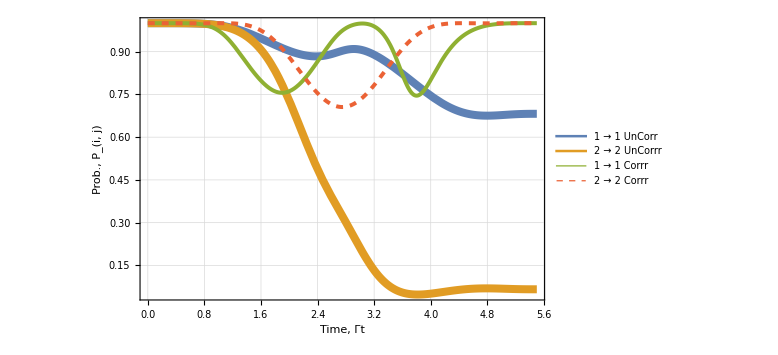

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

##### t0=6

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=6/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=0;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,6,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.999999999999999,-4.592444584731973+0.6625661299407955 ⅈ,2.90113487642071+1.048274094611339 ⅈ}.

InterpolatingFunction::dmval: Input value {29999999999999997/5000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,6,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.999999999999999,-2.693241359862305-5.709044269215389 ⅈ,1.141557787323066+0.3950706057643805 ⅈ}.

InterpolatingFunction::dmval: Input value {29999999999999997/5000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,6,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.999999999999999,-2.561609039349013-2.981976555326146 ⅈ,2.478088753492316+1.066880052792065 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {29999999999999997/5000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{56127.2,{1.05444×10^-8,{A1→3.96141,C1→-1.13635,D1→-2.8315,A2→-1.21025,C2→-4.93299,D2→4.95917}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

3.96141

-1.13635

-2.8315

-1.21025

-4.93299

4.95917

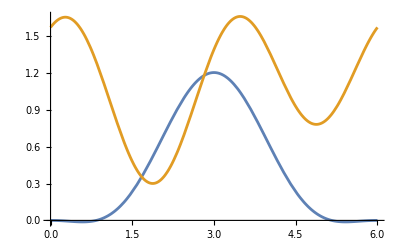

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

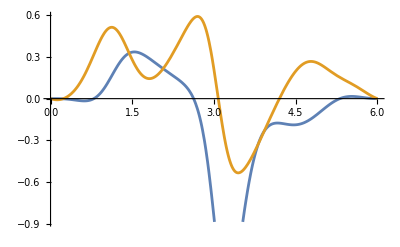

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

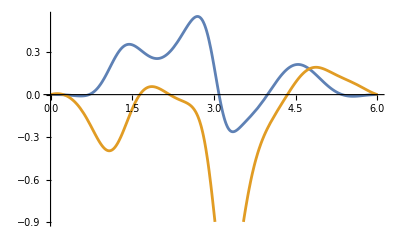

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

6.57711×10^-17

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-7.8874×10^-33

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,6,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.999999999999999,-7.693919290387235×10^-6+4.592899846944056×10^-6 ⅈ,0.5125310299892735+0.6447023962553037 ⅈ}.

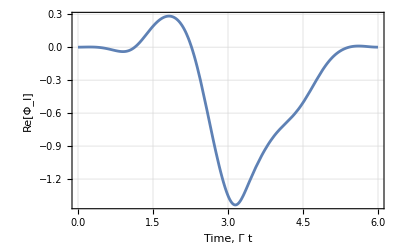

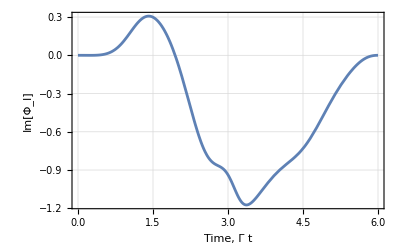

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$467126[t]} = {6.,{{2.19015969853058997862081626569+2.6410228671226448521610460104×10^-14 ⅈ,-1.1231905778468930296038537723+0.68622762907346638857257836896 ⅈ},{1.1231905778468539398730368127+0.686227629073499085426181186049 ⅈ,-0.334434714308390094084769856193-7.53727008857866933120026736132×10^-15 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$467150[t]} = {6.,{{1.66058507454095612393723-0.934388576724787379941936 ⅈ,3.54559239320849832178309×10^-12+1.18980334066362344563369×10^-11 ⅈ},{-4.73600257658793667101117×10^-6+1.09375927228238959717339×10^-7 ⅈ,0.457382727505982015663524+0.257363023620723505819852 ⅈ}}}.

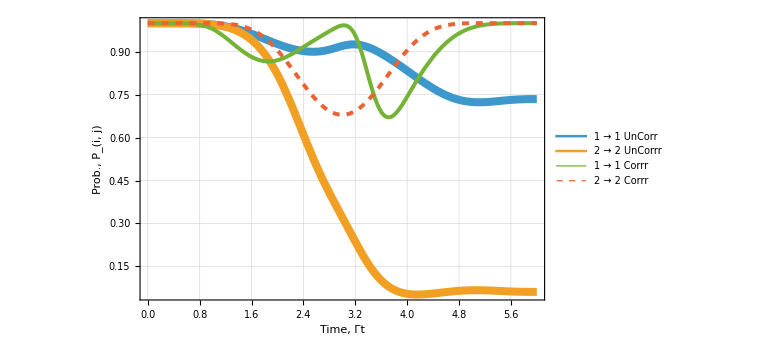

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

##### t0=6.5

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=65/(10Γ);
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=0;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ («1»)) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,13/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«1»-«1»+Cos[Times[«2»]] («1»)),«1»,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {6.499999999999999,-4.944200195799351+0.8314814214263139 ⅈ,2.873310198518348+1.13563027662902 ⅈ}.

InterpolatingFunction::dmval: Input value {129999999999999987/20000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ («1»)) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,13/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«1»-«1»+Cos[Times[«2»]] («1»)),«1»,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {6.499999999999999,-3.853524690138709-6.394376891938953 ⅈ,1.066896404503293+0.4279931880618423 ⅈ}.

InterpolatingFunction::dmval: Input value {129999999999999987/20000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ («1»)) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,13/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«1»-«1»+Cos[Times[«2»]] («1»)),«1»,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {6.499999999999999,-1.846881346801802-3.485130612154396 ⅈ,2.366017234278035+1.155786720548497 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {129999999999999987/20000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{52491.4,{9.68903×10^-9,{A1→4.98095,C1→-2.53437,D1→-3.50168,A2→-2.00706,C2→-2.52441,D2→4.95157}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

4.98095

-2.53437

-3.50168

-2.00706

-2.52441

4.95157

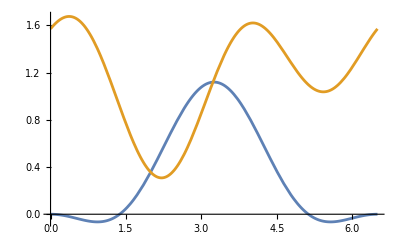

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

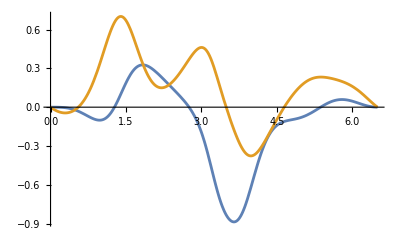

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

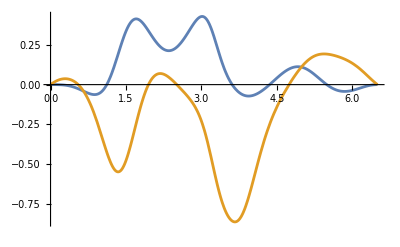

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

1.55665×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-1.86676×10^-32

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ («1»)) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,13/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«1»-«1»+Cos[Times[«2»]] («1»)),«1»,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {6.499999999999999,-1.128717500479369×10^-6+0.00001350100708021525 ⅈ,0.8543087658738778+0.798797261023766 ⅈ}.

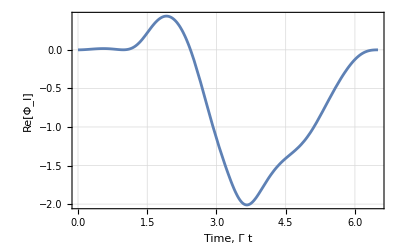

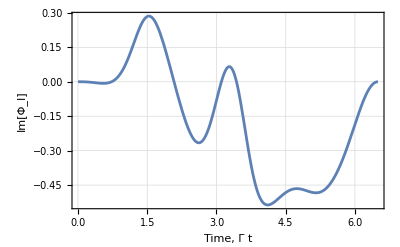

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$76709222[t]} = {6.5,{{2.54082219367058699945913866699-3.97949897004578932607288062029×10^-14 ⅈ,-1.26725748287554062634701951122+0.466235731901560233710090005063 ⅈ},{1.267257482875561395799236249+0.46623573190157354258106376129 ⅈ,-0.324035773796710802497230798595-3.96764315720354558595315892995×10^-15 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$76709247[t]} = {6.5,{{1.45984470069751107368608-1.67630118673762617697894 ⅈ,-4.42666602136257519537604×10^-13-2.74556682056430202949013×10^-11 ⅈ},{-4.89100772520100107883572×10^-6+3.67391636121733457139138×10^-6 ⅈ,0.295447406791254620406606+0.339254468915143528045473 ⅈ}}}.

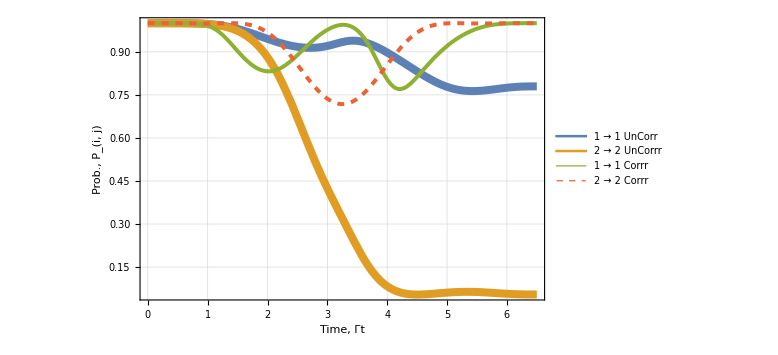

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

##### t0=7

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=7/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=0;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,7,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {6.999999999999999,-5.375106849581433+0.8957455637910962 ⅈ,2.845485541673212+1.222986416162239 ⅈ}.

InterpolatingFunction::dmval: Input value {69999999999999993/10000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,7,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {6.999999999999999,-5.215267989407912-7.02031956019946 ⅈ,0.9922350541005712+0.4609157311303474 ⅈ}.

InterpolatingFunction::dmval: Input value {69999999999999993/10000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,7,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {6.999999999999999,-0.8029292607719286-4.08586486443648 ⅈ,2.253945602676171+1.244693396247093 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {69999999999999993/10000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{72957.,{1.23267×10^-8,{A1→3.36802,C1→-1.88999,D1→4.99963,A2→-2.74693,C2→-3.47888,D2→1.42872}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

3.36802

-1.88999

4.99963

-2.74693

-3.47888

1.42872

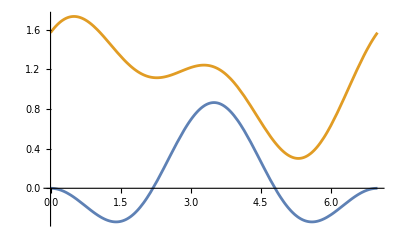

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

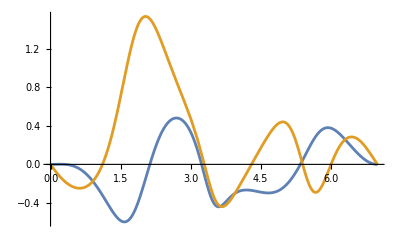

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

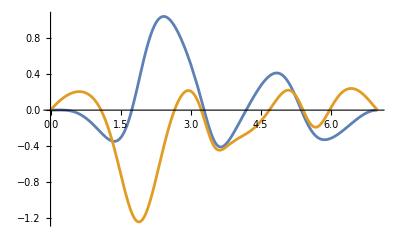

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

4.13038×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-4.95324×10^-32

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,7,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {6.999999999999999,0.0000245881381760312-0.00002331734998130499 ⅈ,1.841042919733019+1.154182735574825 ⅈ}.

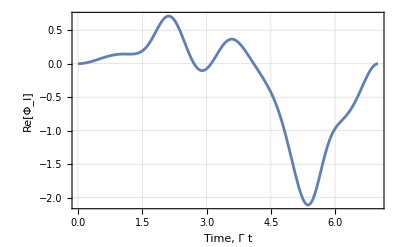

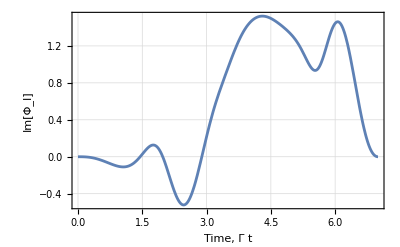

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$140258530[t]} = {7.,{{2.93052663439025272302876319995-3.24675741484362953945669819047×10^-14 ⅈ,-1.36441000416210172281814506793+0.218070814097300359982061391539 ⅈ},{1.36441000416212739672609120204+0.21807081409732362097646416335 ⅈ,-0.310241008817154984655299565858-6.27907529819005692447193181892×10^-15 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$140258554[t]} = {7.,{{-0.846673883123168450803888-3.05632368033142794552098 ⅈ,1.19659225067600790373974×10^-11-1.05928164983637508896025×10^-12 ⅈ},{5.01002923865712385603734×10^-6+9.48483221633609527104052×10^-6 ⅈ,-0.0841793910970933157762772+0.303870795505723769567934 ⅈ}}}.

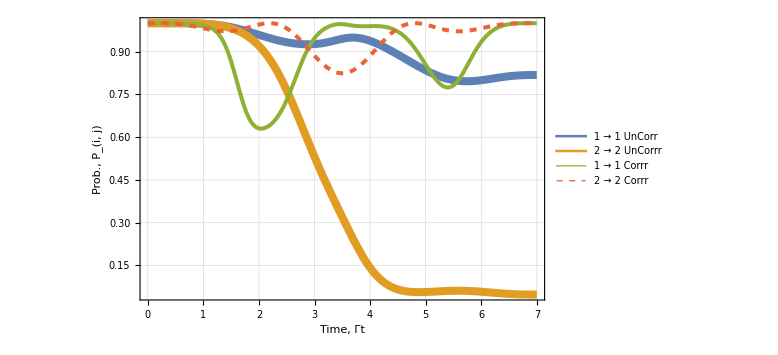

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

##### t0=7.5

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=75/(10Γ);
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=0;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ («1»)) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,15/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«1»-«1»+Cos[Times[«2»]] («1»)),«1»,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {7.499999999999999,-5.95144081647186+0.8557324306837018 ⅈ,2.817660853262899+1.310342599299531 ⅈ}.

InterpolatingFunction::dmval: Input value {29999999999999997/4000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ («1»)) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,15/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«1»-«1»+Cos[Times[«2»]] («1»)),«1»,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {7.499999999999999,-6.787662987611239-7.559028778623002 ⅈ,0.9175736739284343+0.4938383245815142 ⅈ}.

InterpolatingFunction::dmval: Input value {29999999999999997/4000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ («1»)) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,15/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«1»-«1»+Cos[Times[«2»]] («1»)),«1»,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {7.499999999999999,0.5967892614184284-4.778136967113757 ⅈ,2.141874039817019+1.333600062395705 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {29999999999999997/4000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{41052.9,{5.0644×10^-8,{A1→2.83472,C1→-1.55747,D1→4.99949,A2→-2.05502,C2→-4.99897,D2→3.32479}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

2.83472

-1.55747

4.99949

-2.05502

-4.99897

3.32479

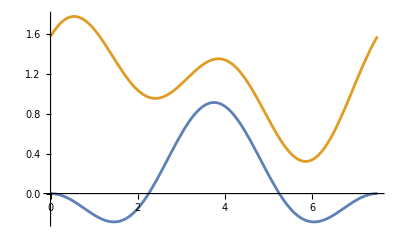

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

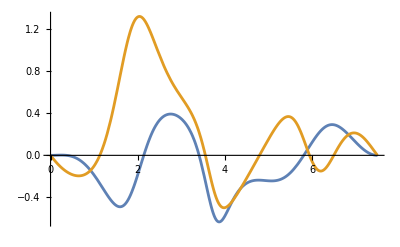

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

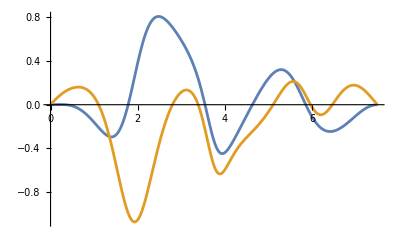

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

3.40731×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-4.08611×10^-32

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ («1»)) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,15/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«1»-«1»+Cos[Times[«2»]] («1»)),«1»,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {7.499999999999999,0.0000538059884947472-2.479262078857655×10^-6 ⅈ,1.504198285459502+1.206293256087545 ⅈ}.

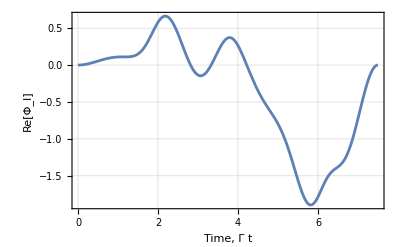

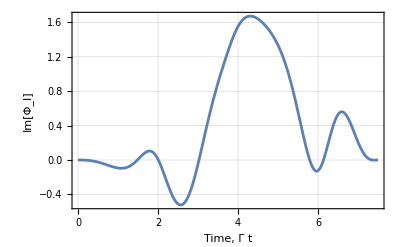

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$206706637[t]} = {7.5,{{3.36331411182868169629301194525-3.27773459098192810921989603184×10^-15 ⅈ,-1.40892141019574424310330199237-0.0480850609163565399322175153297 ⅈ},{1.40892141019576326018570246141-0.0480850609163095498102144596318 ⅈ,-0.293571067215758420507430703804-1.06349174847845829488627643098×10^-14 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$206706661[t]} = {7.5,{{0.222344690694460072598226-3.33367054623629118967809 ⅈ,1.65626611936268263825928×10^-12-7.77521233419618557919336×10^-13 ⅈ},{1.81704591622182699635238×10^-6+0.0000159841788380676071113572 ⅈ,0.0199183682399166138867894+0.29864116528063728654983 ⅈ}}}.

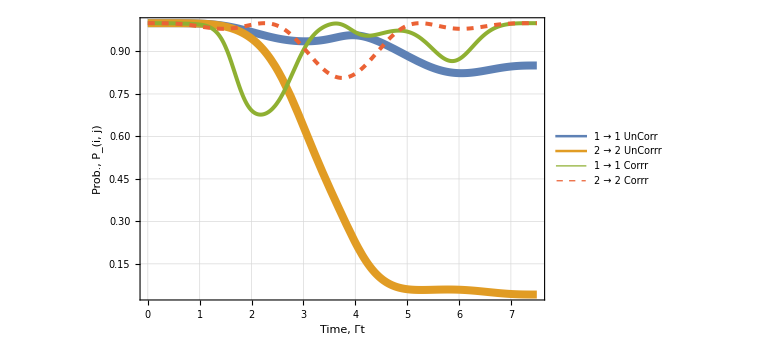

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

##### t0=8

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=8/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=0;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,8,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {7.999999999999999,-6.742568540185456+0.7330655041856485 ⅈ,2.78983616705616+1.397698773160121 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/1250000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,8,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {7.999999999999999,-8.577590761491265-7.979688704962303 ⅈ,0.8429122735080791+0.5267608144174857 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/1250000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,8,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {7.999999999999999,2.369822972984311-5.537115752720793 ⅈ,2.029802454473851+1.422506735513106 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/1250000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{46805.4,{4.28911×10^-7,{A1→4.99331,C1→-4.02703,D1→1.19361,A2→-3.31777,C2→-4.27913,D2→4.6516}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

4.99331

-4.02703

1.19361

-3.31777

-4.27913

4.6516

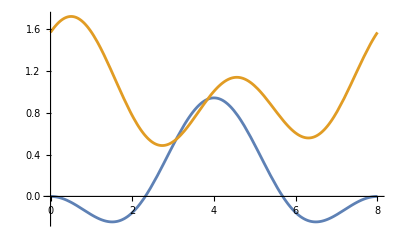

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

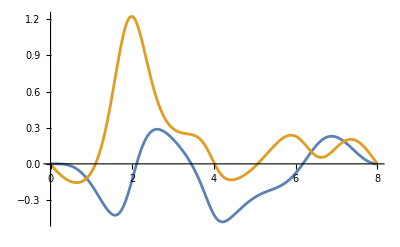

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

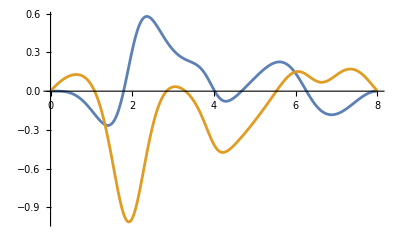

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

2.88875×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-3.46424×10^-32

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,8,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {7.999999999999999,0.00002548534031006441-6.548906335055968×10^-6 ⅈ,1.658009366263101+1.225158122593903 ⅈ}.

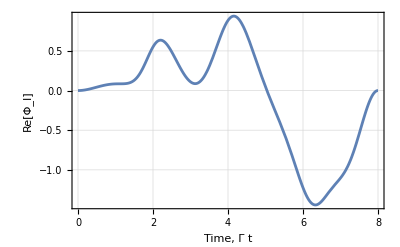

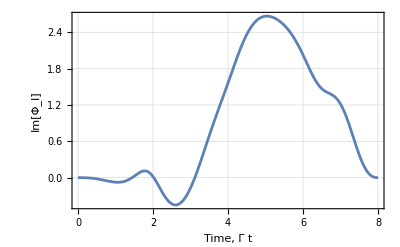

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$78339983[t]} = {8.,{{3.84368266613606487203668150098-3.58621700517675354695033271043×10^-14 ⅈ,-1.39727529404373011599079371274-0.320779929048004460945792277549 ⅈ},{1.39727529404376979303294274254-0.320779929047990503277973283117 ⅈ,-0.274548682054957959203241709532-6.67763134426799343999032108666×10^-15 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$78340008[t]} = {8.,{{-0.296558384314044030289892-3.39176430675619428632599 ⅈ,-2.84773308920090475980751×10^-12+1.61478795393093541681112×10^-11 ⅈ},{1.24309867620929117654785×10^-6+7.55040641368967251890749×10^-6 ⅈ,-0.025582994962893351865174+0.292594961977774237019112 ⅈ}}}.

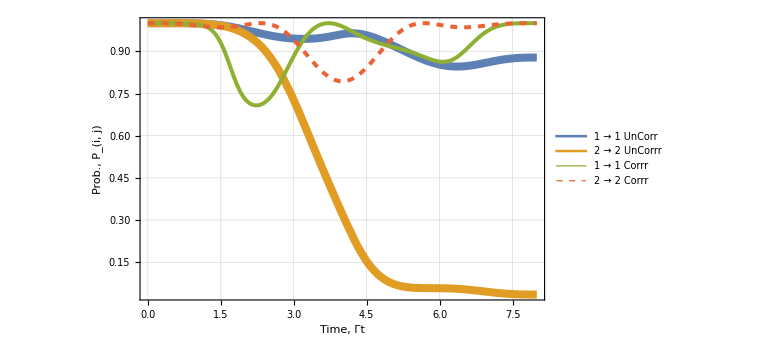

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

##### t0=8.5

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=85/(10Γ);
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=0;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ («1»)) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,17/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«1»-«1»+Cos[Times[«2»]] («1»)),«1»,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {8.499999999999999,-7.813523933971054+0.5712379372927309 ⅈ,2.762011458004921+1.485054983411384 ⅈ}.

InterpolatingFunction::dmval: Input value {169999999999999983/20000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ («1»)) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,17/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«1»-«1»+Cos[Times[«2»]] («1»)),«1»,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {8.499999999999999,-10.58921993719757-8.248573442696141 ⅈ,0.7682509331611825+0.5596834635179568 ⅈ}.

InterpolatingFunction::dmval: Input value {169999999999999983/20000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ («1»)) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,17/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«1»-«1»+Cos[Times[«2»]] («1»)),«1»,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {8.499999999999999,4.523527761474332-6.314709114781378 ⅈ,1.917730844105774+1.511413409730782 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {169999999999999983/20000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{54437.5,{1.0433×10^-7,{A1→4.8895,C1→-1.65111,D1→4.34796,A2→-2.88531,C2→-0.127168,D2→3.84264}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

4.8895

-1.65111

4.34796

-2.88531

-0.127168

3.84264

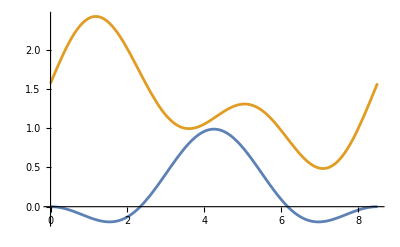

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

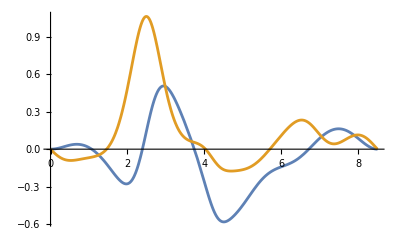

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

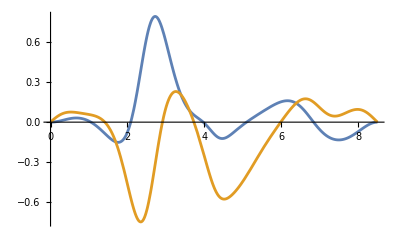

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

2.33544×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-1.14436×10^-31

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ («1»)) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,17/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«1»-«1»+Cos[Times[«2»]] («1»)),«1»,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {8.499999999999999,0.00003570440217195439+0.00005529704899071541 ⅈ,1.002255858725574+1.323603171465949 ⅈ}.

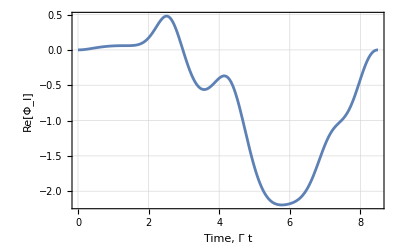

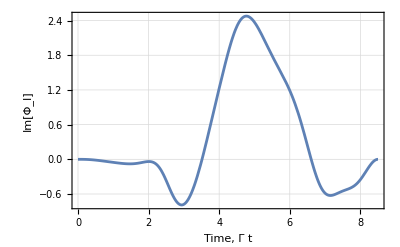

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$68194760[t]} = {8.5,{{4.37664513721765052970905364576-5.69893738404824285040266550992×10^-14 ⅈ,-1.32847866776012408948609979117-0.587774572744497119795625920021 ⅈ},{1.32847866776015624499616070735-0.587774572744514148285944292943 ⅈ,-0.253695349805002384315546945269-1.11182815137410241786860241435×10^-15 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$68194785[t]} = {8.5,{{2.02274320500617810856206-3.16592201083173718300965 ⅈ,1.81335271960363506821458×10^-11-2.91623617287379989260373×10^-11 ⅈ},{-7.34391052344494047723502×10^-6+0.0000158769531205190107072152 ⅈ,0.143309059243469956365546+0.224301979560786711777253 ⅈ}}}.

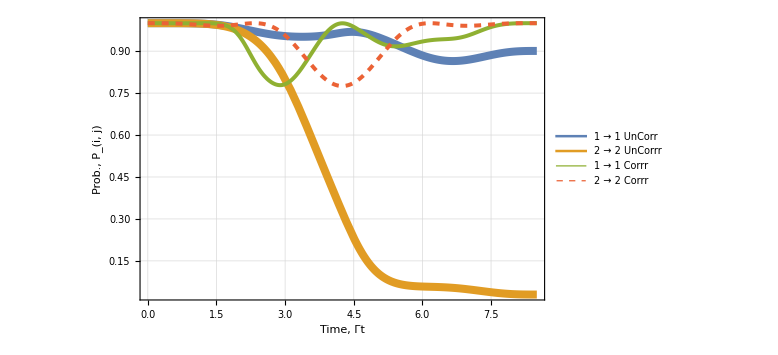

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

##### t0=9

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=9/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=0;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,9,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {8.999999999999999,-9.217348218574356+0.4335180458858895 ⅈ,2.734186764539075+1.57241116186367 ⅈ}.

InterpolatingFunction::dmval: Input value {89999999999999991/10000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,9,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {8.999999999999999,-12.82357076407818-8.329132380296421 ⅈ,0.6935895520608729+0.5926059504385994 ⅈ}.

InterpolatingFunction::dmval: Input value {89999999999999991/10000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,9,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {8.999999999999999,7.053713173375079-7.035871946097187 ⅈ,1.805659263342895+1.600320081665858 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {89999999999999991/10000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{51090.1,{2.39871×10^-8,{A1→4.54139,C1→-1.73395,D1→4.99791,A2→-2.51639,C2→-5.,D2→4.63825}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

4.54139

-1.73395

4.99791

-2.51639

-5.

4.63825

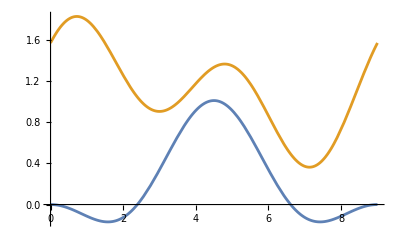

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

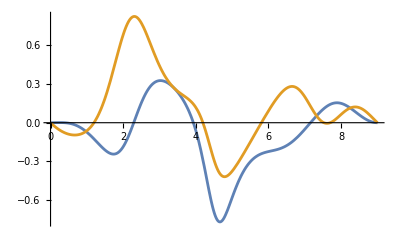

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

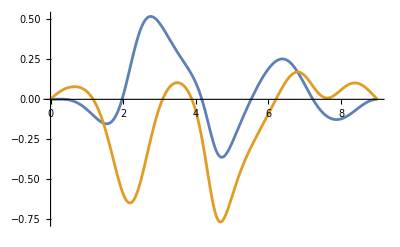

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

2.0179×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-4.90914×10^-32

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,9,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«4»),x[0]==0,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {8.999999999999999,1.062969240107947×10^-6+5.428667840565583×10^-6 ⅈ,0.9100189620143727+1.348107453099275 ⅈ}.

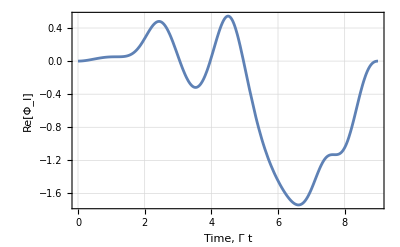

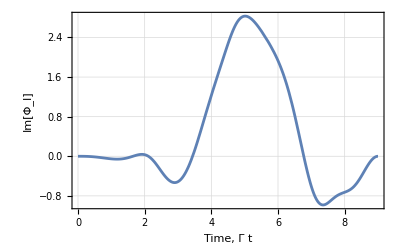

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$131435833[t]} = {9.,{{4.96779411534220889742012147101-3.3002181509670571320181231763×10^-14 ⅈ,-1.20426724177573564553835120746-0.836609974913998953335381483033 ⅈ},{1.20426724177577478393165674953-0.836609974913998644363417006136 ⅈ,-0.231526470911449566973478763842-5.20045549389244620310703166198×10^-15 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$131435857[t]} = {9.,{{2.36294461421853230785563-3.0397384481995655492276 ⅈ,-2.12247325864846835258274×10^-11+1.18574791844025834803205×10^-11 ⅈ},{-9.72866149267384386290963×10^-7+1.14765102120917043579354×10^-6 ⅈ,0.159405126389786795090677+0.20506189125568435822501 ⅈ}}}.

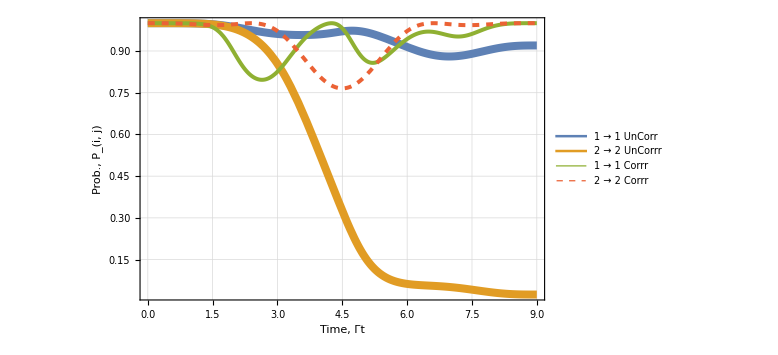

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

##### t0=9.5

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=95/(10Γ);
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=0;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ («1»)) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,19/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«1»-«1»+Cos[Times[«2»]] («1»)),«1»,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {9.499999999999999,-10.98817149715248+0.3980411326013944 ⅈ,2.706362086813156+1.659767318774846 ⅈ}.

InterpolatingFunction::dmval: Input value {189999999999999981/20000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ («1»)) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,19/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«1»-«1»+Cos[Times[«2»]] («1»)),«1»,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {9.499999999999999,-15.27810515238326-8.182138672421641 ⅈ,0.6189281689460882+0.6255284935809765 ⅈ}.

InterpolatingFunction::dmval: Input value {189999999999999981/20000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ («1»)) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,19/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«1»-«1»+Cos[Times[«2»]] («1»)),«1»,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {9.499999999999999,9.942925290789424-7.596092628457415 ⅈ,1.69358769702156+1.68922674778866 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {189999999999999981/20000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{32619.8,{2.91896×10^-8,{A1→4.9887,C1→-4.83299,D1→-4.96692,A2→-2.70626,C2→-4.97146,D2→-1.05004}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

4.9887

-4.83299

-4.96692

-2.70626

-4.97146

-1.05004

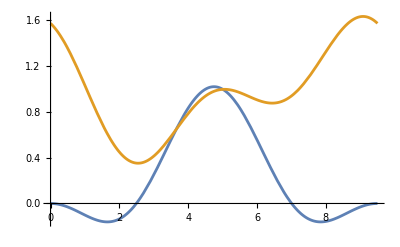

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

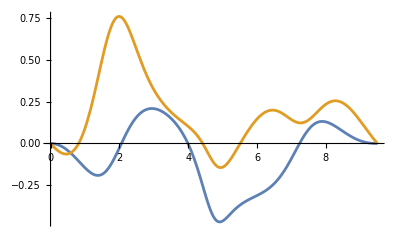

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

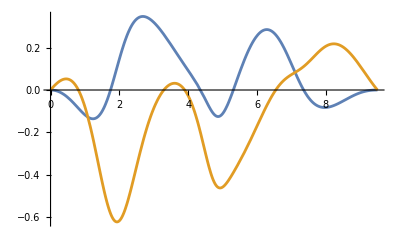

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

1.85248×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

4.63402×10^-32

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ («1»)) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,19/2,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-(«1»)+«1»-«1»+Cos[Times[«2»]] («1»)),«1»,Φ[0]==0},«3»,{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {9.499999999999999,0.00004497565467772097-4.869591476717524×10^-6 ⅈ,1.69339207294821+1.405587136258457 ⅈ}.

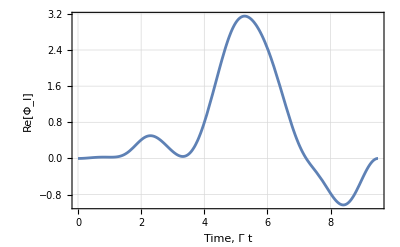

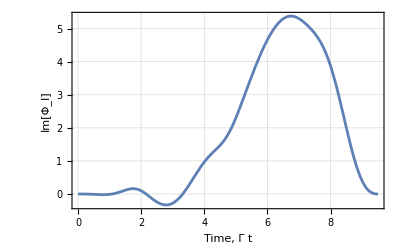

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$112209[t]} = {9.5,{{5.62337443746956926860518061519-4.98303414338236426121289741617×10^-14 ⅈ,-1.0291784467226969559725164793-1.05523440473224469684798741587 ⅈ},{1.02917844672271700237458875766-1.0552344047322847464202350765 ⅈ,-0.208545231545524669570919643658+1.1770353354926157861209494874×10^-15 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$112245[t]} = {9.5,{{-0.498684288699807326310822-4.04731368555099283176944 ⅈ,1.35744940155464183614698×10^-11-1.43765712439137695363225×10^-11 ⅈ},{-1.23643357957705376574691×10^-7+0.0000110883509912894951120201 ⅈ,-0.0299880492632006127236356+0.243382526671695100393144 ⅈ}}}.

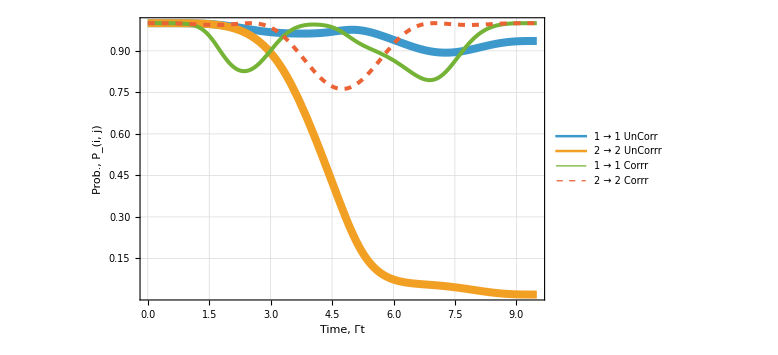

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

##### t0=10

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=10/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=0;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,10,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 («1»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {10.,-13.13596377474148+0.5503173343658178 ⅈ,2.678537402566925+1.747123493423508 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/1000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,10,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 («1»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {10.,-17.94628333318649-7.765862820324609 ⅈ,0.5442667650851396+0.6584510878938081 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/1000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,10,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 («1»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {10.,13.15806714728715-7.860511572533395 ⅈ,1.581516121026041+1.778133419519834 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/1000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{100652.,{7.43402×10^-8,{A1→4.92154,C1→-2.04601,D1→-2.88533,A2→-2.41224,C2→-3.96882,D2→-2.46103}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

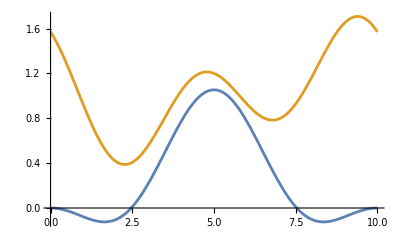

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

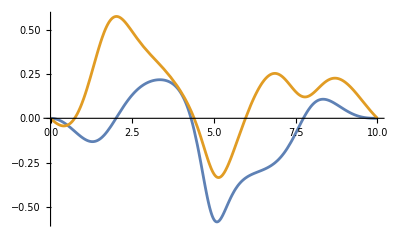

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

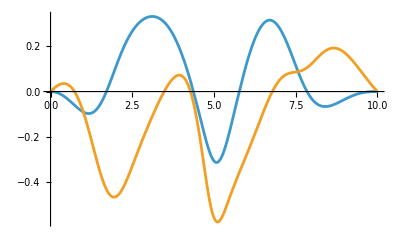

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

1.49568×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

5.58651×10^-32

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,10,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 («1»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {10.,8.685925353145513×10^-6+7.760504560761937×10^-6 ⅈ,1.346375740200326+1.47650712738853 ⅈ}.

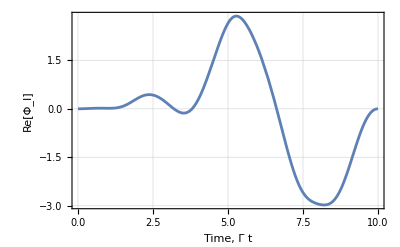

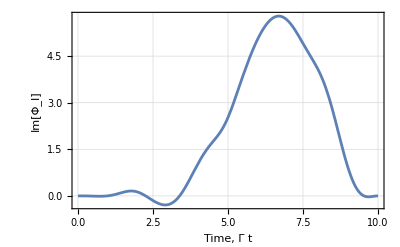

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$216593[t]} = {10.,{{6.35036368605232994306036361472-6.24872681448978110008907562837×10^-14 ⅈ,-0.810474033811414920402736838079-1.2326577176690833756746741159 ⅈ},{0.810474033811430959395193703519-1.23265771766910702388063829177 ⅈ,-0.18523556548350290272921637816-7.89889550662384801228988581037×10^-16 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$216629[t]} = {10.,{{-1.93408119127736515810962+1.06179262083675553493411 ⅈ,-3.21311785546448599131931-0.549550330476994168178495 ⅈ},{2.22556206718185459691263+4.94433445347254913711461 ⅈ,-2.3676172926492837120804+7.5466682478877929259645 ⅈ}}}.

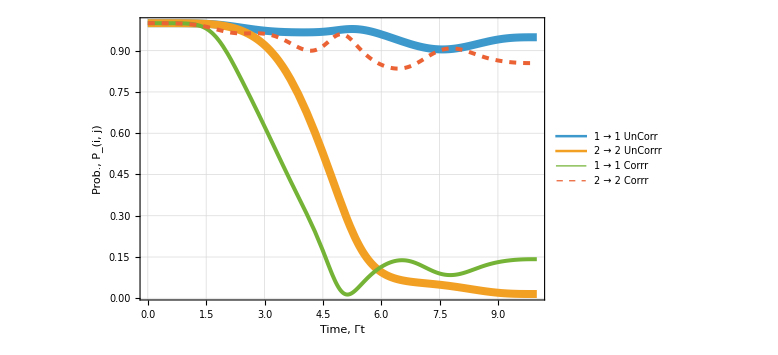

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

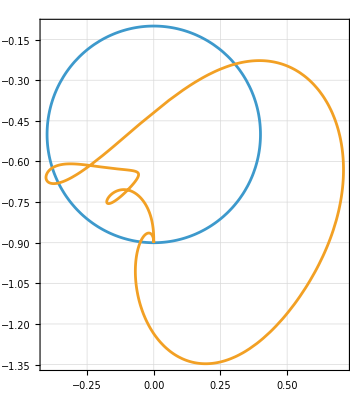

```mathematica
ParametricPlot[{{Δ0 Sin[2 π ω[dir,t0,t]+φ],-Ω0 - Δ0 Cos[2π ω[dir,t0,t]+φ]},{Δ0 Sin[2 π ω[dir,t0,t]+φ]+GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],-Ω0 - Δ0 Cos[2π ω[dir,t0,t]+φ]+GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]}},{t,0,t0},Frame->True,GridLines->Automatic,PlotRange->All]
```

#### Uncorrected & CCP Error Fidelity Plot

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=0;
totalterms=3;
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
σδΔ0=10^-16; 
NSamp=1;
cinit={1,0}; 
cfinal={1,0};
```

```mathematica
ParallelEvaluate[Off[InterpolatingFunction::dmval]];
ParallelEvaluate[Off[General::munfl]];
ParallelEvaluate[Off[NDSolve::nlnum]];
```

```mathematica
(*gain mode*)
```

```mathematica
AbsoluteTiming[GainModeOptoNoImp=Map[{#[[1]]/Γ,ErrorAnalysisFixedTimeRF[Δ0,Ω0,Γ,φ,ω,dir,(#[[1]])/Γ,totalterms,σδΔ0,NSamp,cinit,cfinal,Rationalize[#[[2]]],Rationalize[#[[5]]],A3,B1,B2,B3,Rationalize[#[[3]]],Rationalize[#[[6]]],C3,Rationalize[#[[4]]],Rationalize[#[[7]]],D3]}&,optoparamsNormTerms]]
```

{110.441,{{1,-10.02363331649},{3/2,-11.0202084621},{2,-10.6552839582},{5/2,-10.5256914041},{3,-10.4669720297},{7/2,-11.813757629},{4,-11.906329373},{9/2,-11.2296905292},{5,-11.842824777},{11/2,-10.501303189},{6,-11.216182801},{13/2,-11.299992871},{7,-11.0026235583},{15/2,-10.6498483927},{8,-11.3476635269},{17/2,-10.6732123219},{9,-12.90038374},{19/2,-11.1573002976},{10,-12.49949462}}}

```mathematica
GainModeOptoNoImp={{1,-10.02363331649042138068434520668259019131`13.568798612584779},{3/2,-11.02020846206634709881823490586745183551`12.381334820238603},{2,-10.6552839581702227604091459631569240792`12.849361760365543},{5/2,-10.52569140409269163138935101718045159668`12.988074181042872},{3,-10.46697202967628210839435963665033553942`12.718540527338025},{7/2,-11.81375762935258860919578343388131446873`11.466741609600172},{4,-11.90632937300715274760230314546359884944`11.501075658650016},{9/2,-11.2296905292467016193981462174646257176`12.051999041617108},{5,-11.84282477680830348165604994821341464082`11.279698457586246},{11/2,-10.50130318903158262554040064914297301639`12.657066382973575},{6,-11.2161828013769220870994406198830896191`11.864590123512627},{13/2,-11.29999287069399011182607028278309461498`11.713321269974243},{7,-11.00262355827038560291467416826533631495`12.18263071348959},{15/2,-10.64984839265495962856806229226189792715`12.878318152745553},{8,-11.34766352689703531807096454070294000951`12.077161495190184},{17/2,-10.67321232193003897281380523278284901428`12.249127047142775},{9,-12.9003837445254285605`10.056604129848454},{19/2,-11.15730029761530872078109003018187312863`12.131640155777884},{10,-12.4994946199072292613789740559269631694`10.703972440901147}};
```

```mathematica
(*loss mode*)
```

```mathematica
σδΔ0=10^-16;
NSamp=1;
cinit={0,1};
cfinal={0,1};
```

```mathematica
AbsoluteTiming[LossModeOptoNoImp=Map[{#[[1]]/Γ,ErrorAnalysisFixedTimeRF[Δ0,Ω0,Γ,φ,ω,dir,(#[[1]])/Γ,totalterms,σδΔ0,NSamp,cinit,cfinal,Rationalize[#[[2]]],Rationalize[#[[5]]],A3,B1,B2,B3,Rationalize[#[[3]]],Rationalize[#[[6]]],C3,Rationalize[#[[4]]],Rationalize[#[[7]]],D3]}&,optoparamsNormTerms]]
```

```mathematica
LossModeOptoNoImp={{1,-12.75615509679618341781668598364963086003`10.943355050855342},{3/2,-14.6786158815993387746`8.84736072331852},{2,-15.1508476276409236218`8.507507316632859},{5/2,-12.73037020274976942298371237225268914408`10.866112298289911},{3,-13.7538722213420548658`9.550214833566159},{7/2,-13.0840427563357862521`10.241717724533778},{4,-12.74651121631088581290007053912594765081`10.675791707692952},{9/2,-16.4434346443142460764`7.003864791173543},{5,-12.9392247327171623242`10.221645831003583},{11/2,-15.3609543251617945801`7.95692694316408},{6,-15.5437620882605202887`7.6787600115396994},{13/2,-12.42003172101135768321751351675375347308`10.634470170839359},{7,-14.7730747933372310327`8.543688826595236},{15/2,-13.4498226497219988031`10.179198320352898},{8,-13.0445558654174942162`10.442502368268995},{17/2,-13.9017869598298101423`9.135296900812817},{9,-14.1301802387005515738`8.86640139117393},{19/2,-13.916755988118333327`9.468404701799718},{10,-14.7628999717987934795`8.512869004409236}};
```

```mathematica
FinalFidelitiesGain=ParallelMap[{#[[1]],Log10[FinalAmp[Δ0,Ω0,Γ,φ,ω,dir,#[[1]]][[1]]]}&,optoparamsNormTerms]
FinalFidelitiesLoss=ParallelMap[{#[[1]],Log10[FinalAmp[Δ0,Ω0,Γ,φ,ω,dir,#[[1]]][[4]]]}&,optoparamsNormTerms]
```

```mathematica
FinalFidelitiesGain={{1,-0.013927120731959889085124060367478960538643970510177876748`28.238305747155223},{3/2,-0.0342444914967473768174588273309572944861151073916316135549`28.16039279953663},{2,-0.0649750849753265223469840589522830160248877640241080875581`28.11179185548572},{5/2,-0.1060016882159403078836282280367780669612870400462452424703`28.105361615096268},{3,-0.1563448143010857654774435419466581378787808597997554499585`28.14506749727183},{7/2,-0.2145333296480574180160795910746353943676337569682084069375`28.22319183562059},{4,-0.27899344937922777224935228065195270711`28.071795211267762},{9/2,-0.34832521735388969122277274737044513233`27.95951190483755},{5,-0.42143423196885625567491134817145337525`27.883427016046475},{11/2,-0.49755265556427653431548734024507840213`27.834838659105156},{6,-0.57619968821695334181047192419204978935`27.817886845003382},{13/2,-0.65712053096390591226648666762039263488`27.79778162029414},{7,-0.74022713383580589569275189236699993895`27.813691832073246},{15/2,-0.82554815296430391242541462721733900189`27.800139728573328},{8,-0.91319223818477686135153406019373251094`27.69864445946136},{17/2,-1.0033213883440944416804598633756796474`27.606476445164574},{9,-1.09613308663234202174435418936729638358`27.500410280594505},{19/2,-1.19184827770714826443378202717684438104`27.40742514810666},{10,-1.29070272116490148195566758564797329862`27.37645540224998}};
```

```mathematica
FinalFidelitiesLoss={{1,-0.0077916860565941985554080320202433112679282250884937415361`28.238237343699762},{3/2,-0.0144789430508359871256888196879522402788471214035031860031`28.161086089739104},{2,-0.0209758811528791117381000018576607796435813835096175864455`28.11576529761104},{5/2,-0.0264102631501532055809606646251044066661538841995772989591`28.11563046403297},{3,-0.0303575449360151828251105044539502524725358218651477595798`28.176373718303175},{7/2,-0.0327181461854150764712601826016872271511315384602406651785`28.318367456777658},{4,-0.0335995485293146583178682764838310656698848680388553038982`28.137115156989612},{9/2,-0.0332216866219382062890239492664063563787957041248834191568`27.998887022332415},{5,-0.0318497435506173949537022820841509944178867636649585818447`27.909479816345584},{11/2,-0.0297509563166186546072692228237358841548808254554045918759`27.86474493528038},{6,-0.0271698216655323452173904902805206521683364952748769629936`27.869406293092965},{13/2,-0.0243160735418037501957601494342880296237282930952733112236`27.91900878354944},{7,-0.0213606363335858134933542769257237651781599749955947976212`28.057794692685196},{15/2,-0.018436600095111676503624523703372283661435742769673818526`28.255932321294395},{8,-0.0156425558951290668801110980731560571035827503946704455582`27.984697500841335},{17/2,-0.0130472225563475434800000480842204069950607131781876463988`27.823967325566922},{9,-0.0106943253263165984866808487590948280463712012866304096107`27.724703560646905},{19/2,-0.0086073262573781551646697798688471617977195961714243418807`27.675623629827612},{10,-0.006793759419537939107007425594394495964771985270838098275`27.686149686337338}};
```

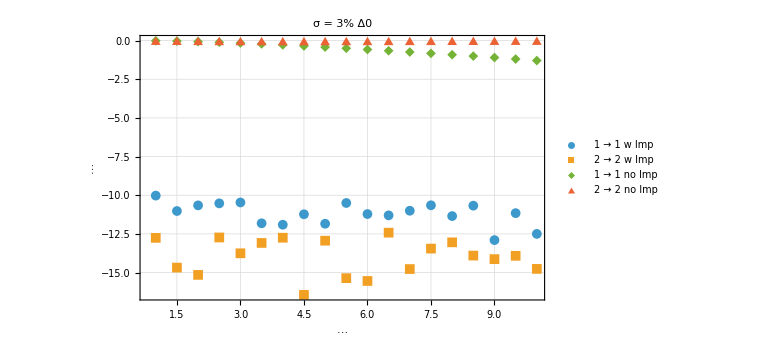

```mathematica
ListPlot[{GainModeOptoNoImp,LossModeOptoNoImp,FinalFidelitiesGain,FinalFidelitiesLoss},PlotRange-> All,Frame->True,GridLines->Automatic, PlotLegends->Placed[{"1 → 1 w Imp", "2 → 2 w Imp","1 → 1 no Imp", "2 → 2 no Imp", "1 → 1 UC", "2 → 2 UC" },After],PlotLabel->Style["σ = 3% Δ0",20], PlotMarkers->{Automatic,10},GridLinesStyle-> Thin, FrameLabel->{Style["",15],Style["(*GraphicsBox[{Thickness[0.017283097131005877`], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGI3IGYC4ur7P24Zcys68McG3DcqV3CA8ZWvPQpmmKPg
cPoMELxRcLijKbvm/2YFh7VCOnzp5xD8NVD+bSh/JgisRMiXHt7mOnOuAty8
Fd9eVpyZoOCwN7/m7cypCD5YX6eCw38QiIfKiyo4zACJW8o7uK85upzhh7RD
qwK76hkRWQg9RcwhIw0I2ETh/Aeu8Y6zCgXgfJDzz/Tww/n2JY61p2MQfNVP
Ki9nneRzCHl7+eOMhWIOMaoRMuf28Doo7FqwL3WdmEM6yPxlvA4gKu0Ygr8j
2Criv7o4nA/WVyPu8HXfx63p12DqxR1axGtZM9n4IPaZSDgwgECDqMPr4q2i
v7k1Ifa8E3UQ6fF6xfJFE+J+QTEHmXlxmqcNtBxEKieVnHWRgvPlQer7pOH8
A937mkweY/L1tVYKX1iC4EtMvcKZ8UgL4s4YBP88KHx0EHxwOFtIwfng+JCX
dPA5wW47+6qWQxUofWhLwPngcDguCOeD1d8XgPMh4cMPNw8WPjC+7xPPS6bC
CD4kvHgw+CycXfLJeQg+qn8R/ILlJRv++fPB+ZDwFMLgg935XxPOn9LeGnV5
j6bDfTQ+TB4cX92aUP8JOkiDzdN0kNkoNp/pAZvDm7bcbqPdEg5Lbi1/bMjM
5tAX0e3PKCDuEADy32VW1PTo888exn9T+zj7/JpfcH4zyH/HfmDwwfljpyic
b2IMAqIO66W36Z568xPOr3nR9Gvazr8IPii+Tss4wPiuoPi9IQvng9PXE1lI
unQQheY3OYh/pMUcum08d6V9UoCEi6KCQzinWLvxf2g+tUeUF8Igc1IQfFh5
AgCUldIw
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{14.435899999999998`, 8.57813}, {14.435899999999998`, 9.71094}, {13.696899999999998`, 10.5563}, {12.612499999999997`, 10.5563}, {11.0391, 10.5563}, {9.48906, 8.840629999999999}, {9.48906, 7.159379999999999}, {9.48906, 6.02656}, {10.2281, 5.1812499999999995`}, {11.3125, 5.1812499999999995`}, {12.898400000000002`, 5.1812499999999995`}, {14.435899999999998`, 6.8968799999999995`}, {14.435899999999998`, 8.57813}}, CompressedData["
1:eJxTTMoPSmViYGAQBmIQnZ4GBG7aDrc1Zdf8Z1ZygPHDOcXajfkVIfxjWg4i
lZNKzrLIOpw47LQ2856mQ4xqhMw5GSkHv4sTY/491nCouf/jlvFrMQfRHq9X
LFPUHc6AwBpRB5D2tGVqcH5m/ofWkyWqcL6RMRBMVnFoVWBXPTNFHM6HmCcF
50Psk3Vo4fVfP0VV1aH88DbXmX8VHKTmxWmevqDqsFZIhy9dT8nh19vXBywf
qzn4gtzFrOKw3aHp0XELDYefIPHFKg7GYKAJ54P9E6cF58P8HwHy/3plB/Tw
AQDksYAh
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}}, {{0, 2, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAQBWIQ3e31isVkoZFDyNvLH2c4Sjvoa60UvjDFyGG9kA5f
ep2UQ/FW0d+n+4wczoCAj5RDI8vRfsN0I4cv+z5uTZ8m6cDtplrK9MrQoS+i
259RQNxhJghkGjrsCLaK+K8u5jB9An+VGTeCn54GBMsM4Pzk2DtuzB4GDiKV
k0rOpojD+fK7FuxLXScF54PtM5N1WHJ/H9+cxQYOqSBz3BQh5j0zcPiwaL3C
2QglhyeJC6+Z2Bs6RHCKtRuvV3bg918/JfWEocPPt68PWC5WgfA9jOD85S88
9P4LGsP5YPdbGjusBfl/nRKcD6Y7lRwK13TfzjAwdhAGuddEyQE9/ADhe49+

"], CompressedData["
1:eJxTTMoPSmViYGAwAmIQXbxV9Pfpc0YOwW8vf5zBKOTw51vpgzmKJg4RnGLt
xuuVHVSfNM87q2Xi4LHm6HKGHwi+1Lw4zdMCKjj5aWCg4qDxlnefAaeJQ8Nv
q4JzK1Qcpk/grzK7bQznL3/hofd/IoL/eUNA9qx0Y4cniQuvmeirOJw+7LQ2
M87YwWVCs1Bal7JDOshYM2OHC1fD3uhbqzh0e71iMXlo5DClvTXqsoyqA7//
+impHgj+Rr28xYx/DOD8H29fH7Bk1nf4sGi9wtkbinC+O8h/M2Tg/BBQeCwU
h4SHo4GDiTEIiDrclK5JNGI1hPOvC31yPL8MwYe4zwjKF3ewrYxYYZpr5LAj
2Criv7qEgzooPCyNHL7s+7g1/ZsInL9WSIcv/Z6IA7ebaimTlpFDjGqEzLk7
wpBw+G8IkbcThJj31tDh7Bkg4BGAyNcbOiy5tfyx4WEeSHgyGjrMmAkENzkc
IsS3X2ToM4Dz1UHx44XgnwCF7z19OD8V5H43fYczYPM5HdaDInStnkPJ8pIN
/85zOkiA4rlA34HHkc9rxkouB1ObvUHTFupD/BPGC+fv797XZJLMB+eD1b/k
d9jq0PToeAQ0vHcIOPjfAgboJT04/z8I2CP4D0AeWKDr0CJey5rZxg/nQ8zn
gfO3eW2wmFPJ4XAelC5m60HC/zMbJH0EGsD54PR5yxDOb2Q52m+43MjBvsSx
9vQdPgf0/AAA4EBVhA==
"]}], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, {{{23.579700000000003`, 2.3203099999999997`}, {23.579700000000003`, 2.7609399999999997`}, {22.4234, 2.7609399999999997`}, {22.4234, 13.799999999999997`}, {23.579700000000003`, 13.799999999999997`}, {23.579700000000003`, 14.240599999999999`}, {21.9828, 14.240599999999999`}, {21.9828, 2.3203099999999997`}, {23.579700000000003`, 2.3203099999999997`}}}], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJZIGYC4hkzgeCkjYOJMQiIOsD4rQrsqmemiDmoPmme
dzYLwT9x2GltZpw1nH9DuibRKNTaYUewVcR/dXE4f62QDl/6PQk439xmb9C0
h5pwPgtnl3xynhacL9Lj9YqlRMuBx3/9lFQJBL9kq+jv0+esHJ4kLrxmcl7T
IT0NCMysHNaDHPZWw2GjXt5ixj8WGPzJ7a1Rl200HMSnXuHMcLKE89VB/rmF
4B9pWx5+qsnK4fzVsDf6txF8mPthfJj/wOFTaQX3v21lxArTXEs4/yQofPgw
+bDwlZ4Xp3k6wdKh6v6PW8beog71v60KznVYwfnPs7S/TX+L4IPdH2QN5zew
HO03LLeB89HjDwAjMb9b
"]], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, {{{40.773399999999995`, 8.27969}, {40.773399999999995`, 8.518749999999999}, {40.546899999999994`, 8.518749999999999}, {40.37969999999999, 8.518749999999999}, {33.882799999999996`, 8.518749999999999}, {33.715599999999995`, 8.518749999999999}, {33.4891, 8.518749999999999}, {33.4891, 8.27969}, {33.4891, 8.04219}, {33.715599999999995`, 8.04219}, {33.882799999999996`, 8.04219}, {40.37969999999999, 8.04219}, {40.546899999999994`, 8.04219}, {40.773399999999995`, 8.04219}, {40.773399999999995`, 8.27969}}}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJx11X0slHEcAPDzErOE0d3ZzJy4szvvLyHT9rXG81IbmcWkedudViiLeYmk
QiN1YZxLIitaM/rDREu1ZiyUpmxpi5ktwkQlee1+z8PvtzG/7fnjs+ee575v
v99jn3AhXGkgEAj0dFeC7tLXXT/bws5rM1nQqM1zfPfLoFceUN5fzcJVw547
nn4K7LiIcKd6RgFOk9frBrUshI3a5MaX7+0TfcZH731WgGFjeYBeGbGmRrfS
iFVo1VHY8W+HnZUFxI+naLfNtN2ufejQuZZE7K54YjXkqIABtHKJ09uFq/1V
xAcXgz6o/ux27qKuECtybC7/DuIOuDbRq5FDdlTz4cFfFGyilS+HyfiGEZ95
CiqKC6OHA+Vwi/1h6GNPwWxRSqnXC2tINvlXn2RFwe2o0lA9CzGYhrZWKi0o
KJQYSwcqRcCivB6FYIdIM/S1N4njUD2ydxuVsaZTiO3jjZaQj6eY2H+kJ8VH
TfxF1yavFuIslE9/COSMLY96HxfCldWAi++niLn3tVLYwSi+IeLt+my/7xKq
t4jGrlwyitU4Ej8t/XpW4Lfbkq76bqWZCHs7X7ughcQBV+Kipsh3XqbEXFsq
SD25+NS6fqL4Zogj5oYXNA1i7BZLF7Okb2L8vAAtsMbz8rt7oT2pyprv1zIF
kSaiYu/YQyBD811CY3P5bhBzc2HMgPmZsDGvv/bYSjTnIfY77kv4/bGPgbHg
2CBtg4TvzzoNl1H8NhIY6zar9V6hgSuXgQTyUH+WaShD89Rmt6e5+Ttth+Nz
WnSc1srt+HkxYbCPo/kTEnP9FjP4eUvUX1uGz89cwvcjg4Gpc85L1fel2Nz+
bJfy85/G8PtpVAp1gS6ftCpiLr4o4s7RknVlJAO+gS/Dq95sPX9y6370lj0Z
aF6azhpQO8DsgW6PGkuGr6O5A///ZTT2SkxKz4Y+sau6ftlTReP9+cwttVEv
nebPK0sFP2+ZND4PuHq0Ezeh86WAwc5H8QOLXYzmMYaFlbmZ10eOybHXlzLG
a+86YXPnUjIx/SrP1v+7DLjzN5LlzzNKBu4o3lMs9HU9LzPykMEayiechYko
ccfHcSk29/te4gJ0XlVLYR7VJ5oFDxTfDSm/vxOJH6B+pBJz+zOdxf3c+T34
D6pZmus=
"]], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, {{{55.44839999999999, 2.3203099999999997`}, {55.44839999999999, 14.240599999999999`}, {53.849999999999994`, 14.240599999999999`}, {53.849999999999994`, 13.799999999999997`}, {55.0063, 13.799999999999997`}, {55.0063, 2.7609399999999997`}, {53.849999999999994`, 2.7609399999999997`}, {53.849999999999994`, 2.3203099999999997`}, {55.44839999999999, 2.3203099999999997`}}}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{86.78978331257782, 24.508064757160646`},PlotRange->{{0., 57.86}, {0., 16.34}}])", 15]}, LabelStyle->{Bold,24},ImageSize->Large]
```

### b

#### functions

```mathematica
σx=({{0, 1}, {1, 0}});
σy=({{0, -ⅈ}, {ⅈ, 0}});
σz=({{1, 0}, {0, -1}});
```

```mathematica
ΔCircPath[Δ0_?NumericQ,φ_?NumericQ,x_?NumericQ]:=
Δ0 Sin[2 π x+φ];

ΩCircPath[Δ0_?NumericQ,Ω0_?NumericQ,φ_?NumericQ,x_?NumericQ]:=
Ω0 + Δ0 Cos[2π x+φ];
(*time dependant parametrization of contour for single (ωCirc1) and double loop (ωCirc1DL)*)
ωCirc1:=#1(6(#3/#2)^5-15(#3/#2)^4+10(#3/#2)^3)&;
ωCirc1DL:=(ωCirc1[#1,#2,#3]UnitStep[#2-#3]+((#1)+ωCirc1[#1,#2,#3-#2])UnitStep[#3-#2])&;
```

```mathematica
(*constucting the holomorphic eigenvalue, works for a double loop*)
EigCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]])^2);
```

```mathematica
(*constucting thederivative of the holomorphic eigenvalue, works for a double loop*)
EigDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])((2 ⅈ π Δ0 (Γ Cos[φ+2 π ω[dir,t0,t]]+2 ⅈ Ω0 Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,1][ω][dir,t0,t])/(√(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])));
```

```mathematica
(*constucting the holomorphic pseduo rotation angle into the adiabatic frame, works for a double loop*)
θDiagCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
-2ArcTan[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]/(√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]^2)+(ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ))]+π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))];
```

```mathematica
(*constucting the derivative of the pseduo rotation angle into the adiabatic frame*)
θDiagDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
((4 π Δ0 (2 Δ0+2 Ω0 Cos[φ+2 π ω[dir,t0,t]]+ⅈ Γ Sin[φ+2 π ω[dir,t0,t]]))/(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]]))Derivative[0,0,1][ω][dir,t0,t];
```

```mathematica
(*constucting the 2nd derivative of the pseduo rotation angle into the adiabatic frame*)
θDiagDDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(4 π Δ0 (2 π (Γ^2+4 (Δ0-Ω0) (Δ0+Ω0)) (-ⅈ Γ Cos[φ+2 π ω[dir,t0,t]]+2 Ω0 Sin[φ+2 π ω[dir,t0,t]]) (Derivative[0,0,1][ω][dir,t0,t])^2+(4 Δ0 (-Γ^2+2 Δ0^2+4 Ω0^2)-2 Ω0 (Γ^2-4 (3 Δ0^2+Ω0^2)) Cos[φ+2 π ω[dir,t0,t]]+2 Δ0 (Γ^2+4 Ω0^2) Cos[2 (φ+2 π ω[dir,t0,t])]+ⅈ Γ (-Γ^2+4 (3 Δ0^2+Ω0^2)+16 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]) Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,2][ω][dir,t0,t]))/(Γ^2-4 (Δ0^2+Ω0^2)-8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]-4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])^2;
```

```mathematica
TotalIntSolv[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ]:=
x[t]/.First[NDSolve[{x'[t]== 1/4 ⅇ^(-ⅈ(2 Φ[t]+ μz[t,t0,totalterms]))(Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Cos[μx[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Cos[μx[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-(2 ⅈ Cos[1/2 μx[t,t0,totalterms]]^2 (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-((1+Cos[μx[t,t0,totalterms]]) ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))+2 ⅇ^(2 ⅈ μz[t,t0,totalterms]) Sin[1/2 μx[t,t0,totalterms]]^2 (-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+ⅈ Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-(ⅈ (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))+2 ⅈ ⅇ^(ⅈ μz[t,t0,totalterms]) (ⅈ μxdot[t,t0,totalterms]+Sin[μx[t,t0,totalterms]] (2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-μzdot[t,t0,totalterms]+(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)+2 ⅈ (Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-(Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))))))),Φ'[t]==1/2 (Cos[μz[t,t0,totalterms]] (ⅈ Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]) Sin[μx[t,t0,totalterms]]+(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]]-ⅈ Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-(Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))+Cos[μx[t,t0,totalterms]] (2 ⅈ Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-μzdot[t,t0,totalterms]-(ⅈ Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))),x[0]==0,Φ[0]==0},{x,Φ},{t,0,t0(1-10^-16)},AccuracyGoal->8,PrecisionGoal->8,WorkingPrecision->16,MaxSteps->10^6]]/.t->t0(1-10^-16)//N
```

```mathematica
TotalIntSolvPlot[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ]:=
x[t]/.First[NDSolve[{x'[t]== 1/4 ⅇ^(-ⅈ(2 Φ[t]+ μz[t,t0,totalterms]))(Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Cos[μx[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Cos[μx[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-(2 ⅈ Cos[1/2 μx[t,t0,totalterms]]^2 (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-((1+Cos[μx[t,t0,totalterms]]) ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))+2 ⅇ^(2 ⅈ μz[t,t0,totalterms]) Sin[1/2 μx[t,t0,totalterms]]^2 (-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+ⅈ Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-(ⅈ (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))+2 ⅈ ⅇ^(ⅈ μz[t,t0,totalterms]) (ⅈ μxdot[t,t0,totalterms]+Sin[μx[t,t0,totalterms]] (2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-μzdot[t,t0,totalterms]+(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)+2 ⅈ (Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-(Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))))))),Φ'[t]==1/2 (Cos[μz[t,t0,totalterms]] (ⅈ Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]) Sin[μx[t,t0,totalterms]]+(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]]-ⅈ Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-(Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))+Cos[μx[t,t0,totalterms]] (2 ⅈ Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-μzdot[t,t0,totalterms]-(ⅈ Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))),x[0]==0,Φ[0]==0},{x,Φ},{t,0,t0(1-10^-16)},AccuracyGoal->8,PrecisionGoal->8,WorkingPrecision->16,MaxSteps->10^6]]
```

```mathematica
acoefficients[totalterms_]:=Table[Symbol["A"<>ToString[n]],{n,1,totalterms}];
bcoefficients[totalterms_]:=Table[Symbol["B"<>ToString[n]],{n,1,totalterms}];
ccoefficients[totalterms_]:=Table[Symbol["C"<>ToString[n]],{n,1,totalterms}];
dcoefficients[totalterms_]:=Table[Symbol["D"<>ToString[n]],{n,1,totalterms}];
```

```mathematica
μx[t_,t0_,totalterms_]:= (π/2/(Sum[2 Abs[acoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[bcoefficients[totalterms][[n]]],{n,totalterms}]))(Sum[acoefficients[totalterms][[n]] (1-Cos[(2n π t)/t0]),{n,totalterms}]+Sum[bcoefficients[totalterms][[m]] Sin[(2m π t)/t0],{m,totalterms}]);
μxdot[t_,t0_,totalterms_]:=(π/2/(Sum[2 Abs[acoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[bcoefficients[totalterms][[n]]],{n,totalterms}])) (Sum[(acoefficients[totalterms][[n]] 2 n π Sin[(2 n π t)/t0])/t0,{n,totalterms}]+Sum[(bcoefficients[totalterms][[m]]2 m π Cos[(2m π t)/t0])/t0,{m,totalterms}]);
```

```mathematica
μz[t_,t0_,totalterms_]:=π/2+ (π/2/(Sum[2 Abs[ccoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[dcoefficients[totalterms][[n]]],{n,totalterms}]))(Sum[ccoefficients[totalterms][[n]] (1-Cos[(2n π t)/t0]),{n,totalterms}]+Sum[dcoefficients[totalterms][[m]] Sin[(2m π t)/t0],{m,totalterms}]);
μzdot[t_,t0_,totalterms_]:= (π/2/(Sum[2 Abs[ccoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[dcoefficients[totalterms][[n]]],{n,totalterms}]))(Sum[(ccoefficients[totalterms][[n]] 2n π Sin[(2n π t)/t0])/t0,{n,totalterms}]+Sum[(dcoefficients[totalterms][[m]] 2m π Cos[(2m π t)/t0])/t0,{m,totalterms}]);
```

```mathematica
FunctionValidityCheck[φ_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=Module[{FistDenomMinVal1,FistDenomMinVal2,SecondDenomMinVal1,SecondDenomMinVal2},
FistDenomMinVal1=NMinimize[{2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])),0<=t<=t0/2},t][[1]];
FistDenomMinVal2=NMinimize[{2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])),t0/2<=t<=t0},t][[1]];
SecondDenomMinVal1=NMinimize[{Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2,0<=t<=t0/2},t][[1]];
SecondDenomMinVal2=NMinimize[{Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2,t0/2<=t<=t0},t][[1]];

If[FistDenomMinVal1>1/10^6&&SecondDenomMinVal1>1/10^6&&FistDenomMinVal2>1/10^6&&SecondDenomMinVal2>1/10^6,True,False]
];
```

```mathematica
AbsIntegralFunction[φ_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=
If[FunctionValidityCheck[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]==True,
Abs[TotalIntSolv[Δ0,Ω0,Γ,Rationalize[φ,10^-16],ω,dir,t0,totalterms]],10];
```

```mathematica
WadRF[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,time_?NumericQ,totalterms_?NumericQ]:=
Module[{t},
t=SetPrecision[time,50];
(*this is the σ+ solution only, all our numerics only assume this for the optomization*)
EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σz-1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σy+(((Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(2 (Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)))+ⅈ (-(((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))))) Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])PauliMatrix[3]+((-(((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))))-ⅈ ((Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(2 (Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2))) Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])PauliMatrix[1]];
```

```mathematica
DynMatAdOpto:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σz-1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σy
];
```

```mathematica
SolCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0},
Module[{U},
First[U[t]/.NDSolve[{U'[t]==-ⅈ DynMatAdOpto[Δ0,Ω0,Γ,φ,ω,dir,t0,t].U[t],U[0]==IdentityMatrix[2]},U,{t,0,t0},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->30,MaxSteps->10^6]]
]
];
```

```mathematica
SolCircPathRF:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms},
Module[{U},
First[U[t]/.NDSolve[{U'[t]==-ⅈ WadRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms].U[t],U[0]==IdentityMatrix[2]},U,{t,0,t0},PrecisionGoal->12,AccuracyGoal->12,WorkingPrecision->24,MaxSteps->10^6]]
]
];
```

```mathematica
(*in adiabatic frame*)
```

```mathematica
gzReRFSolCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ]:=((Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(2 (Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)))
gxReRFSolCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ]:=(-(((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))))
```

```mathematica
(*in lab frame*)
```

```mathematica
GxReLabRF[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ]:=Sech[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]+gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms] Sin[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])

GzReLabRF[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ]:=Sech[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]-gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms] Sin[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])
```

#### data for ϕ values

##### ϕ=0

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=5/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=0;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation ({«1»,{},{},{},{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-3.913581981332186+0.09596330573523619 ⅈ,2.956784276650545+0.873561764525842 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({«1»,{},{},{},{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-0.931098028470065-4.256679013805976 ⅈ,1.290880497817102+0.3292255522637367 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({«1»,{},{},{},{}}) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-3.146948714245765-2.22774935062114 ⅈ,2.702231986811651+0.8890666933738511 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{48065.8,{2.51679×10^-8,{A1→4.99967,C1→-4.99134,D1→-3.43749,A2→-1.72756,C2→4.90727,D2→5.}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

4.99967

-4.99134

-3.43749

-1.72756

4.90727

5.

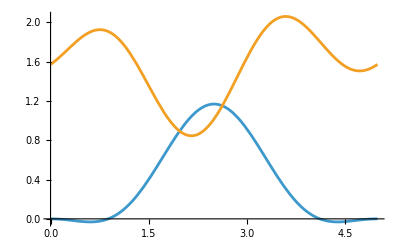

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

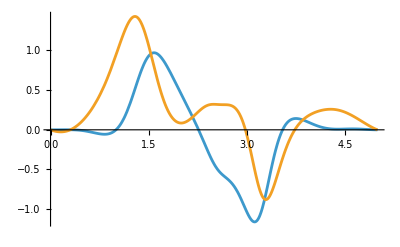

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

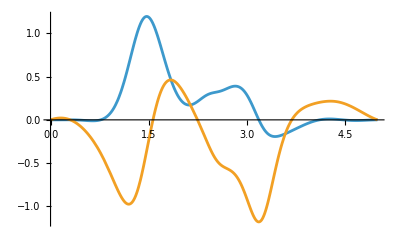

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

1.31794×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

4.5287×10^-34

NDSolve::precw: The precision of the differential equation ({«1»}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,1.767238241920695×10^-6+5.928216736237463×10^-6 ⅈ,1.127045722533195+0.6604936632418622 ⅈ}.

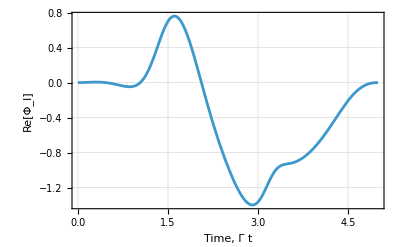

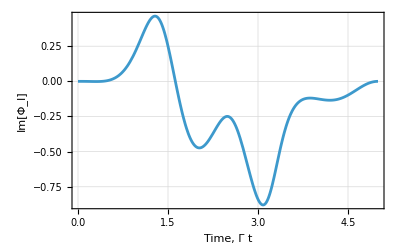

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$77414950[t]} = {5.,{{1.59177987804987434479811596804+3.66359819817819976276131053338×10^-15 ⅈ,-«36»+«35» ⅈ},{«36»+«35» ⅈ,-«35»+«1»}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$77414976[t]} = {5.,{{0.831074137267293258074239-1.74826628221456145878677 ⅈ,-1.15806151225026214997437×10^-11-«33» ⅈ},{-«33»+«1»,«1»}}}.

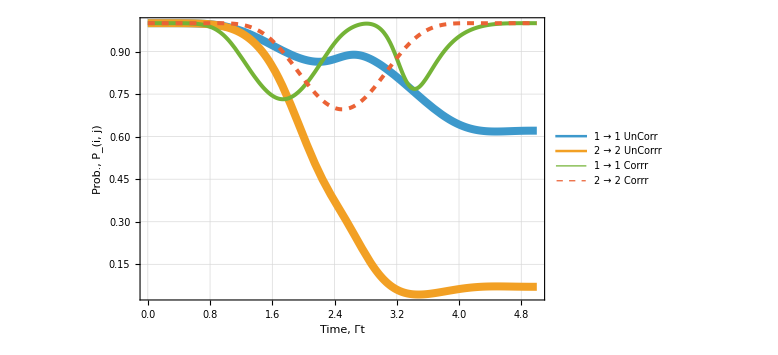

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

##### ϕ=π/20

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=5/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=π/20;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation ({«1»,{},{},{},{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,5.788214402866805-0.8715369897653443 ⅈ,-20.39108601804845+0.8501587189777524 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({«1»,{},{},{},{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-4.254754395639149+0.6020755974432877 ⅈ,2.96448828877898+0.865700890774121 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({«1»,{},{},{},{}}) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-0.03513802744166892-4.795411810683872 ⅈ,1.269966261080589+0.2940374665307195 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{61686.2,{5.2654×10^-8,{A1→3.26045,C1→-3.95618,D1→-1.99555,A2→-1.16236,C2→5.,D2→5.}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

3.26045

-3.95618

-1.99555

-1.16236

5.

5.

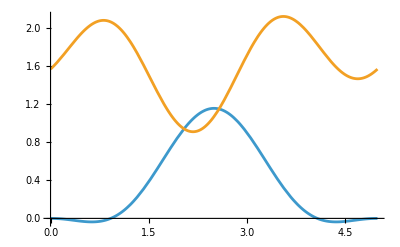

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

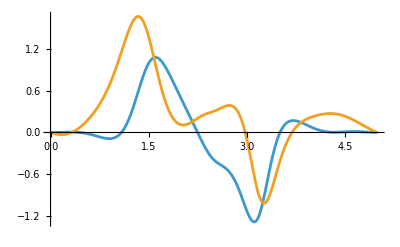

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

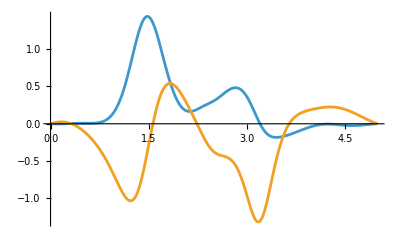

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

1.45326×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-1.47209×10^-17

NDSolve::precw: The precision of the differential equation ({{«1»},{},{},{},{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,1.329622438736031×10^-6+3.946501856317148×10^-6 ⅈ,1.13845393885065+0.6478255626913415 ⅈ}.

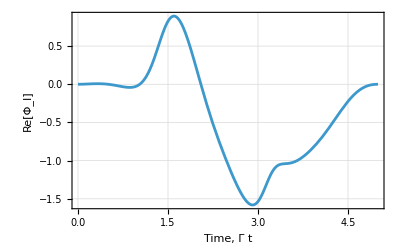

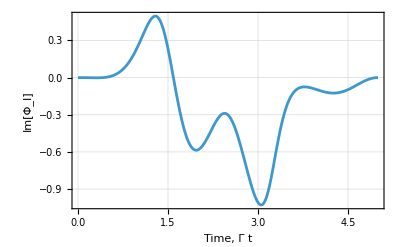

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$154961045[t]} = {5.,{{1.56558195404364557838999446108+0.282251871086984719981623132394 ⅈ,-0.663181710408305483794428650828+0.868098398198854447475251099299 ⅈ},{0.779942772926673171378051960312+1.17556655594612247939899714051 ⅈ,-0.344107670341359437029950085026-«38» ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$154961069[t]} = {5.,{{0.800865953884771601106671-1.73550793234302743354368 ⅈ,-9.61440507784818081199519×10^-12-9.86428349858796248347112×10^-12 ⅈ},{-1.68887374751467091393256×10^-6+1.47973068075011674649067×10^-6 ⅈ,0.219212689664721683523532+0.47504249610232410946647 ⅈ}}}.

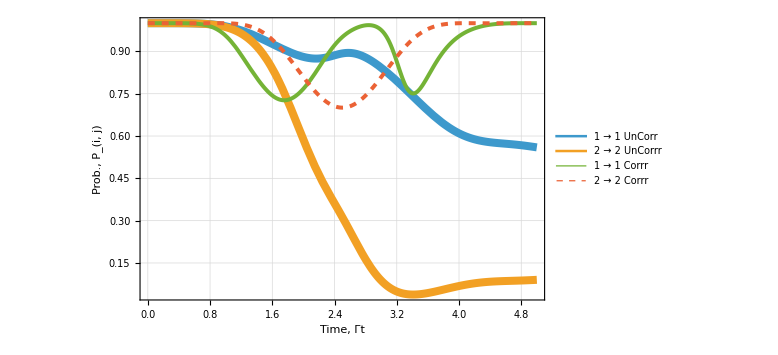

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

##### ϕ=π/10

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=5/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=π/10;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+Times[«2»]+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,33141413/105492394,«1»&,1,5,t]]+«9»+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-((Times[«2»]+Re[«1»]) Sin[Times[«2»]] Sin[Times[«2»]])+«4»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-6.263056495259274-1.727253965009006 ⅈ,-0.2641384274056497+0.8386025416967654 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+Times[«2»]+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,33141413/105492394,«1»&,1,5,t]]+«9»+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-((Times[«2»]+Re[«1»]) Sin[Times[«2»]] Sin[Times[«2»]])+«4»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-4.521370402061062+1.278240594164855 ⅈ,2.982494565599789+0.8508781894778266 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+Times[«2»]+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,33141413/105492394,«1»&,1,5,t]]+«9»+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 (-((Times[«2»]+Re[«1»]) Sin[Times[«2»]] Sin[Times[«2»]])+«4»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,1.026249871357814-5.160519617469659 ⅈ,1.252473665753406+0.2576126270896863 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{150489.,{3.5255×10^-8,{A1→5.,C1→-0.140855,D1→4.41056,A2→-1.66114,C2→1.98934,D2→4.11922}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

5.

-0.140855

4.41056

-1.66114

1.98934

4.11922

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

1.13274×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-2.31661×10^-17

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,4.603346948427151×10^-6-8.733908015780838×10^-6 ⅈ,2.229805927348682+0.6245377691136386 ⅈ}.

-Graphics-

-Graphics-

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$226147799[t]} = {5.,{{1.48858657189009482454131559475+0.552808057036315091216823229562 ⅈ,-0.596376081733453883958169319799+0.748446079366319060174254023429 ⅈ},{0.819508440119001041804021170788+1.36883047394388934002973307324 ⅈ,-0.347492503426864989208955174392-0.00731110984388436255945204409454 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$226147823[t]} = {5.,{{-1.14346218839343455548279-1.47635090447222850573313 ⅈ,-8.74378200049678150950055×10^-12-7.84645914956844794757461×10^-12 ⅈ},{2.17028824088663758636883×10^-6+4.80561054478721899217922×10^-6 ⅈ,-0.327910401673330979929666+0.423372825969543107093359 ⅈ}}}.

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

-Graphics-

##### ϕ=3π/20

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=5/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=3π/20;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,5.012950109306275+5.100294588730273 ⅈ,1.13457728461724+0.8206349363938024 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-4.657292831953644+2.170763594850873 ⅈ,3.015358559094065+0.8291410050143985 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,2.214172438334163-5.302394487387716 ⅈ,1.238783198070378+0.2203268881889389 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{38533.7,{1.41739×10^-8,{A1→4.94549,C1→-1.75831,D1→-5.,A2→-2.0314,C2→2.32846,D2→1.29598}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

4.94549

-1.75831

-5.

-2.0314

2.32846

1.29598

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

2.06147×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-6.42578×10^-17

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-8.883653563556171×10^-7+7.778023611056352×10^-6 ⅈ,0.9005275575907914+0.600229876923422 ⅈ}.

-Graphics-

-Graphics-

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$277936955[t]} = {5.,{{1.36542183995962408929383747505+0.800937663902918224503288722961 ⅈ,-0.528732107572691096961445161482+0.64746224002797735530503415482 ⅈ},{0.837101204802805145207677618678+1.59086563480458243012761909739 ⅈ,-0.353144477736700363759774225203-0.0119403434657767384267680140157 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$277936979[t]} = {5.,{{1.13215425984229419755781-1.42824033333746517522419 ⅈ,-1.62092466693641626111983×10^-11-7.59175492211317007422226×10^-12 ⅈ},{-3.63946060769382185130053×10^-6+2.30085255995383066550258×10^-6 ⅈ,0.340841570020271991270927+0.429979990230993408944472 ⅈ}}}.

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

-Graphics-

##### ϕ=π/5

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=5/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=π/5;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,6.008583650939755-2.578665328726113 ⅈ,1.729085101505409+0.7960715920796605 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-4.557031940148121+3.330059540372981 ⅈ,3.069331260738333+0.8006316385298775 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,3.473383413563006-5.182271324242262 ⅈ,1.22925897568438+0.1825487527832315 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{52638.5,{4.78477×10^-8,{A1→3.3744,C1→-1.78084,D1→-4.56306,A2→-1.42893,C2→3.52786,D2→2.01069}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

3.3744

-1.78084

-4.56306

-1.42893

3.52786

2.01069

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

2.16005×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-9.185×10^-17

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,2.784124408671357×10^-6+0.00002773936394045316 ⅈ,0.9649153077323294+0.57723656613157 ⅈ}.

-Graphics-

-Graphics-

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$354244253[t]} = {5.,{{1.20327020909201941627816542251+1.01771627003611613636734028478 ⅈ,-0.462553887455739623353755256223+0.562178198319523799681162206619 ⅈ},{0.823671666860756866152963851691+1.84175036139356048491075404899 ⅈ,-0.361076106254201056283322407667-0.0177728223346698239694412511909 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$354244277[t]} = {5.,{{1.01431797753549232211386-1.46407335188756859579317 ⅈ,-1.2759642293999810543829×10^-11-5.09747846511640227299693×10^-12 ⅈ},{-0.0000119195141008645680218564+0.0000100758055913691581096466 ⅈ,0.319736921030110065187996+0.461510410011947624215589 ⅈ}}}.

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

-Graphics-

##### ϕ=π/4

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=5/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=π/4;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,2.421423095199099-5.858408616363777 ⅈ,2.076033206487476+0.7648526820053364 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-4.021993560510386+4.786610975794012 ⅈ,3.153318543635144+0.7655868363588437 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,4.735691774138444-4.778422232748502 ⅈ,1.224263549038488+0.1446368106511912 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{57599.5,{7.33985×10^-8,{A1→4.44435,C1→-1.73394,D1→-3.55154,A2→-1.96007,C2→4.32752,D2→3.44961}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

4.44435

-1.73394

-3.55154

-1.96007

4.32752

3.44961

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

2.28798×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-1.25351×10^-16

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,3.897636570169541×10^-7+4.448210201720091×10^-6 ⅈ,0.9944370086764807+0.5429042644733262 ⅈ}.

-Graphics-

-Graphics-

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$63579064[t]} = {5.,{{1.01115692995915534942324018518+1.19664330466554687498083721087 ⅈ,-0.39938563406489557221239196536+0.489857419388059380847459687348 ⅈ},{0.768748780060461762026037229286+2.11934893131464348240700020097 ⅈ,-0.371298462764828770209013414878-0.0252665070303330438211327038318 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$63579090[t]} = {5.,{{0.937900808515208213088958-1.44297459810942934643263 ⅈ,-7.57590917627825125086499×10^-12-5.35814437622529504515704×10^-12 ⅈ},{-2.05809053142823230833656×10^-6+1.63493235229587577663558×10^-6 ⅈ,0.316662219992801292496432+0.487189621204174220259875 ⅈ}}}.

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

-Graphics-

##### ϕ=3π/10

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=5/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=3π/10;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-1.079339965774162-6.26513814794989 ⅈ,2.319636255416717+0.7270427040053875 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-2.689648439705455+6.468615618754749 ⅈ,3.280751834756213+0.7243381098628125 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,5.925886445629281-4.091212282292856 ⅈ,1.224165776480654+0.1069357970902617 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{59758.2,{2.34298×10^-7,{A1→3.33839,C1→-4.99942,D1→3.79126,A2→-4.3507,C2→-4.99166,D2→-4.79952}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

3.33839

-4.99942

3.79126

-4.3507

-4.99166

-4.79952

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

7.63372×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-5.21536×10^-16

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,3.188078749562269×10^-6+1.538539931402409×10^-6 ⅈ,4.186275650320394+0.7980553935576013 ⅈ}.

-Graphics-

-Graphics-

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$61585585[t]} = {5.,{{0.799106376972850152045573677708+1.33397271383675126987013709214 ⅈ,-0.340205938610271092392461457528+0.428061697614507087749622468213 ⅈ},{0.660873502769419745480703982111+2.41854485378307775940530835027 ⅈ,-0.383815471756759428210347295013-0.0349256655693646163433261518957 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$61585611[t]} = {5.,{{-1.11544232136712330359038+1.9208318613084910907786 ⅈ,-8.07683025044856451297642×10^-13+5.39017434113891922366551×10^-12 ⅈ},{-8.91109193398623712467214×10^-8-1.57056729377857381008388×10^-6 ⅈ,-0.226081484162353668451205-0.389320460342283639945163 ⅈ}}}.

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

-Graphics-

##### ϕ=7π/20

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=5/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=7π/20;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-3.781162656547161-5.203449777210167 ⅈ,2.516816620227601+0.682826475729734 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,0.03527522968748079+7.943125104629844 ⅈ,3.473397662567942+0.6773124974056613 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,6.969746590192614-3.145924602875662 ⅈ,1.229336321074293+0.06977219571263831 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{26676.8,{2.54164×10^-7,{A1→3.0324,C1→-4.99705,D1→3.10621,A2→-4.90797,C2→0.400073,D2→0.293099}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

3.0324

-4.99705

3.10621

-4.90797

0.400073

0.293099

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

8.37783×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-7.00306×10^-16

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-3.055862859350116×10^-6+5.210549693153346×10^-6 ⅈ,3.370584165641885+0.7728961531448321 ⅈ}.

-Graphics-

-Graphics-

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$96908144[t]} = {5.,{{0.577282194386496021364769694271+1.42874147413274879732706083078 ⅈ,-0.285591597524899254636618887161+0.374673179093671845765872673292 ⅈ},{0.488367368087512461558110876572+2.73050974482535771070125398915 ⅈ,-0.398617776190963658680190700777-0.0473091614638646414253032929889 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$96908168[t]} = {5.,{{-2.10948784811878708676599+0.491679203819074107339606 ⅈ,-1.62429961302024363548882×10^-12-1.85265045202751356226644×10^-11 ⅈ},{2.13020989651482774725978×10^-6-1.97167075645758106726217×10^-6 ⅈ,-0.449622419194134612065064-0.104797945761895962792 ⅈ}}}.

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

-Graphics-

##### ϕ=2π/5

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=5/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=2π/5;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-5.639818053886228-3.3000434431583 ⅈ,2.694914681915763+0.63250207021098 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,4.748202537672904+7.689573352658361 ⅈ,3.76988335703051+0.6250320646312124 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,7.803160238380192-1.992398370326347 ⅈ,1.24012504486402+0.03344841535344714 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{41719.5,{1.08506×10^-7,{A1→0.981816,C1→-0.592885,D1→0.407186,A2→-0.515149,C2→4.98604,D2→4.05876}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

0.981816

-0.592885

0.407186

-0.515149

4.98604

4.05876

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

2.75139×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-2.78544×10^-16

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,2.822711176631854×10^-6-4.250201761865902×10^-6 ⅈ,2.139889855479188+0.4348890156006081 ⅈ}.

-Graphics-

-Graphics-

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$154554507[t]} = {5.,{{0.355218519917097160485590222261+1.48252574177404251710033396257 ⅈ,-0.235850592713099511576122327543+0.327889558978312939403820946026 ⅈ},{0.240471661860204464358599407258+3.04214684575822788957343374559 ⅈ,-0.41567735539082186401064571074-0.0630361556149223057962733580143 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$154554531[t]} = {5.,{{-0.832439849296870259137196-1.30131664622707873033421 ⅈ,-1.2215427174884423607754×10^-12+4.50156007383883077116633×10^-12 ⅈ},{1.22633638971719091491734×10^-6+3.14892955662871196449665×10^-6 ⅈ,-0.348829381683330009411684+0.545309647849377249772023 ⅈ}}}.

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

-Graphics-

##### ϕ=9π/20

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=5/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=9π/20;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-6.650177076228445-0.901497965244868 ⅈ,2.867184116975111+0.5764725804332875 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,9.759926751496024+1.862764614229181 ⅈ,4.247698239047317+0.5681113791581866 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,8.380874751057519-0.7009901141767725 ⅈ,1.256807550013305-0.001764793751306932 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{52118.1,{7.08706×10^-8,{A1→2.92426,C1→4.76264,D1→-4.25779,A2→4.99727,C2→-4.98878,D2→2.81795}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

2.92426

4.76264

-4.25779

4.99727

-4.98878

2.81795

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-1.04286×10^-15

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

1.27403×10^-15

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-6.730165551735972×10^-7+2.128000630375801×10^-6 ⅈ,2.768101197244194+0.01077401359334481 ⅈ}.

-Graphics-

-Graphics-

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$61893847[t]} = {5.,{{0.141224151842478989326190670705+1.49898924068398437640423071986 ⅈ,-0.191127032855307323769871438676+0.286205986359135511606695856103 ⅈ},{-0.0911631261606933844491342228134+3.33588346329935620365326362112 ⅈ,-0.434944582416872985957003034012-0.082788186331384448368614005384 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$61893873[t]} = {5.,{{-0.941144578937848105189493-0.368820738614451041893257 ⅈ,-7.0429897041750873255224×10^-12+1.33017730258088278461891×10^-12 ⅈ},{-7.01304528047550290150219×10^-8-2.31393706839213553948709×10^-6 ⅈ,-0.921081710056059055185369+0.360958394961613641228881 ⅈ}}}.

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

-Graphics-

##### ϕ=π/2

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=5/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=π/2;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-6.823029630319527+1.648505492481638 ⅈ,3.036748910390288+0.5152371524957788 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,2.073228728135103-9.130831200635548 ⅈ,5.094027242081201+0.5072508938336833 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,8.683160396458657+0.6449089777729306 ⅈ,1.279487268994355-0.03563786488659719 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{28855.,{8.57883×10^-8,{A1→1.37482,C1→4.99961,D1→-4.35659,A2→4.99952,C2→-4.98331,D2→2.86463}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

1.37482

4.99961

-4.35659

4.99952

-4.98331

2.86463

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-1.1301×10^-15

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

1.6692×10^-15

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-3.694444402215444×10^-6+7.177621216246728×10^-6 ⅈ,2.687164825438925+0.02317787589744893 ⅈ}.

-Graphics-

-Graphics-

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$98218678[t]} = {5.,{{-0.0579935098139115808329670581582+1.48330738460665765663798931989 ⅈ,-0.151481965052099503886847533002+0.248394045438736074136889477036 ⅈ},{-0.510737512708111281606740151052+3.58999909225749146961441833498 ⅈ,-0.456350000487390829536215882022-0.107306002669152918528282220539 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$98218702[t]} = {5.,{{-0.9195811566568617166815-0.449240993252252774963808 ⅈ,8.3238379569233155158802×10^-13+1.4314619305133252723606×10^-12 ⅈ},{3.79900520418550617170851×10^-7-8.09236267765350039446949×10^-6 ⅈ,-0.877926214644716381967629+0.428891394548894529346946 ⅈ}}}.

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

-Graphics-

##### ϕ=11π/20

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=5/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=11π/20;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-6.337283964961312+3.91831656200575 ⅈ,3.196071348175733+0.4493828631641667 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,4.18371257549716+9.97313938588321 ⅈ,6.94332545858607+0.4432270105902272 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,8.718796071553592+1.958711780581337 ⅈ,1.307936317388491-0.06799491881311278 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{17530.3,{2.84674×10^-7,{A1→3.5006,C1→4.41467,D1→-4.17223,A2→4.69387,C2→-4.84499,D2→-1.12545}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

3.5006

4.41467

-4.17223

4.69387

-4.84499

-1.12545

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-8.46531×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

1.52257×10^-15

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,2.453039912009165×10^-6+1.252021136533304×10^-6 ⅈ,0.3885012304717135-0.1649701145624466 ⅈ}.

-Graphics-

-Graphics-

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$121572561[t]} = {5.,{{-0.237474618059498749322873855367+1.44155200169731816009695096362 ⅈ,-0.116953305625728729250895730987+0.213485921697342084856619637789 ⅈ},{-1.01650625613496300287648320457+3.77965067640234614561001059532 ⅈ,-0.479813618048971659412753598641-0.137378327371739013038114334887 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$121572585[t]} = {5.,{{0.784730290198792091545858-0.321193224896723929852982 ⅈ,-3.42330456990138495541883×10^-12+8.66554914910672524396973×10^-14 ⅈ},{2.40861362467156380429427×10^-6+2.62226676694329170948642×10^-6 ⅈ,1.09146956689321809523595+0.446742829260790195647602 ⅈ}}}.

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

-Graphics-

##### ϕ=3π/5

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=5/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=3π/5;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-5.695120195094971+5.4669595013026 ⅈ,3.325455749191844+0.379578970883958 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-7.793099780760427+6.517282820538316 ⅈ,15.78859136800431+0.3768771262422397 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,8.523441364367224+3.161023088054192 ⅈ,1.341354823059578-0.09872994363243675 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{36826.1,{2.52263×10^-7,{A1→1.30603,C1→5.,D1→-0.883032,A2→4.99932,C2→-4.86895,D2→4.00063}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

1.30603

5.

-0.883032

4.99932

-4.86895

4.00063

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-9.58468×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

2.12596×10^-15

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-2.256090924617281×10^-6+8.54483619330994×10^-6 ⅈ,2.770141503583867-0.01249365600635388 ⅈ}.

-Graphics-

-Graphics-

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$163778432[t]} = {5.,{{-0.393944673131918849015829165899+1.38010729097548518841900546487 ⅈ,-0.0875957001271963871831567846215+0.18077033404602215061855283005 ⅈ},{-1.59920591747859298277463584317+3.8786820955945792240547199021 ⅈ,-0.505264550750980333099755279508-0.173817374336044324659095922193 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$163778456[t]} = {5.,{{-0.920232421995716369425633-0.358461396209734370188392 ⅈ,6.45416655036322778501882×10^-12-1.86477336497231575664332×10^-12 ⅈ},{-1.06344783778905699837481×10^-6-9.0787341871765272581149×10^-6 ⅈ,-0.943516248918733954382586+0.367531227831423819522514 ⅈ}}}.

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

-Graphics-

##### ϕ=13π/20

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=5/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=13π/20;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-2.342243012735796-9.45910633275475 ⅈ,8.932826854559551+0.509806605435136 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-5.628406089429048+5.945631893191468 ⅈ,3.39548744743931+0.3065749068293629 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,8.153464589764011+4.188562075523702 ⅈ,1.378027486924792-0.1278267409634712 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{45800.6,{5.68937×10^-8,{A1→0.371608,C1→4.99999,D1→-4.99828,A2→4.99696,C2→-4.97746,D2→-2.01039}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

0.371608

4.99999

-4.99828

4.99696

-4.97746

-2.01039

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-9.63147×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

2.68497×10^-15

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,6.480286886182529×10^-6+1.569103156958847×10^-7 ⅈ,0.6628950892661352-0.1024174763202699 ⅈ}.

-Graphics-

-Graphics-

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$211893228[t]} = {5.,{{-0.525588586132955952051475711973+1.30516198821637536110595609477 ⅈ,-0.0634964504941873363056347385354+0.14980514019161085213100676856 ⅈ},{-2.2410432592732884587839711738+3.86217953870179651098104858567 ⅈ,-0.532672268559645596640775455304-0.217411695394734347192357624843 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$211893252[t]} = {5.,{{0.711483368932416883917232-0.555493665894679535034148 ⅈ,-1.45764506763704362944954×10^-12+6.20438447497331041623433×10^-12 ⅈ},{5.09855191197980789594133×10^-6+4.46937323461174683945824×10^-6 ⅈ,0.873219518931493061422207+0.681769852780465031387251 ⅈ}}}.

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

-Graphics-

##### ϕ=7π/10

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=5/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=7π/10;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-9.525474021994645+0.4089118119092174 ⅈ,6.496886083365019+0.4290901939961883 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-6.550837324259809+4.938701992633515 ⅈ,3.378582846755641+0.2312035436506481 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,7.67617991288638+5.000161436877377 ⅈ,1.414860965094127-0.1553825364822136 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{53799.,{1.38286×10^-8,{A1→0.472379,C1→3.82558,D1→1.98096,A2→2.56678,C2→-3.35184,D2→4.15987}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

0.472379

3.82558

1.98096

2.56678

-3.35184

4.15987

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-7.85675×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

2.82655×10^-15

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

NDSolve::precw: The precision of the differential equation ({«1»}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,6.451986002268844×10^-7+1.307706918848393×10^-6 ⅈ,3.167563064011334-0.06285226583342069 ⅈ}.

-Graphics-

-Graphics-

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$269360627[t]} = {5.,{{-0.631721091412605638608853102812+1.22229103534720202320899460922 ⅈ,-0.0447561481505768637404148562076+0.120447362086457276236942692709 ⅈ},{-2.91557414246646437551614871723+3.7095694817261703765128206358 ⅈ,-0.562084917407920154623064176626-0.268840319301733366993114920347 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$269360651[t]} = {5.,{{-0.938765528372575152367597+0.0243855891798601534047318 ⅈ,9.82574451400607425585576×10^-12+3.57331878773300062415797×10^-12 ⅈ},{-8.38539952855898384976677×10^-7-1.53281810897194686403881×10^-6 ⅈ,-1.06451042385911377411541-0.0276519674868512802660324 ⅈ}}}.

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

-Graphics-

##### ϕ=3π/4

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=5/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=3π/4;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,4.282989031653056-7.094834782589817 ⅈ,5.513704482057429+0.3445199606972442 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-7.698192722061727+1.900239999023602 ⅈ,3.266481058699433+0.1543889870550571 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,7.157670859125389+5.579775503702048 ⅈ,1.44681628187337-0.1816323914413179 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{43673.2,{1.4456×10^-7,{A1→0.874939,C1→4.47885,D1→-1.47512,A2→5.,C2→-4.48791,D2→-0.908572}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

0.874939

4.47885

-1.47512

5.

-4.48791

-0.908572

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-6.711×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

3.22983×10^-15

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

NDSolve::precw: The precision of the differential equation ({«1»}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,1.078649440755079×10^-6-6.8916692621839×10^-9 ⅈ,0.6771486921373083-0.1695260037631006 ⅈ}.

-Graphics-

-Graphics-

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$316765331[t]} = {5.,{{-0.712427710454865314870772027593+1.13610945223899790831637137069 ⅈ,-0.0314132228284041423846455121225+0.0928896357210613958901967641716 ⅈ},{-3.58871278189894845550704418274+3.40787703731193235055618860783 ⅈ,-0.593654903670726364217064576145-0.328525014160260432414852822647 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$316765355[t]} = {5.,{{0.657832415216017561356011-0.528868524413359297570273 ⅈ,-4.06832195656609439628172×10^-12+6.47935931692825716521248×10^-12 ⅈ},{7.80699868790656407761687×10^-7+5.51735262240609709272475×10^-7 ⅈ,0.923344319162015474328048+0.742328496275193259633299 ⅈ}}}.

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

-Graphics-

##### ϕ=4π/5

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=5/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=4π/5;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,6.82024019749223+2.864094111747472 ⅈ,4.889427603247264+0.2576561074120059 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-6.996645588749459-2.741688900426281 ⅈ,3.07849485638902+0.07715312073371748 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,6.648482808058235+5.938312003292682 ⅈ,1.466426243120534-0.2069679623726994 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{50543.,{5.22107×10^-7,{A1→4.13592,C1→0.661376,D1→3.15251,A2→0.0868538,C2→-4.88786,D2→-5.}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

4.13592

0.661376

3.15251

0.0868538

-4.88786

-5.

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-1.63162×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

1.10276×10^-15

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

NDSolve::precw: The precision of the differential equation ({«1»}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,1.079522983018495×10^-6+1.966951237205456×10^-6 ⅈ,3.304986524232878-0.3895017383449224 ⅈ}.

-Graphics-

-Graphics-

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$388526504[t]} = {5.,{{-0.768273565729324309409155318248+1.04996516405254357904730680922 ⅈ,-0.0232877727484371276764284892801+0.0676646036601167719103779455717 ⅈ},{-4.22094126767834966759032950759+2.95460466912061069334477856541 ⅈ,-0.62759975722268348372830856663-0.39639968832781999458132652341 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$388526528[t]} = {5.,{{-0.668372021651953726148723+0.110190296303640536656651 ⅈ,4.83227526135691492597124×10^-12+2.92905222911180587926027×10^-12 ⅈ},{-9.62835663368775036736752×10^-7-3.26843954885944629477062×10^-6 ⅈ,-1.45658275607931076683621-0.240137648309821721842199 ⅈ}}}.

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

-Graphics-

##### ϕ=17π/20

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=5/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=17π/20;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-0.3157784579565563+6.053539461780896 ⅈ,4.35717422451425+0.170301273681004 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-3.152406563677129-6.489928915056631 ⅈ,2.851778704516781+0.0006066988077473608 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,6.166497439237288+6.117459802874397 ⅈ,1.464211343907155-0.2319375869041692 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{29797.9,{3.89751×10^-7,{A1→1.18601,C1→4.90656,D1→-0.763275,A2→2.98633,C2→-4.9999,D2→-2.25801}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

1.18601

4.90656

-0.763275

2.98633

-4.9999

-2.25801

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-3.67952×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

3.73817×10^-15

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

NDSolve::precw: The precision of the differential equation ({«1»}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,1.054698575772878×10^-7-2.673065001828333×10^-8 ⅈ,0.4258615242263838-0.3197997596100941 ⅈ}.

-Graphics-

-Graphics-

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$422623030[t]} = {5.,{{-0.800212346594819684830014662498+0.965665737714986577855569426476 ⅈ,-0.0197459591752353495744465589524+0.0455322396959816862585868240886 ⅈ},{-4.77058320045602785999472793903+2.35959718840054535086057994997 ⅈ,-0.663998000366669167327258842606-0.471615156834729935885059097521 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$422623054[t]} = {5.,{{0.661424152226604584493312-0.30003622674738014780286 ⅈ,-9.10122652250277998341113×10^-12-7.74636101508510902706818×10^-12 ⅈ},{1.54417738661042013067346×10^-7-1.24891052087232075947542×10^-7 ⅈ,1.25387598095359489365242+0.568785123544719225843859 ⅈ}}}.

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

-Graphics-

##### ϕ=9π/10

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=5/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=9π/10;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,7.535972110887766-12.49293406602165 ⅈ,94.1102069060636+0.6527362514480093 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-4.10646632889473+1.109807306733283 ⅈ,3.836954930250483+0.08433755552849295 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,2.129409731029389-6.804781303656212 ⅈ,2.624828141860204-0.07409750491413752 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{43557.8,{4.99242×10^-8,{A1→0.561382,C1→4.99973,D1→-4.2477,A2→4.99933,C2→-3.19963,D2→-2.59856}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

0.561382

4.99973

-4.2477

4.99933

-3.19963

-2.59856

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

1.49568×10^-16

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

5.58651×10^-32

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

NDSolve::precw: The precision of the differential equation ({«1»}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {10.,8.685925353145513×10^-6+7.760504560761937×10^-6 ⅈ,1.346375740200326+1.47650712738853 ⅈ}.

-Graphics-

-Graphics-

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$43234055[t]} = {10.,{{6.35036368605232994306036361472-6.24872681448978110008914170739×10^-14 ⅈ,-0.810474033811414920402736838079-1.2326577176690833756746741159 ⅈ},{0.810474033811430959395193703519-1.23265771766910702388063829177 ⅈ,-0.18523556548350290272921637816-7.89889550662384801228919208965×10^-16 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$43234080[t]} = {10.,{{0.974204025135478935336791-4.26785160645320487719787 ⅈ,-2.87722749232177913579441×10^-11+1.10166978175563879889307×10^-11 ⅈ},{-1.29702374296736753030928×10^-6+2.29239948547870376586249×10^-6 ⅈ,0.0508360881322988815970707+0.222705793446665364705914 ⅈ}}}.

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

-Graphics-

##### ϕ=19π/20

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=5/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=19π/20;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,13.12191874709556+4.164536905685505 ⅈ,18.12713942367035+0.6077900357647521 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-1.385567713976663-2.262682396935864 ⅈ,3.394472991763163+0.001469461134617559 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,5.86827753989673-4.033950866625383 ⅈ,2.426642176723181-0.1458703472347381 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{56728.4,{0.0000103912,{A1→4.89311,C1→4.99986,D1→3.02931,A2→-2.86247,C2→-4.1826,D2→0.89999}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

4.89311

4.99986

3.02931

-2.86247

-4.1826

0.89999

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

3.35403×10^-17

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-1.2418×10^-15

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

NDSolve::precw: The precision of the differential equation ({«1»}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,0.00001266010847848683+4.037332558416592×10^-7 ⅈ,10.05930962202984-0.3478196606911942 ⅈ}.

-Graphics-

-Graphics-

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$534032091[t]} = {5.,{{-0.799930078304349240803017646634+0.80179240588357530996562124286 ⅈ,-0.0206008232769090779041323310586+0.0123917982258501686741265168949 ⅈ},{-5.46933146733786223408649770587+0.845076175250665779506624678072 ⅈ,-0.74057819272665309228872888464-0.63581288886389213081508581985 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$534032115[t]} = {5.,{{-0.568758868183951000984934+0.41865120798040648847384 ⅈ,1.46131368187590076365697×10^-12+2.4299855776464678225306×10^-12 ⅈ},{-0.0000143602729841259348148267-0.000010370172307750685921343 ⅈ,-1.14035611909247243403779-0.839391688623061699518595 ⅈ}}}.

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

-Graphics-

##### ϕ=π

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=5/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=π;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,-3.169286043645571+13.32523291708466 ⅈ,11.15230823711867+0.5633471660021206 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,0.9653919284581613-1.478800404524048 ⅈ,3.12864156122431-0.07707602774644901 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,7.018895373228805-0.4968553987830887 ⅈ,2.27112124165336-0.2138391165808608 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/2000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{26204.6,{4.85764×10^-6,{A1→0.624604,C1→4.80571,D1→0.880664,A2→3.35076,C2→-4.22266,D2→-4.9878}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

0.624604

4.80571

0.880664

3.35076

-4.22266

-4.9878

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

-Graphics-

```mathematica
PlotRange
```

```mathematica
Plot[{gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0},PlotRange->All]
```

-Graphics-

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}, PlotRange->All]
```

-Graphics-

```mathematica
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

-4.43576×10^-31

```mathematica
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]
GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t0(1-10^-16),totalterms]
```

0.

5.35998×10^-15

```mathematica
DoubleInt[t_]=TotalIntSolvPlot[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
Plot[Re[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Re[Φ_I]"}]
Plot[Im[DoubleInt[t]],{t,0,t0},Frame->True,GridLines->Automatic,FrameLabel->{"Time, Γ t", "Im[Φ_I]"}]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {5.,8.918186248758923×10^-8+7.032105742823092×10^-6 ⅈ,-6.663944819030621-0.3835450179083891 ⅈ}.

-Graphics-

-Graphics-

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$565163854[t]} = {5.,{{-0.774950495877689364694865109585+0.719435376876129251279717904454 ⅈ,-0.0212378814853787206318965983307-9.07939083280853252394210933227×10^-15 ⅈ},{-5.5624913738834796887738201708+3.07293547761633589166818599447×10^-14 ⅈ,-0.774950495877657143260419240156-0.719435376876159016467184808951 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$565163878[t]} = {5.,{{0.632643678535640680338036+0.253243230393446784500287 ⅈ,-2.5022990114827951643959×10^-12+8.78835938137830693794964×10^-12 ⅈ},{3.45866585157492448581502×10^-6+9.67031699542502696489047×10^-6 ⅈ,1.36236936845606972994597-0.545347770873769540636066 ⅈ}}}.

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

-Graphics-

#### Uncorrected & CCP Error Fidelity Plot

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
t0=5;
totalterms=3;
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
σδΔ0=10^-16; 
NSamp=1;
cinit={1,0}; 
cfinal={1,0};
```

```mathematica
optoparamsNormTerms=N[{
{0,4.999668425496864,-4.991336231509653,-3.437494297455737,-1.7275556445008178,4.907266029231373,5.},
{π/20,3.2604534389219104,-3.956175167071237,-1.9955450455500225,-1.1623619777817127,5.,5.},
{π/10,5.,-0.14085483237778965,4.410555133772426,-1.6611368402648046,1.9893427475375132,4.1192211796716744},
{3π/20,4.945487641957082,-1.7583076572787366,-5.,-2.031400707533549,2.3284584430991826,1.2959795397882672},
{π/5,3.374402108211284,-1.7808362137290124,-4.563056545007404,-1.428925612809256,3.527855882920227,2.010693052356389},
{π/4,4.4443490962812575,-1.7339446455875491,-3.5515449562937675,-1.9600740542894812,4.327518877271064,3.4496132525514143},
{3π/10,3.3383873087611713,-4.999420424764114,3.791257585378752,-4.350702588800922,-4.991664577400256,-4.799521292290136},
{7π/20,3.032395141185639,-4.9970512261002415,3.1062129307790878,-4.907970728575336,0.40007302875356643,0.2930987907600752},
{2π/5,0.9818158759014695,-0.5928851965759361,0.4071860458479283,-0.5151489479472617,4.986041860615289,4.05876229212009},
{9π/20,2.9242615431220567,4.762638703472798,-4.257787277624145,4.997267668194698,-4.988778300047705,2.8179490672750926},
{π/2,1.3748238650566929,4.999608269939566,-4.356586106954369,4.999522049171844,-4.983314781096854,2.8646339387897366},
{11π/20,3.500599695902264,4.41467191397236,-4.172229353431543,4.693866339719022,-4.8449861423961975,-1.1254473227355017},
{3π/5,1.3060318862565354,5.,-0.8830316829416915,4.999320020832399,-4.868954132503743,4.000629297750515},
{13π/20,0.3716083166080465,4.999989928799347,-4.998276473349868,4.996956225075821,-4.977457132286922,-2.010388141022269},
{7π/10,0.4723792578145185,3.8255810290324512,1.9809617201556065,2.566784255253545,-3.35183564625184,4.1598675535108525},
{3π/4,0.8749385650298668,4.478852065015881,-1.475117138755345,5.,-4.487913745927242,-0.9085719848083201},
{4π/5,4.135916130914301,0.6613762226297821,3.1525122215123536,0.0868538151932417,-4.887857150961593,-5.},
{17π/20,1.186010436091566,4.9065624485678025,-0.7632751776181916,2.986326044681547,-4.999899846928235,-2.258008956468249},
{9π/10,0.561382323961239,4.999729663517924,-4.247702444687125,4.999326639209837,-3.1996318595598696,-2.598564718589659},
{19π/20,4.893107378108289,4.999864568482818,3.029314933065356,-2.862474932006309,-4.182603815052605,0.8999903002325133},
{π,0.62460371667565,4.805705737414463,0.88066413352442,3.3507612227859505,-4.222661703592676,-4.987802229045183}
}];
```

```mathematica
ParallelEvaluate[Off[InterpolatingFunction::dmval]];
ParallelEvaluate[Off[General::munfl]];
ParallelEvaluate[Off[NDSolve::nlnum]];
```

```mathematica
(*gain mode*)
```

```mathematica
AbsoluteTiming[GainModeOptoNoImp=Map[{#[[1]],ErrorAnalysisFixedTimeRF[Δ0,Ω0,Γ,#[[1]],ω,dir,t0/Γ,totalterms,σδΔ0,NSamp,cinit,cfinal,Rationalize[#[[2]]],Rationalize[#[[5]]],A3,B1,B2,B3,Rationalize[#[[3]]],Rationalize[#[[6]]],C3,Rationalize[#[[4]]],Rationalize[#[[7]]],D3]}&,optoparamsNormTerms]]
```

```mathematica
GainModeOptoPhi={{0.,-11.84327545055382333208027224853171612833`11.278809919291424},{0.15707963267948966,-11.8993558438274440170768235109964650391`11.30053990893088},{0.3141592653589793,-11.16525189478674128486252087920934434312`11.949356348797112},{0.47123889803846897,-11.2623309194465271707680485212925628014`11.839392335420362},{0.6283185307179586,-10.11634665134427726764892530530589608221`12.944101806055329},{0.7853981633974483,-11.66139977076447822071099303052328983968`11.46556025598485},{0.9424777960769379,-12.35160743266912511394349570257149940162`10.814721752391623},{1.0995574287564276,-11.74030860202387346170744966627947147259`11.672192200735145},{1.2566370614359172,-11.42915630592434061725577599220882324801`11.854198214305425},{1.413716694115407,-11.26767702917351554813957864514437357487`11.85755474630049},{1.5707963267948966,-10.18319865243865800516057865242661918319`12.87308603325178},{1.7278759594743864,-10.73211392074927698459197755892828576028`12.534402455366108},{1.8849555921538759,-10.04291240681112633028188159576254048507`13.023259193390144},{2.0420352248333655,-10.20546168682819785444956836218266917063`12.994883808335196},{2.199114857512855,-11.3949224288500776881310776262362585356`11.865886974350216},{2.356194490192345,-11.63248371165678220380616360092644884051`11.60239127354446},{2.5132741228718345,-10.5761488092569787089771715396502967317`12.633712797630496},{2.670353755551324,-13.0306197916118586584`10.248756758673075},{2.827433388230814,-9.90658305759743763299440465220393993567`13.240849109221301},{2.9845130209103035,-9.19839236380779502186354112586104216757`13.929562715462104},{3.141592653589793,-9.64132382651731336662858019120685109443`13.505732871227826}};
```

```mathematica
(*loss mode*)
```

```mathematica
σδΔ0=10^-16;
NSamp=1;
cinit={0,1};
cfinal={0,1};
```

```mathematica
AbsoluteTiming[LossModeOptoNoImp=Map[{#[[1]],ErrorAnalysisFixedTimeRF[Δ0,Ω0,Γ,#[[1]],ω,dir,t0/Γ,totalterms,σδΔ0,NSamp,cinit,cfinal,Rationalize[#[[2]]],Rationalize[#[[5]]],A3,B1,B2,B3,Rationalize[#[[3]]],Rationalize[#[[6]]],C3,Rationalize[#[[4]]],Rationalize[#[[7]]],D3]}&,optoparamsNormTerms]]
```

```mathematica
LossModeOptoPhi={{0.,-12.9396313058065286041`10.221393563817385},{0.15707963267948966,-14.7495280484368672421`8.575598547643057},{0.3141592653589793,-13.3075540119706575103`9.867216493120463},{0.47123889803846897,-15.518282613073038005`7.752295807837795},{0.6283185307179586,-15.6480462802036620467`7.662825950271683},{0.7853981633974483,-14.5251468095651933346`8.788460949612155},{0.9424777960769379,-14.7482752095629388095`8.637286224422654},{1.0995574287564276,-12.8116667244888318771`10.461845026024804},{1.2566370614359172,-12.6501745225477317139`10.534676432834571},{1.413716694115407,-14.9411113170679979336`8.513133023577332},{1.5707963267948966,-13.4626886368163744615`9.91783949741401},{1.7278759594743864,-13.9133730195617598687`9.30536026129094},{1.8849555921538759,-13.0769364151597174213`10.257392772576074},{2.0420352248333655,-12.8291571420929462109`10.381010537618478},{2.199114857512855,-14.4791825578347893988`8.885102814572532},{2.356194490192345,-12.812738389404213023`10.44352178436233},{2.5132741228718345,-13.8148704371927061418`9.476636091354523},{2.670353755551324,-13.1865277995057879985`10.066886735209042},{2.827433388230814,-13.2270309485306959919`10.052197232980479},{2.9845130209103035,-15.0296376472690682274`8.323565815527049},{3.141592653589793,-14.374864982117847166`8.949934445387296}};
```

```mathematica
FinalFidelitiesGain=ParallelMap[{#[[1]],Log10[FinalAmp[Δ0,Ω0,Γ,#[[1]],ω,dir,t0][[1]]]}&,optoparamsNormTerms]
FinalFidelitiesLoss=ParallelMap[{#[[1]],Log10[FinalAmp[Δ0,Ω0,Γ,#[[1]],ω,dir,t0][[4]]]}&,optoparamsNormTerms]
```

{{0.,-0.421434207393083037534031644},{0.15708,-0.356321163738202144145472002},{0.314159,-0.298994322114983100338692278},{0.471239,-0.249303841488480724873897593},{0.628319,-0.20686649970994259292244478},{0.785398,-0.171111793488727740302875796},{0.942478,-0.141345014351917392722151913},{1.09956,-0.116812535230516280228950605},{1.25664,-0.0967585779951420492781528561},{1.41372,-0.080467138166485919454110913},{1.5708,-0.0672884305598025872816118382},{1.72788,-0.0566511171409435921993893098},{1.88496,-0.048064154012376308646448118},{2.04204,-0.0411118120395795165056222041},{2.19911,-0.0354448555033117535695399476},{2.35619,-0.0307706612671588895498129609},{2.51327,-0.0268451306943806505276611539},{2.67035,-0.0234690990105329519659207718},{2.82743,-0.0204916544588307499733953497},{2.98451,-0.0178186460112146927124015174},{3.14159,-0.0154173096320575055463789219}}

{{0.,-0.0318497505838486716336892376},{0.15708,-0.0410887538094842035826011274},{0.314159,-0.0538105011286107720540812275},{0.471239,-0.0713950348584726560106990268},{0.628319,-0.0957230022763639857588549153},{0.785398,-0.12927489186244732833644686},{0.942478,-0.175166130259995298696696553},{1.09956,-0.237045373422411819355375813},{1.25664,-0.318796332488918751096109437},{1.41372,-0.424073980344060327236549466},{1.5708,-0.555859523569960673707192899},{1.72788,-0.716321516420614434088890048},{1.88496,-0.907171865101535148367577759},{2.04204,-1.13044366140619242816553521},{2.19911,-1.3893954620098842241390246},{2.35619,-1.6891086533131534181919064},{2.51327,-2.0358408341700366074763388},{2.67035,-2.431849302007024221140913},{2.82743,-2.855155597664044352368605},{2.98451,-3.217335287883206982057074},{3.14159,-3.394447270060394914836244}}

```mathematica
FinalFidelitiesGain={{0.,-0.42143420739308303753403164413933997509`27.88047078293691},{0.15707963267948966,-0.35632116373820214414547200214198793692`27.70869336952087},{0.3141592653589793,-0.29899432211498310033869227753230063824`27.621972836066313},{0.47123889803846897,-0.2493038414884807248738975931462780176`27.598940818180832},{0.6283185307179586,-0.20686649970994259292244478003961379962`27.62709276533807},{0.7853981633974483,-0.17111179348872774030287579637562804502`27.703032657324535},{0.9424777960769379,-0.14134501435191739272215191332351670965`27.79763157717777},{1.0995574287564276,-0.1168125352305162802289506050352192259846425737019778924543`27.91416265777676},{1.2566370614359172,-0.0967585779951420492781528561441274662408469535408160505856`27.90098107001497},{1.413716694115407,-0.0804671381664859194541109129833419672343214478059590647808`27.87419558657582},{1.5707963267948966,-0.0672884305598025872816118381610311372177246269942009954304`27.811709070143557},{1.7278759594743864,-0.0566511171409435921993893098031033033004062183495745667071`27.74943873518067},{1.8849555921538759,-0.0480641540123763086464481179958265916121331760697354223615`27.72812450835413},{2.0420352248333655,-0.041111812039579516505622204146790630138192653722294698495`27.74160162283675},{2.199114857512855,-0.0354448555033117535695399476015644236705650381353507717301`27.787830005998575},{2.356194490192345,-0.0307706612671588895498129609401913311458140647946449630107`27.81303787529439},{2.5132741228718345,-0.0268451306943806505276611539148025355985817026479946740268`27.814977337617005},{2.670353755551324,-0.0234690990105329519659207717816953854565257696040433869913`27.812110059817567},{2.827433388230814,-0.0204916544588307499733953497456377969235034881070240487481`27.81053447303038},{2.9845130209103035,-0.017818646011214692712401517417946163980210185485278669939`27.81015879989149},{3.141592653589793,-0.0154173096320575055463789218645741101285904114339486196949`27.81077119700582}};
```

```mathematica
FinalFidelitiesLoss={{0.,-0.0318497505838486716336892375657636267375254859070867851883`27.90849104958886},{0.15707963267948966,-0.0410887538094842035826011273791059314943058282045375512576`27.878139590708333},{0.3141592653589793,-0.0538105011286107720540812275245071826901133288258922348544`27.847427411990544},{0.47123889803846897,-0.0713950348584726560106990268037865352094841948507358625791`27.822643424433227},{0.6283185307179586,-0.0957230022763639857588549152887546845021793372965460508671`27.80002799661859},{0.7853981633974483,-0.12927489186244732833644685983566139207`27.768937714308027},{0.9424777960769379,-0.17516613025999529869669655309037891537`27.73023288911395},{1.0995574287564276,-0.23704537342241181935537581286662635934`27.682909475201956},{1.2566370614359172,-0.31879633248891875109610943706505071098`27.625387446408617},{1.413716694115407,-0.42407398034406032723654946625181943095`27.5492746367382},{1.5707963267948966,-0.55585952356996067370719289873392679559`27.45794000308172},{1.7278759594743864,-0.71632151642061443408889004784218862789`27.34913196553275},{1.8849555921538759,-0.90717186510153514836757775945034368554`27.222627706568908},{2.0420352248333655,-1.13044366140619242816553521176359752402`27.079523536899778},{2.199114857512855,-1.38939546200988422413902462312189975099`26.914679501236254},{2.356194490192345,-1.6891086533131534181919063990955629929`26.725130411810262},{2.5132741228718345,-2.03584083417003660747633877461828673864`26.47041224817384},{2.670353755551324,-2.43184930200702422114091304995662069521`26.146794379633146},{2.827433388230814,-2.8551555976640443523686052346516260753`25.788089466069458},{2.9845130209103035,-3.21733528788320698205707353827337251829`25.474770039956116},{3.141592653589793,-3.3944472700603949148362441870780511446`25.320791347472408}};
```

```mathematica
ListPlot[{GainModeOptoPhi, LossModeOptoPhi,FinalFidelitiesGain,FinalFidelitiesLoss},PlotRange-> All,Frame->True,GridLines->Automatic, PlotLegends->Placed[{"1 → 1 w Imp", "2 → 2 w Imp","1 → 1 no Imp", "2 → 2 no Imp", "1 → 1 UC", "2 → 2 UC" },After],PlotLabel->Style["σ = 3% Δ0",20], PlotMarkers->{Automatic,10},GridLinesStyle-> Thin, FrameLabel->{Style["",15],Style["(*GraphicsBox[{Thickness[0.017283097131005877`], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGI3IGYC4ur7P24Zcys68McG3DcqV3CA8ZWvPQpmmKPg
cPoMELxRcLijKbvm/2YFh7VCOnzp5xD8NVD+bSh/JgisRMiXHt7mOnOuAty8
Fd9eVpyZoOCwN7/m7cypCD5YX6eCw38QiIfKiyo4zACJW8o7uK85upzhh7RD
qwK76hkRWQg9RcwhIw0I2ETh/Aeu8Y6zCgXgfJDzz/Tww/n2JY61p2MQfNVP
Ki9nneRzCHl7+eOMhWIOMaoRMuf28Doo7FqwL3WdmEM6yPxlvA4gKu0Ygr8j
2Criv7o4nA/WVyPu8HXfx63p12DqxR1axGtZM9n4IPaZSDgwgECDqMPr4q2i
v7k1Ifa8E3UQ6fF6xfJFE+J+QTEHmXlxmqcNtBxEKieVnHWRgvPlQer7pOH8
A937mkweY/L1tVYKX1iC4EtMvcKZ8UgL4s4YBP88KHx0EHxwOFtIwfng+JCX
dPA5wW47+6qWQxUofWhLwPngcDguCOeD1d8XgPMh4cMPNw8WPjC+7xPPS6bC
CD4kvHgw+CycXfLJeQg+qn8R/ILlJRv++fPB+ZDwFMLgg935XxPOn9LeGnV5
j6bDfTQ+TB4cX92aUP8JOkiDzdN0kNkoNp/pAZvDm7bcbqPdEg5Lbi1/bMjM
5tAX0e3PKCDuEADy32VW1PTo888exn9T+zj7/JpfcH4zyH/HfmDwwfljpyic
b2IMAqIO66W36Z568xPOr3nR9Gvazr8IPii+Tss4wPiuoPi9IQvng9PXE1lI
unQQheY3OYh/pMUcum08d6V9UoCEi6KCQzinWLvxf2g+tUeUF8Igc1IQfFh5
AgCUldIw
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{14.435899999999998`, 8.57813}, {14.435899999999998`, 9.71094}, {13.696899999999998`, 10.5563}, {12.612499999999997`, 10.5563}, {11.0391, 10.5563}, {9.48906, 8.840629999999999}, {9.48906, 7.159379999999999}, {9.48906, 6.02656}, {10.2281, 5.1812499999999995`}, {11.3125, 5.1812499999999995`}, {12.898400000000002`, 5.1812499999999995`}, {14.435899999999998`, 6.8968799999999995`}, {14.435899999999998`, 8.57813}}, CompressedData["
1:eJxTTMoPSmViYGAQBmIQnZ4GBG7aDrc1Zdf8Z1ZygPHDOcXajfkVIfxjWg4i
lZNKzrLIOpw47LQ2856mQ4xqhMw5GSkHv4sTY/491nCouf/jlvFrMQfRHq9X
LFPUHc6AwBpRB5D2tGVqcH5m/ofWkyWqcL6RMRBMVnFoVWBXPTNFHM6HmCcF
50Psk3Vo4fVfP0VV1aH88DbXmX8VHKTmxWmevqDqsFZIhy9dT8nh19vXBywf
qzn4gtzFrOKw3aHp0XELDYefIPHFKg7GYKAJ54P9E6cF58P8HwHy/3plB/Tw
AQDksYAh
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}}, {{0, 2, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAQBWIQ3e31isVkoZFDyNvLH2c4Sjvoa60UvjDFyGG9kA5f
ep2UQ/FW0d+n+4wczoCAj5RDI8vRfsN0I4cv+z5uTZ8m6cDtplrK9MrQoS+i
259RQNxhJghkGjrsCLaK+K8u5jB9An+VGTeCn54GBMsM4Pzk2DtuzB4GDiKV
k0rOpojD+fK7FuxLXScF54PtM5N1WHJ/H9+cxQYOqSBz3BQh5j0zcPiwaL3C
2QglhyeJC6+Z2Bs6RHCKtRuvV3bg918/JfWEocPPt68PWC5WgfA9jOD85S88
9P4LGsP5YPdbGjusBfl/nRKcD6Y7lRwK13TfzjAwdhAGuddEyQE9/ADhe49+

"], CompressedData["
1:eJxTTMoPSmViYGAwAmIQXbxV9Pfpc0YOwW8vf5zBKOTw51vpgzmKJg4RnGLt
xuuVHVSfNM87q2Xi4LHm6HKGHwi+1Lw4zdMCKjj5aWCg4qDxlnefAaeJQ8Nv
q4JzK1Qcpk/grzK7bQznL3/hofd/IoL/eUNA9qx0Y4cniQuvmeirOJw+7LQ2
M87YwWVCs1Bal7JDOshYM2OHC1fD3uhbqzh0e71iMXlo5DClvTXqsoyqA7//
+impHgj+Rr28xYx/DOD8H29fH7Bk1nf4sGi9wtkbinC+O8h/M2Tg/BBQeCwU
h4SHo4GDiTEIiDrclK5JNGI1hPOvC31yPL8MwYe4zwjKF3ewrYxYYZpr5LAj
2Criv7qEgzooPCyNHL7s+7g1/ZsInL9WSIcv/Z6IA7ebaimTlpFDjGqEzLk7
wpBw+G8IkbcThJj31tDh7Bkg4BGAyNcbOiy5tfyx4WEeSHgyGjrMmAkENzkc
IsS3X2ToM4Dz1UHx44XgnwCF7z19OD8V5H43fYczYPM5HdaDInStnkPJ8pIN
/85zOkiA4rlA34HHkc9rxkouB1ObvUHTFupD/BPGC+fv797XZJLMB+eD1b/k
d9jq0PToeAQ0vHcIOPjfAgboJT04/z8I2CP4D0AeWKDr0CJey5rZxg/nQ8zn
gfO3eW2wmFPJ4XAelC5m60HC/zMbJH0EGsD54PR5yxDOb2Q52m+43MjBvsSx
9vQdPgf0/AAA4EBVhA==
"]}], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, {{{23.579700000000003`, 2.3203099999999997`}, {23.579700000000003`, 2.7609399999999997`}, {22.4234, 2.7609399999999997`}, {22.4234, 13.799999999999997`}, {23.579700000000003`, 13.799999999999997`}, {23.579700000000003`, 14.240599999999999`}, {21.9828, 14.240599999999999`}, {21.9828, 2.3203099999999997`}, {23.579700000000003`, 2.3203099999999997`}}}], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJZIGYC4hkzgeCkjYOJMQiIOsD4rQrsqmemiDmoPmme
dzYLwT9x2GltZpw1nH9DuibRKNTaYUewVcR/dXE4f62QDl/6PQk439xmb9C0
h5pwPgtnl3xynhacL9Lj9YqlRMuBx3/9lFQJBL9kq+jv0+esHJ4kLrxmcl7T
IT0NCMysHNaDHPZWw2GjXt5ixj8WGPzJ7a1Rl200HMSnXuHMcLKE89VB/rmF
4B9pWx5+qsnK4fzVsDf6txF8mPthfJj/wOFTaQX3v21lxArTXEs4/yQofPgw
+bDwlZ4Xp3k6wdKh6v6PW8beog71v60KznVYwfnPs7S/TX+L4IPdH2QN5zew
HO03LLeB89HjDwAjMb9b
"]], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, {{{40.773399999999995`, 8.27969}, {40.773399999999995`, 8.518749999999999}, {40.546899999999994`, 8.518749999999999}, {40.37969999999999, 8.518749999999999}, {33.882799999999996`, 8.518749999999999}, {33.715599999999995`, 8.518749999999999}, {33.4891, 8.518749999999999}, {33.4891, 8.27969}, {33.4891, 8.04219}, {33.715599999999995`, 8.04219}, {33.882799999999996`, 8.04219}, {40.37969999999999, 8.04219}, {40.546899999999994`, 8.04219}, {40.773399999999995`, 8.04219}, {40.773399999999995`, 8.27969}}}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJx11X0slHEcAPDzErOE0d3ZzJy4szvvLyHT9rXG81IbmcWkedudViiLeYmk
QiN1YZxLIitaM/rDREu1ZiyUpmxpi5ktwkQlee1+z8PvtzG/7fnjs+ee575v
v99jn3AhXGkgEAj0dFeC7tLXXT/bws5rM1nQqM1zfPfLoFceUN5fzcJVw547
nn4K7LiIcKd6RgFOk9frBrUshI3a5MaX7+0TfcZH731WgGFjeYBeGbGmRrfS
iFVo1VHY8W+HnZUFxI+naLfNtN2ufejQuZZE7K54YjXkqIABtHKJ09uFq/1V
xAcXgz6o/ux27qKuECtybC7/DuIOuDbRq5FDdlTz4cFfFGyilS+HyfiGEZ95
CiqKC6OHA+Vwi/1h6GNPwWxRSqnXC2tINvlXn2RFwe2o0lA9CzGYhrZWKi0o
KJQYSwcqRcCivB6FYIdIM/S1N4njUD2ydxuVsaZTiO3jjZaQj6eY2H+kJ8VH
TfxF1yavFuIslE9/COSMLY96HxfCldWAi++niLn3tVLYwSi+IeLt+my/7xKq
t4jGrlwyitU4Ej8t/XpW4Lfbkq76bqWZCHs7X7ughcQBV+Kipsh3XqbEXFsq
SD25+NS6fqL4Zogj5oYXNA1i7BZLF7Okb2L8vAAtsMbz8rt7oT2pyprv1zIF
kSaiYu/YQyBD811CY3P5bhBzc2HMgPmZsDGvv/bYSjTnIfY77kv4/bGPgbHg
2CBtg4TvzzoNl1H8NhIY6zar9V6hgSuXgQTyUH+WaShD89Rmt6e5+Ttth+Nz
WnSc1srt+HkxYbCPo/kTEnP9FjP4eUvUX1uGz89cwvcjg4Gpc85L1fel2Nz+
bJfy85/G8PtpVAp1gS6ftCpiLr4o4s7RknVlJAO+gS/Dq95sPX9y6370lj0Z
aF6azhpQO8DsgW6PGkuGr6O5A///ZTT2SkxKz4Y+sau6ftlTReP9+cwttVEv
nebPK0sFP2+ZND4PuHq0Ezeh86WAwc5H8QOLXYzmMYaFlbmZ10eOybHXlzLG
a+86YXPnUjIx/SrP1v+7DLjzN5LlzzNKBu4o3lMs9HU9LzPykMEayiechYko
ccfHcSk29/te4gJ0XlVLYR7VJ5oFDxTfDSm/vxOJH6B+pBJz+zOdxf3c+T34
D6pZmus=
"]], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, {{{55.44839999999999, 2.3203099999999997`}, {55.44839999999999, 14.240599999999999`}, {53.849999999999994`, 14.240599999999999`}, {53.849999999999994`, 13.799999999999997`}, {55.0063, 13.799999999999997`}, {55.0063, 2.7609399999999997`}, {53.849999999999994`, 2.7609399999999997`}, {53.849999999999994`, 2.3203099999999997`}, {55.44839999999999, 2.3203099999999997`}}}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{86.78978331257782, 24.508064757160646`},PlotRange->{{0., 57.86}, {0., 16.34}}])", 15]}, LabelStyle->{Bold,24},ImageSize->Large]
```

-Graphics-

## Figure 3

```mathematica
(*a:This subfolder determines and plots the dressing angles μₓ(t) and μ_z(t) for a representative protocol with Γ₀t₀=10. The angles are constructed from optimized Fourier coefficients satisfying the full-cycle residual-flow constraint.*)

(*b:This subfolder propagates the uncontrolled and constrained-control dynamics and plots the instantaneous-eigenstate return probabilities for the two initial branches throughout the loop.It shows that the constrained protocol produces the required final transfer even though ideal branch following is not enforced at intermediate times.*)

(*c:This subfolder calculates and plots the real laboratory-frame correction fields gₓ(t) and g_z(t) generated by the dressing solution.These corrections modify only the native coherent coupling and detuning controls and vanish at the beginning and end of the protocol.*)

(*d:This subfolder plots the uncorrected and constrained-control trajectories in the detuning–coupling plane.It shows how the real correction fields reshape the bare exceptional-point loop while preserving the same initial and final Hamiltonians.*)
```

### functions

```mathematica
σx=({{0, 1}, {1, 0}});
σy=({{0, -ⅈ}, {ⅈ, 0}});
σz=({{1, 0}, {0, -1}});
```

```mathematica
ΔCircPath[Δ0_?NumericQ,φ_?NumericQ,x_?NumericQ]:=
Δ0 Sin[2 π x+φ];

ΩCircPath[Δ0_?NumericQ,Ω0_?NumericQ,φ_?NumericQ,x_?NumericQ]:=
Ω0 + Δ0 Cos[2π x+φ];
(*time dependant parametrization of contour for single (ωCirc1) and double loop (ωCirc1DL)*)
ωCirc1:=#1(6(#3/#2)^5-15(#3/#2)^4+10(#3/#2)^3)&;
ωCirc1DL:=(ωCirc1[#1,#2,#3]UnitStep[#2-#3]+((#1)+ωCirc1[#1,#2,#3-#2])UnitStep[#3-#2])&;
```

```mathematica
(*constucting the holomorphic eigenvalue, works for a double loop*)
EigCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]])^2);
```

```mathematica
(*constucting thederivative of the holomorphic eigenvalue, works for a double loop*)
EigDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])((2 ⅈ π Δ0 (Γ Cos[φ+2 π ω[dir,t0,t]]+2 ⅈ Ω0 Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,1][ω][dir,t0,t])/(√(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])));
```

```mathematica
(*constucting the holomorphic pseduo rotation angle into the adiabatic frame, works for a double loop*)
θDiagCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
-2ArcTan[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]/(√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]^2)+(ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ))]+π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))];
```

```mathematica
(*constucting the derivative of the pseduo rotation angle into the adiabatic frame*)
θDiagDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
((4 π Δ0 (2 Δ0+2 Ω0 Cos[φ+2 π ω[dir,t0,t]]+ⅈ Γ Sin[φ+2 π ω[dir,t0,t]]))/(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]]))Derivative[0,0,1][ω][dir,t0,t];
```

```mathematica
(*constucting the 2nd derivative of the pseduo rotation angle into the adiabatic frame*)
θDiagDDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(4 π Δ0 (2 π (Γ^2+4 (Δ0-Ω0) (Δ0+Ω0)) (-ⅈ Γ Cos[φ+2 π ω[dir,t0,t]]+2 Ω0 Sin[φ+2 π ω[dir,t0,t]]) (Derivative[0,0,1][ω][dir,t0,t])^2+(4 Δ0 (-Γ^2+2 Δ0^2+4 Ω0^2)-2 Ω0 (Γ^2-4 (3 Δ0^2+Ω0^2)) Cos[φ+2 π ω[dir,t0,t]]+2 Δ0 (Γ^2+4 Ω0^2) Cos[2 (φ+2 π ω[dir,t0,t])]+ⅈ Γ (-Γ^2+4 (3 Δ0^2+Ω0^2)+16 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]) Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,2][ω][dir,t0,t]))/(Γ^2-4 (Δ0^2+Ω0^2)-8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]-4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])^2;
```

```mathematica
TotalIntSolv[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ]:=
x[t]/.First[NDSolve[{x'[t]== 1/4 ⅇ^(-ⅈ(2 Φ[t]+ μz[t,t0,totalterms]))(Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Cos[μx[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Cos[μx[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-(2 ⅈ Cos[1/2 μx[t,t0,totalterms]]^2 (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-((1+Cos[μx[t,t0,totalterms]]) ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))+2 ⅇ^(2 ⅈ μz[t,t0,totalterms]) Sin[1/2 μx[t,t0,totalterms]]^2 (-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+ⅈ Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-(ⅈ (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))+2 ⅈ ⅇ^(ⅈ μz[t,t0,totalterms]) (ⅈ μxdot[t,t0,totalterms]+Sin[μx[t,t0,totalterms]] (2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-μzdot[t,t0,totalterms]+(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)+2 ⅈ (Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-(Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))))))),Φ'[t]==1/2 (Cos[μz[t,t0,totalterms]] (ⅈ Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]) Sin[μx[t,t0,totalterms]]+(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]]-ⅈ Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-(Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))+Cos[μx[t,t0,totalterms]] (2 ⅈ Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-μzdot[t,t0,totalterms]-(ⅈ Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))),x[0]==0,Φ[0]==0},{x,Φ},{t,0,t0(1-10^-16)},AccuracyGoal->8,PrecisionGoal->8,WorkingPrecision->16,MaxSteps->10^6]]/.t->t0(1-10^-16)//N
```

```mathematica
TotalIntSolvPlot[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ]:=
x[t]/.First[NDSolve[{x'[t]== 1/4 ⅇ^(-ⅈ(2 Φ[t]+ μz[t,t0,totalterms]))(Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Cos[μx[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Cos[μx[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-(2 ⅈ Cos[1/2 μx[t,t0,totalterms]]^2 (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-((1+Cos[μx[t,t0,totalterms]]) ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))+2 ⅇ^(2 ⅈ μz[t,t0,totalterms]) Sin[1/2 μx[t,t0,totalterms]]^2 (-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+ⅈ Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-(ⅈ (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))+2 ⅈ ⅇ^(ⅈ μz[t,t0,totalterms]) (ⅈ μxdot[t,t0,totalterms]+Sin[μx[t,t0,totalterms]] (2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-μzdot[t,t0,totalterms]+(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)+2 ⅈ (Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-(Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))))))),Φ'[t]==1/2 (Cos[μz[t,t0,totalterms]] (ⅈ Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]) Sin[μx[t,t0,totalterms]]+(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]]-ⅈ Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-(Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))+Cos[μx[t,t0,totalterms]] (2 ⅈ Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-μzdot[t,t0,totalterms]-(ⅈ Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))),x[0]==0,Φ[0]==0},{x,Φ},{t,0,t0(1-10^-16)},AccuracyGoal->8,PrecisionGoal->8,WorkingPrecision->16,MaxSteps->10^6]]
```

```mathematica
acoefficients[totalterms_]:=Table[Symbol["A"<>ToString[n]],{n,1,totalterms}];
bcoefficients[totalterms_]:=Table[Symbol["B"<>ToString[n]],{n,1,totalterms}];
ccoefficients[totalterms_]:=Table[Symbol["C"<>ToString[n]],{n,1,totalterms}];
dcoefficients[totalterms_]:=Table[Symbol["D"<>ToString[n]],{n,1,totalterms}];
```

```mathematica
μx[t_,t0_,totalterms_]:= (π/2/(Sum[2 Abs[acoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[bcoefficients[totalterms][[n]]],{n,totalterms}]))(Sum[acoefficients[totalterms][[n]] (1-Cos[(2n π t)/t0]),{n,totalterms}]+Sum[bcoefficients[totalterms][[m]] Sin[(2m π t)/t0],{m,totalterms}]);
μxdot[t_,t0_,totalterms_]:=(π/2/(Sum[2 Abs[acoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[bcoefficients[totalterms][[n]]],{n,totalterms}])) (Sum[(acoefficients[totalterms][[n]] 2 n π Sin[(2 n π t)/t0])/t0,{n,totalterms}]+Sum[(bcoefficients[totalterms][[m]]2 m π Cos[(2m π t)/t0])/t0,{m,totalterms}]);
```

```mathematica
μz[t_,t0_,totalterms_]:=π/2+ (π/2/(Sum[2 Abs[ccoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[dcoefficients[totalterms][[n]]],{n,totalterms}]))(Sum[ccoefficients[totalterms][[n]] (1-Cos[(2n π t)/t0]),{n,totalterms}]+Sum[dcoefficients[totalterms][[m]] Sin[(2m π t)/t0],{m,totalterms}]);
μzdot[t_,t0_,totalterms_]:= (π/2/(Sum[2 Abs[ccoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[dcoefficients[totalterms][[n]]],{n,totalterms}]))(Sum[(ccoefficients[totalterms][[n]] 2n π Sin[(2n π t)/t0])/t0,{n,totalterms}]+Sum[(dcoefficients[totalterms][[m]] 2m π Cos[(2m π t)/t0])/t0,{m,totalterms}]);
```

```mathematica
FunctionValidityCheck[φ_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=Module[{FistDenomMinVal1,FistDenomMinVal2,SecondDenomMinVal1,SecondDenomMinVal2},
FistDenomMinVal1=NMinimize[{2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])),0<=t<=t0/2},t][[1]];
FistDenomMinVal2=NMinimize[{2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])),t0/2<=t<=t0},t][[1]];
SecondDenomMinVal1=NMinimize[{Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2,0<=t<=t0/2},t][[1]];
SecondDenomMinVal2=NMinimize[{Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2,t0/2<=t<=t0},t][[1]];

If[FistDenomMinVal1>1/10^6&&SecondDenomMinVal1>1/10^6&&FistDenomMinVal2>1/10^6&&SecondDenomMinVal2>1/10^6,True,False]
];
```

```mathematica
AbsIntegralFunction[φ_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=
If[FunctionValidityCheck[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]==True,
Abs[TotalIntSolv[Δ0,Ω0,Γ,Rationalize[φ,10^-16],ω,dir,t0,totalterms]],10];
```

```mathematica
WadRF[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,time_?NumericQ,totalterms_?NumericQ]:=
Module[{t},
t=SetPrecision[time,50];
(*this is the σ+ solution only, all our numerics only assume this for the optomization*)
EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σz-1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σy+(((Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(2 (Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)))+ⅈ (-(((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))))) Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])PauliMatrix[3]+((-(((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))))-ⅈ ((Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(2 (Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2))) Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])PauliMatrix[1]];
```

```mathematica
μxδΔ0[t_,t0_,totalterms_,A1_,A2_,A3_,B1_,B2_,B3_,C1_,C2_,C3_,D1_,D2_,D3_]:= (π (A1 (1-Cos[(2 π t)/t0])+A2 (1-Cos[(4 π t)/t0])+A3 (1-Cos[(6 π t)/t0])+B1 Sin[(2 π t)/t0]+B2 Sin[(4 π t)/t0]+B3 Sin[(6 π t)/t0]))/(2 (2 Abs[A1]+2 Abs[A2]+2 Abs[A3]+Abs[B1]+Abs[B2]+Abs[B3]));
μxdotδΔ0[t_,t0_,totalterms_,A1_,A2_,A3_,B1_,B2_,B3_,C1_,C2_,C3_,D1_,D2_,D3_]:=(π ((2 B1 π Cos[(2 π t)/t0])/t0+(4 B2 π Cos[(4 π t)/t0])/t0+(6 B3 π Cos[(6 π t)/t0])/t0+(2 A1 π Sin[(2 π t)/t0])/t0+(4 A2 π Sin[(4 π t)/t0])/t0+(6 A3 π Sin[(6 π t)/t0])/t0))/(2 (2 Abs[A1]+2 Abs[A2]+2 Abs[A3]+Abs[B1]+Abs[B2]+Abs[B3]));
```

```mathematica
μzδΔ0[t_,t0_,totalterms_,A1_,A2_,A3_,B1_,B2_,B3_,C1_,C2_,C3_,D1_,D2_,D3_]:=π/2+(π (C1 (1-Cos[(2 π t)/t0])+C2 (1-Cos[(4 π t)/t0])+C3 (1-Cos[(6 π t)/t0])+D1 Sin[(2 π t)/t0]+D2 Sin[(4 π t)/t0]+D3 Sin[(6 π t)/t0]))/(2 (2 Abs[C1]+2 Abs[C2]+2 Abs[C3]+Abs[D1]+Abs[D2]+Abs[D3]));
μzdotδΔ0[t_,t0_,totalterms_,A1_,A2_,A3_,B1_,B2_,B3_,C1_,C2_,C3_,D1_,D2_,D3_]:= (π ((2 D1 π Cos[(2 π t)/t0])/t0+(4 D2 π Cos[(4 π t)/t0])/t0+(6 D3 π Cos[(6 π t)/t0])/t0+(2 C1 π Sin[(2 π t)/t0])/t0+(4 C2 π Sin[(4 π t)/t0])/t0+(6 C3 π Sin[(6 π t)/t0])/t0))/(2 (2 Abs[C1]+2 Abs[C2]+2 Abs[C3]+Abs[D1]+Abs[D2]+Abs[D3]));
```

```mathematica
DynMatAdOpto:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σz-1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σy
];
```

```mathematica
SolCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0},
Module[{U},
First[U[t]/.NDSolve[{U'[t]==-ⅈ DynMatAdOpto[Δ0,Ω0,Γ,φ,ω,dir,t0,t].U[t],U[0]==IdentityMatrix[2]},U,{t,0,t0},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->30,MaxSteps->10^6]]
]
];
```

```mathematica
SolCircPathRF:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms},
Module[{U},
First[U[t]/.NDSolve[{U'[t]==-ⅈ WadRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms].U[t],U[0]==IdentityMatrix[2]},U,{t,0,t0},PrecisionGoal->12,AccuracyGoal->12,WorkingPrecision->24,MaxSteps->10^6]]
]
];
```

```mathematica
(*in adiabatic frame*)
```

```mathematica
gzReRFSolCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ]:=((Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(2 (Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)))
gxReRFSolCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ]:=(-(((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))))
```

```mathematica
(*in lab frame*)
```

```mathematica
GxReLabRF[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ]:=Sech[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]+gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms] Sin[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])

GzReLabRF[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ]:=Sech[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]-gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms] Sin[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])
```

### a

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]
```

```mathematica
t0=10/Γ;
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=0;
totalterms=3;
```

```mathematica
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunction[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,10,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 («1»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {10.,-13.13596377474148+0.5503173343658178 ⅈ,2.678537402566925+1.747123493423508 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/1000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,10,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 («1»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {10.,-17.94628333318649-7.765862820324609 ⅈ,0.5442667650851396+0.6584510878938081 ⅈ}.

InterpolatingFunction::dmval: Input value {9999999999999999/1000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/4 ⅇ^(-ⅈ (Times[«2»]+«1»+Times[«2»])) (Im[θDiagDotCircPath[2/5,1/2,1,0,«1»&,1,10,t]]+Cos[Times[«2»]] Im[θDiagDotCircPath[«8»]]-ⅈ Re[θDiagDotCircPath[«8»]]-ⅈ Cos[Times[«2»]] Re[θDiagDotCircPath[«8»]]-(2 ⅈ «1» (Times[«3»]+Times[«5»]+Times[«5»]+«5»+Times[«5»]+Times[«5»]))/Plus[«3»]-((1+Cos[«1»]) (Times[«4»]+Times[«2»]))/Plus[«2»]+2 ⅇ^Times[«2»] Sin[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»])+2 ⅈ ⅇ^Times[«2»] (Times[«2»]+Times[«2»])),Φ'[t]==1/2 («1»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate} is not a list of numbers with dimensions {2} at {t,x[t],Φ[t]} = {10.,13.15806714728715-7.860511572533395 ⅈ,1.581516121026041+1.778133419519834 ⅈ}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9999999999999999/1000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{100652.,{7.43402×10^-8,{A1→4.92154,C1→-2.04601,D1→-2.88533,A2→-2.41224,C2→-3.96882,D2→-2.46103}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

-Graphics-

### b

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRF[Δ0,Ω0,Γ,φ,ω,dir,t0,totalterms];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$216593[t]} = {10.,{{6.35036368605232994306036361472-6.24872681448978110008907562837×10^-14 ⅈ,-0.810474033811414920402736838079-1.2326577176690833756746741159 ⅈ},{0.810474033811430959395193703519-1.23265771766910702388063829177 ⅈ,-0.18523556548350290272921637816-7.89889550662384801228988581037×10^-16 ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$216629[t]} = {10.,{{-1.93408119127736515810962+1.06179262083675553493411 ⅈ,-3.21311785546448599131931-0.549550330476994168178495 ⅈ},{2.22556206718185459691263+4.94433445347254913711461 ⅈ,-2.3676172926492837120804+7.5466682478877929259645 ⅈ}}}.

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

-Graphics-

### c

```mathematica
Plot[{GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]},{t,0,t0}]
```

-Graphics-

### d

```mathematica
ParametricPlot[{{Δ0 Sin[2 π ω[dir,t0,t]+φ],-Ω0 - Δ0 Cos[2π ω[dir,t0,t]+φ]},{Δ0 Sin[2 π ω[dir,t0,t]+φ]+GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms],-Ω0 - Δ0 Cos[2π ω[dir,t0,t]+φ]+GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]}},{t,0,t0},Frame->True,GridLines->Automatic,PlotRange->All]
```

-Graphics-

## Figure 4

```mathematica
(*a:This subfolder calculates the final state-transfer error,averaged over static detuning offsets,as a function of loop duration for the base point φ=0. It compares both transported branches under uncontrolled and constrained-control evolution.*)

(*b:This subfolder repeats the static-detuning-offset robustness calculation for the base point φ=π.It tests whether the improved state transfer remains robust for a different launch point on the exceptional-point loop.*)

(*c:This subfolder calculates the RMS-amplitude overhead of the constrained-control waveform relative to the uncorrected loop.It quantifies the additional coherent-control amplitude required to implement the modified coupling and detuning pulses.*)

(*d:This subfolder calculates the absolute 99% waveform bandwidth and the corresponding bandwidth overhead of the constrained-control protocol.It compares the spectral resources required by the modified and uncorrected control trajectories as the loop duration is varied.*)

(*e:This subfolder tests robustness to uncertainty in the non-Hermitian scale Γ₀,which also represents uncertainty in the inferred exceptional-point position.It propagates the system using the fixed nominal control waveforms with a shifted Γ₀ and plots the branch-averaged final state-transfer error over loop duration and relative Γ₀ uncertainty.*)

(*f:This subfolder tests the effect of finite control bandwidth by applying identical first-order low-pass filters to the target coupling and detuning waveforms without recalculating the dressing solution.It plots the branch-averaged final state-transfer error as a function of loop duration and filter cutoff frequency.*)
```

### a

#### functions

```mathematica
σx=({{0, 1}, {1, 0}});
σy=({{0, -ⅈ}, {ⅈ, 0}});
σz=({{1, 0}, {0, -1}});
```

```mathematica
ΔCircPath[Δ0_?NumericQ,φ_?NumericQ,x_?NumericQ]:=
Δ0 Sin[2 π x+φ];

ΩCircPath[Δ0_?NumericQ,Ω0_?NumericQ,φ_?NumericQ,x_?NumericQ]:=
Ω0 + Δ0 Cos[2π x+φ];
(*time dependant parametrization of contour for single (ωCirc1) and double loop (ωCirc1DL)*)
ωCirc1:=#1(6(#3/#2)^5-15(#3/#2)^4+10(#3/#2)^3)&;
ωCirc1DL:=(ωCirc1[#1,#2,#3]UnitStep[#2-#3]+((#1)+ωCirc1[#1,#2,#3-#2])UnitStep[#3-#2])&;
```

```mathematica
(*constucting the holomorphic eigenvalue, works for a double loop*)
EigCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]])^2);
```

```mathematica
(*constucting thederivative of the holomorphic eigenvalue, works for a double loop*)
EigDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])((2 ⅈ π Δ0 (Γ Cos[φ+2 π ω[dir,t0,t]]+2 ⅈ Ω0 Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,1][ω][dir,t0,t])/(√(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])));
```

```mathematica
(*constucting the holomorphic pseduo rotation angle into the adiabatic frame, works for a double loop*)
θDiagCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
-2ArcTan[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]/(√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]^2)+(ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ))]+π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))];
```

```mathematica
(*constucting the derivative of the pseduo rotation angle into the adiabatic frame*)
θDiagDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
((4 π Δ0 (2 Δ0+2 Ω0 Cos[φ+2 π ω[dir,t0,t]]+ⅈ Γ Sin[φ+2 π ω[dir,t0,t]]))/(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]]))Derivative[0,0,1][ω][dir,t0,t];
```

```mathematica
(*constucting the 2nd derivative of the pseduo rotation angle into the adiabatic frame*)
θDiagDDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(4 π Δ0 (2 π (Γ^2+4 (Δ0-Ω0) (Δ0+Ω0)) (-ⅈ Γ Cos[φ+2 π ω[dir,t0,t]]+2 Ω0 Sin[φ+2 π ω[dir,t0,t]]) (Derivative[0,0,1][ω][dir,t0,t])^2+(4 Δ0 (-Γ^2+2 Δ0^2+4 Ω0^2)-2 Ω0 (Γ^2-4 (3 Δ0^2+Ω0^2)) Cos[φ+2 π ω[dir,t0,t]]+2 Δ0 (Γ^2+4 Ω0^2) Cos[2 (φ+2 π ω[dir,t0,t])]+ⅈ Γ (-Γ^2+4 (3 Δ0^2+Ω0^2)+16 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]) Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,2][ω][dir,t0,t]))/(Γ^2-4 (Δ0^2+Ω0^2)-8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]-4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])^2;
```

```mathematica
acoefficients[totalterms_]:=Table[Symbol["A"<>ToString[n]],{n,1,totalterms}];
bcoefficients[totalterms_]:=Table[Symbol["B"<>ToString[n]],{n,1,totalterms}];
ccoefficients[totalterms_]:=Table[Symbol["C"<>ToString[n]],{n,1,totalterms}];
dcoefficients[totalterms_]:=Table[Symbol["D"<>ToString[n]],{n,1,totalterms}];
```

```mathematica
μxδΔ0[t_,t0_,totalterms_,A1_,A2_,A3_,B1_,B2_,B3_,C1_,C2_,C3_,D1_,D2_,D3_]:= (π (A1 (1-Cos[(2 π t)/t0])+A2 (1-Cos[(4 π t)/t0])+A3 (1-Cos[(6 π t)/t0])+B1 Sin[(2 π t)/t0]+B2 Sin[(4 π t)/t0]+B3 Sin[(6 π t)/t0]))/(2 (2 Abs[A1]+2 Abs[A2]+2 Abs[A3]+Abs[B1]+Abs[B2]+Abs[B3]));
μxdotδΔ0[t_,t0_,totalterms_,A1_,A2_,A3_,B1_,B2_,B3_,C1_,C2_,C3_,D1_,D2_,D3_]:=(π ((2 B1 π Cos[(2 π t)/t0])/t0+(4 B2 π Cos[(4 π t)/t0])/t0+(6 B3 π Cos[(6 π t)/t0])/t0+(2 A1 π Sin[(2 π t)/t0])/t0+(4 A2 π Sin[(4 π t)/t0])/t0+(6 A3 π Sin[(6 π t)/t0])/t0))/(2 (2 Abs[A1]+2 Abs[A2]+2 Abs[A3]+Abs[B1]+Abs[B2]+Abs[B3]));
```

```mathematica
μzδΔ0[t_,t0_,totalterms_,A1_,A2_,A3_,B1_,B2_,B3_,C1_,C2_,C3_,D1_,D2_,D3_]:=π/2+(π (C1 (1-Cos[(2 π t)/t0])+C2 (1-Cos[(4 π t)/t0])+C3 (1-Cos[(6 π t)/t0])+D1 Sin[(2 π t)/t0]+D2 Sin[(4 π t)/t0]+D3 Sin[(6 π t)/t0]))/(2 (2 Abs[C1]+2 Abs[C2]+2 Abs[C3]+Abs[D1]+Abs[D2]+Abs[D3]));
μzdotδΔ0[t_,t0_,totalterms_,A1_,A2_,A3_,B1_,B2_,B3_,C1_,C2_,C3_,D1_,D2_,D3_]:= (π ((2 D1 π Cos[(2 π t)/t0])/t0+(4 D2 π Cos[(4 π t)/t0])/t0+(6 D3 π Cos[(6 π t)/t0])/t0+(2 C1 π Sin[(2 π t)/t0])/t0+(4 C2 π Sin[(4 π t)/t0])/t0+(6 C3 π Sin[(6 π t)/t0])/t0))/(2 (2 Abs[C1]+2 Abs[C2]+2 Abs[C3]+Abs[D1]+Abs[D2]+Abs[D3]));
```

```mathematica
WadRFδΔ0[Δ0_?NumericQ,δΔ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,time_?NumericQ,totalterms_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=
Module[{t},
t=SetPrecision[time,50];
(*this is the σ+ solution only, all our numerics only assume this for the optomization*)
EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σz-1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σy+(((Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-2 Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] μxdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]+Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]) μzdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]))/(2 (Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2)+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2)))+ⅈ (-(((Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-μxdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3])+Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3])))/(2 (Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))))) Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])PauliMatrix[3]+((-(((Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-μxdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3])+Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3])))/(2 (Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))))-ⅈ ((Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-2 Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] μxdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]+Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]) μzdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]))/(2 (Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2)+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2))) Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])PauliMatrix[1]+δΔ0 Sin[2 π ω[dir,t0,t]+φ](Cos[2θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]PauliMatrix[3]-Sin[2θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]PauliMatrix[1])]
```

```mathematica
SolCircPathRFδΔ0[Δ0_?NumericQ,δΔ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=
Module[{U},
First[U[t]/.NDSolve[{U'[t]==-ⅈ (WadRFδΔ0[Δ0,δΔ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]).U[t],U[0]==IdentityMatrix[2]},U,{t,0,t0},PrecisionGoal->12,AccuracyGoal->12,WorkingPrecision->24,MaxSteps->10^6]]
];
```

```mathematica
ErrorAnalysisFixedTimeRF[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ,σδΔ0_?NumericQ,NSamp_?NumericQ,cinit_,cfinal_,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=
Module[{tbFlow,tbΔ0=RandomVariate[NormalDistribution[0,σδΔ0],NSamp],avgerr},

Print["starting"+t0];

tbFlow=ParallelMap[SolCircPathRFδΔ0[Δ0,#,Ω0,Γ,φ,ω,dir,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]/.t-> t0(1-10^-16)&,tbΔ0];

Print["finished"+t0];

avgerr=Log10[1/Length[tbFlow] Total[ParallelMap[1-Abs[cfinal.#.cinit]^2/(Abs[{1,0}.#.cinit]^2+Abs[{0,1}.#.cinit]^2)&,tbFlow]]];

Print[avgerr];

avgerr

];
```

```mathematica
FinalAmp[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ]:=
Module[{U,UC},
U= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0]/.t->t0(1-10^-16);
UC=Flatten[{1-Abs[({{1, 0}}).U.({{1}, {0}})]^2/(Abs[({{1, 0}}).U.({{1}, {0}})]^2+Abs[({{0, 1}}).U.({{1}, {0}})]^2),1-Abs[({{0, 1}}).U.({{1}, {0}})]^2/(Abs[({{1, 0}}).U.({{1}, {0}})]^2+Abs[({{0, 1}}).U.({{1}, {0}})]^2),1-Abs[({{1, 0}}).U.({{0}, {1}})]^2/(Abs[({{1, 0}}).U.({{0}, {1}})]^2+Abs[({{0, 1}}).U.({{0}, {1}})]^2),1-Abs[({{0, 1}}).U.({{0}, {1}})]^2/(Abs[({{1, 0}}).U.({{0}, {1}})]^2+Abs[({{0, 1}}).U.({{0}, {1}})]^2)}]
(*UC=Flatten[{Abs[({{1, 0}}).U.({{1}, {0}})]^2/(Abs[({{1, 0}}).U.({{1}, {0}})]^2+Abs[({{0, 1}}).U.({{1}, {0}})]^2),Abs[({{0, 1}}).U.({{1}, {0}})]^2/(Abs[({{1, 0}}).U.({{1}, {0}})]^2+Abs[({{0, 1}}).U.({{1}, {0}})]^2),Abs[({{1, 0}}).U.({{0}, {1}})]^2/(Abs[({{1, 0}}).U.({{0}, {1}})]^2+Abs[({{0, 1}}).U.({{0}, {1}})]^2),Abs[({{0, 1}}).U.({{0}, {1}})]^2/(Abs[({{1, 0}}).U.({{0}, {1}})]^2+Abs[({{0, 1}}).U.({{0}, {1}})]^2)}]*)
]
```

```mathematica
FinalAmRF[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=
Module[{U,UC},
(*using same solver for imprecsion but setting δΔ0=0*)
U= SolCircPathRFδΔ0[Δ0,0,Ω0,Γ,φ,ω,dir,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]/.t->t0(1-10^-12);
UC=Flatten[{1-Abs[({{1, 0}}).U.({{1}, {0}})]^2/(Abs[({{1, 0}}).U.({{1}, {0}})]^2+Abs[({{0, 1}}).U.({{1}, {0}})]^2),1-Abs[({{0, 1}}).U.({{1}, {0}})]^2/(Abs[({{1, 0}}).U.({{1}, {0}})]^2+Abs[({{0, 1}}).U.({{1}, {0}})]^2),1-Abs[({{1, 0}}).U.({{0}, {1}})]^2/(Abs[({{1, 0}}).U.({{0}, {1}})]^2+Abs[({{0, 1}}).U.({{0}, {1}})]^2),1-Abs[({{0, 1}}).U.({{0}, {1}})]^2/(Abs[({{1, 0}}).U.({{0}, {1}})]^2+Abs[({{0, 1}}).U.({{0}, {1}})]^2)}]
];
```

#### ϕ=0 Robustness

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=0;
totalterms=3;
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
σδΔ0=3/100 Δ0; 
NSamp=1000;
cinit={1,0}; 
cfinal={1,0};
```

```mathematica
ParallelEvaluate[Off[InterpolatingFunction::dmval]];
ParallelEvaluate[Off[General::munfl]];
ParallelEvaluate[Off[NDSolve::nlnum]];
```

```mathematica
optoparamsNormTerms={{1,0.09338248087325787,3.5788989516330085,-4.84242106921753,4.999892698795802,-4.992583145610234,-2.553710499360025},{3/2,5,-4.779768969941014,-1.5109055983063941,-0.008632533555198316,4.642898615557118,2.466578425009336},
{2,4.999956312924035,-3.1915528205643726,-3.3104207434519233,-0.007514407903911875,2.532591340299259,-4.993190406150087},{5/2,-0.2536605390157314,0.6247662153885941,-2.970247803286039,4.999839646442264,-2.563786122465452,0.4882063048158934},{3,-0.49108644549147334,-4.982256739157165,-3.912323348210504,4.0283771937879544,-1.2587971184438922,-3.5133932711785087},{7/2,-0.16791650260505897,1.8293704125786894,-5.,1.0045313390933537,-2.9072526248798463,-3.9305393264552864},{4,-0.6568717878707783,-4.998940191893602,-4.409573225679791,4.499635115932612,3.7650904549504025,4.91153975682289},{9/2,4.938322260039669,-0.12453817957124567,-3.9562052601250906,-1.1593241919423378,-4.91762687480288,3.168354599583651},{5,4.999668425389366,-4.991336231735427,-3.437494297770106,-1.7275556444606721,4.90726602950427,5.},{11/2,4.996433019944357,-4.972395796980969,-5.,-1.8477778410160879,5.,2.201396723167451},{6,3.9614115009414723,-1.1363469115473541,-2.831500789809788,-1.2102464058344538,-4.932986941826081,4.9591655512919255},{13/2,4.980948741684809,-2.534371375328063,-3.5016798629291475,-2.007060299624711,-2.5244060377704822,4.951574813919142},{7,3.368024040298518,-1.8899916822003975,4.999625604806199,-2.7469319961524743,-3.4788837980330265,1.4287183938189947},{15/2,2.8347179540779868,-1.5574653758186217,4.999491886851589,-2.0550171882380455,-4.998970782693148,3.3247864382623966},{8,4.993305124523151,-4.027029031135086,1.1936134683381132,-3.317765023422005,-4.279130327614155,4.651599876662515},{17/2,4.889504533243148,-1.651113450663901,4.347957450164609,-2.8853069638204434,-0.12716797437832134,3.842644221128182},{9,4.541394443210707,-1.7339549301537083,4.99791299610151,-2.5163884128787077,-5.,4.63824908229135},{19/2,4.988697707743427,-4.832994972533915,-4.966919796713446,-2.7062562311865217,-4.971455589550719,-1.0500360409757725},{10,4.921543325059903,-2.046012220921924,-2.8853341418167866,-2.4122351244255493,-3.96882157788506,-2.461028198706428}};
```

```mathematica
(*gain mode*)
```

```mathematica
AbsoluteTiming[GainModeOpto=Map[{#[[1]]/Γ,ErrorAnalysisFixedTimeRF[Δ0,Ω0,Γ,φ,ω,dir,(#[[1]])/Γ,totalterms,σδΔ0,NSamp,cinit,cfinal,Rationalize[#[[2]]],Rationalize[#[[5]]],A3,B1,B2,B3,Rationalize[#[[3]]],Rationalize[#[[6]]],C3,Rationalize[#[[4]]],Rationalize[#[[7]]],D3]}&,optoparamsNormTerms]]
```

{9279.85,{{1,-5.16502286400148208},{3/2,-4.91671021539710954},{2,-5.13106338702388944},{5/2,-4.71930571900121738},{3,-5.0219589060790206},{7/2,-6.046904351652726},{4,-5.4495126566114969},{9/2,-3.206421592634817768},{5,-3.258028978473240295},{11/2,-3.16888070579553523},{6,-2.965279462921016716},{13/2,-2.96811072781011358},{7,-3.281163301858441685},{15/2,-3.201702254573151376},{8,-3.016117456437888552},{17/2,-3.047821498331101951},{9,-3.113620079647766323},{19/2,-2.713739457211007263},{10,-2.742679194612410555}}}

```mathematica
GainModeOpto={{1,-5.16502286400148208005414498825749089337`18.142029049140152},{3/2,-4.91671021539710954301257496416406211267`18.13740024097},{2,-5.13106338702388944084675951015210909902`18.056795395221695},{5/2,-4.71930571900121737516677404018105135877`18.44717033830963},{3,-5.02195890607902060225379322391440412316`17.839144309860504},{7/2,-6.04690435165272571101619563442913885942`16.943884015019158},{4,-5.44951265661149685765170974886225653197`17.619568742761018},{9/2,-3.20642159263481776793203545737674172106`19.527969187652396},{5,-3.25802897847324029485048436254949922766`19.36797774495834},{11/2,-3.16888070579553523047133199995765798464`19.46557054302798},{6,-2.96527946292101671625996639965132820856`19.53115989406287},{13/2,-2.96811072781011357974282915334584153694`19.46345249856861},{7,-3.28116330185844168488272233358401194952`19.38038669541822},{15/2,-3.20170225457315137626976649666458917838`19.804804406686923},{8,-3.0161174564378885516959425531125172869`19.835617558407833},{17/2,-3.04782149833110195124436164410836941717`19.33211652202996},{9,-3.11362007964776632286919713714580915933`19.22698216426629},{19/2,-2.71373945721100726257884063237093943653`19.961415825471267},{10,-2.74267919461241055471118493455946947022`19.802288671364195}};
```

```mathematica
(*loss mode*)
```

```mathematica
σδΔ0=3/100 Δ0;
NSamp=1000;
cinit={0,1};
cfinal={0,1};
```

```mathematica
(*Results for A1, B1, C1, D1*)
```

```mathematica
AbsoluteTiming[LossModeOpto=Map[{#[[1]]/Γ,ErrorAnalysisFixedTimeRF[Δ0,Ω0,Γ,φ,ω,dir,(#[[1]])/Γ,totalterms,σδΔ0,NSamp,cinit,cfinal,Rationalize[#[[2]]],Rationalize[#[[5]]],A3,B1,B2,B3,Rationalize[#[[3]]],Rationalize[#[[6]]],C3,Rationalize[#[[4]]],Rationalize[#[[7]]],D3]}&,optoparamsNormTerms]]
```

{9056.14,{{1,-4.61789743101810883},{3/2,-4.5518088338710116},{2,-4.49152281028494604},{5/2,-3.623785648690420704},{3,-3.573522814577603582},{7/2,-3.581877325970400321},{4,-2.989391018129557715},{9/2,-2.675235987462047396},{5,-2.4612411417951945739},{11/2,-2.2874054508393022697},{6,-2.1877958691750468045},{13/2,-1.9000855600316549441},{7,-1.7402002272556247654},{15/2,-1.47745614475578349678},{8,-1.36280878050410118146},{17/2,-1.2167542805306582221},{9,-1.0673622648874103886},{19/2,-1.030074752901169158},{10,-0.936513429508987738711}}}

```mathematica
LossModeOpto={{1,-4.6178974310181088314197701594029994808`18.642317496393442},{3/2,-4.55180883387101159786587871133438473971`18.46860055883623},{2,-4.4915228102849460430948272505428749715`18.639452359735465},{5/2,-3.62378564869042070406098105141181801205`19.428311046462714},{3,-3.57352281457760358212680873553213176925`19.139771751858095},{7/2,-3.58187732597040032141934075934355124968`19.18207043611509},{4,-2.98939101812955771461356596813449026453`19.818991755270343},{9/2,-2.6752359874620473958584938925306388135`19.98110220464644},{5,-2.46124114179519457385401541017439179153`20.043615786096353},{11/2,-2.28740545083930226972156643104114424453`20.208463840735586},{6,-2.18779586917504680445969565423527164981`20.179593715304872},{13/2,-1.90008556003165494412005111428651013498`20.34510360141943},{7,-1.74020022725562476535766500779147621317`20.653012442441582},{15/2,-1.47745614475578349678331864135893704865`21.19805696824748},{8,-1.36280878050410118145520134330940698316`21.13794219869773},{17/2,-1.2167542805306582220596705957866434989`20.792031456294417},{9,-1.06736226488741038858890072490311341756`20.8521855211109},{19/2,-1.0300747529011691579986671056707200513`21.243473505203088},{10,-0.93651342950898773871056121164302957339`21.212428224200764}};
```

```mathematica
ListPlot[{GainModeOpto, LossModeOpto},PlotRange-> All,Frame->True,GridLines->Automatic, PlotLegends->Placed[{"1 → 1", "2 → 2"},{Right, Top}],PlotLabel->Style["σ = 3% Δ0",20], PlotMarkers->{Automatic,10},GridLinesStyle-> Thin, FrameLabel->{Style["",15],Style["(*GraphicsBox[{Thickness[0.017283097131005877`], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGI3IGYC4ur7P24Zcys68McG3DcqV3CA8ZWvPQpmmKPg
cPoMELxRcLijKbvm/2YFh7VCOnzp5xD8NVD+bSh/JgisRMiXHt7mOnOuAty8
Fd9eVpyZoOCwN7/m7cypCD5YX6eCw38QiIfKiyo4zACJW8o7uK85upzhh7RD
qwK76hkRWQg9RcwhIw0I2ETh/Aeu8Y6zCgXgfJDzz/Tww/n2JY61p2MQfNVP
Ki9nneRzCHl7+eOMhWIOMaoRMuf28Doo7FqwL3WdmEM6yPxlvA4gKu0Ygr8j
2Criv7o4nA/WVyPu8HXfx63p12DqxR1axGtZM9n4IPaZSDgwgECDqMPr4q2i
v7k1Ifa8E3UQ6fF6xfJFE+J+QTEHmXlxmqcNtBxEKieVnHWRgvPlQer7pOH8
A937mkweY/L1tVYKX1iC4EtMvcKZ8UgL4s4YBP88KHx0EHxwOFtIwfng+JCX
dPA5wW47+6qWQxUofWhLwPngcDguCOeD1d8XgPMh4cMPNw8WPjC+7xPPS6bC
CD4kvHgw+CycXfLJeQg+qn8R/ILlJRv++fPB+ZDwFMLgg935XxPOn9LeGnV5
j6bDfTQ+TB4cX92aUP8JOkiDzdN0kNkoNp/pAZvDm7bcbqPdEg5Lbi1/bMjM
5tAX0e3PKCDuEADy32VW1PTo888exn9T+zj7/JpfcH4zyH/HfmDwwfljpyic
b2IMAqIO66W36Z568xPOr3nR9Gvazr8IPii+Tss4wPiuoPi9IQvng9PXE1lI
unQQheY3OYh/pMUcum08d6V9UoCEi6KCQzinWLvxf2g+tUeUF8Igc1IQfFh5
AgCUldIw
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{14.435899999999998`, 8.57813}, {14.435899999999998`, 9.71094}, {13.696899999999998`, 10.5563}, {12.612499999999997`, 10.5563}, {11.0391, 10.5563}, {9.48906, 8.840629999999999}, {9.48906, 7.159379999999999}, {9.48906, 6.02656}, {10.2281, 5.1812499999999995`}, {11.3125, 5.1812499999999995`}, {12.898400000000002`, 5.1812499999999995`}, {14.435899999999998`, 6.8968799999999995`}, {14.435899999999998`, 8.57813}}, CompressedData["
1:eJxTTMoPSmViYGAQBmIQnZ4GBG7aDrc1Zdf8Z1ZygPHDOcXajfkVIfxjWg4i
lZNKzrLIOpw47LQ2856mQ4xqhMw5GSkHv4sTY/491nCouf/jlvFrMQfRHq9X
LFPUHc6AwBpRB5D2tGVqcH5m/ofWkyWqcL6RMRBMVnFoVWBXPTNFHM6HmCcF
50Psk3Vo4fVfP0VV1aH88DbXmX8VHKTmxWmevqDqsFZIhy9dT8nh19vXBywf
qzn4gtzFrOKw3aHp0XELDYefIPHFKg7GYKAJ54P9E6cF58P8HwHy/3plB/Tw
AQDksYAh
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}}, {{0, 2, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAQBWIQ3e31isVkoZFDyNvLH2c4Sjvoa60UvjDFyGG9kA5f
ep2UQ/FW0d+n+4wczoCAj5RDI8vRfsN0I4cv+z5uTZ8m6cDtplrK9MrQoS+i
259RQNxhJghkGjrsCLaK+K8u5jB9An+VGTeCn54GBMsM4Pzk2DtuzB4GDiKV
k0rOpojD+fK7FuxLXScF54PtM5N1WHJ/H9+cxQYOqSBz3BQh5j0zcPiwaL3C
2QglhyeJC6+Z2Bs6RHCKtRuvV3bg918/JfWEocPPt68PWC5WgfA9jOD85S88
9P4LGsP5YPdbGjusBfl/nRKcD6Y7lRwK13TfzjAwdhAGuddEyQE9/ADhe49+

"], CompressedData["
1:eJxTTMoPSmViYGAwAmIQXbxV9Pfpc0YOwW8vf5zBKOTw51vpgzmKJg4RnGLt
xuuVHVSfNM87q2Xi4LHm6HKGHwi+1Lw4zdMCKjj5aWCg4qDxlnefAaeJQ8Nv
q4JzK1Qcpk/grzK7bQznL3/hofd/IoL/eUNA9qx0Y4cniQuvmeirOJw+7LQ2
M87YwWVCs1Bal7JDOshYM2OHC1fD3uhbqzh0e71iMXlo5DClvTXqsoyqA7//
+impHgj+Rr28xYx/DOD8H29fH7Bk1nf4sGi9wtkbinC+O8h/M2Tg/BBQeCwU
h4SHo4GDiTEIiDrclK5JNGI1hPOvC31yPL8MwYe4zwjKF3ewrYxYYZpr5LAj
2Criv7qEgzooPCyNHL7s+7g1/ZsInL9WSIcv/Z6IA7ebaimTlpFDjGqEzLk7
wpBw+G8IkbcThJj31tDh7Bkg4BGAyNcbOiy5tfyx4WEeSHgyGjrMmAkENzkc
IsS3X2ToM4Dz1UHx44XgnwCF7z19OD8V5H43fYczYPM5HdaDInStnkPJ8pIN
/85zOkiA4rlA34HHkc9rxkouB1ObvUHTFupD/BPGC+fv797XZJLMB+eD1b/k
d9jq0PToeAQ0vHcIOPjfAgboJT04/z8I2CP4D0AeWKDr0CJey5rZxg/nQ8zn
gfO3eW2wmFPJ4XAelC5m60HC/zMbJH0EGsD54PR5yxDOb2Q52m+43MjBvsSx
9vQdPgf0/AAA4EBVhA==
"]}], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, {{{23.579700000000003`, 2.3203099999999997`}, {23.579700000000003`, 2.7609399999999997`}, {22.4234, 2.7609399999999997`}, {22.4234, 13.799999999999997`}, {23.579700000000003`, 13.799999999999997`}, {23.579700000000003`, 14.240599999999999`}, {21.9828, 14.240599999999999`}, {21.9828, 2.3203099999999997`}, {23.579700000000003`, 2.3203099999999997`}}}], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJZIGYC4hkzgeCkjYOJMQiIOsD4rQrsqmemiDmoPmme
dzYLwT9x2GltZpw1nH9DuibRKNTaYUewVcR/dXE4f62QDl/6PQk439xmb9C0
h5pwPgtnl3xynhacL9Lj9YqlRMuBx3/9lFQJBL9kq+jv0+esHJ4kLrxmcl7T
IT0NCMysHNaDHPZWw2GjXt5ixj8WGPzJ7a1Rl200HMSnXuHMcLKE89VB/rmF
4B9pWx5+qsnK4fzVsDf6txF8mPthfJj/wOFTaQX3v21lxArTXEs4/yQofPgw
+bDwlZ4Xp3k6wdKh6v6PW8beog71v60KznVYwfnPs7S/TX+L4IPdH2QN5zew
HO03LLeB89HjDwAjMb9b
"]], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, {{{40.773399999999995`, 8.27969}, {40.773399999999995`, 8.518749999999999}, {40.546899999999994`, 8.518749999999999}, {40.37969999999999, 8.518749999999999}, {33.882799999999996`, 8.518749999999999}, {33.715599999999995`, 8.518749999999999}, {33.4891, 8.518749999999999}, {33.4891, 8.27969}, {33.4891, 8.04219}, {33.715599999999995`, 8.04219}, {33.882799999999996`, 8.04219}, {40.37969999999999, 8.04219}, {40.546899999999994`, 8.04219}, {40.773399999999995`, 8.04219}, {40.773399999999995`, 8.27969}}}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJx11X0slHEcAPDzErOE0d3ZzJy4szvvLyHT9rXG81IbmcWkedudViiLeYmk
QiN1YZxLIitaM/rDREu1ZiyUpmxpi5ktwkQlee1+z8PvtzG/7fnjs+ee575v
v99jn3AhXGkgEAj0dFeC7tLXXT/bws5rM1nQqM1zfPfLoFceUN5fzcJVw547
nn4K7LiIcKd6RgFOk9frBrUshI3a5MaX7+0TfcZH731WgGFjeYBeGbGmRrfS
iFVo1VHY8W+HnZUFxI+naLfNtN2ufejQuZZE7K54YjXkqIABtHKJ09uFq/1V
xAcXgz6o/ux27qKuECtybC7/DuIOuDbRq5FDdlTz4cFfFGyilS+HyfiGEZ95
CiqKC6OHA+Vwi/1h6GNPwWxRSqnXC2tINvlXn2RFwe2o0lA9CzGYhrZWKi0o
KJQYSwcqRcCivB6FYIdIM/S1N4njUD2ydxuVsaZTiO3jjZaQj6eY2H+kJ8VH
TfxF1yavFuIslE9/COSMLY96HxfCldWAi++niLn3tVLYwSi+IeLt+my/7xKq
t4jGrlwyitU4Ej8t/XpW4Lfbkq76bqWZCHs7X7ughcQBV+Kipsh3XqbEXFsq
SD25+NS6fqL4Zogj5oYXNA1i7BZLF7Okb2L8vAAtsMbz8rt7oT2pyprv1zIF
kSaiYu/YQyBD811CY3P5bhBzc2HMgPmZsDGvv/bYSjTnIfY77kv4/bGPgbHg
2CBtg4TvzzoNl1H8NhIY6zar9V6hgSuXgQTyUH+WaShD89Rmt6e5+Ttth+Nz
WnSc1srt+HkxYbCPo/kTEnP9FjP4eUvUX1uGz89cwvcjg4Gpc85L1fel2Nz+
bJfy85/G8PtpVAp1gS6ftCpiLr4o4s7RknVlJAO+gS/Dq95sPX9y6370lj0Z
aF6azhpQO8DsgW6PGkuGr6O5A///ZTT2SkxKz4Y+sau6ftlTReP9+cwttVEv
nebPK0sFP2+ZND4PuHq0Ezeh86WAwc5H8QOLXYzmMYaFlbmZ10eOybHXlzLG
a+86YXPnUjIx/SrP1v+7DLjzN5LlzzNKBu4o3lMs9HU9LzPykMEayiechYko
ccfHcSk29/te4gJ0XlVLYR7VJ5oFDxTfDSm/vxOJH6B+pBJz+zOdxf3c+T34
D6pZmus=
"]], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, {{{55.44839999999999, 2.3203099999999997`}, {55.44839999999999, 14.240599999999999`}, {53.849999999999994`, 14.240599999999999`}, {53.849999999999994`, 13.799999999999997`}, {55.0063, 13.799999999999997`}, {55.0063, 2.7609399999999997`}, {53.849999999999994`, 2.7609399999999997`}, {53.849999999999994`, 2.3203099999999997`}, {55.44839999999999, 2.3203099999999997`}}}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{86.78978331257782, 24.508064757160646`},PlotRange->{{0., 57.86}, {0., 16.34}}])", 15]}, LabelStyle->{Bold,24},ImageSize->Large]
```

-Graphics-

### b

#### functions

```mathematica
σx=({{0, 1}, {1, 0}});
σy=({{0, -ⅈ}, {ⅈ, 0}});
σz=({{1, 0}, {0, -1}});
```

```mathematica
(*ΔCircPath:=Function[{Δ0,φ,x},
Δ0 Sin[2 π x+φ]
];

ΩCircPath:=Function[{Δ0,Ω0,φ,x},
Ω0 + Δ0 Cos[2π x+φ]
];*)
ΔCircPath[Δ0_?NumericQ,φ_?NumericQ,x_?NumericQ]:=
Δ0 Sin[2 π x+φ];

ΩCircPath[Δ0_?NumericQ,Ω0_?NumericQ,φ_?NumericQ,x_?NumericQ]:=
Ω0 + Δ0 Cos[2π x+φ];
(*time dependant parametrization of contour for single (ωCirc1) and double loop (ωCirc1DL)*)
ωCirc1:=#1(6(#3/#2)^5-15(#3/#2)^4+10(#3/#2)^3)&;
ωCirc1DL:=(ωCirc1[#1,#2,#3]UnitStep[#2-#3]+((#1)+ωCirc1[#1,#2,#3-#2])UnitStep[#3-#2])&;
(*ωCirc1[dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=dir(6(t/(#t0))^5-15(t/t0)^4+10(t/t0)^3)&;
ωCirc1DL[dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=(ωCirc1[dir,t0,t]UnitStep[t0-t]+((dir)+ωCirc1[dir,t0,t-t0])UnitStep[t-t0])&;*)
```

```mathematica
(*constucting the holomorphic eigenvalue, works for a double loop*)
(*EigCircPath:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]])^2)
];*)
EigCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]])^2);
```

```mathematica
(*constucting thederivative of the holomorphic eigenvalue, works for a double loop*)
EigDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])((2 ⅈ π Δ0 (Γ Cos[φ+2 π ω[dir,t0,t]]+2 ⅈ Ω0 Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,1][ω][dir,t0,t])/(√(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])));
```

```mathematica
(*constucting the holomorphic pseduo rotation angle into the adiabatic frame, works for a double loop*)
θDiagCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
-2ArcTan[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]/(√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]^2)+(ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ))]+π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))];
(*2ArcTan[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]/(√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]^2)-(ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ))]+π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]*)
```

```mathematica
(*constucting the derivative of the pseduo rotation angle into the adiabatic frame*)
θDiagDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
((4 π Δ0 (2 Δ0+2 Ω0 Cos[φ+2 π ω[dir,t0,t]]+ⅈ Γ Sin[φ+2 π ω[dir,t0,t]]))/(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]]))Derivative[0,0,1][ω][dir,t0,t];
```

```mathematica
(*constucting the 2nd derivative of the pseduo rotation angle into the adiabatic frame*)
θDiagDDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(4 π Δ0 (2 π (Γ^2+4 (Δ0-Ω0) (Δ0+Ω0)) (-ⅈ Γ Cos[φ+2 π ω[dir,t0,t]]+2 Ω0 Sin[φ+2 π ω[dir,t0,t]]) (Derivative[0,0,1][ω][dir,t0,t])^2+(4 Δ0 (-Γ^2+2 Δ0^2+4 Ω0^2)-2 Ω0 (Γ^2-4 (3 Δ0^2+Ω0^2)) Cos[φ+2 π ω[dir,t0,t]]+2 Δ0 (Γ^2+4 Ω0^2) Cos[2 (φ+2 π ω[dir,t0,t])]+ⅈ Γ (-Γ^2+4 (3 Δ0^2+Ω0^2)+16 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]) Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,2][ω][dir,t0,t]))/(Γ^2-4 (Δ0^2+Ω0^2)-8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]-4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])^2;
```

```mathematica
acoefficients[totalterms_]:=Table[Symbol["A"<>ToString[n]],{n,1,totalterms}];
bcoefficients[totalterms_]:=Table[Symbol["B"<>ToString[n]],{n,1,totalterms}];
ccoefficients[totalterms_]:=Table[Symbol["C"<>ToString[n]],{n,1,totalterms}];
dcoefficients[totalterms_]:=Table[Symbol["D"<>ToString[n]],{n,1,totalterms}];
```

```mathematica
μxδΔ0[t_,t0_,totalterms_,A1_,A2_,A3_,B1_,B2_,B3_,C1_,C2_,C3_,D1_,D2_,D3_]:= (π (A1 (1-Cos[(2 π t)/t0])+A2 (1-Cos[(4 π t)/t0])+A3 (1-Cos[(6 π t)/t0])+B1 Sin[(2 π t)/t0]+B2 Sin[(4 π t)/t0]+B3 Sin[(6 π t)/t0]))/(2 (2 Abs[A1]+2 Abs[A2]+2 Abs[A3]+Abs[B1]+Abs[B2]+Abs[B3]));
μxdotδΔ0[t_,t0_,totalterms_,A1_,A2_,A3_,B1_,B2_,B3_,C1_,C2_,C3_,D1_,D2_,D3_]:=(π ((2 B1 π Cos[(2 π t)/t0])/t0+(4 B2 π Cos[(4 π t)/t0])/t0+(6 B3 π Cos[(6 π t)/t0])/t0+(2 A1 π Sin[(2 π t)/t0])/t0+(4 A2 π Sin[(4 π t)/t0])/t0+(6 A3 π Sin[(6 π t)/t0])/t0))/(2 (2 Abs[A1]+2 Abs[A2]+2 Abs[A3]+Abs[B1]+Abs[B2]+Abs[B3]));
```

```mathematica
μzδΔ0[t_,t0_,totalterms_,A1_,A2_,A3_,B1_,B2_,B3_,C1_,C2_,C3_,D1_,D2_,D3_]:=π/2+(π (C1 (1-Cos[(2 π t)/t0])+C2 (1-Cos[(4 π t)/t0])+C3 (1-Cos[(6 π t)/t0])+D1 Sin[(2 π t)/t0]+D2 Sin[(4 π t)/t0]+D3 Sin[(6 π t)/t0]))/(2 (2 Abs[C1]+2 Abs[C2]+2 Abs[C3]+Abs[D1]+Abs[D2]+Abs[D3]));
μzdotδΔ0[t_,t0_,totalterms_,A1_,A2_,A3_,B1_,B2_,B3_,C1_,C2_,C3_,D1_,D2_,D3_]:= (π ((2 D1 π Cos[(2 π t)/t0])/t0+(4 D2 π Cos[(4 π t)/t0])/t0+(6 D3 π Cos[(6 π t)/t0])/t0+(2 C1 π Sin[(2 π t)/t0])/t0+(4 C2 π Sin[(4 π t)/t0])/t0+(6 C3 π Sin[(6 π t)/t0])/t0))/(2 (2 Abs[C1]+2 Abs[C2]+2 Abs[C3]+Abs[D1]+Abs[D2]+Abs[D3]));
```

```mathematica
WadRFδΔ0[Δ0_?NumericQ,δΔ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,time_?NumericQ,totalterms_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=
Module[{t},
t=SetPrecision[time,50];
(*this is the σ+ solution only, all our numerics only assume this for the optomization*)
EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σz-1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σy+(((Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-2 Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] μxdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]+Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]) μzdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]))/(2 (Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2)+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2)))+ⅈ (-(((Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-μxdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3])+Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3])))/(2 (Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))))) Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])PauliMatrix[3]+((-(((Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-μxdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3])+Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3])))/(2 (Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))))-ⅈ ((Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-2 Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] μxdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]+Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]) μzdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]))/(2 (Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2)+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2))) Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])PauliMatrix[1]+δΔ0 Sin[2 π ω[dir,t0,t]+φ](Cos[2θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]PauliMatrix[3]-Sin[2θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]PauliMatrix[1])]
```

```mathematica
SolCircPathRFδΔ0[Δ0_?NumericQ,δΔ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=
Module[{U},
First[U[t]/.NDSolve[{U'[t]==-ⅈ (WadRFδΔ0[Δ0,δΔ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]).U[t],U[0]==IdentityMatrix[2]},U,{t,0,t0},PrecisionGoal->12,AccuracyGoal->12,WorkingPrecision->24,MaxSteps->10^6]]
];
```

```mathematica
ErrorAnalysisFixedTimeRF[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ,σδΔ0_?NumericQ,NSamp_?NumericQ,cinit_,cfinal_,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=
Module[{tbFlow,tbΔ0=RandomVariate[NormalDistribution[0,σδΔ0],NSamp],avgerr},

Print["starting"+t0];

tbFlow=ParallelMap[SolCircPathRFδΔ0[Δ0,#,Ω0,Γ,φ,ω,dir,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]/.t-> t0(1-10^-16)&,tbΔ0];

Print["finished"+t0];

avgerr=Log10[1/Length[tbFlow] Total[ParallelMap[1-Abs[cfinal.#.cinit]^2/(Abs[{1,0}.#.cinit]^2+Abs[{0,1}.#.cinit]^2)&,tbFlow]]];

Print[avgerr];

avgerr

];
```

```mathematica
FinalAmp[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ]:=
Module[{U,UC},
U= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0]/.t->t0(1-10^-16);
UC=Flatten[{1-Abs[({{1, 0}}).U.({{1}, {0}})]^2/(Abs[({{1, 0}}).U.({{1}, {0}})]^2+Abs[({{0, 1}}).U.({{1}, {0}})]^2),1-Abs[({{0, 1}}).U.({{1}, {0}})]^2/(Abs[({{1, 0}}).U.({{1}, {0}})]^2+Abs[({{0, 1}}).U.({{1}, {0}})]^2),1-Abs[({{1, 0}}).U.({{0}, {1}})]^2/(Abs[({{1, 0}}).U.({{0}, {1}})]^2+Abs[({{0, 1}}).U.({{0}, {1}})]^2),1-Abs[({{0, 1}}).U.({{0}, {1}})]^2/(Abs[({{1, 0}}).U.({{0}, {1}})]^2+Abs[({{0, 1}}).U.({{0}, {1}})]^2)}]
(*UC=Flatten[{Abs[({{1, 0}}).U.({{1}, {0}})]^2/(Abs[({{1, 0}}).U.({{1}, {0}})]^2+Abs[({{0, 1}}).U.({{1}, {0}})]^2),Abs[({{0, 1}}).U.({{1}, {0}})]^2/(Abs[({{1, 0}}).U.({{1}, {0}})]^2+Abs[({{0, 1}}).U.({{1}, {0}})]^2),Abs[({{1, 0}}).U.({{0}, {1}})]^2/(Abs[({{1, 0}}).U.({{0}, {1}})]^2+Abs[({{0, 1}}).U.({{0}, {1}})]^2),Abs[({{0, 1}}).U.({{0}, {1}})]^2/(Abs[({{1, 0}}).U.({{0}, {1}})]^2+Abs[({{0, 1}}).U.({{0}, {1}})]^2)}]*)
]
```

```mathematica
FinalAmRF[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=
Module[{U,UC},
(*using same solver for imprecsion but setting δΔ0=0*)
U= SolCircPathRFδΔ0[Δ0,0,Ω0,Γ,φ,ω,dir,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]/.t->t0(1-10^-12);
UC=Flatten[{1-Abs[({{1, 0}}).U.({{1}, {0}})]^2/(Abs[({{1, 0}}).U.({{1}, {0}})]^2+Abs[({{0, 1}}).U.({{1}, {0}})]^2),1-Abs[({{0, 1}}).U.({{1}, {0}})]^2/(Abs[({{1, 0}}).U.({{1}, {0}})]^2+Abs[({{0, 1}}).U.({{1}, {0}})]^2),1-Abs[({{1, 0}}).U.({{0}, {1}})]^2/(Abs[({{1, 0}}).U.({{0}, {1}})]^2+Abs[({{0, 1}}).U.({{0}, {1}})]^2),1-Abs[({{0, 1}}).U.({{0}, {1}})]^2/(Abs[({{1, 0}}).U.({{0}, {1}})]^2+Abs[({{0, 1}}).U.({{0}, {1}})]^2)}]
];
```

#### ϕ=π Robustness

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=π;
totalterms=3;
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
σδΔ0=3/100 Δ0; 
NSamp=1000;
cinit={1,0}; 
cfinal={1,0};
```

```mathematica
ParallelEvaluate[Off[InterpolatingFunction::dmval]];
ParallelEvaluate[Off[General::munfl]];
ParallelEvaluate[Off[NDSolve::nlnum]];
```

```mathematica
optoparamsNormTerms={{1,4.752767319662055,2.567534254332905,0.31387450358126007,-3.1351601320236777,4.884551547955382,1.364083605673072},{3/2,4.530260622201179,1.5428567079519098,4.977667058816398,-4.979174871597415,4.999920388662108,3.0580659563400183},
{2,4.845362755216517,2.8922247027290964,4.637424952582943,-1.931353213490039,-4.9501050434741085,4.7421617780585565},{5/2,4.905665375731508,4.862798437178401,4.791346721693648,-4.580132479182451,2.7923262061393364,1.498721533852058},{3,4.982991738236839,4.999989209802686,4.190857144049736,-3.7542729950704112,4.999967062292308,1.7034992813848382},{7/2,-1.102759970393029,-3.934269368247965,3.2348453490154303,0.9155299109506845,4.986888929788114,1.8135015541748274},{4,2.606615289263922,2.3735731847116592,-0.37748983106643486,4.995332330393233,-3.207533583941491,-4.989308640873914},{9/2,0.006415298798950723,4.917718232944657,1.208156829341008,4.9998347049203185,-4.999906977766521,-2.741227268990528},{5,0.6246043200356001,4.805706104440399,0.880664410778239,3.350761097314825,-4.2226624566629365,-4.987803400845612},{11/2,5.,4.983930238209695,4.989881059830721,-4.983673206857379,-3.850087246669267,-2.221146125668708},{6,4.023404639142208,3.8042019403939413,4.999880624400013,4.999998128608006,-2.8517194117275335,1.9097349614690826},{13/2,0.6215303929356429,1.2515071340740493,4.999819894479754,0.39185918143238685,-4.097144555587929,-5.},{7,-0.14898993757904627,4.950782748751608,3.516195632029319,5.,-4.949124614542642,4.08199170173229},{15/2,0.8822163295591993,4.307282292886635,4.462722415937939,4.87156795878495,-4.356139837653104,3.0460234029809796},{8,3.3684918174296654,0.6158779789023524,4.571876364940804,3.948604200856826,-4.310812679986811,-3.9796526394250176},{17/2,1.9749855480690663,4.999999967778702,4.49359982634005,4.998982890616325,-4.718065670386299,4.999999999783902},{9,2.9863636496295363,2.0921558604313475,4.997966436884246,4.997186180548141,-4.501352566486311,0.21596439099500261},{19/2,2.5929668337846414,0.29228912202386775,4.999999981750147,4.998374854615181,-4.98740784645105,-2.576209297845701},{10,1.7249153598482636,4.648498506130474,2.633155332154241,3.933283241026722,-4.177697626681444,4.998456262376724}};
```

```mathematica
(*gain mode*)
```

```mathematica
AbsoluteTiming[GainModeOpto=Map[{#[[1]]/Γ,ErrorAnalysisFixedTimeRF[Δ0,Ω0,Γ,φ,ω,dir,(#[[1]])/Γ,totalterms,σδΔ0,NSamp,cinit,cfinal,Rationalize[#[[2]]],Rationalize[#[[5]]],A3,B1,B2,B3,Rationalize[#[[3]]],Rationalize[#[[6]]],C3,Rationalize[#[[4]]],Rationalize[#[[7]]],D3]}&,optoparamsNormTerms]]
```

{12107.5,{{1,-5.13722311595475326},{3/2,-4.75980528928762381},{2,-3.96445510931480485},{5/2,-3.75619014302701214},{3,-3.283204246263745863},{7/2,-4.06550461186390219},{4,-2.3379365287646467987},{9/2,-2.722010704554166537},{5,-2.1802790550138307374},{11/2,-2.02770238938308773},{6,-2.0251722799774652284},{13/2,-0.718356004410812006465},{7,-1.2939436922066647183},{15/2,-1.3876878737515437871},{8,-0.354559067183212642729},{17/2,-0.435193267048083774701},{9,-0.227090907188711540705},{19/2,-0.194927993325664944007},{10,-0.163375365758248958399}}}

```mathematica
GainModeOpto={{1,-5.13722311595475326119847146722213989102`18.0986571731438},{3/2,-4.75980528928762381434504203901968263907`18.371954384078997},{2,-3.96445510931480484995457182402461533118`19.046309896496854},{5/2,-3.75619014302701214041801034151093144887`19.175479497147215},{3,-3.28320424626374586321426306630582698961`19.552840312765333},{7/2,-4.06550461186390218884842568202984265054`18.824893059066007},{4,-2.33793652876464679866518442857670405717`20.249399128645415},{9/2,-2.72201070455416653736037479060760074427`19.909131402309608},{5,-2.18027905501383073744256481731186232364`20.320566999540354},{11/2,-2.02770238938308773004864404862389425172`20.419448236111784},{6,-2.02517227997746522838670500836619264194`20.39156471438067},{13/2,-0.71835600441081200646496163474165233263`21.317372651667593},{7,-1.2939436922066647182580592585907043509`20.896776773338246},{15/2,-1.38768787375154378706171631074445279806`20.807441413238475},{8,-0.35455906718321264272853028998409972088`21.46159832307497},{17/2,-0.43519326704808377470135446188597586061`21.391323615228185},{9,-0.22709090718871154070460555395487634882`21.498168163103585},{19/2,-0.19492799332566494400745109096295994003`21.488540180290403},{10,-0.16337536575824895839864237200114578583`21.488261949450663}};
```

```mathematica
(*loss mode*)
```

```mathematica
σδΔ0=3/100 Δ0;
NSamp=1000;
cinit={0,1};
cfinal={0,1};
```

```mathematica
(*Results for A1, B1, C1, D1*)
```

```mathematica
AbsoluteTiming[LossModeOpto=Map[{#[[1]]/Γ,ErrorAnalysisFixedTimeRF[Δ0,Ω0,Γ,φ,ω,dir,(#[[1]])/Γ,totalterms,σδΔ0,NSamp,cinit,cfinal,Rationalize[#[[2]]],Rationalize[#[[5]]],A3,B1,B2,B3,Rationalize[#[[3]]],Rationalize[#[[6]]],C3,Rationalize[#[[4]]],Rationalize[#[[7]]],D3]}&,optoparamsNormTerms]]
```

{12123.3,{{1,-5.7673014353456216},{3/2,-6.0473952929073246},{2,-5.3920159063858912},{5/2,-5.5289417782368124},{3,-5.3900921930765573},{7/2,-4.93699866442261757},{4,-4.76182877704803525},{9/2,-4.64911324363414827},{5,-4.65557346578273126},{11/2,-5.6564829237532437},{6,-4.822120541210955},{13/2,-4.69059330250050192},{7,-5.1576025373677562},{15/2,-4.8362190973799204},{8,-4.60760127418282496},{17/2,-5.4441462130511028},{9,-4.6583246911166963},{19/2,-4.56097678163038887},{10,-5.4129969388614795}}}

```mathematica
LossModeOpto={{1,-5.76730143534562157526318586897131389657`17.534270948542755},{3/2,-6.04739529290732458399934125418594987648`17.19009796882663},{2,-5.3920159063858911609498758439186502043`17.755359579769106},{5/2,-5.52894177823681235689025136194407839246`17.574802297900405},{3,-5.39009219307655733788952842697821551242`17.665298071430552},{7/2,-4.93699866442261757042073476298224962964`18.039409960672913},{4,-4.76182877704803524516789765658357910466`18.13721285367275},{9/2,-4.64911324363414826822566063357649508925`18.215383751894503},{5,-4.65557346578273125640634607617720252885`18.177288145646127},{11/2,-5.65648292375324368177386492589467619342`17.241705655152337},{6,-4.82212054121095495083399760784636365794`17.973144155993726},{13/2,-4.69059330250050192171319443600692378879`18.074484630997883},{7,-5.15760253736775622784137867764111747889`17.6164272541038},{15/2,-4.83621909737992037440331032155562326639`17.888876329414416},{8,-4.60760127418282495979587641994857759424`18.076788394529782},{17/2,-5.44414621305110275669333280424281991667`17.287836593829024},{9,-4.65832469111669631818125505974321390429`17.997199444619156},{19/2,-4.56097678163038887317347941348239142965`18.05582108258063},{10,-5.41299693886147951920476641886223343875`17.261425117668328}};
```

```mathematica
ListPlot[{GainModeOpto, LossModeOpto},PlotRange-> All,Frame->True,GridLines->Automatic, PlotLegends->Placed[{"1 → 1", "2 → 2"},{Right, Top}],PlotLabel->Style["σ = 3% Δ0",20], PlotMarkers->{Automatic,10},GridLinesStyle-> Thin, FrameLabel->{Style["",15],Style["(*GraphicsBox[{Thickness[0.017283097131005877`], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGI3IGYC4ur7P24Zcys68McG3DcqV3CA8ZWvPQpmmKPg
cPoMELxRcLijKbvm/2YFh7VCOnzp5xD8NVD+bSh/JgisRMiXHt7mOnOuAty8
Fd9eVpyZoOCwN7/m7cypCD5YX6eCw38QiIfKiyo4zACJW8o7uK85upzhh7RD
qwK76hkRWQg9RcwhIw0I2ETh/Aeu8Y6zCgXgfJDzz/Tww/n2JY61p2MQfNVP
Ki9nneRzCHl7+eOMhWIOMaoRMuf28Doo7FqwL3WdmEM6yPxlvA4gKu0Ygr8j
2Criv7o4nA/WVyPu8HXfx63p12DqxR1axGtZM9n4IPaZSDgwgECDqMPr4q2i
v7k1Ifa8E3UQ6fF6xfJFE+J+QTEHmXlxmqcNtBxEKieVnHWRgvPlQer7pOH8
A937mkweY/L1tVYKX1iC4EtMvcKZ8UgL4s4YBP88KHx0EHxwOFtIwfng+JCX
dPA5wW47+6qWQxUofWhLwPngcDguCOeD1d8XgPMh4cMPNw8WPjC+7xPPS6bC
CD4kvHgw+CycXfLJeQg+qn8R/ILlJRv++fPB+ZDwFMLgg935XxPOn9LeGnV5
j6bDfTQ+TB4cX92aUP8JOkiDzdN0kNkoNp/pAZvDm7bcbqPdEg5Lbi1/bMjM
5tAX0e3PKCDuEADy32VW1PTo888exn9T+zj7/JpfcH4zyH/HfmDwwfljpyic
b2IMAqIO66W36Z568xPOr3nR9Gvazr8IPii+Tss4wPiuoPi9IQvng9PXE1lI
unQQheY3OYh/pMUcum08d6V9UoCEi6KCQzinWLvxf2g+tUeUF8Igc1IQfFh5
AgCUldIw
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{14.435899999999998`, 8.57813}, {14.435899999999998`, 9.71094}, {13.696899999999998`, 10.5563}, {12.612499999999997`, 10.5563}, {11.0391, 10.5563}, {9.48906, 8.840629999999999}, {9.48906, 7.159379999999999}, {9.48906, 6.02656}, {10.2281, 5.1812499999999995`}, {11.3125, 5.1812499999999995`}, {12.898400000000002`, 5.1812499999999995`}, {14.435899999999998`, 6.8968799999999995`}, {14.435899999999998`, 8.57813}}, CompressedData["
1:eJxTTMoPSmViYGAQBmIQnZ4GBG7aDrc1Zdf8Z1ZygPHDOcXajfkVIfxjWg4i
lZNKzrLIOpw47LQ2856mQ4xqhMw5GSkHv4sTY/491nCouf/jlvFrMQfRHq9X
LFPUHc6AwBpRB5D2tGVqcH5m/ofWkyWqcL6RMRBMVnFoVWBXPTNFHM6HmCcF
50Psk3Vo4fVfP0VV1aH88DbXmX8VHKTmxWmevqDqsFZIhy9dT8nh19vXBywf
qzn4gtzFrOKw3aHp0XELDYefIPHFKg7GYKAJ54P9E6cF58P8HwHy/3plB/Tw
AQDksYAh
"]}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}}, {{0, 2, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxTTMoPSmViYGAQBWIQ3e31isVkoZFDyNvLH2c4Sjvoa60UvjDFyGG9kA5f
ep2UQ/FW0d+n+4wczoCAj5RDI8vRfsN0I4cv+z5uTZ8m6cDtplrK9MrQoS+i
259RQNxhJghkGjrsCLaK+K8u5jB9An+VGTeCn54GBMsM4Pzk2DtuzB4GDiKV
k0rOpojD+fK7FuxLXScF54PtM5N1WHJ/H9+cxQYOqSBz3BQh5j0zcPiwaL3C
2QglhyeJC6+Z2Bs6RHCKtRuvV3bg918/JfWEocPPt68PWC5WgfA9jOD85S88
9P4LGsP5YPdbGjusBfl/nRKcD6Y7lRwK13TfzjAwdhAGuddEyQE9/ADhe49+

"], CompressedData["
1:eJxTTMoPSmViYGAwAmIQXbxV9Pfpc0YOwW8vf5zBKOTw51vpgzmKJg4RnGLt
xuuVHVSfNM87q2Xi4LHm6HKGHwi+1Lw4zdMCKjj5aWCg4qDxlnefAaeJQ8Nv
q4JzK1Qcpk/grzK7bQznL3/hofd/IoL/eUNA9qx0Y4cniQuvmeirOJw+7LQ2
M87YwWVCs1Bal7JDOshYM2OHC1fD3uhbqzh0e71iMXlo5DClvTXqsoyqA7//
+impHgj+Rr28xYx/DOD8H29fH7Bk1nf4sGi9wtkbinC+O8h/M2Tg/BBQeCwU
h4SHo4GDiTEIiDrclK5JNGI1hPOvC31yPL8MwYe4zwjKF3ewrYxYYZpr5LAj
2Criv7qEgzooPCyNHL7s+7g1/ZsInL9WSIcv/Z6IA7ebaimTlpFDjGqEzLk7
wpBw+G8IkbcThJj31tDh7Bkg4BGAyNcbOiy5tfyx4WEeSHgyGjrMmAkENzkc
IsS3X2ToM4Dz1UHx44XgnwCF7z19OD8V5H43fYczYPM5HdaDInStnkPJ8pIN
/85zOkiA4rlA34HHkc9rxkouB1ObvUHTFupD/BPGC+fv797XZJLMB+eD1b/k
d9jq0PToeAQ0vHcIOPjfAgboJT04/z8I2CP4D0AeWKDr0CJey5rZxg/nQ8zn
gfO3eW2wmFPJ4XAelC5m60HC/zMbJH0EGsD54PR5yxDOb2Q52m+43MjBvsSx
9vQdPgf0/AAA4EBVhA==
"]}], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, {{{23.579700000000003`, 2.3203099999999997`}, {23.579700000000003`, 2.7609399999999997`}, {22.4234, 2.7609399999999997`}, {22.4234, 13.799999999999997`}, {23.579700000000003`, 13.799999999999997`}, {23.579700000000003`, 14.240599999999999`}, {21.9828, 14.240599999999999`}, {21.9828, 2.3203099999999997`}, {23.579700000000003`, 2.3203099999999997`}}}], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJZIGYC4hkzgeCkjYOJMQiIOsD4rQrsqmemiDmoPmme
dzYLwT9x2GltZpw1nH9DuibRKNTaYUewVcR/dXE4f62QDl/6PQk439xmb9C0
h5pwPgtnl3xynhacL9Lj9YqlRMuBx3/9lFQJBL9kq+jv0+esHJ4kLrxmcl7T
IT0NCMysHNaDHPZWw2GjXt5ixj8WGPzJ7a1Rl200HMSnXuHMcLKE89VB/rmF
4B9pWx5+qsnK4fzVsDf6txF8mPthfJj/wOFTaQX3v21lxArTXEs4/yQofPgw
+bDwlZ4Xp3k6wdKh6v6PW8beog71v60KznVYwfnPs7S/TX+L4IPdH2QN5zew
HO03LLeB89HjDwAjMb9b
"]], FilledCurveBox[{{{1, 4, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}}}, {{{40.773399999999995`, 8.27969}, {40.773399999999995`, 8.518749999999999}, {40.546899999999994`, 8.518749999999999}, {40.37969999999999, 8.518749999999999}, {33.882799999999996`, 8.518749999999999}, {33.715599999999995`, 8.518749999999999}, {33.4891, 8.518749999999999}, {33.4891, 8.27969}, {33.4891, 8.04219}, {33.715599999999995`, 8.04219}, {33.882799999999996`, 8.04219}, {40.37969999999999, 8.04219}, {40.546899999999994`, 8.04219}, {40.773399999999995`, 8.04219}, {40.773399999999995`, 8.27969}}}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJx11X0slHEcAPDzErOE0d3ZzJy4szvvLyHT9rXG81IbmcWkedudViiLeYmk
QiN1YZxLIitaM/rDREu1ZiyUpmxpi5ktwkQlee1+z8PvtzG/7fnjs+ee575v
v99jn3AhXGkgEAj0dFeC7tLXXT/bws5rM1nQqM1zfPfLoFceUN5fzcJVw547
nn4K7LiIcKd6RgFOk9frBrUshI3a5MaX7+0TfcZH731WgGFjeYBeGbGmRrfS
iFVo1VHY8W+HnZUFxI+naLfNtN2ufejQuZZE7K54YjXkqIABtHKJ09uFq/1V
xAcXgz6o/ux27qKuECtybC7/DuIOuDbRq5FDdlTz4cFfFGyilS+HyfiGEZ95
CiqKC6OHA+Vwi/1h6GNPwWxRSqnXC2tINvlXn2RFwe2o0lA9CzGYhrZWKi0o
KJQYSwcqRcCivB6FYIdIM/S1N4njUD2ydxuVsaZTiO3jjZaQj6eY2H+kJ8VH
TfxF1yavFuIslE9/COSMLY96HxfCldWAi++niLn3tVLYwSi+IeLt+my/7xKq
t4jGrlwyitU4Ej8t/XpW4Lfbkq76bqWZCHs7X7ughcQBV+Kipsh3XqbEXFsq
SD25+NS6fqL4Zogj5oYXNA1i7BZLF7Okb2L8vAAtsMbz8rt7oT2pyprv1zIF
kSaiYu/YQyBD811CY3P5bhBzc2HMgPmZsDGvv/bYSjTnIfY77kv4/bGPgbHg
2CBtg4TvzzoNl1H8NhIY6zar9V6hgSuXgQTyUH+WaShD89Rmt6e5+Ttth+Nz
WnSc1srt+HkxYbCPo/kTEnP9FjP4eUvUX1uGz89cwvcjg4Gpc85L1fel2Nz+
bJfy85/G8PtpVAp1gS6ftCpiLr4o4s7RknVlJAO+gS/Dq95sPX9y6370lj0Z
aF6azhpQO8DsgW6PGkuGr6O5A///ZTT2SkxKz4Y+sau6ftlTReP9+cwttVEv
nebPK0sFP2+ZND4PuHq0Ezeh86WAwc5H8QOLXYzmMYaFlbmZ10eOybHXlzLG
a+86YXPnUjIx/SrP1v+7DLjzN5LlzzNKBu4o3lMs9HU9LzPykMEayiechYko
ccfHcSk29/te4gJ0XlVLYR7VJ5oFDxTfDSm/vxOJH6B+pBJz+zOdxf3c+T34
D6pZmus=
"]], FilledCurveBox[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}, {0, 1, 0}}}, {{{55.44839999999999, 2.3203099999999997`}, {55.44839999999999, 14.240599999999999`}, {53.849999999999994`, 14.240599999999999`}, {53.849999999999994`, 13.799999999999997`}, {55.0063, 13.799999999999997`}, {55.0063, 2.7609399999999997`}, {53.849999999999994`, 2.7609399999999997`}, {53.849999999999994`, 2.3203099999999997`}, {55.44839999999999, 2.3203099999999997`}}}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{86.78978331257782, 24.508064757160646`},PlotRange->{{0., 57.86}, {0., 16.34}}])", 15]}, LabelStyle->{Bold,24},ImageSize->Large]
```

-Graphics-

```mathematica
(*Export["~/Desktop/gain_phi_pi_imp.dat",N[GainModeOpto], "table"];
Export["~/Desktop/loss_phi_pi_imp.dat",N[LossModeOpto], "table"];*)
```

### c

#### functions

```mathematica
σx=({{0, 1}, {1, 0}});
σy=({{0, -ⅈ}, {ⅈ, 0}});
σz=({{1, 0}, {0, -1}});
```

```mathematica
(*ΔCircPath:=Function[{Δ0,φ,x},
Δ0 Sin[2 π x+φ]
];

ΩCircPath:=Function[{Δ0,Ω0,φ,x},
Ω0 + Δ0 Cos[2π x+φ]
];*)
ΔCircPath[Δ0_?NumericQ,φ_?NumericQ,x_?NumericQ]:=
Δ0 Sin[2 π x+φ];

ΩCircPath[Δ0_?NumericQ,Ω0_?NumericQ,φ_?NumericQ,x_?NumericQ]:=
Ω0 + Δ0 Cos[2π x+φ];
(*time dependant parametrization of contour for single (ωCirc1) and double loop (ωCirc1DL)*)
ωCirc1:=#1(6(#3/#2)^5-15(#3/#2)^4+10(#3/#2)^3)&;
ωCirc1DL:=(ωCirc1[#1,#2,#3]UnitStep[#2-#3]+((#1)+ωCirc1[#1,#2,#3-#2])UnitStep[#3-#2])&;
(*ωCirc1[dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=dir(6(t/(#t0))^5-15(t/t0)^4+10(t/t0)^3)&;
ωCirc1DL[dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=(ωCirc1[dir,t0,t]UnitStep[t0-t]+((dir)+ωCirc1[dir,t0,t-t0])UnitStep[t-t0])&;*)
```

```mathematica
(*constucting the holomorphic eigenvalue, works for a double loop*)
(*EigCircPath:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]])^2)
];*)
EigCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]])^2);
```

```mathematica
(*constucting thederivative of the holomorphic eigenvalue, works for a double loop*)
EigDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])((2 ⅈ π Δ0 (Γ Cos[φ+2 π ω[dir,t0,t]]+2 ⅈ Ω0 Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,1][ω][dir,t0,t])/(√(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])));
```

```mathematica
(*constucting the holomorphic pseduo rotation angle into the adiabatic frame, works for a double loop*)
θDiagCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
-2ArcTan[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]/(√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]^2)+(ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ))]+π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))];
(*2ArcTan[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]/(√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]^2)-(ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ))]+π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]*)
```

```mathematica
(*constucting the derivative of the pseduo rotation angle into the adiabatic frame*)
θDiagDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
((4 π Δ0 (2 Δ0+2 Ω0 Cos[φ+2 π ω[dir,t0,t]]+ⅈ Γ Sin[φ+2 π ω[dir,t0,t]]))/(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]]))Derivative[0,0,1][ω][dir,t0,t];
```

```mathematica
(*constucting the 2nd derivative of the pseduo rotation angle into the adiabatic frame*)
θDiagDDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(4 π Δ0 (2 π (Γ^2+4 (Δ0-Ω0) (Δ0+Ω0)) (-ⅈ Γ Cos[φ+2 π ω[dir,t0,t]]+2 Ω0 Sin[φ+2 π ω[dir,t0,t]]) (Derivative[0,0,1][ω][dir,t0,t])^2+(4 Δ0 (-Γ^2+2 Δ0^2+4 Ω0^2)-2 Ω0 (Γ^2-4 (3 Δ0^2+Ω0^2)) Cos[φ+2 π ω[dir,t0,t]]+2 Δ0 (Γ^2+4 Ω0^2) Cos[2 (φ+2 π ω[dir,t0,t])]+ⅈ Γ (-Γ^2+4 (3 Δ0^2+Ω0^2)+16 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]) Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,2][ω][dir,t0,t]))/(Γ^2-4 (Δ0^2+Ω0^2)-8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]-4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])^2;
```

```mathematica
acoefficients[totalterms_]:=Table[Symbol["A"<>ToString[n]],{n,1,totalterms}];
bcoefficients[totalterms_]:=Table[Symbol["B"<>ToString[n]],{n,1,totalterms}];
ccoefficients[totalterms_]:=Table[Symbol["C"<>ToString[n]],{n,1,totalterms}];
dcoefficients[totalterms_]:=Table[Symbol["D"<>ToString[n]],{n,1,totalterms}];
```

```mathematica
μx[t_,t0_,totalterms_]:= (π/2/(Sum[2 Abs[acoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[bcoefficients[totalterms][[n]]],{n,totalterms}]))(Sum[acoefficients[totalterms][[n]] (1-Cos[(2n π t)/t0]),{n,totalterms}]+Sum[bcoefficients[totalterms][[m]] Sin[(2m π t)/t0],{m,totalterms}]);
μxdot[t_,t0_,totalterms_]:=(π/2/(Sum[2 Abs[acoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[bcoefficients[totalterms][[n]]],{n,totalterms}])) (Sum[(acoefficients[totalterms][[n]] 2 n π Sin[(2 n π t)/t0])/t0,{n,totalterms}]+Sum[(bcoefficients[totalterms][[m]]2 m π Cos[(2m π t)/t0])/t0,{m,totalterms}]);
```

```mathematica
μz[t_,t0_,totalterms_]:=π/2+ (π/2/(Sum[2 Abs[ccoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[dcoefficients[totalterms][[n]]],{n,totalterms}]))(Sum[ccoefficients[totalterms][[n]] (1-Cos[(2n π t)/t0]),{n,totalterms}]+Sum[dcoefficients[totalterms][[m]] Sin[(2m π t)/t0],{m,totalterms}]);
μzdot[t_,t0_,totalterms_]:= (π/2/(Sum[2 Abs[ccoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[dcoefficients[totalterms][[n]]],{n,totalterms}]))(Sum[(ccoefficients[totalterms][[n]] 2n π Sin[(2n π t)/t0])/t0,{n,totalterms}]+Sum[(dcoefficients[totalterms][[m]] 2m π Cos[(2m π t)/t0])/t0,{m,totalterms}]);
```

```mathematica
gzReRFSolCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ]:=((Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(2 (Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)))
gxReRFSolCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ]:=(-(((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))))
```

```mathematica
GxReLabRF[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ]:=Sech[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]+gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms] Sin[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])

GzReLabRF[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ]:=Sech[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]-gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms] Sin[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])
```

```mathematica
CCPRMSRatio[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=Sqrt [NIntegrate[1/t0(Abs[-ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]+GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]]^2+Abs[(ΔCircPath[Δ0,φ,ω[dir,t0,t]](*+ⅈ/2Γ*))+GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]]^2),{t,0,t0(1-10^-12)},Method->{"LocalAdaptive","SymbolicProcessing"-> 0}]]/Sqrt [NIntegrate[1/t0(Abs[-ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]]^2+Abs[(ΔCircPath[Δ0,φ,ω[dir,t0,t]](*+ⅈ/2Γ*))]^2),{t,0,t0(1-10^-12)},Method->{"LocalAdaptive","SymbolicProcessing"-> 0}]]
```

```mathematica
CCPRMSRatioX[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=Sqrt [NIntegrate[1/t0(Abs[-ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]+GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]]^2),{t,0,t0(1-10^-12)},Method->{"LocalAdaptive","SymbolicProcessing"-> 0}]]/Sqrt [NIntegrate[1/t0(Abs[-ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]]^2),{t,0,t0(1-10^-12)}(*Method->{"LocalAdaptive","SymbolicProcessing"-> 0}*)]]
```

```mathematica
CCPRMSRatioZ[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=Sqrt [NIntegrate[1/t0(Abs[(ΔCircPath[Δ0,φ,ω[dir,t0,t]](*+ⅈ/2Γ*))+GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]]^2),{t,0,t0(1-10^-12)},Method->{"LocalAdaptive","SymbolicProcessing"-> 0}]]/Sqrt [NIntegrate[1/t0(Abs[(ΔCircPath[Δ0,φ,ω[dir,t0,t]](*+ⅈ/2Γ*))]^2),{t,0,t0(1-10^-12)}(*Method->{"LocalAdaptive","SymbolicProcessing"-> 0}*)]]
```

```mathematica
optoparamsNormTerms0={{1,0.09338248087325787,3.5788989516330085,-4.84242106921753,4.999892698795802,-4.992583145610234,-2.553710499360025},{3/2,5,-4.779768969941014,-1.5109055983063941,-0.008632533555198316,4.642898615557118,2.466578425009336},
{2,4.999956312924035,-3.1915528205643726,-3.3104207434519233,-0.007514407903911875,2.532591340299259,-4.993190406150087},{5/2,-0.2536605390157314,0.6247662153885941,-2.970247803286039,4.999839646442264,-2.563786122465452,0.4882063048158934},{3,-0.49108644549147334,-4.982256739157165,-3.912323348210504,4.0283771937879544,-1.2587971184438922,-3.5133932711785087},{7/2,-0.16791650260505897,1.8293704125786894,-5.,1.0045313390933537,-2.9072526248798463,-3.9305393264552864},{4,-0.6568717878707783,-4.998940191893602,-4.409573225679791,4.499635115932612,3.7650904549504025,4.91153975682289},{9/2,4.938322260039669,-0.12453817957124567,-3.9562052601250906,-1.1593241919423378,-4.91762687480288,3.168354599583651},{5,4.999668425389366,-4.991336231735427,-3.437494297770106,-1.7275556444606721,4.90726602950427,5.},{11/2,4.996433019944357,-4.972395796980969,-5.,-1.8477778410160879,5.,2.201396723167451},{6,3.9614115009414723,-1.1363469115473541,-2.831500789809788,-1.2102464058344538,-4.932986941826081,4.9591655512919255},{13/2,4.980948741684809,-2.534371375328063,-3.5016798629291475,-2.007060299624711,-2.5244060377704822,4.951574813919142},{7,3.368024040298518,-1.8899916822003975,4.999625604806199,-2.7469319961524743,-3.4788837980330265,1.4287183938189947},{15/2,2.8347179540779868,-1.5574653758186217,4.999491886851589,-2.0550171882380455,-4.998970782693148,3.3247864382623966},{8,4.993305124523151,-4.027029031135086,1.1936134683381132,-3.317765023422005,-4.279130327614155,4.651599876662515},{17/2,4.889504533243148,-1.651113450663901,4.347957450164609,-2.8853069638204434,-0.12716797437832134,3.842644221128182},{9,4.541394443210707,-1.7339549301537083,4.99791299610151,-2.5163884128787077,-5.,4.63824908229135},{19/2,4.988697707743427,-4.832994972533915,-4.966919796713446,-2.7062562311865217,-4.971455589550719,-1.0500360409757725},{10,4.921543325059903,-2.046012220921924,-2.8853341418167866,-2.4122351244255493,-3.96882157788506,-2.461028198706428}};
```

```mathematica
optoparamsNormTermsπ={{1,4.752767319662055,2.567534254332905,0.31387450358126007,-3.1351601320236777,4.884551547955382,1.364083605673072},{3/2,4.530260622201179,1.5428567079519098,4.977667058816398,-4.979174871597415,4.999920388662108,3.0580659563400183},
{2,4.845362755216517,2.8922247027290964,4.637424952582943,-1.931353213490039,-4.9501050434741085,4.7421617780585565},{5/2,4.905665375731508,4.862798437178401,4.791346721693648,-4.580132479182451,2.7923262061393364,1.498721533852058},{3,4.982991738236839,4.999989209802686,4.190857144049736,-3.7542729950704112,4.999967062292308,1.7034992813848382},{7/2,-1.102759970393029,-3.934269368247965,3.2348453490154303,0.9155299109506845,4.986888929788114,1.8135015541748274},{4,2.606615289263922,2.3735731847116592,-0.37748983106643486,4.995332330393233,-3.207533583941491,-4.989308640873914},{9/2,0.006415298798950723,4.917718232944657,1.208156829341008,4.9998347049203185,-4.999906977766521,-2.741227268990528},{5,0.6246043200356001,4.805706104440399,0.880664410778239,3.350761097314825,-4.2226624566629365,-4.987803400845612},{11/2,5.,4.983930238209695,4.989881059830721,-4.983673206857379,-3.850087246669267,-2.221146125668708},{6,4.023404639142208,3.8042019403939413,4.999880624400013,4.999998128608006,-2.8517194117275335,1.9097349614690826},{13/2,0.6215303929356429,1.2515071340740493,4.999819894479754,0.39185918143238685,-4.097144555587929,-5.},{7,-0.14898993757904627,4.950782748751608,3.516195632029319,5.,-4.949124614542642,4.08199170173229},{15/2,0.8822163295591993,4.307282292886635,4.462722415937939,4.87156795878495,-4.356139837653104,3.0460234029809796},{8,3.3684918174296654,0.6158779789023524,4.571876364940804,3.948604200856826,-4.310812679986811,-3.9796526394250176},{17/2,1.9749855480690663,4.999999967778702,4.49359982634005,4.998982890616325,-4.718065670386299,4.999999999783902},{9,2.9863636496295363,2.0921558604313475,4.997966436884246,4.997186180548141,-4.501352566486311,0.21596439099500261},{19/2,2.5929668337846414,0.29228912202386775,4.999999981750147,4.998374854615181,-4.98740784645105,-2.576209297845701},{10,1.7249153598482636,4.648498506130474,2.633155332154241,3.933283241026722,-4.177697626681444,4.998456262376724}};
```

#### RMS Check

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
totalterms=3;

B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
φ=0;

RMS0=Flatten[ParallelMap[{
t0=(#[[1]])/Γ;
A1=#[[2]];
C1=#[[3]];
D1=#[[4]];
A2=#[[5]];
C2=#[[6]];
D2=#[[7]];

{(#[[1]])/Γ,CCPRMSRatio[Δ0,Ω0,Γ,φ,ω,dir,(#[[1]])/Γ,totalterms,Rationalize[#[[2]]],Rationalize[#[[5]]],A3,B1,B2,B3,Rationalize[#[[3]]],Rationalize[#[[6]]],C3,Rationalize[#[[4]]],Rationalize[#[[7]]],D3]}}&,optoparamsNormTerms0],1]
```

```mathematica
RMS0={{1,11.678772326349874},{3/2,4.100997316654707},{2,3.1673867502424238},{5/2,4.129001984350818},{3,2.953685724489829},{7/2,2.7613690103063937},{4,3.2544976576878684},{9/2,1.6047274774045572},{5,1.5038162505805293},{11/2,1.426049334053205},{6,1.310441250873755},{13/2,1.2441455377974036},{7,1.4163354357647326},{15/2,1.3576195475378152},{8,1.2543155932857857},{17/2,1.2010918567760118},{9,1.2179309668201548},{19/2,1.1589961687789745},{10,1.1489210786123796}};
```

```mathematica
φ=0;

RMS0x=Flatten[ParallelMap[{
t0=(#[[1]])/Γ;
A1=#[[2]];
C1=#[[3]];
D1=#[[4]];
A2=#[[5]];
C2=#[[6]];
D2=#[[7]];

{(#[[1]])/Γ,CCPRMSRatioX[Δ0,Ω0,Γ,φ,ω,dir,(#[[1]])/Γ,totalterms,Rationalize[#[[2]]],Rationalize[#[[5]]],A3,B1,B2,B3,Rationalize[#[[3]]],Rationalize[#[[6]]],C3,Rationalize[#[[4]]],Rationalize[#[[7]]],D3]}}&,optoparamsNormTerms0],1]
RMS0z=Flatten[ParallelMap[{
t0=(#[[1]])/Γ;
A1=#[[2]];
C1=#[[3]];
D1=#[[4]];
A2=#[[5]];
C2=#[[6]];
D2=#[[7]];

{(#[[1]])/Γ,CCPRMSRatioZ[Δ0,Ω0,Γ,φ,ω,dir,(#[[1]])/Γ,totalterms,Rationalize[#[[2]]],Rationalize[#[[5]]],A3,B1,B2,B3,Rationalize[#[[3]]],Rationalize[#[[6]]],C3,Rationalize[#[[4]]],Rationalize[#[[7]]],D3]}}&,optoparamsNormTerms0],1]
```

```mathematica
RMS0x={{1,8.617465241491354},{3/2,2.521792252143083},{2,1.7162254883917538},{5/2,3.017085890032246},{3,2.3264423105975935},{7/2,2.011720245548726},{4,2.2283355935680724},{9/2,0.9288299371732056},{5,0.9483856145764714},{11/2,0.940490228114283},{6,0.9042866580691058},{13/2,0.9351671386905563},{7,1.0929545654367845},{15/2,1.0478300047942213},{8,0.9964289523422785},{17/2,0.972920960047483},{9,0.974376825273684},{19/2,0.9499428188673239},{10,0.9423654822202884}};
```

```mathematica
RMS0z={{1,25.937134503636745},{3/2,7.948194036884391},{2,6.427654232142489},{5/2,8.734130477048724},{3,4.677584741246102},{7/2,5.212424723732614},{4,7.243113684645522},{9/2,3.4282473535308964},{5,2.64955901768715},{11/2,2.395831284780525},{6,2.3474675316242686},{13/2,1.9717475448430035},{7,1.7426995063964},{15/2,1.6921167492905405},{8,1.5782605799638254},{17/2,1.5859679766094814},{9,1.6110875947668835},{19/2,1.4117267679725871},{10,1.4187440028579894}};
```

```mathematica
φ=π;

RMSπ=Flatten[ParallelMap[{
t0=(#[[1]])/Γ;
A1=#[[2]];
C1=#[[3]];
D1=#[[4]];
A2=#[[5]];
C2=#[[6]];
D2=#[[7]];

{(#[[1]])/Γ,CCPRMSRatio[Δ0,Ω0,Γ,φ,ω,dir,(#[[1]])/Γ,totalterms,Rationalize[#[[2]]],Rationalize[#[[5]]],A3,B1,B2,B3,Rationalize[#[[3]]],Rationalize[#[[6]]],C3,Rationalize[#[[4]]],Rationalize[#[[7]]],D3]}}&,optoparamsNormTermsπ],1]
```

```mathematica
RMSπ={{1,23.720947814642248},{3/2,8.686887153561448},{2,6.1149574427147355},{5/2,10.938153288329516},{3,8.994637656798126},{7/2,5.217623866125444},{4,6.805408531627334},{9/2,4.993970713703839},{5,12.624518299848782},{11/2,3.4865025962983327},{6,11.746090741392644},{13/2,2.424203378830238},{7,3.9718246332935343},{15/2,3.4959307364637704},{8,1.8553777330162864},{17/2,3.5608903947653485},{9,1.9386748560888616},{19/2,1.6381137947899087},{10,3.498645030191072}};
```

```mathematica
φ=π(1-10^-12);

RMSπx=Flatten[ParallelMap[{
t0=(#[[1]])/Γ;
A1=#[[2]];
C1=#[[3]];
D1=#[[4]];
A2=#[[5]];
C2=#[[6]];
D2=#[[7]];

{(#[[1]])/Γ,CCPRMSRatioX[Δ0,Ω0,Γ,φ,ω,dir,(#[[1]])/Γ,totalterms,Rationalize[#[[2]]],Rationalize[#[[5]]],A3,B1,B2,B3,Rationalize[#[[3]]],Rationalize[#[[6]]],C3,Rationalize[#[[4]]],Rationalize[#[[7]]],D3]}}&,optoparamsNormTermsπ],1]
RMSπz=Flatten[ParallelMap[{
t0=(#[[1]])/Γ;
A1=#[[2]];
C1=#[[3]];
D1=#[[4]];
A2=#[[5]];
C2=#[[6]];
D2=#[[7]];

{(#[[1]])/Γ,CCPRMSRatioZ[Δ0,Ω0,Γ,φ,ω,dir,(#[[1]])/Γ,totalterms,Rationalize[#[[2]]],Rationalize[#[[5]]],A3,B1,B2,B3,Rationalize[#[[3]]],Rationalize[#[[6]]],C3,Rationalize[#[[4]]],Rationalize[#[[7]]],D3]}}&,optoparamsNormTermsπ],1]
```

```mathematica
RMSπx={{1,14.745709425418616},{3/2,6.847375746443572},{2,5.2889262362791865},{5/2,6.209445662890689},{3,5.151399366922852},{7/2,4.602370434335909},{4,5.747821291706205},{9/2,3.986273193040493},{5,3.977754326954653},{11/2,2.8114256949094556},{6,8.678600796699126},{13/2,1.9996554924880474},{7,3.612069913865218},{15/2,3.152669062266107},{8,1.6775290856008074},{17/2,3.3800356503465263},{9,1.773746196458556},{19/2,1.5143867538743279},{10,3.5252286467931517}};
```

```mathematica
RMSπz={{1,42.32776020748293},{3/2,13.310908557391512},{2,8.421660637839162},{5/2,20.205938722172096},{3,16.565895798024496},{7/2,6.980699710478143},{4,9.673253102409541},{9/2,7.559909081496613},{5,25.89180663701065},{11/2,5.223964782426592},{6,18.999763437654696},{13/2,3.544327969609751},{7,5.04849491765444},{15/2,4.510584432631464},{8,2.383072355934348},{17/2,4.141056891241095},{9,2.436795428556569},{19/2,2.0178830865644377},{10,3.402331776767443}};
```

```mathematica
ListPlot[{RMS0,RMSπ},Frame->True,GridLines->Automatic, Joined->True]
```

-Graphics-

### d

#### functions

```mathematica
σx=({{0, 1}, {1, 0}});
σy=({{0, -ⅈ}, {ⅈ, 0}});
σz=({{1, 0}, {0, -1}});
```

```mathematica
(*ΔCircPath:=Function[{Δ0,φ,x},
Δ0 Sin[2 π x+φ]
];

ΩCircPath:=Function[{Δ0,Ω0,φ,x},
Ω0 + Δ0 Cos[2π x+φ]
];*)
ΔCircPath[Δ0_?NumericQ,φ_?NumericQ,x_?NumericQ]:=
Δ0 Sin[2 π x+φ];

ΩCircPath[Δ0_?NumericQ,Ω0_?NumericQ,φ_?NumericQ,x_?NumericQ]:=
Ω0 + Δ0 Cos[2π x+φ];
(*time dependant parametrization of contour for single (ωCirc1) and double loop (ωCirc1DL)*)
ωCirc1:=#1(6(#3/#2)^5-15(#3/#2)^4+10(#3/#2)^3)&;
ωCirc1DL:=(ωCirc1[#1,#2,#3]UnitStep[#2-#3]+((#1)+ωCirc1[#1,#2,#3-#2])UnitStep[#3-#2])&;
(*ωCirc1[dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=dir(6(t/(#t0))^5-15(t/t0)^4+10(t/t0)^3)&;
ωCirc1DL[dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=(ωCirc1[dir,t0,t]UnitStep[t0-t]+((dir)+ωCirc1[dir,t0,t-t0])UnitStep[t-t0])&;*)
```

```mathematica
(*constucting the holomorphic eigenvalue, works for a double loop*)
(*EigCircPath:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]])^2)
];*)
EigCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]])^2);
```

```mathematica
(*constucting thederivative of the holomorphic eigenvalue, works for a double loop*)
EigDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])((2 ⅈ π Δ0 (Γ Cos[φ+2 π ω[dir,t0,t]]+2 ⅈ Ω0 Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,1][ω][dir,t0,t])/(√(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])));
```

```mathematica
(*constucting the holomorphic pseduo rotation angle into the adiabatic frame, works for a double loop*)
θDiagCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
-2ArcTan[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]/(√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]^2)+(ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ))]+π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))];
(*2ArcTan[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]/(√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]^2)-(ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ))]+π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]*)
```

```mathematica
(*constucting the derivative of the pseduo rotation angle into the adiabatic frame*)
θDiagDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
((4 π Δ0 (2 Δ0+2 Ω0 Cos[φ+2 π ω[dir,t0,t]]+ⅈ Γ Sin[φ+2 π ω[dir,t0,t]]))/(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]]))Derivative[0,0,1][ω][dir,t0,t];
```

```mathematica
(*constucting the 2nd derivative of the pseduo rotation angle into the adiabatic frame*)
θDiagDDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(4 π Δ0 (2 π (Γ^2+4 (Δ0-Ω0) (Δ0+Ω0)) (-ⅈ Γ Cos[φ+2 π ω[dir,t0,t]]+2 Ω0 Sin[φ+2 π ω[dir,t0,t]]) (Derivative[0,0,1][ω][dir,t0,t])^2+(4 Δ0 (-Γ^2+2 Δ0^2+4 Ω0^2)-2 Ω0 (Γ^2-4 (3 Δ0^2+Ω0^2)) Cos[φ+2 π ω[dir,t0,t]]+2 Δ0 (Γ^2+4 Ω0^2) Cos[2 (φ+2 π ω[dir,t0,t])]+ⅈ Γ (-Γ^2+4 (3 Δ0^2+Ω0^2)+16 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]) Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,2][ω][dir,t0,t]))/(Γ^2-4 (Δ0^2+Ω0^2)-8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]-4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])^2;
```

```mathematica
acoefficients[totalterms_]:=Table[Symbol["A"<>ToString[n]],{n,1,totalterms}];
bcoefficients[totalterms_]:=Table[Symbol["B"<>ToString[n]],{n,1,totalterms}];
ccoefficients[totalterms_]:=Table[Symbol["C"<>ToString[n]],{n,1,totalterms}];
dcoefficients[totalterms_]:=Table[Symbol["D"<>ToString[n]],{n,1,totalterms}];
```

```mathematica
μx[t_,t0_,totalterms_]:= (π/2/(Sum[2 Abs[acoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[bcoefficients[totalterms][[n]]],{n,totalterms}]))(Sum[acoefficients[totalterms][[n]] (1-Cos[(2n π t)/t0]),{n,totalterms}]+Sum[bcoefficients[totalterms][[m]] Sin[(2m π t)/t0],{m,totalterms}]);
μxdot[t_,t0_,totalterms_]:=(π/2/(Sum[2 Abs[acoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[bcoefficients[totalterms][[n]]],{n,totalterms}])) (Sum[(acoefficients[totalterms][[n]] 2 n π Sin[(2 n π t)/t0])/t0,{n,totalterms}]+Sum[(bcoefficients[totalterms][[m]]2 m π Cos[(2m π t)/t0])/t0,{m,totalterms}]);
```

```mathematica
μz[t_,t0_,totalterms_]:=π/2+ (π/2/(Sum[2 Abs[ccoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[dcoefficients[totalterms][[n]]],{n,totalterms}]))(Sum[ccoefficients[totalterms][[n]] (1-Cos[(2n π t)/t0]),{n,totalterms}]+Sum[dcoefficients[totalterms][[m]] Sin[(2m π t)/t0],{m,totalterms}]);
μzdot[t_,t0_,totalterms_]:= (π/2/(Sum[2 Abs[ccoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[dcoefficients[totalterms][[n]]],{n,totalterms}]))(Sum[(ccoefficients[totalterms][[n]] 2n π Sin[(2n π t)/t0])/t0,{n,totalterms}]+Sum[(dcoefficients[totalterms][[m]] 2m π Cos[(2m π t)/t0])/t0,{m,totalterms}]);
```

```mathematica
gzReRFSolCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ]:=((Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(2 (Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)))
gxReRFSolCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ]:=(-(((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))))
```

```mathematica
GxReLabRF[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ]:=Sech[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]+gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms] Sin[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])

GzReLabRF[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ]:=Sech[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]-gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms] Sin[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])
```

```mathematica
BandwidthInterval99FromSamples[xValsIn_,zValsIn_,{tmin_?NumericQ,tmax_?NumericQ},p_:0.99]:=Module[{n,dt,xVals,zVals,xCentered,zCentered,window,Xspec,Zspec,freqs,power,data,sortedData,totalPower,cumulativePower,idx,Bp,omegaMin,omegaMax,bandwidthWidth},(*Convert inputs to numerical arrays.*)xVals=N[xValsIn];
zVals=N[zValsIn];
If[!VectorQ[xVals,NumericQ],Print["ERROR: xVals is not a numerical vector."];
Print["First few xVals: ",Take[xVals,UpTo[5]]];
Return[$Failed];];
If[!VectorQ[zVals,NumericQ],Print["ERROR: zVals is not a numerical vector."];
Print["First few zVals: ",Take[zVals,UpTo[5]]];
Return[$Failed];];
If[Length[xVals]!=Length[zVals],Print["ERROR: xVals and zVals have different lengths."];
Return[$Failed];];
n=Length[xVals];
dt=N[(tmax-tmin)/n];
(*Remove DC/static offsets.*)xCentered=xVals-Mean[xVals];
zCentered=zVals-Mean[zVals];
(*Hann window to reduce finite-window leakage.*)window=N[0.5 (1-Cos[2 Pi Range[0,n-1]/(n-1)])];
xCentered=xCentered window;
zCentered=zCentered window;
(*Fourier transform both channels.*)Xspec=Fourier[xCentered,FourierParameters->{1,-1}];
Zspec=Fourier[zCentered,FourierParameters->{1,-1}];
(*Angular-frequency grid.*)freqs=N[2 Pi Join[Range[0,n/2-1],Range[-n/2,-1]]/(n dt)];
(*Combined spectral power of x and z control channels.*)power=Abs[Xspec]^2+Abs[Zspec]^2;
(*Sort power by absolute frequency.*)data=Transpose[{Abs[freqs],power}];
(*Remove exact DC bin.*)data=Select[data,#[[1]]>10^-12&];
sortedData=SortBy[data,First];
totalPower=Total[sortedData[[All,2]]];
If[totalPower==0,Return[<|"B99"->0,"OmegaMin"->0,"OmegaMax"->0,"BandwidthWidth"->0,"TotalPower"->0,"SpectrumData"->sortedData,"CumulativePower"->{}|>]];
cumulativePower=Accumulate[sortedData[[All,2]]]/totalPower;
idx=FirstPosition[cumulativePower,_?(#>=p&)][[1]];
Bp=sortedData[[idx,1]];
omegaMin=-Bp;
omegaMax=Bp;
bandwidthWidth=omegaMax-omegaMin;
<|"B99"->Bp,"OmegaMin"->omegaMin,"OmegaMax"->omegaMax,"BandwidthWidth"->bandwidthWidth,"TotalPower"->totalPower,"SpectrumData"->sortedData,"CumulativePower"->Transpose[{sortedData[[All,1]],cumulativePower}]|>];
```

```mathematica
SampleBareAndCCPControls[t0val_?NumericQ,n_Integer:1024]:=Module[{tmin,tmax,dt,times,sampledRows,badRows,xBareVals,zBareVals,gxVals,gzVals,xCCPVals,zCCPVals},(*Protocol time interval.*)tmin=0;
tmax=t0val;
(*Uniform time spacing.*)dt=N[(tmax-tmin)/n];
(*IMPORTANT CHANGE:Use midpoint sampling instead of endpoint sampling.Old grid:t=0,dt,2 dt,... New grid:t=dt/2,3 dt/2,5 dt/2,... This avoids evaluating GxReLabRF and GzReLabRF exactly at t=0,where your formulas appear to have endpoint singularities.*)times=N@Table[tmin+(k+1/2) dt,{k,0,n-1}];
(*Launch kernels if needed.*)If[Length[Kernels[]]==0,LaunchKernels[]];
(*Send required definitions and parameters to parallel kernels.*)DistributeDefinitions[Δ0,Ω0,Γ,φ,ω,dir,totalterms,ΩCircPath,ΔCircPath,GxReLabRF,GzReLabRF];
sampledRows=ParallelTable[Module[{tt,scalarize,xb,zb,gx,gz},tt=times[[k]];
(*Local scalar converter.Converts numerical scalar or {scalar} or {{scalar}} to scalar.Returns $Failed if the expression is not a scalar number.*)scalarize[val_]:=Module[{v,flat},v=Quiet@N[val];
If[NumericQ[v],Return[v]];
If[ListQ[v],flat=Flatten[v];
If[Length[flat]==1&&NumericQ[flat[[1]]],Return[flat[[1]]]];];
Return[$Failed]];
(*Bare controls.These are working in your screenshot.*)xb=scalarize[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0val,tt]]];
zb=scalarize[ΔCircPath[Δ0,φ,ω[dir,t0val,tt]]];
(*CCP corrections.These failed at t=0,so we avoid t=0 above.*)gx=scalarize[GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0val,tt,totalterms]];
gz=scalarize[GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0val,tt,totalterms]];
{xb,zb,gx,gz}],{k,1,n},Method->"CoarsestGrained"];
(*Check rows.*)badRows=Select[sampledRows,!(ListQ[#]&&Length[#]==4&&VectorQ[#,NumericQ])&];
If[badRows=!={},Print["ERROR: some sampled rows are not numerical 4-entry rows."];
Print["First bad row is: ",First[badRows]];
Print["Position of first bad row: ",FirstPosition[sampledRows,First[badRows]]];
Print["Corresponding time: ",times[[FirstPosition[sampledRows,First[badRows]][[1]]]]];
Return[$Failed];];
(*Extract columns.*)xBareVals=sampledRows[[All,1]];
zBareVals=sampledRows[[All,2]];
gxVals=sampledRows[[All,3]];
gzVals=sampledRows[[All,4]];
(*Total CCP controls.*)xCCPVals=xBareVals+gxVals;
zCCPVals=zBareVals+gzVals;
<|"Times"->times,"XBare"->xBareVals,"ZBare"->zBareVals,"Gx"->gxVals,"Gz"->gzVals,"XCCP"->xCCPVals,"ZCCP"->zCCPVals|>];
```

```mathematica
ComputeBandwidthRatioFast[t0val_?NumericQ,n_Integer:1024,p_:0.99]:=Module[{samples,bwBare,bwCCP,widthBare,widthCCP,ratio},samples=SampleBareAndCCPControls[t0val,n];
If[samples===$Failed,Print["Sampling failed. Bandwidth ratio cannot be computed."];
Return[$Failed];];
bwBare=BandwidthInterval99FromSamples[samples["XBare"],samples["ZBare"],{0,t0val},p];
If[bwBare===$Failed,Print["Bare bandwidth calculation failed."];
Return[$Failed];];
bwCCP=BandwidthInterval99FromSamples[samples["XCCP"],samples["ZCCP"],{0,t0val},p];
If[bwCCP===$Failed,Print["CCP bandwidth calculation failed."];
Return[$Failed];];
widthBare=bwBare["BandwidthWidth"];
widthCCP=bwCCP["BandwidthWidth"];
ratio=widthCCP/widthBare;
<|"t0"->t0val,"GammaT0"->Γ t0val,"BareOmegaMin"->bwBare["OmegaMin"],"BareOmegaMax"->bwBare["OmegaMax"],"BareWidth"->widthBare,"CCPOmegaMin"->bwCCP["OmegaMin"],"CCPOmegaMax"->bwCCP["OmegaMax"],"CCPWidth"->widthCCP,"BareOmegaMinOverGamma"->bwBare["OmegaMin"]/Γ,"BareOmegaMaxOverGamma"->bwBare["OmegaMax"]/Γ,"BareWidthOverGamma"->widthBare/Γ,"CCPOmegaMinOverGamma"->bwCCP["OmegaMin"]/Γ,"CCPOmegaMaxOverGamma"->bwCCP["OmegaMax"]/Γ,"CCPWidthOverGamma"->widthCCP/Γ,"BandwidthRatio"->ratio,"BareBandwidthObject"->bwBare,"CCPBandwidthObject"->bwCCP,"Samples"->samples|>];
```

#### Bandwidth Check

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
totalterms=3;

B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
φ=0;

BandwidthSweep0=Flatten[Map[{
t0=(#[[1]])/Γ;
A1=#[[2]];
C1=#[[3]];
D1=#[[4]];
A2=#[[5]];
C2=#[[6]];
D2=#[[7]];

nFFT=4096;
pSpectrum=0.99;
bwResult=ComputeBandwidthRatioFast[t0,nFFT,pSpectrum];

{t0,bwResult["BandwidthRatio"],bwResult["BareOmegaMin"],bwResult["BareOmegaMax"],bwResult["BareWidth"],bwResult["CCPOmegaMin"],bwResult["CCPOmegaMax"],bwResult["CCPWidth"]}}&,optoparamsNormTerms0],1]
```

```mathematica
BandwidthSweep0={{1,2.,-18.84955592153876,18.84955592153876,37.69911184307752,-37.69911184307752,37.69911184307752,75.39822368615503},{3/2,2.,-12.566370614359172,12.566370614359172,25.132741228718345,-25.132741228718345,25.132741228718345,50.26548245743669},{2,2.,-9.42477796076938,9.42477796076938,18.84955592153876,-18.84955592153876,18.84955592153876,37.69911184307752},{5/2,2.,-7.539822368615504,7.539822368615504,15.079644737231009,-15.079644737231009,15.079644737231009,30.159289474462017},{3,2.,-6.283185307179586,6.283185307179586,12.566370614359172,-12.566370614359172,12.566370614359172,25.132741228718345},{7/2,2.,-5.385587406153931,5.385587406153931,10.771174812307862,-10.771174812307862,10.771174812307862,21.542349624615724},{4,2.,-4.71238898038469,4.71238898038469,9.42477796076938,-9.42477796076938,9.42477796076938,18.84955592153876},{9/2,2.,-4.1887902047863905,4.1887902047863905,8.377580409572781,-8.377580409572781,8.377580409572781,16.755160819145562},{5,2.,-3.769911184307752,3.769911184307752,7.539822368615504,-7.539822368615504,7.539822368615504,15.079644737231009},{11/2,2.,-3.4271919857343196,3.4271919857343196,6.854383971468639,-6.854383971468639,6.854383971468639,13.708767942937278},{6,2.,-3.141592653589793,3.141592653589793,6.283185307179586,-6.283185307179586,6.283185307179586,12.566370614359172},{13/2,2.,-2.8999316802367323,2.8999316802367323,5.799863360473465,-5.799863360473465,5.799863360473465,11.59972672094693},{7,1.6666666666666663,-2.6927937030769655,2.6927937030769655,5.385587406153931,-4.487989505128275,4.487989505128275,8.97597901025655},{15/2,1.6666666666666667,-2.5132741228718345,2.5132741228718345,5.026548245743669,-4.1887902047863905,4.1887902047863905,8.377580409572781},{8,1.6666666666666667,-2.356194490192345,2.356194490192345,4.71238898038469,-3.9269908169872414,3.9269908169872414,7.853981633974483},{17/2,1.6666666666666667,-2.2175948142986774,2.2175948142986774,4.435189628597355,-3.6959913571644627,3.6959913571644627,7.391982714328925},{9,1.6666666666666667,-2.0943951023931953,2.0943951023931953,4.1887902047863905,-3.490658503988659,3.490658503988659,6.981317007977318},{19/2,1.666666666666667,-1.984163781214606,1.984163781214606,3.968327562429212,-3.306939635357677,3.306939635357677,6.613879270715354},{10,1.6666666666666665,-1.884955592153876,1.884955592153876,3.769911184307752,-3.141592653589793,3.141592653589793,6.283185307179586}};
```

```mathematica
φ=π(1-10^-12);

BandwidthSweepπ=Flatten[Map[{
t0=(#[[1]])/Γ;
A1=#[[2]];
C1=#[[3]];
D1=#[[4]];
A2=#[[5]];
C2=#[[6]];
D2=#[[7]];

nFFT=4096;
pSpectrum=0.99;
bwResult=ComputeBandwidthRatioFast[t0,nFFT,pSpectrum];

{t0,bwResult["BandwidthRatio"],bwResult["BareOmegaMin"],bwResult["BareOmegaMax"],bwResult["BareWidth"],bwResult["CCPOmegaMin"],bwResult["CCPOmegaMax"],bwResult["CCPWidth"]}}&,optoparamsNormTermsπ],1]
```

```mathematica
BandwidthSweepπ={{1,1.6666666666666667,-18.84955592153876,18.84955592153876,37.69911184307752,-31.41592653589793,31.41592653589793,62.83185307179586},{3/2,1.6666666666666665,-12.566370614359172,12.566370614359172,25.132741228718345,-20.94395102393195,20.94395102393195,41.8879020478639},{2,1.6666666666666667,-9.42477796076938,9.42477796076938,18.84955592153876,-15.707963267948966,15.707963267948966,31.41592653589793},{5/2,1.6666666666666665,-7.539822368615504,7.539822368615504,15.079644737231009,-12.566370614359172,12.566370614359172,25.132741228718345},{3,1.6666666666666665,-6.283185307179586,6.283185307179586,12.566370614359172,-10.471975511965976,10.471975511965976,20.94395102393195},{7/2,1.6666666666666663,-5.385587406153931,5.385587406153931,10.771174812307862,-8.97597901025655,8.97597901025655,17.9519580205131},{4,1.6666666666666667,-4.71238898038469,4.71238898038469,9.42477796076938,-7.853981633974483,7.853981633974483,15.707963267948966},{9/2,1.6666666666666667,-4.1887902047863905,4.1887902047863905,8.377580409572781,-6.981317007977318,6.981317007977318,13.962634015954636},{5,1.6666666666666665,-3.769911184307752,3.769911184307752,7.539822368615504,-6.283185307179586,6.283185307179586,12.566370614359172},{11/2,1.666666666666667,-3.4271919857343196,3.4271919857343196,6.854383971468639,-5.711986642890533,5.711986642890533,11.423973285781067},{6,1.6666666666666665,-3.141592653589793,3.141592653589793,6.283185307179586,-5.235987755982988,5.235987755982988,10.471975511965976},{13/2,1.6666666666666667,-2.8999316802367323,2.8999316802367323,5.799863360473465,-4.8332194670612205,4.8332194670612205,9.666438934122441},{7,1.6666666666666663,-2.6927937030769655,2.6927937030769655,5.385587406153931,-4.487989505128275,4.487989505128275,8.97597901025655},{15/2,1.6666666666666667,-2.5132741228718345,2.5132741228718345,5.026548245743669,-4.1887902047863905,4.1887902047863905,8.377580409572781},{8,1.6666666666666667,-2.356194490192345,2.356194490192345,4.71238898038469,-3.9269908169872414,3.9269908169872414,7.853981633974483},{17/2,1.6666666666666667,-2.2175948142986774,2.2175948142986774,4.435189628597355,-3.6959913571644627,3.6959913571644627,7.391982714328925},{9,1.6666666666666667,-2.0943951023931953,2.0943951023931953,4.1887902047863905,-3.490658503988659,3.490658503988659,6.981317007977318},{19/2,1.666666666666667,-1.984163781214606,1.984163781214606,3.968327562429212,-3.306939635357677,3.306939635357677,6.613879270715354},{10,1.6666666666666665,-1.884955592153876,1.884955592153876,3.769911184307752,-3.141592653589793,3.141592653589793,6.283185307179586}};
```

```mathematica
ϕ0bandwidth=ParallelMap[{#[[1]],#[[2]]}&,BandwidthSweep0];
ϕπbandwidth=ParallelMap[{#[[1]],#[[2]]}&,BandwidthSweepπ];
```

```mathematica
ListPlot[{ϕ0bandwidth,ϕπbandwidth},Joined->True,Frame->True,GridLines->Automatic,PlotStyle->{Automatic,Dashed}]
```

-Graphics-

```mathematica
Export["~/Desktop/phi_0_bandwidth.dat",N[ϕ0bandwidth], "table"];
Export["~/Desktop/phi_pi_bandwidth.dat",N[ϕπbandwidth], "table"];
```

```mathematica
GammaRobustness
```

```mathematica
ϕ0bandwidthIndvBare0=ParallelMap[{#[[1]],#[[5]]}&,BandwidthSweep0];
ϕ0bandwidthIndvCCP0=ParallelMap[{#[[1]],#[[8]]}&,BandwidthSweep0];
ϕπbandwidthIndvBareπ=ParallelMap[{#[[1]],#[[5]]}&,BandwidthSweepπ];
ϕπbandwidthIndvCCPπ=ParallelMap[{#[[1]],#[[8]]}&,BandwidthSweepπ];
```

```mathematica
ListPlot[{ϕ0bandwidthIndvBare0,ϕ0bandwidthIndvCCP0},Joined->True,Frame->True,GridLines->Automatic,PlotStyle->{Automatic,Dashed}, PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[{ϕπbandwidthIndvBareπ,ϕπbandwidthIndvCCPπ},Joined->True,Frame->True,GridLines->Automatic,PlotStyle->{Automatic,Dashed}, PlotRange->All]
```

-Graphics-

### e

#### functions

```mathematica
σx=({{0, 1}, {1, 0}});
σy=({{0, -ⅈ}, {ⅈ, 0}});
σz=({{1, 0}, {0, -1}});
```

```mathematica
(*ΔCircPath:=Function[{Δ0,φ,x},
Δ0 Sin[2 π x+φ]
];

ΩCircPath:=Function[{Δ0,Ω0,φ,x},
Ω0 + Δ0 Cos[2π x+φ]
];*)
ΔCircPath[Δ0_?NumericQ,φ_?NumericQ,x_?NumericQ]:=
Δ0 Sin[2 π x+φ];

ΩCircPath[Δ0_?NumericQ,Ω0_?NumericQ,φ_?NumericQ,x_?NumericQ]:=
Ω0 + Δ0 Cos[2π x+φ];
(*time dependant parametrization of contour for single (ωCirc1) and double loop (ωCirc1DL)*)
ωCirc1:=#1(6(#3/#2)^5-15(#3/#2)^4+10(#3/#2)^3)&;
ωCirc1DL:=(ωCirc1[#1,#2,#3]UnitStep[#2-#3]+((#1)+ωCirc1[#1,#2,#3-#2])UnitStep[#3-#2])&;
(*ωCirc1[dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=dir(6(t/(#t0))^5-15(t/t0)^4+10(t/t0)^3)&;
ωCirc1DL[dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=(ωCirc1[dir,t0,t]UnitStep[t0-t]+((dir)+ωCirc1[dir,t0,t-t0])UnitStep[t-t0])&;*)
```

```mathematica
(*constucting the holomorphic eigenvalue, works for a double loop*)
(*EigCircPath:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]])^2)
];*)
EigCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]])^2);
```

```mathematica
(*constucting thederivative of the holomorphic eigenvalue, works for a double loop*)
EigDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])((2 ⅈ π Δ0 (Γ Cos[φ+2 π ω[dir,t0,t]]+2 ⅈ Ω0 Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,1][ω][dir,t0,t])/(√(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])));
```

```mathematica
(*constucting the holomorphic pseduo rotation angle into the adiabatic frame, works for a double loop*)
θDiagCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
-2ArcTan[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]/(√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]^2)+(ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ))]+π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))];
(*2ArcTan[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]/(√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]^2)-(ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ))]+π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]*)
```

```mathematica
(*constucting the derivative of the pseduo rotation angle into the adiabatic frame*)
θDiagDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
((4 π Δ0 (2 Δ0+2 Ω0 Cos[φ+2 π ω[dir,t0,t]]+ⅈ Γ Sin[φ+2 π ω[dir,t0,t]]))/(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]]))Derivative[0,0,1][ω][dir,t0,t];
```

```mathematica
(*constucting the 2nd derivative of the pseduo rotation angle into the adiabatic frame*)
θDiagDDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(4 π Δ0 (2 π (Γ^2+4 (Δ0-Ω0) (Δ0+Ω0)) (-ⅈ Γ Cos[φ+2 π ω[dir,t0,t]]+2 Ω0 Sin[φ+2 π ω[dir,t0,t]]) (Derivative[0,0,1][ω][dir,t0,t])^2+(4 Δ0 (-Γ^2+2 Δ0^2+4 Ω0^2)-2 Ω0 (Γ^2-4 (3 Δ0^2+Ω0^2)) Cos[φ+2 π ω[dir,t0,t]]+2 Δ0 (Γ^2+4 Ω0^2) Cos[2 (φ+2 π ω[dir,t0,t])]+ⅈ Γ (-Γ^2+4 (3 Δ0^2+Ω0^2)+16 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]) Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,2][ω][dir,t0,t]))/(Γ^2-4 (Δ0^2+Ω0^2)-8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]-4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])^2;
```

```mathematica
acoefficients[totalterms_]:=Table[Symbol["A"<>ToString[n]],{n,1,totalterms}];
bcoefficients[totalterms_]:=Table[Symbol["B"<>ToString[n]],{n,1,totalterms}];
ccoefficients[totalterms_]:=Table[Symbol["C"<>ToString[n]],{n,1,totalterms}];
dcoefficients[totalterms_]:=Table[Symbol["D"<>ToString[n]],{n,1,totalterms}];
```

```mathematica
DynMatAdOpto:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σz-1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σy
];
```

```mathematica
SolCircPath:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0},
Module[{U},
First[U[t]/.NDSolve[{U'[t]==-ⅈ DynMatAdOpto[Δ0,Ω0,Γ,φ,ω,dir,t0,t].U[t],U[0]==IdentityMatrix[2]},U,{t,0,t0},PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->30,MaxSteps->10^6]]
]
];
```

```mathematica
μxδΔ0[t_,t0_,totalterms_,A1_,A2_,A3_,B1_,B2_,B3_,C1_,C2_,C3_,D1_,D2_,D3_]:= (π (A1 (1-Cos[(2 π t)/t0])+A2 (1-Cos[(4 π t)/t0])+A3 (1-Cos[(6 π t)/t0])+B1 Sin[(2 π t)/t0]+B2 Sin[(4 π t)/t0]+B3 Sin[(6 π t)/t0]))/(2 (2 Abs[A1]+2 Abs[A2]+2 Abs[A3]+Abs[B1]+Abs[B2]+Abs[B3]));
μxdotδΔ0[t_,t0_,totalterms_,A1_,A2_,A3_,B1_,B2_,B3_,C1_,C2_,C3_,D1_,D2_,D3_]:=(π ((2 B1 π Cos[(2 π t)/t0])/t0+(4 B2 π Cos[(4 π t)/t0])/t0+(6 B3 π Cos[(6 π t)/t0])/t0+(2 A1 π Sin[(2 π t)/t0])/t0+(4 A2 π Sin[(4 π t)/t0])/t0+(6 A3 π Sin[(6 π t)/t0])/t0))/(2 (2 Abs[A1]+2 Abs[A2]+2 Abs[A3]+Abs[B1]+Abs[B2]+Abs[B3]));
```

```mathematica
μzδΔ0[t_,t0_,totalterms_,A1_,A2_,A3_,B1_,B2_,B3_,C1_,C2_,C3_,D1_,D2_,D3_]:=π/2+(π (C1 (1-Cos[(2 π t)/t0])+C2 (1-Cos[(4 π t)/t0])+C3 (1-Cos[(6 π t)/t0])+D1 Sin[(2 π t)/t0]+D2 Sin[(4 π t)/t0]+D3 Sin[(6 π t)/t0]))/(2 (2 Abs[C1]+2 Abs[C2]+2 Abs[C3]+Abs[D1]+Abs[D2]+Abs[D3]));
μzdotδΔ0[t_,t0_,totalterms_,A1_,A2_,A3_,B1_,B2_,B3_,C1_,C2_,C3_,D1_,D2_,D3_]:= (π ((2 D1 π Cos[(2 π t)/t0])/t0+(4 D2 π Cos[(4 π t)/t0])/t0+(6 D3 π Cos[(6 π t)/t0])/t0+(2 C1 π Sin[(2 π t)/t0])/t0+(4 C2 π Sin[(4 π t)/t0])/t0+(6 C3 π Sin[(6 π t)/t0])/t0))/(2 (2 Abs[C1]+2 Abs[C2]+2 Abs[C3]+Abs[D1]+Abs[D2]+Abs[D3]));
```

```mathematica
WadRFδΔ0[Δ0_?NumericQ,δΔ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,time_?NumericQ,totalterms_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=
Module[{t},
t=SetPrecision[time,50];
(*this is the σ+ solution only, all our numerics only assume this for the optomization*)
EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σz-1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σy+(((Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-2 Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] μxdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]+Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]) μzdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]))/(2 (Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2)+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2)))+ⅈ (-(((Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-μxdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3])+Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3])))/(2 (Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))))) Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])PauliMatrix[3]+((-(((Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-μxdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3])+Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3])))/(2 (Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))))-ⅈ ((Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-2 Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] μxdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]+Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]) μzdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]))/(2 (Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2)+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2))) Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])PauliMatrix[1]+δΔ0 Sin[2 π ω[dir,t0,t]+φ](Cos[2θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]PauliMatrix[3]-Sin[2θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]PauliMatrix[1])]
```

```mathematica
SolCircPathRFδΔ0[Δ0_?NumericQ,δΔ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=
Module[{U},
First[U[t]/.NDSolve[{U'[t]==-ⅈ (WadRFδΔ0[Δ0,δΔ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]).U[t],U[0]==IdentityMatrix[2]},U,{t,0,t0(1-10^-16)},PrecisionGoal->12,AccuracyGoal->12,WorkingPrecision->24,MaxSteps->10^6]]
];
```

```mathematica
ErrorAnalysisFixedTimeRF[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ,σδΔ0_?NumericQ,NSamp_?NumericQ,cinit_,cfinal_,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=
Module[{tbFlow,tbΔ0=RandomVariate[NormalDistribution[0,σδΔ0],NSamp],avgerr},

Print["starting"+t0];

tbFlow=ParallelMap[SolCircPathRFδΔ0[Δ0,#,Ω0,Γ,φ,ω,dir,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]/.t-> t0(1-10^-16)&,tbΔ0];

avgerr=Log10[1/Length[tbFlow] Total[ParallelMap[1-Abs[cfinal.#.cinit]^2/(Abs[{1,0}.#.cinit]^2+Abs[{0,1}.#.cinit]^2)&,tbFlow]]];

Print[avgerr];

Print["finished"+t0];

avgerr

];
```

```mathematica
FinalAmp[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ]:=
Module[{U,UC},
U= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0]/.t->t0(1-10^-16);
UC=Flatten[{1-Abs[({{1, 0}}).U.({{1}, {0}})]^2/(Abs[({{1, 0}}).U.({{1}, {0}})]^2+Abs[({{0, 1}}).U.({{1}, {0}})]^2),1-Abs[({{0, 1}}).U.({{1}, {0}})]^2/(Abs[({{1, 0}}).U.({{1}, {0}})]^2+Abs[({{0, 1}}).U.({{1}, {0}})]^2),1-Abs[({{1, 0}}).U.({{0}, {1}})]^2/(Abs[({{1, 0}}).U.({{0}, {1}})]^2+Abs[({{0, 1}}).U.({{0}, {1}})]^2),1-Abs[({{0, 1}}).U.({{0}, {1}})]^2/(Abs[({{1, 0}}).U.({{0}, {1}})]^2+Abs[({{0, 1}}).U.({{0}, {1}})]^2)}]
]
```

```mathematica
FinalAmRF[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=
Module[{U,UC},
(*using same solver for imprecsion but setting δΔ0=0*)
U= SolCircPathRFδΔ0[Δ0,0,Ω0,Γ,φ,ω,dir,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]/.t->t0(1-10^-12);
UC=Flatten[{1-Abs[({{1, 0}}).U.({{1}, {0}})]^2/(Abs[({{1, 0}}).U.({{1}, {0}})]^2+Abs[({{0, 1}}).U.({{1}, {0}})]^2),1-Abs[({{0, 1}}).U.({{1}, {0}})]^2/(Abs[({{1, 0}}).U.({{1}, {0}})]^2+Abs[({{0, 1}}).U.({{1}, {0}})]^2),1-Abs[({{1, 0}}).U.({{0}, {1}})]^2/(Abs[({{1, 0}}).U.({{0}, {1}})]^2+Abs[({{0, 1}}).U.({{0}, {1}})]^2),1-Abs[({{0, 1}}).U.({{0}, {1}})]^2/(Abs[({{1, 0}}).U.({{0}, {1}})]^2+Abs[({{0, 1}}).U.({{0}, {1}})]^2)}]
];
```

```mathematica
WadRFδΓ[Δ0_?NumericQ,δΓ_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,time_?NumericQ,totalterms_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=
Module[{t},
t=SetPrecision[time,50];
(*this is the σ+ solution only, all our numerics only assume this for the optomization*)
EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σz-1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σy+(((Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-2 Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] μxdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]+Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]) μzdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]))/(2 (Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2)+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2)))+ⅈ (-(((Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-μxdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3])+Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3])))/(2 (Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))))) Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])PauliMatrix[3]+((-(((Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-μxdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3])+Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3])))/(2 (Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))))-ⅈ ((Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-2 Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] μxdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]+Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]) μzdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]))/(2 (Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2)+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2))) Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])PauliMatrix[1]+(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])(((δΓ (Γ+δΓ-2 ⅈ ΔCircPath[Δ0,φ,ω[dir,t0,t]]))/(2 √(-(Γ+δΓ-2 ⅈ ΔCircPath[Δ0,φ,ω[dir,t0,t]])^2+4 ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]^2)))PauliMatrix[3]+((-ⅈ δΓ ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]])/(√(-(Γ+δΓ-2 ⅈ ΔCircPath[Δ0,φ,ω[dir,t0,t]])^2+4 ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]^2)))PauliMatrix[1])]
```

```mathematica
SolCircPathRFδΓ[Δ0_?NumericQ,δΓ_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=
Module[{U},
First[U[t]/.NDSolve[{U'[t]==-ⅈ (WadRFδΓ[Δ0,δΓ,Ω0,Γ,φ,ω,dir,t0,t,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]).U[t],U[0]==IdentityMatrix[2]},U,{t,0,t0(1-10^-16)},PrecisionGoal->12,AccuracyGoal->12,WorkingPrecision->24,MaxSteps->10^6]]
];
```

```mathematica
ErrorAnalysisFixedTimeRFδΓ[Δ0_?NumericQ,δΓ_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ,cinit_,cfinal_,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=
Module[{tbFlow,avgerr},

tbFlow=SolCircPathRFδΓ[Δ0,δΓ,Ω0,Γ,φ,ω,dir,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]/.t-> t0(1-10^-16);

avgerr=1-Abs[cfinal.tbFlow.cinit]^2/(Abs[{1,0}.tbFlow.cinit]^2+Abs[{0,1}.tbFlow.cinit]^2)


];
```

```mathematica
δΓRobustnessSweep[Δ0_?NumericQ,δΓ_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=
Module[{tbFlow,errorMode1,errorMode2},

tbFlow=SolCircPathRFδΓ[Δ0,δΓ,Ω0,Γ,φ,ω,dir,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]/.t-> t0(1-10^-16);

errorMode1=1-Abs[{1,0}.tbFlow.{1,0}]^2/(Abs[{1,0}.tbFlow.{1,0}]^2+Abs[{0,1}.tbFlow.{1,0}]^2);
errorMode2=1-Abs[{0,1}.tbFlow.{0,1}]^2/(Abs[{1,0}.tbFlow.{0,1}]^2+Abs[{0,1}.tbFlow.{0,1}]^2);

{errorMode1,errorMode2,(errorMode1+errorMode2)/2}

];
```

#### δΓ Robustness for ϕ=0

```mathematica
optoparamsNormTerms={{1,0.09338248087325787,3.5788989516330085,-4.84242106921753,4.999892698795802,-4.992583145610234,-2.553710499360025},{3/2,5,-4.779768969941014,-1.5109055983063941,-0.008632533555198316,4.642898615557118,2.466578425009336},
{2,4.999956312924035,-3.1915528205643726,-3.3104207434519233,-0.007514407903911875,2.532591340299259,-4.993190406150087},{5/2,-0.2536605390157314,0.6247662153885941,-2.970247803286039,4.999839646442264,-2.563786122465452,0.4882063048158934},{3,-0.49108644549147334,-4.982256739157165,-3.912323348210504,4.0283771937879544,-1.2587971184438922,-3.5133932711785087},{7/2,-0.16791650260505897,1.8293704125786894,-5.,1.0045313390933537,-2.9072526248798463,-3.9305393264552864},{4,-0.6568717878707783,-4.998940191893602,-4.409573225679791,4.499635115932612,3.7650904549504025,4.91153975682289},{9/2,4.938322260039669,-0.12453817957124567,-3.9562052601250906,-1.1593241919423378,-4.91762687480288,3.168354599583651},{5,4.999668425389366,-4.991336231735427,-3.437494297770106,-1.7275556444606721,4.90726602950427,5.},{11/2,4.996433019944357,-4.972395796980969,-5.,-1.8477778410160879,5.,2.201396723167451},{6,3.9614115009414723,-1.1363469115473541,-2.831500789809788,-1.2102464058344538,-4.932986941826081,4.9591655512919255},{13/2,4.980948741684809,-2.534371375328063,-3.5016798629291475,-2.007060299624711,-2.5244060377704822,4.951574813919142},{7,3.368024040298518,-1.8899916822003975,4.999625604806199,-2.7469319961524743,-3.4788837980330265,1.4287183938189947},{15/2,2.8347179540779868,-1.5574653758186217,4.999491886851589,-2.0550171882380455,-4.998970782693148,3.3247864382623966},{8,4.993305124523151,-4.027029031135086,1.1936134683381132,-3.317765023422005,-4.279130327614155,4.651599876662515},{17/2,4.889504533243148,-1.651113450663901,4.347957450164609,-2.8853069638204434,-0.12716797437832134,3.842644221128182},{9,4.541394443210707,-1.7339549301537083,4.99791299610151,-2.5163884128787077,-5.,4.63824908229135},{19/2,4.988697707743427,-4.832994972533915,-4.966919796713446,-2.7062562311865217,-4.971455589550719,-1.0500360409757725},{10,4.921543325059903,-2.046012220921924,-2.8853341418167866,-2.4122351244255493,-3.96882157788506,-2.461028198706428}};
```

```mathematica
paramlist=Map[{#[[2,1]],#[[1]],#[[2,2]],#[[2,3]],#[[2,4]],#[[2,5]],#[[2,6]],#[[2,7]]}&,Tuples[{Range[1/100 Γ,10/100 Γ,1/200],optoparamsNormTerms}]];
```

```mathematica
δΓRobustness=Map[{#[[1]]/Γ,#[[2]],δΓRobustnessSweep[Δ0,#[[2]],Ω0,Γ,φ,ω,dir,(#[[1]])/Γ,totalterms,Rationalize[#[[3]]],Rationalize[#[[6]]],A3,B1,B2,B3,Rationalize[#[[4]]],Rationalize[#[[7]]],C3,Rationalize[#[[5]]],Rationalize[#[[8]]],D3]}&,paramlist]
```

```mathematica
δΓRobustness={{1,1/100,{2.8726104798697186146962988906995`16.778996574855235*^-7,2.68595561723975310221616276174945`17.749821574280723*^-6,1.4866083326133624818428963254097`17.4929178509895*^-6}},{1,3/200,{6.4814679081939434760848433012296`17.132103259673315*^-7,6.07964493611092459272947248115463`18.10431467691651*^-6,3.3638958634651594701689784056388`17.847275715431106*^-6}},{1,1/50,{1.15588512531220318180713531319691`17.383052304680092*^-6,0.00001087372074945674651208123130420956`18.356527565602274,6.01480293738447484694418330870323`18.09936491296012*^-6}},{1,1/40,{1.81205218751140592769252858457192`17.578013722939954*^-6,0.00001709410245374687544169369878430995`18.55270781624785,9.45307732062914068469311368444094`18.295425477737375*^-6}},{1,3/100,{2.61829450993921630169816454092979`17.73756450682692*^-6,0.00002476751883647500112834146353475807`18.713455316818145,0.00001369290667320710871501981403784393`18.456055061231563}},{1,7/200,{3.57633023721171956766687647059562`17.872684164958944*^-6,0.00003392152621222877405729653989580343`18.849758660892235,0.00001874892822472024681248170818319953`18.59224135974128}},{1,1/25,{4.68795039783467310039346279867036`17.989927594922502*^-6,0.00004458452692122167742557465822005527`18.968177045900827,0.00002463623865952817526298406050936281`18.71054313701632}},{1,9/200,{5.9550202100557094098285669903631`18.093523310123725*^-6,0.00005678578824087653013536824059921857`19.07294127546476,0.00003137040422546611977259840379479083`18.81519095741536}},{1,1/20,{7.37948042639688286183172294298472`18.18635873316763*^-6,0.00007055546171947073976595206151126886`19.166940099801916,0.00003896747107293381131389189222712678`18.90907342478309}},{1,11/200,{8.96334871811322440144350862379593`18.270493459530137*^-6,0.0000859246029469800638507576711868312`19.2522339344564,0.00004744397583254664412610058990531357`18.994250857053807}},{1,3/50,{0.0000107087211009509764794778416582714`18.34744827969311,0.00010292519177762639815792247415428663`19.33034410200498,0.00005681695643928868731870015790627901`19.072244506663527}},{1,13/200,{0.00001261777340347773998916542424264347`18.41837813208545,0.00012159015302152981869386867327021858`19.40242589986431,0.00006710396321250377934151704875643103`19.144209617212816}},{1,7/100,{0.00001469276277921011014851679528430866`18.484180786282483,0.00014195337762178299740960449442322824`19.469377347585766,0.00007832307020049655377906064485376845`19.211044164538293}},{1,3/40,{0.00001693602926423678448923001806527634`18.54556794350262,0.00016404974433431675347362717993649871`19.531910325049456,0.00009049288679927676898142859900088753`19.27345999124161}},{1,2/25,{0.00001934999738153139646472991720638307`18.603113345869886,0.00018791514192986300504076628547287307`19.59059870490988,0.00010363256965569720075274810133962807`19.332030936876336}},{1,17/200,{0.00002193717779349112916264108850347915`18.657286276434156,0.00021358649193700721336615971093803254`19.64591186742012,0.00011776183486524917126440039972075584`19.387226351325108}},{1,9/100,{0.00002470016896155016710670142759844424`18.70847546936037,0.00024110177203217387601611489294453019`19.698238621295,0.00013290097049686202156140816027148721`19.439435014619114}},{1,19/200,{0.00002764165907069149864288617524875662`18.757006550989885,0.00027050003958369046691824123590720818`19.747904647688397,0.0001490708493271909827805637055779824`19.488982580605814}},{1,1/10,{0.00003076442758504507861829819191708236`18.803154995412783,0.00030182145664621931102608942146148182`19.79518546604263,0.00016629294211563219482219380668928209`19.536144541809495}},{3/2,1/100,{0.00002797355827832319783151880699618752`18.51940859910726,0.00002439148921973985840157386490421825`18.45989677116757,0.00002618252374903152811654633595020289`18.490671176413016}},{3/2,3/200,{0.00006298584373391951763143407825994349`18.871441757032592,0.00005500606262426047707955966341472466`18.81260394527742,0.00005899595317908999735549687083733408`18.843018318275035}},{3/2,1/50,{0.00011204728616903624515234250056612039`19.121140667111746,0.00009800834192566416496074551924487982`19.062992833050448,0.00010502781404735020505654400990550011`19.0930388845221}},{3/2,1/40,{0.00017518223645983217946571729502470297`19.314772465489085,0.00015347699142960867051157563167477232`19.257310938933408,0.00016432961394472042498864646334973765`19.286990865273992}},{3/2,3/100,{0.00025241527682182167125839571802621054`19.47294361842737,0.00022148845391035579937338474722991616`19.416158081061056,0.00023695186536608873531589023262806335`19.44547761779719}},{3/2,7/200,{0.00034377125566818449683447858493739557`19.606645589329762,0.00030211690026180100503916781256093078`19.55052278365958,0.00032294407796499275093682319874916317`19.579489220965275}},{3/2,1/25,{0.00044927532353747245386600292247902504`19.72243905703255,0.00039543417953726082521486758945439207`19.66696417565617,0.00042235475153736663954043525596670856`19.695585615040038}},{3/2,9/200,{0.00056895297012662721378714723367370254`19.82455569150541,0.00050150976941829817255299405916125918`19.76971299291471,0.00053523136977246269317007064641748086`19.797998017786206}},{3/2,1/20,{0.00070283006247408718354884985302740354`19.915884803619083,0.00062041072714697039783348152843673903`19.861657918516592,0.00066162039481052879069116569073207128`19.889615430371464}},{3/2,11/200,{0.00085093288432809768502685331844985205`19.998487204473843,0.00075220164095415498328852905583425067`19.944859301352835,0.00080156726264112633415769118714205136`19.972498431282}},{3/2,3/50,{0.00101328817674801145780470984212763685`20.073884517386784,0.00089694458201676288781690750032597808`20.020838397692188,0.00095511637938238717281080867122680746`20.04816845558766}},{3/2,13/200,{0.00118992317998284557991809126243001276`20.143232283514564,0.00105469905697802474378059481542004772`20.090750438841773,0.00112231111848043516184934303892503024`20.117780882931825}},{3/2,7/100,{0.00138086567667401856703022088491918908`20.207428730732005,0.00122552196106251386860818081176653996`20.155493378291993,0.00130319381886826621781920084834286452`20.182233796321757}},{3/2,3/40,{0.00158614403643584917928280639110610304`20.267185924753658,0.00140946753181993210486479055873857665`20.215779029758032,0.00149780578412789064207379847492233984`20.24223912718513}},{3/2,2/25,{0.00180578726186259969813779890838540092`20.323077909633398,0.00160658730352825742608591431300045257`20.272181199466704,0.00170618728269542856211185661069292675`20.298370792067583}},{3/2,17/200,{0.00203982503602443594122501192469823056`20.37557422777809,0.00181693006229186835447985493123966153`20.325169200818614,0.00192837754915815214785243342796894604`20.35109821017478}},{3/2,9/100,{0.002288287771504669026495264586976874`20.425063844089127,0.00204054180186266995060890048021255825`20.375131774926228,0.00216441478668366948855208253359471613`20.4008102258553}},{3/2,19/200,{0.00255120666104682509401008359484561168`20.471872592923013,0.00227746568021911479425984409856925893`20.422394535072822,0.0024143361706329699441349638467074353`20.44783255441516}},{3/2,1/10,{0.00282861372987305297230133371568627141`20.51627614456249,0.00252774197693315259809264356413820323`20.467232931397895,0.00267817785340310278519698863991223732`20.492440747776055}},{2,1/100,{0.00003937880634745869360084726833131817`18.76950847101419,0.00004623186756288977865155471761735633`18.83919068870088,0.00004280533695517423612620099297433725`18.805745507429254}},{2,3/200,{0.00008858771585346131823394351631983857`19.121218809664178,0.00010413007638211961472041801639894524`19.19142904304204,0.00009635889611779046647718076635939191`19.15774089697113}},{2,1/50,{0.00015746945565877016000146956955601411`19.370646333309118,0.00018530298665805604021048250756448139`19.441345952613574,0.00017138622115841310010597603856024775`19.40743267345889}},{2,1/40,{0.00024601797458157765778757710691121439`19.56402679478013,0.00028980618947560162089770676140587546`19.6351889003135,0.00026791208202858963934264193415854492`19.601062899188616}},{2,3/100,{0.00035422656629355505720301317963696599`19.721956209696806,0.00041768775228048247618699145434545637`19.793557684269544,0.00038595715928701876669500231699121118`19.75922961292506}},{2,7/200,{0.00048208793513141086309946797939463538`19.85542156997191,0.00056898815425900158005176371908390063`19.927440810078465,0.00052553804469520622157561584923926801`19.892920606527227}},{2,1/25,{0.0006295942636869179768620784088411531`19.97098132505995,0.00074374022766325537465303586250284314`20.043397389432954,0.00068666724567508667575755713567199812`20.008694670791137}},{2,9/200,{0.00079673728247314261205278911875616997`20.072865912381783,0.00094196910520025498158597540586680955`20.14565814237625,0.00086935319383669879681938226231148976`20.110782380425434}},{2,1/20,{0.00098350833961454059567445283151937222`20.163963908178125,0.00116369217356814129661240520820761273`20.23711173760928,0.00107360025659134094614342901986349247`20.202072347135516}},{2,11/200,{0.00118989847569241698871827216695737301`20.246335661628322,0.00140891903332042703704611077853418538`20.319818511099207,0.00129940875450642201288219147274577919`20.28462489934694}},{2,3/50,{0.00141589849710373515951328523583757322`20.321502492808058,0.00167765146504665920556603913862743198`20.395299707673487,0.0015467749810751971825396621872325026`20.359961303733577}},{2,13/200,{0.00166149905287930441011795523936356916`20.390619737568077,0.00196988340204342262081363465695274806`20.46471054870439,0.00181569122746136351546579494815815861`20.429236822427544}},{2,7/100,{0.00192669071307248674555889399492406675`20.454585481575858,0.00228560090952137947572684068441719297`20.528948979278915,0.00210614581129693311064286733967062986`20.49334945417185}},{2,3/40,{0.00221146404907389882385066637096433719`20.514111690529994,0.00262478217042916258902576847256154694`20.588726806266415,0.00241812310975153070643821742176294207`20.553011068800075}},{2,2/25,{0.00251580971589642798467162767721437628`20.569772337588745,0.00298739747795972816987392153584143608`20.64461783063282,0.00275160359692807807727277460652790618`20.608795537329314}},{2,17/200,{0.00283971853647781367793165736372821152`20.622036914920383,0.00337340923479600054195215748610467415`20.69709136213068,0.00310656388563690710994190742491644284`20.66117224523298}},{2,9/100,{0.00318318158805048631254180450311925857`20.67129435219828,0.00378277195914707286869025926240676501`20.746536139866695,0.00348297677359877959061603188276301179`20.71053001208258}},{2,19/200,{0.00354619029063544870249199699651550655`20.71787045969263,0.00421543229761503775349238883316974544`20.793277776791022,0.003880811294125243227992192914842626`20.7571945354221}},{2,1/10,{0.00392873649771716187915738287119706252`20.762040892029013,0.00467132904492669198295992356905560133`20.837591724414136,0.00430003277132192693105865322012633193`20.801441355072164}},{5/2,1/100,{3.59694822956923852739380883431761`17.769749171915965*^-6,0.00002620347886366360683282032232195481`18.632196165780904,0.00001490021354661642268010706557813621`18.387018591032962}},{5/2,3/200,{8.04243027325839870107978869906916`18.11827974704488*^-6,0.00005886959262109399224349569942419238`18.982833307830063,0.00003345601144717619547228774406163077`18.73739152338621}},{5/2,1/50,{0.00001420619218615867294299901327470425`18.364444663600132,0.00010450469621099985343696107982385357`19.231191100732982,0.00005935544419857926318998004654927891`18.985471692996096}},{5/2,1/40,{0.00002205425950390505978817442767468289`18.554531025685954,0.00016305762876459364984968357163134281`19.423517251993207,0.00009255594413424935481892899965301285`19.177511647251297}},{5/2,3/100,{0.00003155330141331657093450921450557407`18.709151903863336,0.00023448071614618606925026132045104654`19.580411788196166,0.00013301700877975132009238526747831031`19.334113043247946}},{5/2,7/200,{0.00004267061671181191390102175982142272`18.839301506779115,0.00031872982175259092765982075300738745`19.71286344713272,0.00018070021923220142078042125641440509`19.466265325943645}},{5/2,1/25,{0.000055374119994107088349731331091332`18.951541800376173,0.00041576439830035252317572111433695318`19.827431576328095,0.00023556925914722980576272622271414259`19.580528201518533}},{5/2,9/200,{0.00006963232806744353284140548644059526`19.050105088781233,0.00052554754061320502309355851907332679`19.92834713520905,0.00029758993434032427796748200275696103`19.68113283182309}},{5/2,1/20,{0.00008541434659640891127844094811888263`19.137880987453663,0.00064804603942555710316764607917077856`20.018499035320186,0.0003667301930109830072230435136448306`19.770968251697273}},{5/2,11/200,{0.0001026898569785876345442385903943502`19.21693042993416,0.00078323043621313834246879615623446601`20.099947858851504,0.00044296014659586298850651737331440811`19.8520951226157}},{5/2,3/50,{0.00012142910345262964866103223505314291`19.288775053699787,0.00093107507906518933577506587476872018`20.17421510014256,0.00052625209125890949221804905491093154`19.926034991783677}},{5/2,13/200,{0.00014160288043980481108335571037074193`19.354570345623603,0.00109155817961443057579347274649329655`20.24245623327977,0.00061658053002711769343841422843201924`19.993943369225658}},{5/2,7/100,{0.00016318252012098548274180942911733271`19.415214433643666,0.00126466187103343760515672715426735664`20.3055694591764,0.00071392219557721154394926829169234467`20.056718480301452}},{5/2,3/40,{0.00018613988025061026272458249707757511`19.47141925156758,0.00145037226711594901340854227513582096`20.364266843549732,0.00081825607368327963806656238610669804`20.115072406954187}},{5/2,2/25,{0.00021044733235945075108275159273894075`19.523758688434402,0.00164867952305227471244622528236787294`20.419122449305537,0.00092956342770586273176448843755340685`20.169579222160223}},{5/2,17/200,{0.00023607774945627730298495457182661281`19.572702112810866,0.00185957789436813627739558197012240241`20.470605850477547,0.00104782782191220679019026827097450761`20.220708505144575}},{5/2,9/100,{0.00026300449544115059510260947988411196`19.618638302526485,0.00208306580281847320455914119402472438`20.519106053702505,0.00117303514912981189983087533695441817`20.26884926383734}},{5/2,19/200,{0.00029120141331404295294775519399549479`19.66189289286175,0.00231914589766230367487297957132092489`20.56494894193423,0.00130517365548817331391036738265820984`20.314327379143535}},{5/2,1/10,{0.00032064281433856890729130384902388647`19.702741345094555,0.00256782512092693926140870437619680565`20.608410239234473,0.00144423396763275408435000411261034606`20.357418570182183}},{3,1/100,{0.00004137408144050503638192100139044841`18.507269396243803,0.00007308347095084334339809046604547073`18.754342214560324,0.00005722877619567418989000573371795957`18.648146499139624}},{3,3/200,{0.00009246668392914860901333620949416759`18.855999703276385,0.00016325417994554306095767721564987214`19.102838103099145,0.00012786043193734583498550671257201986`18.996730273532883}},{3,1/50,{0.00016324193532156496785764378234094784`19.102329731569828,0.00028813866784828087693387598677251398`19.34902705953603,0.00022569030158492292239575988455673091`19.242974651470654}},{3,1/40,{0.0002532604300992368450445239454431987`19.29255872531328,0.00044697034319678725444579480276192757`19.53915648012403,0.00035011538664801204974515937410256313`19.433145772077168}},{3,3/100,{0.0003620840246299040258561956975888793`19.447303574720213,0.00063899278531949417877843299813997745`19.693826081270345,0.00050053840497469910231731434786442838`19.58784956629825}},{3,7/200,{0.00048927595159051189430581203929433443`19.57755996878556,0.00086345983116717739192291254286530656`19.82402429168106,0.0006763678913788446431143622910798205`19.718077093870903}},{3,1/25,{0.00063440092936433415967329995093331137`19.689890484194507,0.00111963565048127144930280847039647114`19.936310150964268,0.00087701828992280280448805421066489125`19.830388678867497}},{3,9/200,{0.00079702526650816226538716912480807944`19.7885276510089,0.00140679481019111358678159780843968652`20.034914311909883,0.00110191003834963792608438346662388298`19.92901565777303}},{3,1/20,{0.00097671696127398138660531374685851804`19.876361118265773,0.00172422232881158011597424219036817579`20.122725380813357,0.00135046964504278075128977796861334692`20.016847018161048}},{3,11/200,{0.00117304579628804170703015875631754646`19.95545174767878,0.00207121372166003069487060064791821752`20.201803636126034,0.00162212975897403620095037970211788199`20.095943252971292}},{3,3/50,{0.00138558342834213538259345762111149765`20.027321042686495,0.00244707503757796652842176493927144727`20.27367027007588,0.00191632923296005095550761128019147246`20.167825669938875}},{3,13/200,{0.00161390347352066607936172281547969559`20.093124317050915,0.0028511228879534828074936291987677826`20.33948045639752,0.00223251318073707444342767600712373909`20.233649495842972}},{3,7/100,{0.00185758158725355512726373059269797464`20.153759499533745,0.00328268446859559796636116523316937561`20.40013209753012,0.00257013302792457654681244791293367512`20.29431264453742}},{3,3/40,{0.00211619554107786911786082957818369706`20.209938306729015,0.00374109757464942680246992278016020553`20.456336962669457,0.00292864655786364796016537617917195129`20.350526867631018}},{3,2/25,{0.00238932529035650721487390599081479804`20.26223374052983,0.00422571061299496594909507158498636866`20.508668820440942,0.00330751795167573658198448878790058335`20.402865567233178}},{3,17/200,{0.00267655304466462704361655474502986436`20.31111500761642,0.0047358826034925501716614391307200258`20.557596953213526,0.00370621782407858860763899693787494508`20.451798010029393}},{3,9/100,{0.00297746332911796259019133868178397332`20.356970932574484,0.00527098317872782171542629555684466314`20.603510077791448,0.00412422325392289215280881711931431823`20.497712993162942}},{3,19/200,{0.00329164303908959878369063033158717422`20.40012687041484,0.00583039258339505157069847673769540923`20.64673379028097,0.00456101781124232517719455353464129173`20.540936022640892}},{3,1/10,{0.00361868149558486966468740200706061367`20.440857995763725,0.00641350166387084903284282365467505024`20.687543530594642,0.00501609157972785934876511283086783196`20.5817424393657}},{7/2,1/100,{0.0000564156498239360601085193614372983`18.684989641598154,0.0002090090876026332509746895801831443`19.253833115394436,0.0001327123687132846555416044708102213`19.0565403953151}},{7/2,3/200,{0.00012591835587129340680632038132558774`19.032241240197934,0.00046728789702941388028509918354871265`19.60191043797555,0.00029660312645035364354570978243715019`19.40441476636855}},{7/2,1/50,{0.00022203787207748345940667470870467156`19.2771609021592,0.00082540509227363431444588567523700845`19.847707052866795,0.00052372148217555888692628019197084`19.649987238612912}},{7/2,1/40,{0.00034409044604026993083385532429137841`19.466007110930708,0.00128133139458816666962822217468089836`20.037469925767628,0.00081271092031421830023103874948613839`19.839507508357087}},{7/2,3/100,{0.00049139350010660434890860781164273178`19.619383056863107,0.00183302450013182903143811911515582524`20.19179834354488,0.00116220900011921669017336346339927851`19.993575964128613}},{7/2,7/200,{0.00066326587954781052017475520377886153`19.74827845965227,0.00247843203409898210104689206045088653`20.321680306137736,0.00157084895682339631061082363211487403`20.123181236108294}},{7/2,1/25,{0.0008590280895290533850044367414100334`19.859252823086088,0.00321549438314236516745156661389270385`20.43367442575142,0.00203726123633570927622800167765136863`20.234882384408746}},{7/2,9/200,{0.00107800252583801950977965847478081256`19.95653689094444,0.00404214739667464132310741917036432411`20.532010928365438,0.00256007496125633041644353882257256834`20.332909997594623}},{7/2,1/20,{0.00131951369335009748395331404387060365`20.043019167143378,0.00495632497463770802978004941396291929`20.619577994861682,0.00313791933399390275686668172891676147`20.4201525721313}},{7/2,11/200,{0.00158288841716741657638480298359476014`20.120759716811495,0.00595596152612569390748714421514845349`20.698435479190934,0.00376942497164655524193597359937160681`20.49867024837983}},{7/2,3/50,{0.00186745604404361258637011170718069557`20.191279448769826,0.00703899431212718082057551634930026753`20.77010415009764,0.00445322517808539670347281402824048155`20.569984061164853}},{7/2,13/200,{0.00217254863488736075124136269547201771`20.255733205175137,0.00820336567021050172258804486458429438`20.835738758817282,0.00518795715254893123691470378002815605`20.635249012303063}},{7/2,7/100,{0.00249750114834647017891357292317474679`20.315018521149916,0.00944702512407354303469537122401033259`20.89623678625403,0.0059722631362100066068044720735925397`20.695362820586283}},{7/2,3/40,{0.00284165161557095429930652761803676989`20.36984677024001,0.01076793138037059420225705583481361585`20.95230958105042,0.00680479149797077425078179172642519287`20.751037061575055}},{7/2,2/25,{0.00320434130626532278669644031392625688`20.420791301263968,0.01216405421538485443234261313883442095`21.004530491899082,0.00768419776082508860951952672638033892`20.80284530102465}},{7/2,17/200,{0.00358491488614241464399974586730862267`20.46832095585512,0.01363337625423105942694902275069751941`21.053368382225315,0.00860914557018673703547438430900307104`20.85125661032253}},{7/2,9/100,{0.00398272056590459869429448708874991804`20.51282399084935,0.01517389464538286705783906801584343129`21.099211550742666,0.00957830760564373287606677755229667466`20.896659487577963}},{7/2,19/200,{0.00439711024188113724160069771277831017`20.554625523939716,0.01678362263340046042148579735392839111`21.14238517592568,0.01059036643764079883154324753335335064`20.93937930248865}},{7/2,1/10,{0.00482743962845724007836078319347126574`20.59400049912951,0.01846059103281474046519448581682204536`21.183164280706045,0.01164401533063599027177763450514665555`20.97969126133858}},{4,1/100,{0.00002743063031086358621229395458622206`18.486739407548562,0.000132028194446282396597618414462047`19.16921536751669,0.00007972941237857299140495618452413453`18.950144714609905}},{4,3/200,{0.00006199996013853236545106025187737448`18.840463233386092,0.00029742919045094494392165411227699657`19.521556848846814,0.00017971457529473865468635718207718553`19.302705839388523}},{4,1/50,{0.00011072658116476619409281628484316788`19.09190532674322,0.00052936325347945714691130116594295844`19.771587612212222,0.00032004491732211167050205872539306316`19.55295455385169}},{4,1/40,{0.00017380771568232055183873839424399878`19.28731772607529,0.00082798918011536342481216113795133383`19.96555523106904,0.00050089844789884198832544976609766631`19.747139284985018}},{4,3/100,{0.00025144571638734161321566414936395149`19.44730200076225,0.00119342710964861557492334203830108889`20.12405959156008,0.00072243641301797859406950309383252019`19.90586030618166}},{4,7/200,{0.00034384817003421252536196913197361735`19.582847636754167,0.00162575807075240937460793056706534058`20.258089285048833,0.00098480312039331094998494984951947896`20.04010647105802}},{4,1/25,{0.00045122800263117204381778943838462526`19.700514433051215,0.00212502357977624668754362050778444405`20.374203506843006,0.00128812579120370936568070497308453465`20.15643719754324}},{4,9/200,{0.00057380359030009524967256424341058488`19.804533673137254,0.00269122528667651132717113793489318835`20.476633057736898,0.00163251443848830328842185108915188661`20.25908349870564}},{4,1/20,{0.0007117988657014941838641622290960858`19.897794527456828,0.00332432468623459623532457798785634055`20.568266685892315,0.00201806177596804520959437010847621318`20.35093433514348}},{4,11/200,{0.00086544343387049159258546888175255443`19.982357805782282,0.00402424286416104268916032877222633779`20.651164803465658,0.00244484314901576714087289882698944611`20.434050337959075}},{4,3/50,{0.00103497268513554753630944458005547002`20.0597452125038,0.00479086031698355946794154859836258069`20.726848729711147,0.00291291650105955350212549658920902535`20.509953054104713}},{4,13/200,{0.00122062791428193710506050673500518344`20.131112423619747,0.00562401681415944308442027346471277074`20.79647375790631,0.00342232236422069009474039009985897709`20.579798015229017}},{4,7/100,{0.00142265643929065173435297130970332323`20.197357838257716,0.0065235113268646574971526829894293606`20.860937903169738,0.00397308388307765461575282714956634191`20.644483486303645}},{4,3/40,{0.00164131172213072182338561888740385498`20.259193719297542,0.00748910199560178422344035185022431662`20.92095303949002,0.0045652068588662530234129853688140858`20.70472160346511}},{4,2/25,{0.0018768534957545891286683833971294387`20.317194328676898,0.00852050617699174330652631574336926721`20.977093033167204,0.00519867983637316621759734957024935296`20.761086507955557}},{4,17/200,{0.00212954788935596612631823461627598006`20.371829442774608,0.0096174005278076113624958049813211577`21.02982725688934,0.00587347420858178874440701979879856888`20.81404786061117}},{4,9/100,{0.00239966755475077544634809369314601031`20.423488273537426,0.01077942115734421906520626849544262549`21.079544510630733,0.0065895443560474972557771810942943179`20.86399476297812}},{4,19/200,{0.00268749180329345105136423269107363937`20.472496914835656,0.01200616382394808547221423297269712986`21.126570465801695,0.00734682781362076826178923283188538461`20.911253202045394}},{4,1/10,{0.00299330673494606965796306672072291607`20.519131306835877,0.01329718420001087079095611232686045907`21.171180630335908,0.00814524546747847022445958952379168757`20.956099015379255}},{9/2,1/100,{0.00005217743066103971182273245031340349`18.634482480444255,0.00015924599388183928717144125774921209`19.119029879029924,0.00010571171227143949949708685403130779`18.941103684054216}},{9/2,3/200,{0.00011712873128761707155338017767836439`18.986109755456756,0.00035454566622287875284425627914452881`19.467030702567666,0.0002358371987552479121988182284114466`19.29001472436325}},{9/2,1/50,{0.0002077508560232415132223253655631354`19.235446019264447,0.00062367676528567832550131390815789809`19.712704345334558,0.00041571381065445991936181963686051675`19.536618434302532}},{9/2,1/40,{0.00032385495489668279671374900338616092`19.42872078243343,0.00096422558688841016259099262396598443`19.902297789085278,0.00064404027089254647965237081367607268`19.727157692686518}},{9/2,3/100,{0.00046524381203926544043649811166801822`19.58652783872504,0.00137381958564197847035772714316728785`20.056410334569296,0.00091953169884062195539711262741765304`19.882230598619273}},{9/2,7/200,{0.00063171199560808682886807469375331139`19.719853108356485,0.00185012745825287016397406653433445426`20.186029989708103,0.00124091972693047849642107061404388283`20.01282477780559}},{9/2,1/25,{0.00082304601140398016216260793120384753`19.835254399019462,0.00239085910485311445575859548395333283`20.29771536889198,0.00160695255812854730896060170757859018`20.125498761418573}},{9/2,9/200,{0.00103902446051260397753139963541649628`19.936961695774304,0.00299376546920991212478462236753561938`20.39569669400946,0.00201639496486125805115801100147605783`20.22448281449928}},{9/2,1/20,{0.00127941820054061614095209707722318674`20.02786321637689,0.00365663827108577389071882258021468569`20.482862133844144,0.00246802823581319501583545982871893622`20.312665206782068}},{9/2,11/200,{0.0015439905102336386888653681878183518`20.11001900034926,0.00437730963980269205641164959288444271`20.561271521790143,0.00296065007501816537263850889035139725`20.39210589970341}},{9/2,3/50,{0.00183249725723351186486736338907030888`20.184950085787793,0.00515365165800621455256954271303801242`20.63244559655073,0.00349307445761986320871845305105416065`20.46432577216394}},{9/2,13/200,{0.00214468706873014848434198476040186983`20.253811542151436,0.00598357582413581695407296003533002092`20.697539068936596,0.00406413144643298271920747239786594538`20.53047967966235}},{9/2,7/100,{0.00248030150480924510765307632434817427`20.317501197485985,0.0068650324416720869062173496809924034`20.757449368161215,0.00467266697324066600693521300267028883`20.591465196557422}},{9/2,3/40,{0.00283907523400366919214903603010129314`20.376730764476612,0.00779600994206505415936774308538566927`20.8128877790055,0.0053175425880343616757583895577434812`20.647993751129576}},{9/2,2/25,{0.00322073621105315318736325745727798903`20.432073965243255,0.00877453415158216481932158501681761921`20.864427573375185,0.00599763518131765900334242123704780412`20.700638756082316}},{9/2,17/200,{0.00362500585830937814909040077316502894`20.484000041412234,0.00979866749579381843974087953736515572`20.912537523760896,0.00671183667705159829441564015526509233`20.749869121778595}},{9/2,9/100,{0.00405159924377326461647423340825768724`20.532897670867346,0.01086650818180630777073953337450461045`20.95760582363893,0.00745905371278978619360688339138114885`20.79607317629497}},{9/2,19/200,{0.00450022526687285185419392918466776865`20.579092410488755,0.01197618931018731670901653791216313424`20.999957530459152,0.00823820728853008428160523354841545144`20.839576108943685}},{9/2,1/10,{0.00497058684331201191591295136042694132`20.622859659252114,0.01312587797007569617387089645370117232`21.039867529682006,0.00904823240669385404489192390706405682`20.880652934638338}},{5,1/100,{0.00009637074712834636961150308059977501`18.78735488487928,0.00044294950184340469828135006706560855`19.4499785671788,0.00026966012448587553394642657383269178`19.23433372167133}},{5,3/200,{0.00021745705271877401421382284965550755`19.139203717107797,0.00098227126027193658533489658738161388`19.794535360254812,0.00059986415649535529977435971851856071`19.580119919027226}},{5,1/50,{0.00038767916275810632359264733061422066`19.38876479484074,0.00172062004846075158140412705345996996`20.036802916901802,0.00105414960560942895249838719203709531`19.823607191385033}},{5,1/40,{0.00060741755686071536312817541185930448`19.58228349995999,0.00264829952322157562990160677616308281`20.223027578988074,0.00162785854004114549651489109401119365`20.011044520145884}},{5,3/100,{0.00087703560038018257272069661500977228`19.740359057578832,0.00375562566625180709251453940521172613`20.373808005507247,0.00231633063331599483261761801011074921`20.163033405918434}},{5,7/200,{0.00119687924360426546511411205179591996`19.873979838714945,0.00503296225655952627151047684596538028`20.50013156684081,0.00311492075008189586831229444888065012`20.290564071943372}},{5,1/25,{0.00156727674166958713741524052748212504`19.98970498670473,0.00647075329576696609627236332077320083`20.608556245245428,0.00401901501871827661684380192412766293`20.400197315999183}},{5,9/200,{0.00198853839599550708260012581433553403`20.091765328819893,0.00805955241193598889722306635437379999`20.70331163876087,0.00502404540396574798991159608435466701`20.49616549752021}},{5,1/20,{0.00246095631800688799121543975578595356`20.183049680393452,0.00979004929610511260392829777186342982`20.787285302948554,0.00612550280705600029757186876382469169`20.58135887224386}},{5,11/200,{0.00298480421588237516631568689326244385`20.265618547065415,0.01165309325018156810378794134950711533`20.862536470734153,0.00731894873303197163505181412138477959`20.65783930862778}},{5,3/50,{0.00356033720503105322225294473281529845`20.340993358262327,0.0136397139453847081005482108001920297`20.930585295029786,0.00860002557520788066140057776650366407`20.727129528693787}},{5,13/200,{0.00418779164296351352758708249869755161`20.4103295305852,0.01574113950722837307742238501376027505`20.992585917263426,0.00996446557509594330250473375622891333`20.79038617564271}},{5,7/100,{0.00486738498926846047608378550503795164`20.474525212602288,0.0179488120566444059417255088566685562`21.049435215228623,0.01140809852295643320890464718085325392`20.848508561310236}},{5,3/40,{0.00559931569078948221027254870881165715`20.534292421525326,0.02025440084477631703412024577081947799`21.101843941632946,0.01292685826778289962219639723981556757`20.902209804676797}},{5,2/25,{0.00638376309376801549115825034513831931`20.590205174790135,0.02264981313250354669131277757627507572`21.150384856825113,0.01451678811313578109123551396070669751`20.952064964821773}},{5,17/200,{0.00722088738185017384861424965063339588`20.642733004279908,0.0251272029596299347296912905293480193`21.195526243684206,0.01617404517074005428915277008999070759`20.99854455625434}},{5,9/100,{0.00811082954202604543450150293248716791`20.692264876702865,0.02767897796097772333599811570706252172`21.237655828298365,0.01789490375150188438524980931977484481`21.042038470220927}},{5,19/200,{0.00905371135575814394546646166378693533`20.739126637905002,0.03029780438285807082234994900424796856`21.27709822448412,0.01967575786930810738390820533401745195`21.082873419973737}},{5,1/10,{0.01004963542310241037076684651413462755`20.783593977772018,0.03297661044763553630473185517240026414`21.31412789837383,0.02151312293536897333774935084326744584`21.12132590632277}},{11/2,1/100,{0.00012371600833694956144918715960985905`18.893395574574505,0.00058234243183469325661408182306605835`19.566438107642178,0.0003530292200858214090316344913379587`19.348925302714385}},{11/2,3/200,{0.00027915939212454910830946900651801431`19.24487357844987,0.00128629749117811673442461927385666004`19.909000428047054,0.00078272844165133292136704414018733717`19.692951167806864}},{11/2,1/50,{0.00049767464426393699682870591637941119`19.494073128514213,0.00224410273963194048096128579739322995`20.149277824315252,0.00137088869194793873889499585688632057`19.93468319216638}},{11/2,1/40,{0.00077973617027816017242685623381221398`19.687236406827278,0.0034398359937445390937133058854657004`20.333516355340326,0.00210978608201134963307008105963895719`20.120371273542855}},{11/2,3/100,{0.00112578823930970201068547501112941105`19.844961582378193,0.00485773594735451012441990783298473339`20.482314394659856,0.00299176209333210606755269142205707222`20.270618113622287}},{11/2,7/200,{0.00153624445153950580555444293873874648`19.978236581594775,0.00648227148960063551240622564930445121`20.606659025812547,0.00400925797057007065898033429402159884`20.39641516722787}},{11/2,1/25,{0.00201148724993254060211714155801784247`20.0936203326254,0.00829820263390810332155440259515089268`20.71310794367924,0.00515484494192032196183577207658436757`20.504324431176936}},{11/2,9/200,{0.00255186747914906927496385450606414374`20.1953435499719,0.01029063334023224822557194603275014764`20.805890459070724,0.00642125040969065875026790026940714569`20.598579410899845}},{11/2,1/20,{0.00315770399161848217600368062234760091`20.28629498769954,0.0124450565913888864388172824400657873`20.887893840944972,0.00780138029150368430741048153120669411`20.682071447342473}},{11/2,11/200,{0.00382928330333759434582635414131408344`20.368535118636796,0.01474739214450353771361457083411970973`20.961177036582956,0.00928833772392056602972046248771689659`20.75686343041017}},{11/2,3/50,{0.00456685930028246211675643451193701622`20.443585356327254,0.01718401742327948585604730624914838121`21.027259914399433,0.01087543836178097398640187038054269872`20.824479038870496}},{11/2,13/200,{0.00537065299671167887130166004132827431`20.512601112218103,0.01974179204675603178905851333402035981`21.087296332537157,0.01255622252173385533018008668767431706`20.886075808024867}},{11/2,7/100,{0.0062408523464471236467322193060529446`20.576480536911074,0.02240807650749354579741744577854274365`21.142182886666177,0.01432446442697033472207483254229784412`20.942553877760776}},{11/2,3/40,{0.00717761210809182139561681385221447781`20.63593565475764,0.0251707455183517507212453705354237593`21.192630048429358,0.01617417881322178605843109219381911855`20.99462713202936}},{11/2,2/25,{0.00818105376501185307715842943030181975`20.691540494083295,0.02801819654392901680798558100722120086`21.239210297911786,0.01809962515447043494257200521876151031`21.042871332911645}},{11/2,17/200,{0.00925126550078028332462263811741569105`20.743764600606735,0.03093935402188027796247449471403809477`21.28239163829011,0.02009530976133028064354856641572689291`21.087757637301184}},{11/2,9/100,{0.01038830223068852010261130865857196148`20.79299695724444,0.03392366976249989411989143935690104764`21.322561516191392,0.02215598599659420711125137400773650456`21.129676519648648}},{11/2,19/200,{0.01159218568945625684186488113675601277`20.839563428155124,0.03696111999161608271777780536276629204`21.360044265817823,0.02427665284053616977982134324976115241`21.168955218764875}},{11/2,1/10,{0.01286290457614220843099306027050477041`20.883739723244613,0.0400421994806054248973157510720211339`21.395114073196417,0.02645255202837381666415440567126295216`21.20587070499386}},{6,1/100,{0.00012906330356052864232289441486080299`18.82487555859577,0.00053717833558793659387571184578879744`19.444220472356367,0.00033312081957423261809930313032480021`19.2366891582785}},{6,3/200,{0.00028982567373412811483783902867537844`19.176671494336556,0.00118408254275096232517596204228796403`19.78797272248882,0.00073695410824254522000690053548167124`19.582003135558566}},{6,1/50,{0.00051420658860428369981500013822326963`19.42618116168129,0.0020619645885558925063093790394841278`20.029407898155526,0.00128808558858008810306218958885369872`19.825029829384025}},{6,1/40,{0.00080175313050436895778564989809651468`19.619639630414017,0.00315550218085179214927171959727178464`20.214772300435328,0.00197862765567808055352868474768414966`20.012015462764882}},{6,3/100,{0.00115197248067542311946406762878864673`19.777642586209186,0.00444987823156300811963438464070160686`20.364664555302046,0.00280092535611921561954922613474512679`20.16355998637579}},{6,7/200,{0.00156433305057657577703284622261031163`19.911176796760326,0.00593079365012127806450309539004029046`20.490071998977832,0.00374756335034892692076797080632530104`20.29065235990937}},{6,1/25,{0.0020382656709170728658661070754776812`20.02680052928072,0.00758447494458394155403933708014900614`20.597552569980945,0.00481137030775050720995272207781334367`20.399852175660143}},{6,9/200,{0.00257316483486197419567990687560766376`20.128744059406518,0.00939767727611273923271592204444671177`20.691335805203433,0.00598542105548735671419791446002718776`20.49539057164859}},{6,1/20,{0.00316838999176737351312833853870474429`20.21989581448732,0.01135768356360581269735907030382192613`20.774309174241466,0.00726303677768659310524370442126333521`20.580156538538706}},{6,11/200,{0.00382326688775138235464525168146531474`20.30231600295475,0.01345230019699755385225794305565495981`20.84853179251418,0.00863778354237446810345159736856013727`20.656210625354703}},{6,3/50,{0.00453708894934900770075785369949949614`20.377525811581776,0.01566984986404325825611218305615294422`20.91552365762834,0.01010346940669613297843501837782622018`20.725074176662076}},{6,13/200,{0.00530911870647672247751501082134653593`20.446680449571538,0.01799916195400976739878720010446041911`20.97643871218144,0.01165414033024324493815110546290347752`20.787902399827402}},{6,7/100,{0.00613858925092203170194815330486485676`20.510677882507736,0.02042956095574952516102168037842626696`21.03217358637057,0.01328407510333577843148491684164556186`20.84559311376795}},{6,3/40,{0.00702470572658341575592301802624359398`20.570229962743724,0.02295085322513425367183176554192861841`21.083438731806286,0.01498777947585883471387739178408610619`20.89885788967319}},{6,2/25,{0.00796664684771148556824742885274172158`20.625910557162474,0.02555331245627848720735609776806188535`21.13080654986481,0.01675997965199498638780176331040180346`20.948270186572604}},{6,17/200,{0.00896356644144851505290164645960074358`20.678189059156978,0.02822766415296524356205382586142338899`21.174744902690897,0.01859561529720687930747773616051206629`20.99429886961965}},{6,9/100,{0.01001459501102210172057329320869248949`20.727454307622274,0.0309650693612601967483396582100462417`21.21564103033457,0.0204898321861411492344564757093693656`21.037332134442657}},{6,19/200,{0.01111884131602868260362180302551070503`20.77403203059243,0.03375710789159776718741155386701428273`21.253818992046924,0.02243797460381322489551667844626249388`21.077694955513643}},{6,1/10,{0.01227539396632772112974047897650340956`20.818197809581516,0.03659576122864229636503012062374525165`21.289552628021045,0.0244355775974850087473852998001243306`21.11566205478026}},{13/2,1/100,{0.0001712177849196721770284407377484764`18.864671209717137,0.00083239950124634704705232356399561031`19.551727836592313,0.00050180864308300961204038215087204336`19.331797296109848}},{13/2,3/200,{0.00038565178308601686664017049090543636`19.216400045364892,0.00182322795120708404376521456179449905`19.891636543603166,0.0011044398671465504552026925263499677`19.67364211208714}},{13/2,1/50,{0.00068625845845487786886980014804755974`19.46584367496197,0.00315429598271132351486243489972213195`20.129265512970964,0.00192027722058310069186611752388484584`19.913223155531952}},{13/2,1/40,{0.00107316860641871405221433788343318549`19.659244128857136,0.00479485471518774102755232138579189157`20.310859069476177,0.00293401166080322753988332963461253853`20.096791074561597}},{13/2,3/100,{0.0015464441767644685898113040778089287`19.81719957901625,0.0067153829625460194770452582764968055`20.457013815399172,0.0041309135696552440334282811771528671`20.24494904710551}},{13/2,7/200,{0.00210607852961325732817846757657460646`19.95069799980167,0.00888765505636039984096766917526874431`20.578715025498354,0.00549686679298682858457306837592167538`20.36868874462463}},{13/2,1/25,{0.00275199685284196746788163669686541034`20.0662983841547,0.01128478538101573571445684283524333652`20.682518547634672,0.00701839111692885159116923976605437343`20.474572136092295}},{13/2,9/200,{0.00348405674001307285847515279766255351`20.1682315186783,0.01388125267820347784708152309964033259`20.77265180633448,0.00868265470910827535277833794865144305`20.566832469680858}},{13/2,1/20,{0.00430204892723299390431023849028798774`20.259386233350543,0.01665290701432907079055116656293173974`20.85200014377694,0.01047747797078103234743070252660986374`20.648360614565632}},{13/2,11/200,{0.00520569818676630388448816909213473317`20.34182307923364,0.01957696210419490237019755208421433731`20.922620538547715,0.01239133014548060312734286058817453524`20.72121878889494}},{13/2,3/50,{0.0061946643751516702533860069221351874`20.41706354991324,0.02263197546167619034561723632798961168`20.986030846893804,0.01441331991841393029950162162506239954`20.786929813833158}},{13/2,13/200,{0.00726854362959343935069157175014013464`20.486263138432363,0.0257978186134270468770097012263678076`21.04338286964343,0.01653318112151024311385063648825397112`20.84665019488278}},{13/2,7/100,{0.00842686971600586382260973159898361`20.550320078876812,0.02905563937763139165440401824098580985`21.09557109827329,0.01874125454681862773850687491998470993`20.901278883212484}},{13/2,3/40,{0.00966911551489844290316842256046080432`20.609946481069006,0.03238781797483824294615722246438131474`21.14330385153637,0.02102846674486834292466282251242105953`20.951528427824737}},{13/2,2/25,{0.0109946946473075695299589928621178973`20.665716461160045,0.03577791851947758764821253062932548475`21.18715140607499,0.02338630658339257858908576174572169102`20.99797312185728}},{13/2,17/200,{0.01240296323277008070213193656985603889`20.718099655434543,0.03921063723018931045242402602609914004`21.227579509169395,0.02580680023147969557727798129797758946`21.041082530979587}},{13/2,9/100,{0.01389322177415798041661204617819898998`20.767485140540927,0.04267174850478954619832695629704895663`21.264973297155134,0.0282824851394737633074695012376239733`21.08124542733381}},{13/2,19/200,{0.01546471716337303564208353889524684185`20.81419887800221,0.04614804982940518211515589418107160499`21.2996547375772,0.03080638349638910887861971653815922342`21.118787247027974}},{13/2,1/10,{0.01711664480158402916479601130529913272`20.858516679199774,0.04962730633243514282963387149048723424`21.331895591405946,0.03337197556700958599721494139789318348`21.15398306746681}},{7,1/100,{0.00014926638878487462262590451551949696`19.00726409958383,0.00070072708345664050316786222016529692`19.67915220286477,0.00042499673612075756289688336784239694`19.461838255117705}},{7,3/200,{0.00033818611448260474910641146983509587`19.364040223517875,0.00152391476694921695188693992842152743`20.01850189059967,0.00093105044071591085049667569912831165`19.804185918193077}},{7,1/50,{0.00060531636349032385336004879254390214`19.618496339625587,0.00261778067650751671520066774953040299`20.25557852149171,0.00161154851999892028428035827103715256`20.04432261185624}},{7,1/40,{0.00095214211442964426686817451470214346`19.816893001189225,0.00395123694722803770242808530452983367`20.436637083376223,0.00245168953082884098464812990961598857`20.228512245888815}},{7,3/100,{0.00138012163804907057226678996276118485`19.979834448485,0.00549513005855637731699749438870848074`20.582284779831788,0.00343762584830272394463214217573483279`20.37736890636675}},{7,7/200,{0.00189068397508283997663379788683443523`20.118311167262615,0.0072222685413912865026908333597147219`20.703517421654173,0.00455647625823706323966231562327457857`20.50189425951877}},{7,1/25,{0.00248522639576539869098221537489529896`20.23888332928356,0.0091074218413341324130243458151755229`20.80690132692594,0.00579632411854976555200328059503541093`20.608659706465485}},{7,9/200,{0.00316511184753365191605935522495260388`20.345782308842836,0.01112729518013756702159933283288805733`20.896674326433377,0.00714620351383560946882934402892033061`20.701907475949273}},{7,1/20,{0.00393166639767688432838028722222101335`20.441897229040173,0.0132604848743015711777638306551953772`20.975732108550826,0.00859607563598922775307205893870819528`20.784537007158452}},{7,11/200,{0.0047861766779658335677049808341424767`20.529288774263502,0.0154874181431129268995127505563987244`21.046141943587994,0.01013679741053938023360886569527060055`20.858618694754274}},{7,3/50,{0.00572988733856008291891629106259110425`20.609478478951555,0.01779028099310406536013009287397597405`21.109431932021145,0.01176008416583207413952319196828353915`20.925683151178724}},{7,13/200,{0.00676399851872928265456750002187045859`20.683621820906893,0.02015293732085773168250855615846429705`21.166764079506322,0.01345846791979350716853802809016737782`20.98689429320741}},{7,7/100,{0.00788966334156058229654457715261847372`20.752616983303355,0.02256084195028383238759869908591802303`21.219043051974243,0.01522525264592220734207163811926824838`21.04315810773223}},{7,3/40,{0.00910798544387096524572670045520393734`20.81717600200692,0.02500094988211114459160055134401702913`21.266987321460768,0.01705446766299105491866362589961048324`21.09519380842193}},{7,2/25,{0.01042001654125843634498508716936157367`20.877872903632564,0.02746162375552681979553548892610354556`21.31117730738242,0.01894082014839262807026028804773255962`21.143581987829222}},{7,17/200,{0.01182675404702747808885919268828891639`20.935177224389513,0.02993254102123284498615275562320302653`21.35208889924455,0.02087964753413016153750597415574597146`21.188798151824212}},{7,9/100,{0.01332913874601783967736472696708549438`20.989477933535863,0.03240460218105275067108831521096081549`21.39011738571933,0.02286687046353529517422652108902315494`21.231236660870888}},{7,19/200,{0.01492805253257310271351113383579875741`21.041100880000304,0.03486984108909214016129394951850305619`21.4255949074465,0.0248989468108326214374025416771509068`21.27122819573}},{7,1/10,{0.01662431622443607104523267910207210056`21.090321758884524,0.03732133810355330842120391004841066972`21.45880342988539,0.02697282716399468973321829457524138514`21.309052743959313}},{15/2,1/100,{0.00013469161403704453563643711755396617`19.269969844981365,0.00080626391998737531182517855719315777`20.04713523732636,0.00047047776701220992373080783737356197`19.813182754609343}},{15/2,3/200,{0.00030451896112103008198380040462282576`19.61679716428314,0.00174692991105829440314570948771285669`20.375528409008474,0.00102572443608966224256475494616784123`20.144248576965474}},{15/2,1/50,{0.00054390805772495977816691325361570193`19.861436711082398,0.00298926153608502025168520668706365015`20.60160605611047,0.00176658479690499001492605997033967604`20.373111163946337}},{15/2,1/40,{0.00085374915191668699079787677682906093`20.05014243831968,0.0044938072609664565971459364044526939`20.771636266619144,0.00267377820644157179397190659064087741`20.54604235546271}},{15/2,3/100,{0.00123489864271748122779158411237007536`20.203514776370042,0.00622372025713803551472122506000005392`20.90623668610207,0.00372930944992775837125640458618506464`20.68366343789068}},{15/2,7/200,{0.00168817778641221243733752990921885406`20.332541304236383,0.00814481570470160515930428758470624244`21.01641121034488,0.00491649674555690879832090874696254825`20.796982244062335}},{15/2,1/25,{0.00221437145491673697215631036405705133`20.443779712324737,0.01022557918886460398747532414102880018`21.108732173119847,0.00621997532189067047981581725254292575`20.892575332622425}},{15/2,9/200,{0.00281422695154147197305623679485346308`20.541459154624924,0.01243713475663631675304179516721265486`21.18744162177679,0.00762568085408889436304901598103305897`20.974689173646073}},{15/2,1/20,{0.00348845288739972565778665703519628123`20.628466724938963,0.01475318050393785167201030648058465228`21.25543791140447,0.00912081669566878866489848175789046676`21.04622663823153}},{15/2,11/200,{0.00423771812559161826715934909270061789`20.70686123399779,0.0171498988464373654068202698036424469`21.3147896570758,0.01069380848601449183698980944817153239`21.109260849535}},{15/2,3/50,{0.00506265079298008247350639968205310049`20.77816247738285,0.01960584773641405682858121095594854505`21.367025187496292,0.01233424926469706965104380531900082277`21.16532454414495}},{15/2,13/200,{0.00596383736893350980173112241939779842`20.84352431523562,0.02210183830648112214829020682183311074`21.413305803784013,0.01403283783770731597501066462061545458`21.21558324910779}},{15/2,7/100,{0.00694182185334445817328013016957387756`20.90384342429714,0.0246208035992589996376460327341877116`21.454534697564938,0.01578131272630172890546308145188079458`21.260944128791618}},{15/2,3/40,{0.00799710501175946237328802274326048299`20.95983043703367,0.02714766225504563836313632880100921871`21.49142824057412,0.01757238363340255036821217577213485085`21.302127213308648}},{15/2,2/25,{0.00913014371255821377938351808715146616`21.01205807345774,0.02966918037828619437965627466904699669`21.52456425069586,0.01939966204542220407951989637809923143`21.33971361272174}},{15/2,17/200,{0.01034135035120820482573108089802933933`21.06099465419627,0.03217383413948809225469196484543113257`21.55441562384029,0.02125759224534814854021152287173023595`21.374179105544975}},{15/2,9/100,{0.01163109236351152965440563334627775373`21.1070280188869,0.03465167513313348610594980326673258882`21.581374356653534,0.02314138374832250788017771830650517127`21.405918125707696}},{15/2,19/200,{0.0129996918421877533266770782883811325`21.150482968515703,0.03709420005294945896519497567579019448`21.605769079623865,0.02504694594756860614593602698208566349`21.435261266792974}},{15/2,1/10,{0.01444742524494781522792773238474502426`21.191634227733697,0.03949422580150761380251382945473044277`21.627878098146557,0.02697082552322771451522078091973773352`21.462488300323162}},{8,1/100,{0.00020080724943264950637575784922644341`19.409520352326833,0.00062710870301237283898474398273005235`19.904769969825256,0.00041395797622251117268025091597824788`19.72404017295229}},{8,3/200,{0.00045397956889723771242196317722945603`19.773277523563948,0.00136394378091701236827872228959649929`20.252583333095757,0.00090896167490712504035034273341297766`20.075558923886515}},{8,1/50,{0.00081081583660663970893073694897666186`20.034936615418513,0.00234422273289621003732476121782835057`20.498768417062664,0.00157751928475142487312774908340250622`20.32536446061611}},{8,1/40,{0.0012725787689244072354743543846197216`20.24075134712034,0.00354171159544173639023542234726481413`20.68960309588972,0.00240714518218307181285488836594226787`20.519725193331535}},{8,3/100,{0.00184044663626785551583585296221649032`20.411327619193024,0.00493234783216428998246613356796069941`20.84572019470257,0.00338639723421607274915099326508859486`20.67926205845068}},{8,7/200,{0.00251551036632190511633954932766172546`20.557660145782922,0.00649414836719407190178355453848267635`20.978144280767037,0.00450482936675798850906155193307220091`20.814985171977114}},{8,1/25,{0.00329877085022116897989089864809424769`20.686314421308584,0.00820710650655946750842746431188345826`21.093474032320213,0.00575293867839031824415918147998885298`20.933475970479225}},{8,9/200,{0.00419113645836730316356903741490204411`20.801527751562244,0.01005308158049112811027116725202358447`21.19598379957642,0.00712210901942921563692010233346281429`21.03898847152088}},{8,1/20,{0.00519342078783090227570811769863516696`20.90619561248614,0.01201568447763833226417547639536817399`21.288610612517463,0.00860455263273461726994179704700167047`21.134435898824098}},{8,11/200,{0.00630634064355488394459254072016641215`21.00238538311394,0.01408016163679008584554933274508605015`21.373468702516416,0.01019325114017248489507093673262623115`21.221904719463573}},{8,3/50,{0.00753051427896258549319749330193341972`21.09162560068307,0.01623327957793802765707858774746410117`21.452139717176976,0.01188189692845030657513804052469876045`21.302944245695752}},{8,13/200,{0.00886645989388630735361369655041221116`21.175079041325368,0.01846321157013040191194406143834040021`21.525846977153076,0.01366483573200835463277887899437630569`21.378740113428055}},{8,7/100,{0.01031459440669565026524517057538048315`21.25365148033914,0.0207594276693620869947639837242305142`21.595565688095416,0.01553701103802886863000457714980549867`21.45022350158832}},{8,3/40,{0.01187523250642191297166556904153008806`21.32806284369198,0.02311258904221541233957437629638604259`21.662095900602257,0.01749391077431866265561997266895806532`21.518142818185318}},{8,2/25,{0.01354858599371349682191951751012869195`21.39889535432777,0.02551444720174673391334689902882586699`21.726112930973365,0.01953151659773011536763320826947727947`21.583112473917076}},{8,17/200,{0.01533476341277633788345074586494384157`21.46662706078513,0.02795774858852953510733172063074844324`21.788203782392994,0.0216462560006529364953912332478461424`21.645647153895638}},{8,9/100,{0.01723376998701320948644360663474928714`21.531655772397833,0.03043614473436869611170452276765418774`21.84862633808451,0.02383495736069095279907406470120173744`21.7060632177038}},{8,19/200,{0.01924550783821648576923363120880078762`21.594316518359275,0.03294410807985776008846745491287923686`21.88169462085125,0.02609480795903712292885054306084001224`21.75266953804545}},{8,1/10,{0.02136977653924047599336010063494502165`21.65489452760699,0.03547685348757412678798938948178986563`21.910786293614194,0.02842331501340730139067474505836744364`21.796274918029397}},{17/2,1/100,{0.00012370700403709648773060659272507452`18.656206105513256,0.00343986081926001500575162985555108023`20.101857655431598,0.00178178391164855574674111822413807737`19.815418681763656}},{17/2,3/200,{0.00027852437645621315003773601088207705`19.00704744356008,0.00735602853142554302045345842098339529`20.432050394100482,0.00381727645394087808524559721593273617`20.145546235089615}},{17/2,1/50,{0.00049543603142442702108719250974343037`19.255598528239908,0.01240944631621612997029032846675647933`20.65981005042597,0.00645244117382027849568876048824995485`20.37304980806844}},{17/2,1/40,{0.00077447567078652587572803960883371728`19.448099349860748,0.01837442317493859355386336591367726901`20.83138767459823,0.00957444942286255971479570276125549315`20.544227772915164}},{17/2,3/100,{0.00111563324513650586283640337084650643`19.605147175914734,0.02504477218471018930777542669484243007`20.967385775536627,0.01308020271492334758530591503284446825`20.679726585652222}},{17/2,7/200,{0.00151885532387700191940905601531425389`19.737729398334878,0.03223535224285118541624738658801533636`21.078794783163634,0.01687710378336409366782822130166479512`20.790577159457385}},{17/2,1/25,{0.00198404556450869305912639513567227`19.852404546693258,0.03978247166844172255639611152459503263`21.172175018825694,0.02088325861647520780776125333013365132`20.883376889884307}},{17/2,9/200,{0.00251106528214824710773707834292370267`19.95340299594531,0.04754343723949452991941434391142701772`21.251757767828185,0.0250272512608213885135757111271753602`20.962390846664007}},{17/2,1/20,{0.00309973411549004185098048837134184237`20.043613188883306,0.05539550122881785633725362141755209015`21.320431685613336,0.02924761767215394909411705489444696626`21.03053833839297}},{17/2,11/200,{0.00374983079117634461559406510170572762`20.125095301685032,0.0632344186858467239918649402400605961`21.380256576243166,0.03349212473851153430372950267088316186`21.08990687488821}},{17/2,3/50,{0.00446109398120064856824616788573667055`20.19937045894021,0.07097278485877814273913824116233249272`21.43275268818179,0.03771693941998939565369220452403458163`21.14204166230264}},{17/2,13/200,{0.00523322325528491084632440941080325`20.267593787445026,0.07853828214029285340481771124802178484`21.47907382860365,0.04188575269778888212557106032941251742`21.188118924913187}},{17/2,7/100,{0.00606588012420086307548520788386536789`20.33066315561227,0.08587193096196504742443877211439057422`21.520116151074145,0.04596890554308295524996198999912797106`21.2290549026111}},{17/2,3/40,{0.00695868917078525021149411526229779594`20.389290307016214,0.09292640950063220785428637352806851934`21.556589327956004,0.04994254933570872903289024439518315764`21.26557723113113}},{17/2,2/25,{0.00791123926919818432389882671594466484`20.444048990221184,0.09966448372908177735292476050405945094`21.589064711458093,0.05378786149913998083841179361000205789`21.29827330574351}},{17/2,17/200,{0.00892308488577921229910852784872066475`20.495408471964378,0.10605757149268086218188250144072007983`21.61800887217527,0.05749032818923003724049551464472037228`21.327624014953074}},{17/2,9/100,{0.00999374746228034797044122518587621791`20.54375745701699,0.11208445112449432819586387264441063906`21.64380753917558,0.06103909929338733808315254891514342849`21.354027866763367}},{17/2,19/200,{0.01112271687669423428585450688149439384`20.589421532393384,0.11773011586065177927829184585526346485`21.666783060339228,0.06442641636867300678207317636837892935`21.37781862527624}},{17/2,1/10,{0.01230945297570097078239210458451354683`20.632676131989005,0.12298476908912076188370144547706064395`21.687207379804356,0.06764711103241086633304677503078709539`21.39927845402936}},{9,1/100,{0.00008778256578933905969435280663058252`18.461619297362372,0.0009967412905017885415413334652620016`19.517204296335855,0.00054226192814556380061784313594629206`19.252625502172485}},{9,3/200,{0.00019682215329424569484787460796542623`18.810804056421105,0.00211849560593488474325540077564115497`19.843624069644445,0.0011576588796145652190516376918032906`19.580743681083536}},{9,1/50,{0.00034864010114439443018189683038467323`19.057676125203898,0.00355510119080146896272456221149757721`20.067592897268522,0.00195187064597293169645322952094112522`19.80647029257459}},{9,1/40,{0.00054270544384006280132033347177357012`19.24848038875233,0.00524007267108448559904842880333453106`20.235360867330137,0.00289138905746227420018438113755405059`19.97607513896223}},{9,3/100,{0.00077845589757029134752587487319832921`19.40381539823919,0.00711400873024122923166425879054717816`20.367530511807647,0.00394623231390576028959506683187275368`20.110179087156382}},{9,7/200,{0.00105529887444962056276354609849889869`19.53466879456079,0.0091243040849831165421810234492112327`20.475093235543973,0.00508980147971636855247228477385506569`20.21979051543723}},{9,1/25,{0.00137261254236398296755801605164157529`19.647598964956835,0.01122477832167960809082441308087431435`20.564611252207463,0.00629869543202179552919121456625794482`20.311487321642765}},{9,9/200,{0.0017297469274036974608258634318597175`19.746835964773172,0.01337525142141648686296840375386904199`20.6403186263773,0.00755249917441009216189713359286437975`20.389518047770927}},{9,1/20,{0.00212602505579515212127550485929054079`19.83526782573551,0.01554108996413660837060544600397519917`20.70510765671547,0.00883355750996588024594047543163286998`20.45678834549363}},{9,11/200,{0.00256074413222324413357512970590807571`19.914954260175485,0.01769274276080775747137158019367942317`20.76104264109313,0.01012674344651550080247335494979374944`20.515374819332216}},{9,3/50,{0.00303317675128012536246734049708971571`19.987415895575904,0.01980528010960455677310980851050727021`20.809649168836906,0.01141922843044234106778857450379849296`20.566814390316303}},{9,13/200,{0.00354257214046010781550810151055905685`20.053807338814266,0.02185794703739026641365851912863876474`20.852087243770523,0.0127002595889251871145833103195989108`20.61227748215218}},{9,7/100,{0.00408815742543452539352424140443396111`20.11502592095314,0.023833737712089725623280007065232424`20.889260091514068,0.01396094756876212550840212423483319255`20.652676881961593}},{9,3/40,{0.00466913892740019438834271821647625114`20.171782834969495,0.02571899572602581630238684528567536803`20.921885363539225,0.01519406732671300534536478175107580959`20.68873898709739}},{9,2/25,{0.00528470347401122556718236703212298256`20.224651267233877,0.0275030428971635264049776082850102687`20.950543340840042,0.01639387318558737598607998765856662563`20.72105203970601}},{9,17/200,{0.0059340197330175427283361278666474097`20.27409991227275,0.02917783778243370426261202355131598213`20.97571052626032,0.01755592875772562349547407570898169591`20.750099737291915}},{9,9/100,{0.00661623955827790500422421898570040327`20.320516893328954,0.03073766391815138833358457901348440944`20.997783648809534,0.01867695173821464666890439899959240635`20.77628524170011}},{9,19/200,{0.00733049934944236405204143003896766059`20.364227207119594,0.03217884704592748249882625443885236323`21.017097198714964,0.01975467319768492327543384223891001191`20.799948704440414}},{9,1/10,{0.00807592142454161806544144880118889043`20.405505689077827,0.03349949996575530148595507827131147981`21.03393648919306,0.02078771069514845977569826353625018512`20.821380303676847}},{19/2,1/100,{0.00031714732655492831177380430728169966`19.48833552077708,0.00359874605239437943645114435678128515`20.54641539460879,0.0019579466894746538741124743320314924`20.280467263898384}},{19/2,3/200,{0.00071542307901277649886083554668539091`19.854622880055473,0.00778906150028442825848937602286225135`20.898605016764204,0.00425224228964860237867510578477382113`20.632193565479678}},{19/2,1/50,{0.00127486943304885476637056520710688159`20.118983850909185,0.01331260021837638666934411803498454754`21.150148551964033,0.00729373482571262071785734162104571457`20.882607849358152}},{19/2,1/40,{0.00199622611590904328609521792584894284`20.327674599470328,0.01998894817831015831340860604966527266`21.34733231352574,0.01099258714710960079975191198775710775`21.077998791111668}},{19/2,3/100,{0.0028800014371380790447968130156321561`20.501309729319296,0.02765145664705345242419103745817171617`21.510811897818897,0.01526572904209576573449392523690193614`21.239010457569915}},{19/2,7/200,{0.00392647206190352773069217263827230817`20.65089534331675,0.03614779438627988347706100733543423247`21.651651291061125,0.02003713322409170560387658998685327032`21.376679687381017}},{19/2,1/25,{0.00513568379940439849229008554421812152`20.78301024650171,0.04533997152376577856371574601625239864`21.776508258951605,0.02523782766158508852800291578023526008`21.49761923937398}},{19/2,9/200,{0.00650745339454265891108528777618269009`20.90190685864262,0.0551039720296226073184769653441507092`21.889739925920523,0.03080571271208263311478112656016669964`21.60612021474833}},{19/2,1/20,{0.00804137131919230743344609418205978912`21.010497671501852,0.06532911056653798932478607298590148737`21.994395218918868,0.03668524094286514837911608358398063825`21.705140030834986}},{19/2,11/200,{0.0097368055457070031673464650024114884`21.110869186139446,0.07591720829889957703842599032281194736`22.09273685987062,0.04282700692230329010288622766261171788`21.79681806903916}},{19/2,3/50,{0.01159290626836525256157540707528766251`21.204571444883832,0.08678166267632001922542308990768479681`22.186542021446687,0.04918728447234263589349924849148622966`21.882767255005746}},{19/2,13/200,{0.01360861155228778902537675301513983385`21.29279145764203,0.09784646853049377788522956735913602374`22.27729145479798,0.05572754004139078345530316018713792879`21.964250026200567}},{19/2,7/100,{0.01578265386245269227243213454337385739`21.376462380996607,0.10904523323447169540829703079232942265`22.36630135722805,0.06241394354846219384036458266785164002`22.04229074857446}},{19/2,3/40,{0.0181135674307336571721722555082696542`21.456335174063117,0.12032021635844014862921110155640293298`22.445731876574325,0.06921689189458690290069167853233629359`22.114090297117922}},{19/2,2/25,{0.02059969640958736726207555877830488555`21.533027352179293,0.13162141454744330643162764607092936886`22.481283219503922,0.0761105554785153368468516024246171272`22.166164301751344}},{19/2,17/200,{0.0232392037568830494491493837176915576`21.607057250406772,0.14290570473893792055536565711984128231`22.51356234221413,0.08307245424791048500225752041876641995`22.215157842649287}},{19/2,9/100,{0.02603008078901169178008233794368627857`21.67886885178472,0.15413605310244987446014199158560772108`22.529458657765083,0.09008306694573078312011216476464699983`22.255361055003647}},{19/2,19/200,{0.02897015734394726722931945318941534614`21.748850339719862,0.16528079271372526110193162349508133137`22.523846176783564,0.09712547502883626416562553834224833876`22.28349389074943}},{19/2,1/10,{0.03205711247992348440519584487333181428`21.817348425733194,0.17631297009370620913414698617835136751`22.519536314338563,0.10418504128681484676967141552584159089`22.30972415496692}},{10,1/100,{0.00024044180757015616317529710781305233`19.132349287397094,0.00222164118638586303752466529475317361`20.098099833777695,0.00123104149697800960034998120128311297`19.84165530002503}},{10,3/200,{0.00054007210839087774761915933324477068`19.47495418696774,0.00483870613248038818707215819282623417`20.427469206406858,0.00268938912043563296734565876303550243`20.172274826060715}},{10,1/50,{0.00095829010592922959685168854326013851`19.715428116752854,0.0083236685453663671385547766504593454`20.65473701268138,0.00464097932564779836770323259685974195`20.40078623796764}},{10,1/40,{0.00149414134178446859042311952520752514`19.90000975985568,0.01258094701557140427417523648213917985`20.82619605678233,0.00703754417867793643229917800367335249`20.573471319394056}},{10,3/100,{0.00214652541870309762341181253814562258`20.04929236834636,0.01752091089511714563593391131772321173`20.96248412849066,0.00983371815691012162967286192793441715`20.710959105872817}},{10,7/200,{0.00291420201202725637960771460618069184`20.17425876245838,0.02306014774839868163812090045352430302`21.07462105672725,0.01298717488021296900886430752985249743`20.824262554315183}},{10,1/25,{0.003795797359949068494233175840545456`20.28146286690464,0.02912154333307829026456204722576083818`21.169191289670323,0.01645867034651367937939761153315314709`20.91996083762895}},{10,9/200,{0.00478981118895667320590684580296861932`20.375130580900276,0.03563421515984787387711650315097159228`21.25044557020509,0.0202120131744022735415116744769701058`21.00230076962784}},{10,1/20,{0.00589462403518090718756204498391207255`20.45814605681487,0.04253333549399550696672530890457346943`21.32128791970149,0.02421397976458820707714367694424277099`21.07418356511686}},{10,11/200,{0.00710850491864573845172088152494005255`20.53256538373134,0.04975987438039295066112646021283019785`21.383789957661456,0.0284341896495193445564236708688851252`21.13767896193008}},{10,3/50,{0.00842961932408717704651225406035201646`20.599905805748953,0.05726028812375392493025021772235664872`21.43948069467011,0.03284495372392055098838123589135433259`21.19431484203154}},{10,13/200,{0.00985603744843537057959628178068301956`20.66131877268872,0.06498617383382317487644965366328555987`21.489520098182126,0.03742110564112927272802296772198428972`21.24525065030753}},{10,7/100,{0.01138574266682906547069771234143950068`20.71769867383127,0.07289390648819125555691621825786240816`21.534808285102514,0.04213982457751016051380696529965095442`21.29138646314887}},{10,3/40,{0.01301664017263679005660058466074528587`20.769753964895347,0.08094427112835176977213201424441969887`21.57605705371042,0.04698045565049427991436629945258249237`21.333434417336107}},{10,2/25,{0.01474656575420643220497809988549639994`20.81805529116828,0.08910209978961316382439444838709931002`21.613838361853226,0.05192433277190979801468627413629785498`21.37196710374843}},{10,17/200,{0.01657329465814192437248162056290982349`20.863068994249705,0.09733592008365922923567492269439488305`21.648618143225068,0.05695460737090057680407827162865235327`21.407451315297937}},{10,9/100,{0.01849455050880183162924622925095257973`20.905181025895192,0.10561762034708868664491465044297654541`21.680780489700084,0.06205608542794525913708043984696456257`21.4402721747289}},{10,19/200,{0.02050801422856804310327649524441412708`20.94471438657828,0.11392213439891845407555559319704222394`21.71064532160953,0.06721507431374324858941604422072817551`21.470750762075905}},{10,1/10,{0.02261133294516892876193891205594839696`20.981942085324626,0.12222714781333278572727528154384740386`21.73848154653488,0.07241924037925085724460709679989790041`21.499157240458025}}};
```

```mathematica
GammaRobustness=ParallelMap[{#[[1]],#[[2]],Log[10,#[[3,3]]]}&,δΓRobustness];
```

```mathematica
Export["~/Desktop/GammaRobustness.dat",N[GammaRobustness], "table"];
```

```mathematica
ListDensityPlot[GammaRobustness,Frame->True,GridLines->Automatic,PlotLegends->Automatic]
```

-Graphics-

### f

#### functions

```mathematica
σx=({{0, 1}, {1, 0}});
σy=({{0, -ⅈ}, {ⅈ, 0}});
σz=({{1, 0}, {0, -1}});
```

```mathematica
(*ΔCircPath:=Function[{Δ0,φ,x},
Δ0 Sin[2 π x+φ]
];

ΩCircPath:=Function[{Δ0,Ω0,φ,x},
Ω0 + Δ0 Cos[2π x+φ]
];*)
ΔCircPath[Δ0_?NumericQ,φ_?NumericQ,x_?NumericQ]:=
Δ0 Sin[2 π x+φ];

ΩCircPath[Δ0_?NumericQ,Ω0_?NumericQ,φ_?NumericQ,x_?NumericQ]:=
Ω0 + Δ0 Cos[2π x+φ];
(*time dependant parametrization of contour for single (ωCirc1) and double loop (ωCirc1DL)*)
ωCirc1:=#1(6(#3/#2)^5-15(#3/#2)^4+10(#3/#2)^3)&;
ωCirc1DL:=(ωCirc1[#1,#2,#3]UnitStep[#2-#3]+((#1)+ωCirc1[#1,#2,#3-#2])UnitStep[#3-#2])&;
(*ωCirc1[dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=dir(6(t/(#t0))^5-15(t/t0)^4+10(t/t0)^3)&;
ωCirc1DL[dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=(ωCirc1[dir,t0,t]UnitStep[t0-t]+((dir)+ωCirc1[dir,t0,t-t0])UnitStep[t-t0])&;*)
```

```mathematica
(*constucting the holomorphic eigenvalue, works for a double loop*)
(*EigCircPath:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]])^2)
];*)
EigCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]])^2);
```

```mathematica
(*constucting thederivative of the holomorphic eigenvalue, works for a double loop*)
EigDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])((2 ⅈ π Δ0 (Γ Cos[φ+2 π ω[dir,t0,t]]+2 ⅈ Ω0 Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,1][ω][dir,t0,t])/(√(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])));
```

```mathematica
(*constucting the holomorphic pseduo rotation angle into the adiabatic frame, works for a double loop*)
θDiagCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
-2ArcTan[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]/(√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]^2)+(ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ))]+π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))];
(*2ArcTan[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]/(√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]^2)-(ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ))]+π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]*)
```

```mathematica
(*constucting the derivative of the pseduo rotation angle into the adiabatic frame*)
θDiagDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
((4 π Δ0 (2 Δ0+2 Ω0 Cos[φ+2 π ω[dir,t0,t]]+ⅈ Γ Sin[φ+2 π ω[dir,t0,t]]))/(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]]))Derivative[0,0,1][ω][dir,t0,t];
```

```mathematica
(*constucting the 2nd derivative of the pseduo rotation angle into the adiabatic frame*)
θDiagDDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(4 π Δ0 (2 π (Γ^2+4 (Δ0-Ω0) (Δ0+Ω0)) (-ⅈ Γ Cos[φ+2 π ω[dir,t0,t]]+2 Ω0 Sin[φ+2 π ω[dir,t0,t]]) (Derivative[0,0,1][ω][dir,t0,t])^2+(4 Δ0 (-Γ^2+2 Δ0^2+4 Ω0^2)-2 Ω0 (Γ^2-4 (3 Δ0^2+Ω0^2)) Cos[φ+2 π ω[dir,t0,t]]+2 Δ0 (Γ^2+4 Ω0^2) Cos[2 (φ+2 π ω[dir,t0,t])]+ⅈ Γ (-Γ^2+4 (3 Δ0^2+Ω0^2)+16 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]) Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,2][ω][dir,t0,t]))/(Γ^2-4 (Δ0^2+Ω0^2)-8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]-4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])^2;
```

```mathematica
acoefficients[totalterms_]:=Table[Symbol["A"<>ToString[n]],{n,1,totalterms}];
bcoefficients[totalterms_]:=Table[Symbol["B"<>ToString[n]],{n,1,totalterms}];
ccoefficients[totalterms_]:=Table[Symbol["C"<>ToString[n]],{n,1,totalterms}];
dcoefficients[totalterms_]:=Table[Symbol["D"<>ToString[n]],{n,1,totalterms}];
```

```mathematica
μx[t_,t0_,totalterms_]:= (π/2/(Sum[2 Abs[acoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[bcoefficients[totalterms][[n]]],{n,totalterms}]))(Sum[acoefficients[totalterms][[n]] (1-Cos[(2n π t)/t0]),{n,totalterms}]+Sum[bcoefficients[totalterms][[m]] Sin[(2m π t)/t0],{m,totalterms}]);
μxdot[t_,t0_,totalterms_]:=(π/2/(Sum[2 Abs[acoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[bcoefficients[totalterms][[n]]],{n,totalterms}])) (Sum[(acoefficients[totalterms][[n]] 2 n π Sin[(2 n π t)/t0])/t0,{n,totalterms}]+Sum[(bcoefficients[totalterms][[m]]2 m π Cos[(2m π t)/t0])/t0,{m,totalterms}]);
```

```mathematica
μz[t_,t0_,totalterms_]:=π/2+ (π/2/(Sum[2 Abs[ccoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[dcoefficients[totalterms][[n]]],{n,totalterms}]))(Sum[ccoefficients[totalterms][[n]] (1-Cos[(2n π t)/t0]),{n,totalterms}]+Sum[dcoefficients[totalterms][[m]] Sin[(2m π t)/t0],{m,totalterms}]);
μzdot[t_,t0_,totalterms_]:= (π/2/(Sum[2 Abs[ccoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[dcoefficients[totalterms][[n]]],{n,totalterms}]))(Sum[(ccoefficients[totalterms][[n]] 2n π Sin[(2n π t)/t0])/t0,{n,totalterms}]+Sum[(dcoefficients[totalterms][[m]] 2m π Cos[(2m π t)/t0])/t0,{m,totalterms}]);
```

```mathematica
gzReRFSolCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ]:=((Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(2 (Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)))
gxReRFSolCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ]:=(-(((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))))
```

```mathematica
GxReLabRF[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ]:=Sech[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]+gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms] Sin[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])

GzReLabRF[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ]:=Sech[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] gzReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms]-gxReRFSolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms] Sin[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])
```

```mathematica
HadModFilt[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,time_?NumericQ]:=Module[{t},
t=SetPrecision[time,50];
(Sin[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] xFilt[t]+1/2 ⅈ Cos[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] (Γ-2 ⅈ zFilt[t]))PauliMatrix[3]+(Cos[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] xFilt[t]-1/2 ⅈ Sin[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] (Γ-2 ⅈ zFilt[t]))PauliMatrix[1]-(1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t])PauliMatrix[2]];
```

```mathematica
SolCircPathWcVal:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0},
Module[{U},
First[U[t]/.NDSolve[{U'[t]==-ⅈ HadModFilt[Δ0,Ω0,Γ,φ,ω,dir,t0,t].U[t],U[0]==IdentityMatrix[2]},U,{t,10^-16,t0(1-10^-16)},PrecisionGoal->12,AccuracyGoal->12,WorkingPrecision->24,MaxSteps->10^6]]
]
]
```

#### Cutoff Frequency Check for ϕ=0

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
φ=0;
totalterms=3;

B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
```

```mathematica
wcList={0.1,0.2,0.3,0.5,0.75,1,1.5,2,3,5,7.5,10,15,20,30,50,75,100,150,200,300,500};
```

```mathematica
paramlist=Map[{#[[2,1]],#[[1]],#[[2,2]],#[[2,3]],#[[2,4]],#[[2,5]],#[[2,6]],#[[2,7]]}&,Tuples[{wcList,optoparamsNormTerms}]];
```

```mathematica
WcValSweep=Map[{
t0=(#[[1]])/Γ;
WcVal=#[[2]];
A1=#[[3]];
C1=#[[4]];
D1=#[[5]];
A2=#[[6]];
C2=#[[7]];
D2=#[[8]];

xFiltND=NDSolveValue[{xImp'[t]==WcVal Γ ((-ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]+GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms])-xImp[t]),xImp[0]==-ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,0]]+GxReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]},xImp,{t,0,t0(1-10^-12)},PrecisionGoal->12,AccuracyGoal->12,WorkingPrecision->24,MaxSteps->10^6];

zFiltND=NDSolveValue[{zImp'[t]==WcVal Γ((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms])-zImp[t]),zImp[0]==ΔCircPath[Δ0,φ,ω[dir,t0,0]]+GzReLabRF[Δ0,Ω0,Γ,φ,ω,dir,t0,0,totalterms]},zImp,{t,0,t0(1-10^-12)},PrecisionGoal->12,AccuracyGoal->12,WorkingPrecision->24,MaxSteps->10^6];

xFilt[t_?NumericQ]:=xFiltND[t];

zFilt[t_?NumericQ]:=zFiltND[t];

U=SolCircPathWcVal[Δ0,Ω0,Γ,φ,ω,dir,t0]/.t->t0(1-10^-12);

TransProb=Flatten[{1-Abs[({{1, 0}}).U.({{1}, {0}})]^2/(Abs[({{1, 0}}).U.({{1}, {0}})]^2+Abs[({{0, 1}}).U.({{1}, {0}})]^2),1-Abs[({{0, 1}}).U.({{1}, {0}})]^2/(Abs[({{1, 0}}).U.({{1}, {0}})]^2+Abs[({{0, 1}}).U.({{1}, {0}})]^2),1-Abs[({{1, 0}}).U.({{0}, {1}})]^2/(Abs[({{1, 0}}).U.({{0}, {1}})]^2+Abs[({{0, 1}}).U.({{0}, {1}})]^2),1-Abs[({{0, 1}}).U.({{0}, {1}})]^2/(Abs[({{1, 0}}).U.({{0}, {1}})]^2+Abs[({{0, 1}}).U.({{0}, {1}})]^2)}];

N[Flatten[{(#[[1]])/Γ,#[[2]],(TransProb[[1]]+TransProb[[4]])/2,TransProb}]]}&,paramlist]
```

```mathematica
WcValSweep={{{1.,0.1,0.9865216286779382,0.9853659319395979,0.014634068060402163,0.012322674583721315,0.9876773254162787}},{{1.5,0.1,0.965693812622597,0.9687112118316547,0.031288788168345384,0.037323586586460636,0.9626764134135394}},{{2.,0.1,0.955147944207759,0.9617810561514599,0.038218943848540056,0.05148516773594202,0.948514832264058}},{{2.5,0.1,0.9418547989989587,0.9384435864010292,0.06155641359897079,0.05473398840311179,0.9452660115968882}},{{3.,0.1,0.9239351019351536,0.9344606190325266,0.06553938096747339,0.08659041516221934,0.9134095848377807}},{{3.5,0.1,0.9268634908753155,0.9387323152231608,0.06126768477683921,0.08500533347252971,0.9149946665274703}},{{4.,0.1,0.8619071630750422,0.8657027020362315,0.13429729796376855,0.141888375886147,0.858111624113853}},{{4.5,0.1,0.9898554318758567,0.9967171183451654,0.0032828816548345686,0.017006254593452157,0.9829937454065478}},{{5.,0.1,0.9888496436037779,0.9915147134768288,0.008485286523171187,0.013815426269272894,0.9861845737307271}},{{5.5,0.1,0.9922130280001705,0.9932716569417485,0.006728343058251515,0.008845600941407385,0.9911543990585926}},{{6.,0.1,0.9950264730263347,0.9981900300300768,0.0018099699699232381,0.008137083977407368,0.9918629160225926}},{{6.5,0.1,0.9953157026879289,0.9971706873449466,0.002829312655053334,0.006539281969088849,0.9934607180309112}},{{7.,0.1,0.991281563025676,0.991251903074025,0.008748096925974948,0.008688777022672973,0.991311222977327}},{{7.5,0.1,0.9897617815007212,0.9934771001176483,0.006522899882351682,0.013953537116205847,0.9860464628837942}},{{8.,0.1,0.9950987086331189,0.9983780730965596,0.001621926903440422,0.00818065583032184,0.9918193441696782}},{{8.5,0.1,0.9890531054222222,0.998653013421852,0.0013469865781480172,0.02054680257740755,0.9794531974225924}},{{9.,0.1,0.9890288296790348,0.9967788754833847,0.0032211245166153,0.018721216125315108,0.9812787838746849}},{{9.5,0.1,0.9939273946738841,0.9968788607296445,0.0031211392703555142,0.009024071381876227,0.9909759286181238}},{{10.,0.1,0.9906737957349627,0.9942902809803595,0.005709719019640431,0.012942689510434228,0.9870573104895658}},{{1.,0.2,0.9494287071418681,0.9517162599668103,0.04828374003318965,0.05285884568307406,0.9471411543169259}},{{1.5,0.2,0.8795087017165399,0.909363682335693,0.09063631766430702,0.15034627890261318,0.8496537210973868}},{{2.,0.2,0.8387971458504808,0.8943727847850624,0.10562721521493756,0.21677849308410074,0.7832215069158993}},{{2.5,0.2,0.7895726159930152,0.835662871440084,0.164337128559916,0.25651763945405354,0.7434823605459465}},{{3.,0.2,0.7271506302811067,0.8343070992093424,0.1656929007906576,0.38000583864712906,0.6199941613528709}},{{3.5,0.2,0.7306424530603269,0.8374043115578921,0.16259568844210795,0.3761194054372382,0.6238805945627618}},{{4.,0.2,0.5546401191410879,0.7087795809341207,0.29122041906587925,0.599499342651945,0.40050065734805496}},{{4.5,0.2,0.9615259505583661,0.9925504981718808,0.00744950182811916,0.06949859705514856,0.9305014029448514}},{{5.,0.2,0.9541926057950745,0.9774566615771674,0.022543338422832647,0.06907144998701838,0.9309285500129816}},{{5.5,0.2,0.9592104094348339,0.9784489571379682,0.021551042862031806,0.06002813826830041,0.9399718617316996}},{{6.,0.2,0.9670711169994001,0.9914938484066244,0.008506151593375692,0.057351614407824075,0.9426483855921759}},{{6.5,0.2,0.9680071863345466,0.984913996134062,0.015086003865937992,0.04889962346496881,0.9511003765350312}},{{7.,0.2,0.9540633888443905,0.9585405930777018,0.04145940692229826,0.05041381538892085,0.9495861846110791}},{{7.5,0.2,0.950920900426273,0.9646059140167641,0.03539408598323589,0.06276411316421822,0.9372358868357817}},{{8.,0.2,0.972649376418438,0.9816181869268416,0.018381813073158393,0.03631943408996563,0.9636805659100344}},{{8.5,0.2,0.9407715775316876,0.9706881301243736,0.029311869875626385,0.08914497506099835,0.9108550249390016}},{{9.,0.2,0.9574910997675498,0.9842244649475542,0.01577553505244582,0.06924226541245475,0.9307577345875453}},{{9.5,0.2,0.9781144631911397,0.9938693768256345,0.006130623174365468,0.03764045044335519,0.9623595495566448}},{{10.,0.2,0.9714580599715883,0.9981233263329019,0.0018766736670981442,0.055207206389725205,0.9447927936102748}},{{1.,0.3,0.8927610701587914,0.9097873397925693,0.09021266020743067,0.12426519947498653,0.8757348005250135}},{{1.5,0.3,0.7662837369430037,0.8467270510425711,0.15327294895742896,0.3141595771565638,0.6858404228434362}},{{2.,0.3,0.68738258330316,0.8279704573113542,0.1720295426886458,0.4532052907050341,0.5467947092949659}},{{2.5,0.3,0.594436975246733,0.7421839983386405,0.25781600166135954,0.5533100478451745,0.4466899521548256}},{{3.,0.3,0.5120446091602516,0.7474841504779228,0.2525158495220771,0.7233949321574196,0.2766050678425805}},{{3.5,0.3,0.5173538100825016,0.747613436611598,0.252386563388402,0.7129058164465948,0.2870941835534052}},{{4.,0.3,0.3586232144976804,0.5976104319700664,0.40238956802993364,0.8803640029747055,0.11963599702529445}},{{4.5,0.3,0.9185099816840315,0.9867636918278239,0.013236308172176118,0.14974372845976092,0.8502562715402391}},{{5.,0.3,0.8969719348150209,0.9578652934660442,0.042134706533955804,0.1639214238360024,0.8360785761639976}},{{5.5,0.3,0.8973527397024599,0.953592289386866,0.046407710613134034,0.15888680998194618,0.8411131900180538}},{{6.,0.3,0.9132670303498225,0.976078352274569,0.02392164772543109,0.14954429157492405,0.850455708425076}},{{6.5,0.3,0.912659614295766,0.9561675074702186,0.04383249252978143,0.1308482788786864,0.8691517211213136}},{{7.,0.3,0.8839481234202525,0.8844870268999505,0.1155129731000495,0.11659078005944554,0.8834092199405544}},{{7.5,0.3,0.8786534115134468,0.88203847712013,0.11796152287987005,0.1247316540932363,0.8752683459067637}},{{8.,0.3,0.9181745960796638,0.9142089290905534,0.08579107090944658,0.07785973693122578,0.9221402630687743}},{{8.5,0.3,0.846219819671293,0.8627334108293533,0.1372665891706467,0.17029377148676725,0.8297062285132327}},{{9.,0.3,0.8874145937119696,0.8941431760345622,0.10585682396543787,0.11931398861062278,0.8806860113893772}},{{9.5,0.3,0.9247977399577954,0.9270794536682957,0.07292054633170432,0.077483973752705,0.922516026247295}},{{10.,0.3,0.9126760973907275,0.9274833585621438,0.07251664143785616,0.10213116378068875,0.8978688362193112}},{{1.,0.5,0.7403270507438132,0.8220012770615654,0.17799872293843458,0.341347175573939,0.658652824426061}},{{1.5,0.5,0.5583681980656819,0.7360786716554166,0.26392132834458343,0.6193422755240527,0.38065772447594726}},{{2.,0.5,0.44975976247760285,0.7189100512303401,0.28108994876965987,0.8193905262751344,0.18060947372486552}},{{2.5,0.5,0.352777791085312,0.6009657412422376,0.3990342587577624,0.8954101590716137,0.10458984092838634}},{{3.,0.5,0.32666299795349196,0.620293460454433,0.37970653954556693,0.9669674645474491,0.03303253545255088}},{{3.5,0.5,0.33169199824641926,0.614917717024505,0.385082282975495,0.9515337205316665,0.04846627946833347}},{{4.,0.5,0.3126622455776797,0.45372482775638023,0.5462751722436198,0.8284003366010207,0.1715996633989792}},{{4.5,0.5,0.8153217510125416,0.9607997781513196,0.039200221848680404,0.33015627612623655,0.6698437238737635}},{{5.,0.5,0.7605151880467064,0.8881967721934564,0.11180322780654364,0.3671663961000436,0.6328336038999565}},{{5.5,0.5,0.7445597885745956,0.8597509357836856,0.14024906421631442,0.3706313586344944,0.6293686413655056}},{{6.,0.5,0.7776406357427026,0.9057345198815079,0.0942654801184921,0.35045324839610265,0.6495467516038974}},{{6.5,0.5,0.7600266030590869,0.8342649904861339,0.16573500951386608,0.31421178436796016,0.6857882156320398}},{{7.,0.5,0.6964236065164462,0.6181917994531108,0.3818082005468893,0.2253445864202183,0.7746554135797817}},{{7.5,0.5,0.6690437431868022,0.5480368462504903,0.4519631537495097,0.20994935987688593,0.7900506401231141}},{{8.,0.5,0.7277972168141049,0.6106149715734414,0.3893850284265587,0.15502053794523143,0.8449794620547686}},{{8.5,0.5,0.6025624663472222,0.4636904249429608,0.5363095750570391,0.25856549224851644,0.7414345077514836}},{{9.,0.5,0.636230012587673,0.4442787033042825,0.5557212966957175,0.17181867812893656,0.8281813218710634}},{{9.5,0.5,0.6959349334845994,0.5412600472118252,0.4587399527881748,0.14939018024262632,0.8506098197573737}},{{10.,0.5,0.6377529642438768,0.4389409895161005,0.5610590104838995,0.16343506102834676,0.8365649389716532}},{{1.,0.75,0.5475996712737558,0.7234853122667997,0.27651468773320026,0.6282859697192882,0.37171403028071187}},{{1.5,0.75,0.4206689782721327,0.6296153179068397,0.3703846820931604,0.7882773613625742,0.21172263863742574}},{{2.,0.75,0.3399803425570863,0.6203048707082071,0.37969512929179294,0.9403441855940344,0.059655814405965533}},{{2.5,0.75,0.29495552103844463,0.48165338197645896,0.5183466180235411,0.8917423398995697,0.1082576601004303}},{{3.,0.75,0.3064574402682275,0.5159405642467103,0.4840594357532897,0.9030256837102553,0.09697431628974477}},{{3.5,0.75,0.3001439018355493,0.5035019549223592,0.4964980450776408,0.9032141512512606,0.0967858487487394}},{{4.,0.75,0.36185824586731297,0.3423139095013264,0.6576860904986735,0.6185974177667005,0.38140258223329954}},{{4.5,0.75,0.6901461045777963,0.8901012923406929,0.10989870765930707,0.5098090831851002,0.4901909168148998}},{{5.,0.75,0.5998940114746756,0.7355560298685145,0.2644439701314855,0.5357680069191634,0.4642319930808367}},{{5.5,0.75,0.5654403957301632,0.6657573364392816,0.33424266356071847,0.5348765449789551,0.4651234550210449}},{{6.,0.75,0.6092851258015378,0.7438400453556091,0.25615995464439084,0.5252697937525336,0.4747302062474664}},{{6.5,0.75,0.5605110325680239,0.5991053196229718,0.40089468037702825,0.4780832544869239,0.5219167455130761}},{{7.,0.75,0.5040949175114586,0.2923274853973474,0.7076725146026527,0.28413765037443006,0.7158623496255699}},{{7.5,0.75,0.4702267012306329,0.19247030614308042,0.8075296938569195,0.2520169036818145,0.7479830963181855}},{{8.,0.75,0.5184707235012763,0.25527212548264105,0.744727874517359,0.21833067848008836,0.7816693215199116}},{{8.5,0.75,0.4326015286323547,0.13943952241540442,0.8605604775845956,0.274236465150695,0.725763534849305}},{{9.,0.75,0.4566753419213155,0.10965327458630628,0.8903467254136938,0.19630259074367537,0.8036974092563246}},{{9.5,0.75,0.4819900788697933,0.17995145894828385,0.8200485410517161,0.21597130120869734,0.7840286987913027}},{{10.,0.75,0.4429116030599411,0.09844145554598585,0.9015585444540142,0.21261824942610372,0.7873817505738963}},{{1.,1.,0.4204984636197504,0.6418822267332139,0.35811777326678607,0.800885299493713,0.19911470050628696}},{{1.5,1.,0.3666990594163015,0.5491550205068452,0.45084497949315483,0.8157569016742422,0.18424309832575775}},{{2.,1.,0.30907903600582814,0.5468833335526208,0.4531166664473793,0.9287252615409644,0.07127473845903562}},{{2.5,1.,0.28935545377464134,0.3973385781919328,0.6026614218080671,0.8186276706426502,0.18137232935734987}},{{3.,1.,0.3091121030914325,0.44366230394167244,0.5563376960583276,0.8254380977588075,0.17456190224119256}},{{3.5,1.,0.29260480890915763,0.42289456840395323,0.5771054315960468,0.8376849505856381,0.16231504941436195}},{{4.,1.,0.3867355142629842,0.26812550500614896,0.731874494993851,0.4946544764801806,0.5053455235198194}},{{4.5,1.,0.5749231054025478,0.7813082086971386,0.2186917913028614,0.6314619978920432,0.36853800210795684}},{{5.,1.,0.4591003222379002,0.5490224952001864,0.4509775047998136,0.630821850724386,0.36917814927561404}},{{5.5,1.,0.4176280305190441,0.4570383568975423,0.5429616431024578,0.621782295859454,0.378217704140546}},{{6.,1.,0.45797057426906457,0.5524985422802488,0.44750145771975125,0.6365573937421196,0.36344260625788044}},{{6.5,1.,0.39841926068067357,0.38218680538031574,0.6178131946196843,0.5853482840189687,0.4146517159810314}},{{7.,1.,0.4100518510939691,0.1277686591267475,0.8722313408732525,0.3076649569388094,0.6923350430611906}},{{7.5,1.,0.3945429408597349,0.06178885914941981,0.9382111408505802,0.27270297742995,0.72729702257005}},{{8.,1.,0.4186073749101136,0.1018130705092164,0.8981869294907836,0.2645983206889892,0.7354016793110109}},{{8.5,1.,0.38538248702388606,0.042750464512577455,0.9572495354874225,0.2719854904648053,0.7280145095351946}},{{9.,1.,0.4051493379444118,0.03203435576043721,0.9679656442395628,0.22173567987161352,0.7782643201283864}},{{9.5,1.,0.3929283654103492,0.06478096108031411,0.9352190389196859,0.27892423025961577,0.7210757697403842}},{{10.,1.,0.37999608940301166,0.026895320230748265,0.9731046797692517,0.26690314142472493,0.7330968585752751}},{{1.,1.5,0.32749845741471373,0.5201123659095908,0.47988763409040924,0.8651154510801633,0.13488454891983673}},{{1.5,1.5,0.3278201028335982,0.43374231902571475,0.5662576809742853,0.7781021133585183,0.22189788664148163}},{{2.,1.5,0.28050271013894856,0.43565147830378576,0.5643485216962142,0.8746460580258887,0.12535394197411137}},{{2.5,1.5,0.2790009238461307,0.2851044153744379,0.714895584625562,0.7271025676821766,0.27289743231782343}},{{3.,1.5,0.29317719053995334,0.34465427296023116,0.6553457270397688,0.7582998918803245,0.2417001081196755}},{{3.5,1.5,0.26475061519420773,0.30437092949284966,0.6956290705071503,0.7748696991044342,0.2251303008955658}},{{4.,1.5,0.40001887350698095,0.1892217113136655,0.8107782886863345,0.38918396429970353,0.6108160357002964}},{{4.5,1.5,0.3766607993792376,0.5298465686524774,0.4701534313475226,0.7765249698940023,0.22347503010599773}},{{5.,1.5,0.26516004505954754,0.2622584570693835,0.7377415429306166,0.7319383669502884,0.26806163304971165}},{{5.5,1.5,0.237824153314192,0.1907182730875116,0.8092817269124885,0.7150699664591276,0.28493003354087243}},{{6.,1.5,0.24687863185649603,0.2693207775399569,0.730679222460043,0.7755635138269649,0.22443648617303508}},{{6.5,1.5,0.21079347330810566,0.14864471736265575,0.8513552826373443,0.7270577707464444,0.2729422292535556}},{{7.,1.5,0.341628271755507,0.032339674311282186,0.9676603256887178,0.34908313080026826,0.6509168691997318}},{{7.5,1.5,0.34263640276732543,0.009611360071054157,0.9903886399289459,0.3243385545364033,0.6756614454635967}},{{8.,1.5,0.33317512871789623,0.023384946405866306,0.9766150535941337,0.3570346889700739,0.6429653110299262}},{{8.5,1.5,0.3513216916591086,0.006624353846979852,0.9933756461530201,0.30398097052876266,0.6960190294712373}},{{9.,1.5,0.3475513401946839,0.005887761455561615,0.9941122385444384,0.31078508106619374,0.6892149189338063}},{{9.5,1.5,0.2927840461589168,0.014356458007275155,0.9856435419927249,0.4287883656894416,0.5712116343105584}},{{10.,1.5,0.29270250302490847,0.004325730707940332,0.9956742692920597,0.41892072465812347,0.5810792753418765}},{{1.,2.,0.3115166357310205,0.4389595139965866,0.5610404860034134,0.8159262425345456,0.18407375746545435}},{{1.5,2.,0.3031867118443607,0.35073596187235323,0.6492640381276468,0.7443625381836317,0.2556374618163682}},{{2.,2.,0.24837442860838962,0.3464703704519675,0.6535296295480325,0.8497215132351883,0.15027848676481173}},{{2.5,2.,0.2624801667617013,0.21925512209254294,0.7807448779074571,0.6942947885691404,0.3057052114308596}},{{3.,2.,0.2575891191544672,0.2748945126206558,0.7251054873793442,0.7597162743117214,0.24028372568827855}},{{3.5,2.,0.22355040949168759,0.21594894684973284,0.7840510531502671,0.7688481278663576,0.23115187213364236}},{{4.,2.,0.4003806962685299,0.1693235862630923,0.8306764137369077,0.36856219372603255,0.6314378062739675}},{{4.5,2.,0.23673613590194464,0.3311183558706743,0.6688816441293257,0.857646084066785,0.142353915933215}},{{5.,2.,0.16536674918951905,0.1261744119703512,0.8738255880296488,0.7954409135913131,0.20455908640868692}},{{5.5,2.,0.15196525815499426,0.08492204429096242,0.9150779557090376,0.7809915279809739,0.2190084720190261}},{{6.,2.,0.13678252415226216,0.1331721381435356,0.8668278618564644,0.8596070898390112,0.14039291016098876}},{{6.5,2.,0.12222286127411057,0.0651256242085648,0.9348743757914352,0.8206799016603437,0.17932009833965634}},{{7.,2.,0.2978592599028256,0.012333159869222905,0.9876668401307771,0.41661464006357174,0.5833853599364283}},{{7.5,2.,0.2982106489224939,0.0028941493541961914,0.9971058506458038,0.40647285150920837,0.5935271484907916}},{{8.,2.,0.27205053075088903,0.008363013762148703,0.9916369862378513,0.4642619522603706,0.5357380477396294}},{{8.5,2.,0.31078531654268443,0.001782350458415793,0.9982176495415842,0.3802117173730469,0.6197882826269531}},{{9.,2.,0.28363704371732223,0.0018388908500561174,0.9981611091499439,0.4345648034154116,0.5654351965845884}},{{9.5,2.,0.20669295319659797,0.005037393615021437,0.9949626063849786,0.5916514872218255,0.4083485127781745}},{{10.,2.,0.20343712926656962,0.0013358430505678177,0.9986641569494322,0.5944615845174286,0.40553841548257147}},{{1.,3.,0.32585216431347663,0.36915798445558234,0.6308420155444177,0.7174536558286291,0.282546344171371}},{{1.5,3.,0.2494721484108503,0.2317225594953771,0.7682774405046229,0.7327782626736765,0.26722173732632354}},{{2.,3.,0.17742935380053815,0.2111555159151383,0.7888444840848617,0.856296808314062,0.143703191685938}},{{2.5,3.,0.23413339253400609,0.16820148328339057,0.8317985167166094,0.6999346982153783,0.3000653017846216}},{{3.,3.,0.17946602931588548,0.17875253210299444,0.8212474678970055,0.8198204734712234,0.18017952652877656}},{{3.5,3.,0.14075206408761826,0.10388621448177579,0.8961137855182242,0.8223820863065392,0.17761791369346075}},{{4.,3.,0.35333051414783606,0.15050910699301823,0.8494908930069818,0.44384807869734616,0.5561519213026539}},{{4.5,3.,0.09585844342650383,0.1294067982287591,0.8705932017712409,0.9376899113757514,0.06231008862424853}},{{5.,3.,0.07671773372367602,0.0377407719613127,0.9622592280386874,0.8843053045139607,0.11569469548603933}},{{5.5,3.,0.07180998465366294,0.023431236636643687,0.9765687633633563,0.8798112673293178,0.12018873267068217}},{{6.,3.,0.048834608768166976,0.04017059152297287,0.9598294084770271,0.9425013739866389,0.05749862601336108}},{{6.5,3.,0.04782425930048219,0.017658982655622633,0.9823410173443774,0.9220104640546583,0.07798953594534175}},{{7.,3.,0.20136270840237172,0.0034024660842929258,0.996597533915707,0.6006770492795495,0.3993229507204505}},{{7.5,3.,0.1962339601391486,0.0008297878420172831,0.9991702121579827,0.6083618675637201,0.3916381324362799}},{{8.,3.,0.1640197868670417,0.0021466459051432537,0.9978533540948568,0.6741070721710599,0.32589292782894014}},{{8.5,3.,0.2115183677598688,0.000345363516133129,0.9996546364838669,0.5773086279963956,0.42269137200360446}},{{9.,3.,0.16189036928573355,0.0003317204913610048,0.999668279508639,0.6765509819198938,0.3234490180801061}},{{9.5,3.,0.08831504435517756,0.0011712243635856273,0.9988287756364144,0.8245411356532305,0.1754588643467695}},{{10.,3.,0.08053889970567173,0.000307633094649002,0.999692366905351,0.8392298336833055,0.16077016631669444}},{{1.,5.,0.42587775428965624,0.48629801816489904,0.513701981835101,0.6345425095855866,0.36545749041441344}},{{1.5,5.,0.1506107299443653,0.10031098514470321,0.8996890148552967,0.7990895252559725,0.2009104747440274}},{{2.,5.,0.07979114715212599,0.07849800511158907,0.9215019948884109,0.918915710807337,0.08108428919266292}},{{2.5,5.,0.17602306335531373,0.1393351484783484,0.8606648515216516,0.787289021767721,0.21271097823227908}},{{3.,5.,0.08172028378113494,0.08192514250644461,0.9180748574935554,0.9184845749441747,0.08151542505582528}},{{3.5,5.,0.04829937930110918,0.030577984812525556,0.9694220151874744,0.9339792262103072,0.06602077378969282}},{{4.,5.,0.17731192530750095,0.07158216947826236,0.9284178305217377,0.7169583188632604,0.2830416811367395}},{{4.5,5.,0.021624975979002536,0.02763890738681798,0.972361092613182,0.9843889554288129,0.01561104457118709}},{{5.,5.,0.021840225713781067,0.006941565147233261,0.9930584348527668,0.9632611137196712,0.03673888628032888}},{{5.5,5.,0.019671785968091816,0.004012769406345767,0.9959872305936542,0.9646691974701621,0.03533080252983787}},{{6.,5.,0.010111477975989302,0.0070134467435342225,0.9929865532564658,0.9867904907915556,0.013209509208444383}},{{6.5,5.,0.010780571663500176,0.002878210644188164,0.9971217893558119,0.9813170673171878,0.018682932682812188}},{{7.,5.,0.06794303292685704,0.0006539037327890909,0.9993460962672109,0.864767837879075,0.13523216212092498}},{{7.5,5.,0.06463988270947875,0.00021420551056394727,0.999785794489436,0.8709344400916065,0.12906555990839355}},{{8.,5.,0.05091857199759269,0.0003968366381805976,0.9996031633618194,0.8985596926429952,0.10144030735700478}},{{8.5,5.,0.07573216076196387,0.00006644606695695423,0.9999335539330431,0.8486021245430292,0.15139787545697078}},{{9.,5.,0.04481342676277902,0.000038380204482872585,0.9999616197955171,0.9104115266789249,0.08958847332107515}},{{9.5,5.,0.01745318042191798,0.00017664797398866182,0.9998233520260114,0.9652702871301527,0.034729712869847294}},{{10.,5.,0.014153099247376436,0.00005105556673468533,0.9999489444332653,0.9717448570719818,0.028255142928018187}},{{1.,7.5,0.48583549022950695,0.6023252098344115,0.39767479016558843,0.6306542293753976,0.36934577062460233}},{{1.5,7.5,0.077241848366672,0.038372263444225264,0.9616277365557747,0.8838885667108812,0.11611143328911873}},{{2.,7.5,0.031035626344059417,0.02757749958699923,0.9724225004130008,0.9655062468988804,0.0344937531011196}},{{2.5,7.5,0.0962096477802662,0.0808559487308123,0.9191440512691877,0.8884366531702799,0.11156334682972009}},{{3.,7.5,0.034707198189919033,0.036303945018245375,0.9636960549817546,0.9668895486384073,0.03311045136159269}},{{3.5,7.5,0.015520548966829787,0.012077511840755905,0.9879224881592441,0.9810364139070963,0.01896358609290367}},{{4.,7.5,0.05842091333396869,0.02507908192951642,0.9749209180704835,0.9082372552615791,0.09176274473842096}},{{4.5,7.5,0.005478887060506864,0.006777993785716657,0.9932220062142834,0.9958202196647029,0.004179780335297071}},{{5.,7.5,0.006372779501393603,0.0016505878011112717,0.9983494121988887,0.9889050287983241,0.011094971201675933}},{{5.5,7.5,0.005484399905269763,0.0009219809337164608,0.9990780190662836,0.989953181123177,0.010046818876823066}},{{6.,7.5,0.0024768876018543026,0.0015718081312283384,0.9984281918687716,0.9966180329275197,0.0033819670724802666}},{{6.5,7.5,0.00272402672259672,0.0006255189685251976,0.9993744810314747,0.9951774655233318,0.004822534476668243}},{{7.,7.5,0.018702021261123445,0.0001597571332049164,0.9998402428667951,0.962755714610958,0.037244285389041974}},{{7.5,7.5,0.017807499623266266,0.00006259606537745814,0.9999374039346225,0.964447596818845,0.03555240318115507}},{{8.,7.5,0.014035843781971764,0.00009570189800174218,0.9999042981019982,0.9720240143340582,0.027975985665941786}},{{8.5,7.5,0.02237863858042976,0.000019582678538670523,0.9999804173214614,0.9552623055176791,0.04473769448232085}},{{9.,7.5,0.011491405296447325,8.298707184850428*^-6,0.9999917012928151,0.9770254881142902,0.0229745118857098}},{{9.5,7.5,0.003820219206117722,0.00003698163712885034,0.9999630183628712,0.9923965432248935,0.007603456775106594}},{{10.,7.5,0.0029174596299431617,0.000011354218425155524,0.9999886457815749,0.9941764349585388,0.005823565041461168}},{{1.,10.,0.42435306601785605,0.5197551715067872,0.4802448284932128,0.6710490394710751,0.328950960528925}},{{1.5,10.,0.04125411010473827,0.017053354579341342,0.9829466454206587,0.9345451343698649,0.0654548656301352}},{{2.,10.,0.013939047098289536,0.011675434890325978,0.988324565109674,0.9837973406937469,0.016202659306253094}},{{2.5,10.,0.04854961651127071,0.0402503623999321,0.9597496376000679,0.9431511293773907,0.056848870622609314}},{{3.,10.,0.017051378492811076,0.018231641684854544,0.9817683583151454,0.9841288846992324,0.015871115300767607}},{{3.5,10.,0.006769157950565688,0.006366136768210815,0.9936338632317891,0.9928278208670794,0.007172179132920562}},{{4.,10.,0.021549391467728912,0.010175330576457194,0.9898246694235429,0.9670765476409994,0.032923452359000634}},{{4.5,10.,0.0019376360789701644,0.002360180983443678,0.9976398190165563,0.9984849088255033,0.0015150911744966507}},{{5.,10.,0.0024234443409573915,0.0005741199599787955,0.9994258800400212,0.9957272312780641,0.004272768721935987}},{{5.5,10.,0.0020279380277413287,0.00031579951317699343,0.999684200486823,0.9962599234576943,0.0037400765423056645}},{{6.,10.,0.000862243181664158,0.0005246895921566186,0.9994753104078434,0.9988002032288283,0.0011997967711716972}},{{6.5,10.,0.0009566672408591136,0.00020574407463195632,0.9997942559253681,0.9982924095929138,0.0017075904070862709}},{{7.,10.,0.006612001449502926,0.00005562241340550901,0.9999443775865945,0.9868316195143997,0.013168380485600343}},{{7.5,10.,0.006312491472323091,0.000023686387042275647,0.9999763136129577,0.9873987034423961,0.012601296557603905}},{{8.,10.,0.005015248033862306,0.00003315008827287993,0.9999668499117271,0.9900026540205483,0.009997345979451731}},{{8.5,10.,0.008255717773995936,7.821719381125379*^-6,0.9999921782806189,0.9834963861713892,0.01650361382861075}},{{9.,10.,0.003979850520815177,2.951029046545956*^-6,0.9999970489709534,0.9920432499874162,0.007956750012583808}},{{9.5,10.,0.0012345802607564296,0.000011915287067162257,0.9999880847129329,0.9975427547655543,0.002457245234445697}},{{10.,10.,0.0009211586400450186,3.7643887201431067*^-6,0.9999962356112798,0.9981614471086301,0.001838552891369894}},{{1.,15.,0.24680394060723984,0.2772839481366652,0.7227160518633349,0.7836760669221855,0.21632393307781453}},{{1.5,15.,0.014013270168648713,0.004944888637385662,0.9950551113626144,0.9769183483000883,0.023081651699911762}},{{2.,15.,0.003990037764612279,0.0030469089573144656,0.9969530910426855,0.9950668334280899,0.004933166571910093}},{{2.5,15.,0.014009864750128895,0.010355761199847999,0.989644238800152,0.9823360316995902,0.017663968300409793}},{{3.,15.,0.0054245791299249195,0.005882482333637268,0.9941175176663627,0.9950333240737874,0.0049666759262125704}},{{3.5,15.,0.002058009109282994,0.0022666095265815363,0.9977333904734185,0.9981505913080155,0.0018494086919844518}},{{4.,15.,0.004686163377706715,0.002496946871621315,0.9975030531283787,0.9931246201162078,0.006875379883792114}},{{4.5,15.,0.00042188084667068714,0.0005062412477362116,0.9994937587522638,0.9996624795543948,0.0003375204456051627}},{{5.,15.,0.0005664262878404339,0.00012437555982304667,0.999875624440177,0.9989915229841422,0.0010084770158578212}},{{5.5,15.,0.00046026619286899207,0.00006745827056284249,0.9999325417294371,0.9991469258848249,0.0008530741151751417}},{{6.,15.,0.00018475261745003695,0.00010813609493119335,0.9998918639050688,0.9997386308600311,0.0002613691399688805}},{{6.5,15.,0.00020561623353288093,0.00004183319382556394,0.9999581668061744,0.9996306007267598,0.0003693992732401979}},{{7.,15.,0.0014058209173008738,0.000011900678307530347,0.9999880993216925,0.9972002588437058,0.0027997411562942173}},{{7.5,15.,0.0013449330744401244,5.461745067113749*^-6,0.9999945382549329,0.9973155955961869,0.002684404403813135}},{{8.,15.,0.0010786509227804105,7.0632772739785465*^-6,0.999992936722726,0.9978497614317131,0.0021502385682868426}},{{8.5,15.,0.0018344558317123824,1.960678713281716*^-6,0.9999980393212867,0.9963330490152885,0.003666950984711483}},{{9.,15.,0.0008370211234376845,6.799822800947102*^-7,0.9999993200177199,0.9983266377354048,0.0016733622645952744}},{{9.5,15.,0.00024407876064943138,2.3720280245487112*^-6,0.9999976279719754,0.9995142145067257,0.00048578549327431405}},{{10.,15.,0.00017941894996817325,7.698365017649854*^-7,0.9999992301634982,0.9996419319365654,0.00035806806343458155}},{{1.,20.,0.13683311704953313,0.14567175454172435,0.8543282454582757,0.8720055204426581,0.12799447955734192}},{{1.5,20.,0.005827978445875219,0.0020115224490357513,0.9979884775509642,0.9903555655572853,0.009644434442714686}},{{2.,20.,0.0015431657070742399,0.0011022102958707398,0.9988977897041292,0.9980158788817223,0.00198412111827774}},{{2.5,20.,0.005103279963489377,0.003277925697605822,0.9967220743023941,0.993071365770627,0.006928634229372932}},{{3.,20.,0.002181373700661505,0.002377427782353781,0.9976225722176462,0.9980146803810308,0.001985319618969229}},{{3.5,20.,0.0008337901813521778,0.0009616300422530913,0.9990383699577469,0.9992940496795487,0.0007059503204512643}},{{4.,20.,0.0015336402119194123,0.0008577539167160339,0.999142246083284,0.9977904734928772,0.0022095265071227907}},{{4.5,20.,0.00013912519131730744,0.00016559763096581025,0.9998344023690342,0.9998873472483312,0.0001126527516688046}},{{5.,20.,0.0001930862548114953,0.000041071028103146594,0.9999589289718969,0.9996548985184801,0.000345101481519844}},{{5.5,20.,0.000154700063885783,0.000022127767984422665,0.9999778722320156,0.9997127276402129,0.0002872723597871433}},{{6.,20.,0.00006043970564408264,0.0000347383304674844,0.9999652616695325,0.9999138589191793,0.00008614108082068086}},{{6.5,20.,0.00006721414334087503,0.000013359643444393716,0.9999866403565556,0.9998789313567626,0.00012106864323735634}},{{7.,20.,0.0004551286180219464,3.885245211506135*^-6,0.9999961147547884,0.9990936280091676,0.0009063719908323866}},{{7.5,20.,0.00043560479686708976,1.8434176284991387*^-6,0.9999981565823715,0.9991306338238943,0.0008693661761056804}},{{8.,20.,0.0003507607640964809,2.302279747450503*^-6,0.9999976977202526,0.9993007807515545,0.0006992192484455113}},{{8.5,20.,0.0006070831211152822,6.966275152129335*^-7,0.9999993033724848,0.9987865303852846,0.0012134696147153515}},{{9.,20.,0.00027046936220545244,2.3422021050682914*^-7,0.9999997657797894,0.9994592954957996,0.000540704504200398}},{{9.5,20.,0.00007669151994147855,7.496303250337387*^-7,0.999999250369675,0.999847366590442,0.00015263340955792336}},{{10.,20.,0.000056183033427893924,2.4659826142967593*^-7,0.9999997534017385,0.9998878805314056,0.00011211946859435817}},{{1.,30.,0.04792776515875498,0.04940002303082365,0.9505999769691763,0.9535444927133137,0.04645550728668631}},{{1.5,30.,0.0015106824125201619,0.0005556674428063156,0.9994443325571937,0.997534302617766,0.002465697382234008}},{{2.,30.,0.0003767071125693007,0.00024944755560938296,0.9997505524443906,0.9994960333304708,0.0005039666695292184}},{{2.5,30.,0.0011099504818231603,0.0005607962491479418,0.999439203750852,0.9983408952855016,0.0016591047144983789}},{{3.,30.,0.0005386040791996382,0.0005909958203066929,0.9994090041796934,0.9995137876619075,0.00048621233809258363}},{{3.5,30.,0.00021046426106910768,0.00024861807968983653,0.9997513819203102,0.9998276895575516,0.00017231044244837886}},{{4.,30.,0.00031030565571789245,0.00017666201974425247,0.9998233379802558,0.9995560507083084,0.00044394929169153243}},{{4.5,30.,0.000028467573759040713,0.00003356154545887207,0.9999664384545411,0.9999766263979408,0.000023373602059209356}},{{5.,30.,0.000040699650490965364,8.424448438707233*^-6,0.9999915755515613,0.9999270251474568,0.0000729748525432235}},{{5.5,30.,0.000032193860031151426,4.5069303990151905*^-6,0.999995493069601,0.9999401192103368,0.00005988078966328767}},{{6.,30.,0.000012269999016635846,6.93099033309239*^-6,0.9999930690096669,0.9999823909922998,0.0000176090077001793}},{{6.5,30.,0.000013613316332903985,2.651021990985379*^-6,0.999997348978009,0.9999754243893252,0.00002457561067482259}},{{7.,30.,0.00009115552436754139,7.848809978846794*^-7,0.9999992151190021,0.9998184738322629,0.0001815261677371981}},{{7.5,30.,0.00008723715599719485,3.83175434066539*^-7,0.999999616824566,0.9998259088634397,0.00017409113656032316}},{{8.,30.,0.00007044101548011236,4.646953725966798*^-7,0.9999995353046274,0.9998595826644123,0.00014041733558762805}},{{8.5,30.,0.00012421943978017458,1.5353856811479195*^-7,0.9999998464614319,0.9997517146590078,0.0002482853409922344}},{{9.,30.,0.00005419340721779488,5.047219252007938*^-8,0.9999999495278075,0.999891663657757,0.00010833634224306967}},{{9.5,30.,0.000014973622288878253,1.4706703357091597*^-7,0.9999998529329664,0.9999701998224558,0.00002980017754418559}},{{10.,30.,0.000010966014065311537,4.9154756771936794*^-8,0.9999999508452432,0.9999781171266261,0.000021882873373851137}},{{1.,50.,0.009711209648222103,0.009720976171303984,0.990279023828696,0.9902985568748598,0.009701443125140222}},{{1.5,50.,0.0002408679537392482,0.0001013586686657906,0.9998986413313342,0.9996196227611873,0.00038037723881270577}},{{2.,50.,0.00005776764859543679,0.000036152329481184586,0.9999638476705188,0.9999206170322903,0.000079382967709689}},{{2.5,50.,0.00014811032439124676,0.00005504703270037455,0.9999449529672996,0.9997588263839179,0.00024117361608211896}},{{3.,50.,0.00008095349447389784,0.00008968485939105304,0.9999103151406089,0.9999277778704433,0.00007222212955674267}},{{3.5,50.,0.00003250213618571858,0.00003866386309778102,0.9999613361369022,0.9999736595907264,0.000026340409273656136}},{{4.,50.,0.000040551150991955686,0.000022535608314197338,0.9999774643916858,0.9999414333063303,0.00005856669366971403}},{{4.5,50.,3.776918989853983*^-6,4.4101296201855136*^-6,0.9999955898703798,0.9999968562916405,3.1437083595224516*^-6}},{{5.,50.,5.505813502709326*^-6,1.1179949213703989*^-6,0.9999988820050786,0.999990106367916,9.893632084048252*^-6}},{{5.5,50.,4.316856449560096*^-6,5.924699088090839*^-7,0.9999994075300912,0.9999919587570096,8.041242990311108*^-6}},{{6.,50.,1.617733870059751*^-6,9.018157117947854*^-7,0.9999990981842882,0.9999976663479717,2.3336520283247163*^-6}},{{6.5,50.,1.7890674075414677*^-6,3.4297098448842654*^-7,0.9999996570290155,0.9999967648361694,3.235163830594509*^-6}},{{7.,50.,0.000011869683295649342,1.0204375316758462*^-7,0.9999998979562469,0.9999763626771618,0.0000236373228381311}},{{7.5,50.,0.000011353842575181578,5.041320054856355*^-8,0.9999999495867995,0.9999773427280502,0.000022657271949814593}},{{8.,50.,9.176549811226112*^-6,6.049719363623646*^-8,0.9999999395028064,0.9999817073975712,0.00001829260242881599}},{{8.5,50.,0.000016441060927020733,2.146980919071241*^-8,0.9999999785301908,0.9999671393479551,0.00003286065204485076}},{{9.,50.,7.070128657210479*^-6,7.024653432439895*^-9,0.9999999929753466,0.999985866767339,0.000014133232660988516}},{{9.5,50.,1.9165125921158624*^-6,1.8733538988215452*^-8,0.9999999812664611,0.9999961857083548,3.8142916452435094*^-6}},{{10.,50.,1.406564252672418*^-6,6.410120335705258*^-9,0.9999999935898797,0.999997193281615,2.806718385009131*^-6}},{{1.,75.,0.00229350641582846,0.0022324571269109637,0.997767542873089,0.997645444295254,0.0023545557047459564}},{{1.5,75.,0.00005218176016499433,0.00002414104989439067,0.9999758589501057,0.9999197775295644,0.00008022247043559798}},{{2.,75.,0.000012333638032240277,7.538800126806094*^-6,0.9999924611998732,0.9999828715240623,0.00001712847593767446}},{{2.5,75.,0.00002898149992787053,8.68016921458823*^-6,0.9999913198307854,0.9999507171693588,0.000049282830641152825}},{{3.,75.,0.000016916409094970985,0.000018875255235171043,0.9999811247447649,0.9999850424370452,0.000014957562954770922}},{{3.5,75.,6.918103703010466*^-6,8.234257072216946*^-6,0.9999917657429278,0.9999943980496662,5.601950333803987*^-6}},{{4.,75.,7.999531691153845*^-6,4.315116489932722*^-6,0.9999956848835101,0.9999883160531077,0.000011683946892374967}},{{4.5,75.,7.536755531024339*^-7,8.749482834044098*^-7,0.9999991250517166,0.9999993675971772,6.32402822800458*^-7}},{{5.,75.,1.1069267451460707*^-6,2.2242966916185903*^-7,0.9999997775703309,0.9999980085761788,1.9914238211302826*^-6}},{{5.5,75.,8.642370077659899*^-7,1.1625332130764782*^-7,0.9999998837466787,0.9999983877793058,1.612220694224332*^-6}},{{6.,75.,3.2181093986072853*^-7,1.783058724341765*^-7,0.9999998216941276,0.9999995346839927,4.653160072872805*^-7}},{{6.5,75.,3.5501464901315795*^-7,6.734790644497921*^-8,0.9999999326520935,0.9999993573186085,6.426813915813368*^-7}},{{7.,75.,2.3452771118298978*^-6,1.976961810313521*^-8,0.999999980230382,0.9999953292153945,4.670784605556661*^-6}},{{7.5,75.,2.2424574513442406*^-6,9.63946578174323*^-9,0.9999999903605342,0.9999955247245631,4.475275436906738*^-6}},{{8.,75.,1.8123811432857475*^-6,1.1771863112893468*^-8,0.9999999882281368,0.9999963870095765,3.612990423458602*^-6}},{{8.5,75.,3.273927785508652*^-6,4.3447296213940555*^-9,0.9999999956552704,0.9999934564891586,6.54351084139591*^-6}},{{9.,75.,1.3990170068745756*^-6,1.4436080574434178*^-9,0.999999998556392,0.9999972034095943,2.7965904056917077*^-6}},{{9.5,75.,3.7582068086938114*^-7,3.600340748517369*^-9,0.9999999963996592,0.999999251958979,7.48041020990245*^-7}},{{10.,75.,2.7635946475600193*^-7,1.2731748164081674*^-9,0.9999999987268252,0.9999994485542453,5.514457546955957*^-7}},{{1.,100.,0.0007682731985398117,0.0007337928908511443,0.9992662071091488,0.9991972464937715,0.0008027535062284791}},{{1.5,100.,0.000017199339714307377,8.38708234918432*^-6,0.9999916129176508,0.9999739884029206,0.000026011597079430435}},{{2.,100.,4.044427628349475*^-6,2.446859107826165*^-6,0.9999975531408922,0.9999943580038512,5.6419961488727865*^-6}},{{2.5,100.,9.056126767074335*^-6,2.3796086898146535*^-6,0.9999976203913102,0.9999842673551557,0.000015732644844334015}},{{3.,100.,5.473825767645465*^-6,6.1352247254880984*^-6,0.9999938647752745,0.9999951875731902,4.812426809802831*^-6}},{{3.5,100.,2.263070877492273*^-6,2.6930377006234834*^-6,0.9999973069622994,0.9999981668959457,1.8331040543610624*^-6}},{{4.,100.,2.5248511056712013*^-6,1.3345653443672658*^-6,0.9999986654346557,0.9999962848631331,3.7151368669751364*^-6}},{{4.5,100.,2.3958548258004886*^-7,2.7724168185908344*^-7,0.9999997227583182,0.9999997980707167,2.0192928330101428*^-7}},{{5.,100.,3.5289581656650766*^-7,7.038249391563051*^-8,0.9999999296175061,0.9999993645908608,6.354091392173848*^-7}},{{5.5,100.,2.748202981917875*^-7,3.6110918444242574*^-8,0.9999999638890815,0.9999994864703221,5.135296779393324*^-7}},{{6.,100.,1.0215721298369153*^-7,5.6459516848329525*^-8,0.9999999435404832,0.9999998521450909,1.4785490911905353*^-7}},{{6.5,100.,1.1247976369704792*^-7,2.1143692818429785*^-8,0.9999999788563072,0.9999997961841655,2.0381583457566607*^-7}},{{7.,100.,7.417358881380786*^-7,6.046983362663472*^-9,0.9999999939530166,0.999998522575207,1.4774247929134939*^-6}},{{7.5,100.,7.090474840576089*^-7,2.8606002482260987*^-9,0.9999999971393998,0.9999985847656321,1.4152343678669917*^-6}},{{8.,100.,5.729890747219585*^-7,3.6252496336106656*^-9,0.9999999963747503,0.9999988576471002,1.1423528998103062*^-6}},{{8.5,100.,1.0394289207483052*^-6,1.376288477754974*^-9,0.9999999986237115,0.999997922518447,2.0774815530188553*^-6}},{{9.,100.,4.4287701311881646*^-7,4.68368674589629*^-10,0.9999999995316313,0.9999991147143424,8.852856575630433*^-7}},{{9.5,100.,1.1844120655998316*^-7,1.1003614430725832*^-9,0.9999999988996385,0.9999997642179483,2.3578205167689374*^-7}},{{10.,100.,8.720676674895435*^-8,4.055637104688744*^-10,0.9999999995944363,0.9999998259920302,1.740079697874398*^-7}},{{1.,150.,0.00015498090612564192,0.00014472097007174508,0.9998552790299282,0.9998347591578205,0.00016524084217953876}},{{1.5,150.,3.522140182984952*^-6,1.8146166681383875*^-6,0.9999981853833319,0.9999947703363021,5.229663697831516*^-6}},{{2.,150.,8.255450026515759*^-7,4.947732518424032*^-7,0.9999995052267482,0.9999988436832465,1.1563167534607486*^-6}},{{2.5,150.,1.7563019252287335*^-6,3.9679936393275255*^-7,0.9999996032006361,0.9999968841955135,3.1158044865247143*^-6}},{{3.,150.,1.1022901537509948*^-6,1.2429813517093897*^-6,0.9999987570186483,0.9999990384010442,9.615989557926*^-7}},{{3.5,150.,4.609912527359244*^-7,5.484710906454774*^-7,0.9999994515289093,0.9999996264885852,3.7351141482637144*^-7}},{{4.,150.,4.967009866101441*^-7,2.5606792089702045*^-7,0.9999997439320791,0.9999992626659476,7.373340523232678*^-7}},{{4.5,150.,4.7530968981707785*^-8,5.480793812544711*^-8,0.9999999451920619,0.9999999597460002,4.025399983796846*^-8}},{{5.,150.,7.013173248806313*^-8,1.3782386703768047*^-8,0.9999999862176133,0.9999998735189217,1.264810782723582*^-7}},{{5.5,150.,5.4384510921307774*^-8,6.707256940822593*^-9,0.999999993292743,0.9999998979382351,1.0206176490179295*^-7}},{{6.,150.,2.0251604925851495*^-8,1.1181996291353363*^-8,0.9999999888180037,0.9999999706787864,2.9321213560349627*^-8}},{{6.5,150.,2.2214512488073775*^-8,4.091141257023336*^-9,0.9999999959088588,0.9999999596621163,4.0337883719124215*^-8}},{{7.,150.,1.4636727220845702*^-7,1.074644897408713*^-9,0.9999999989253551,0.9999997083401004,2.9165989951950533*^-7}},{{7.5,150.,1.398817326783689*^-7,4.5703756080514586*^-10,0.9999999995429625,0.9999997206935722,2.7930642779593265*^-7}},{{8.,150.,1.1302341387824289*^-7,6.582731914159491*^-10,0.9999999993417268,0.9999997746114454,2.2538855456506982*^-7}},{{8.5,150.,2.0593473343446822*^-7,2.711814658411064*^-10,0.9999999997288186,0.9999995884017145,4.1159828540309534*^-7}},{{9.,150.,8.750391444001581*^-8,9.638485041211128*^-11,0.9999999999036151,0.999999825088556,1.7491144402961952*^-7}},{{9.5,150.,2.3294548412066305*^-8,1.9928429477512497*^-10,0.9999999998007157,0.9999999536101875,4.638981252935748*^-8}},{{10.,150.,1.7180041491882937*^-8,8.174074622837819*^-11,0.9999999999182593,0.9999999657216577,3.4278342237537493*^-8}},{{1.,200.,0.00004870055340593341,0.000044913282361913956,0.9999550867176381,0.99994751217555,0.000052487824449952855}},{{1.5,200.,1.132309252799249*^-6,5.999547377933469*^-7,0.9999994000452622,0.9999983353362322,1.6646637678051506*^-6}},{{2.,200.,2.651462578359526*^-7,1.5815700470005973*^-7,0.9999998418429953,0.999999627864489,3.721355109718454*^-7}},{{2.5,200.,5.492914567932928*^-7,1.1395289157932149*^-7,0.9999998860471084,0.999999015369978,9.846300220072643*^-7}},{{3.,200.,3.5229494268699154*^-7,3.9920467564110885*^-7,0.9999996007953244,0.9999996946147902,3.0538520973287424*^-7}},{{3.5,200.,1.4805918402999182*^-7,1.7621344272665703*^-7,0.9999998237865573,0.9999998800950747,1.199049253333266*^-7}},{{4.,200.,1.5668264019207999*^-7,7.95449342538058*^-8,0.9999999204550657,0.9999997661796539,2.3382034613035416*^-7}},{{4.5,200.,1.5068762452172744*^-8,1.7342264891748497*^-8,0.9999999826577352,0.99999998720474,1.2795260012596995*^-8}},{{5.,200.,2.222698419812197*^-8,4.29144419478917*^-9,0.9999999957085558,0.9999999598374758,4.016252420145477*^-8}},{{5.5,200.,1.7161262806254877*^-8,1.9370626578735447*^-9,0.9999999980629374,0.999999967614537,3.2385462954636205*^-8}},{{6.,200.,6.424630239738976*^-9,3.5545993218778518*^-9,0.9999999964454007,0.9999999907053388,9.2946611576001*^-9}},{{6.5,200.,7.016984304169316*^-9,1.2601896433798555*^-9,0.9999999987398104,0.9999999872262211,1.2773778964958776*^-8}},{{7.,200.,4.626714010766315*^-8,2.897252193558327*^-10,0.9999999997102748,0.999999907755445,9.224455499597047*^-8}},{{7.5,200.,4.421362689472308*^-8,1.0275797350020223*^-10,0.999999999897242,0.9999999116755042,8.832449581594596*^-8}},{{8.,200.,3.5722605156107866*^-8,1.8381044554325022*^-10,0.9999999998161896,0.9999999287386001,7.126139986667247*^-8}},{{8.5,200.,6.524908475143431*^-8,9.097624313453794*^-11,0.9999999999090238,0.9999998695928067,1.304071932597341*^-7}},{{9.,200.,2.7687985925080606*^-8,3.1836007086331676*^-11,0.999999999968164,0.9999999446558642,5.534413584307488*^-8}},{{9.5,200.,7.352881578211335*^-9,5.7605220221268334*^-11,0.9999999999423947,0.9999999853518421,1.4648157936201401*^-8}},{{10.,200.,5.428865321957664*^-9,2.6699161971319318*^-11,0.9999999999733008,0.9999999891689685,1.083103148194401*^-8}},{{1.,300.,9.431014561234415*^-6,8.590851115532704*^-6,0.9999914091488845,0.9999897288219931,0.000010271178006936126}},{{1.5,300.,2.2690344636812963*^-7,1.236676005043175*^-7,0.9999998763323995,0.9999996698607078,3.3013929223194175*^-7}},{{2.,300.,5.3084486787627605*^-8,3.147975959419598*^-8,0.9999999685202404,0.999999925310786,7.468921398105923*^-8}},{{2.5,300.,1.0704145203660558*^-7,2.017922680615717*^-8,0.9999999798207732,0.9999998060963228,1.93903677267054*^-7}},{{3.,300.,7.067861521197329*^-8,8.089435491712316*^-8,0.9999999191056451,0.9999999395371245,6.046287550682341*^-8}},{{3.5,300.,2.9731781353628312*^-8,3.545072966583166*^-8,0.9999999645492703,0.999999975987167,2.401283304142496*^-8}},{{4.,300.,3.080153043332106*^-8,1.53179889113431*^-8,0.9999999846820111,0.999999953714928,4.6285071955299024*^-8}},{{4.5,300.,2.982345268819227*^-9,3.425558355255631*^-9,0.9999999965744416,0.9999999974608678,2.539132182382823*^-9}},{{5.,300.,4.383402228851948*^-9,8.065578053094632*^-10,0.9999999991934422,0.9999999920397533,7.960246652394433*^-9}},{{5.5,300.,3.3532115186247026*^-9,2.918896997688961*^-10,0.9999999997081103,0.9999999935854667,6.414533337480509*^-9}},{{6.,300.,1.2768883320221608*^-9,7.145214200020231*^-10,0.9999999992854786,0.9999999981607448,1.8392552440422987*^-9}},{{6.5,300.,1.379047884481904*^-9,2.3301219353646206*^-10,0.9999999997669878,0.9999999974749164,2.525083575427346*^-9}},{{7.,300.,9.122820926786357*^-9,3.34226461139121*^-11,0.9999999999665774,0.9999999817877808,1.8212219207458805*^-8}},{{7.5,300.,8.720780251421622*^-9,6.011417161550765*^-12,0.9999999999939886,0.9999999825644509,1.743554908568169*^-8}},{{8.,300.,7.044407552638938*^-9,2.45091645414243*^-11,0.9999999999754908,0.9999999859356941,1.4064305940736452*^-8}},{{8.5,300.,1.2910467122665074*^-8,2.958408906984257*^-11,0.9999999999704159,0.9999999742086498,2.5791350156260305*^-8}},{{9.,300.,5.469402190800421*^-9,7.021192135502003*^-12,0.9999999999929788,0.9999999890682169,1.0931783189465339*^-8}},{{9.5,300.,1.44945066324706*^-9,1.1413953918901292*^-11,0.999999999988586,0.9999999971125126,2.8874873725752184*^-9}},{{10.,300.,1.0712081067509633*^-9,5.896286642014365*^-12,0.9999999999941037,0.99999999786348,2.1365199268599123*^-9}},{{1.,500.,1.194394621776931*^-6,1.0812868304152532*^-6,0.9999989187131696,0.9999986924975869,1.307502413138609*^-6}},{{1.5,500.,2.971504406917579*^-8,1.6571001623934346*^-8,0.9999999834289984,0.9999999571409135,4.285908651441724*^-8}},{{2.,500.,6.939000622180309*^-9,4.08192926437795*^-9,0.9999999959180708,0.999999990203928,9.796071979982668*^-9}},{{2.5,500.,1.3693757477122064*^-8,2.3521049073522022*^-9,0.999999997647895,0.9999999749645899,2.5035410046891923*^-8}},{{3.,500.,9.503437885914222*^-9,1.1164209545001465*^-8,0.9999999888357904,0.9999999921573338,7.84266622682698*^-9}},{{3.5,500.,3.935844324107062*^-9,4.726901376676098*^-9,0.9999999952730986,0.9999999968552127,3.144787271538025*^-9}},{{4.,500.,3.955114457965478*^-9,1.902050699413371*^-9,0.9999999980979493,0.9999999939918218,6.008178216517585*^-9}},{{4.5,500.,3.885460847930215*^-10,4.468023606075315*^-10,0.9999999995531976,0.9999999996697102,3.3028980897851154*^-10}},{{5.,500.,5.613881540182545*^-10,8.846631478490762*^-11,0.9999999999115337,0.99999999896569,1.0343099932516014*^-9}},{{5.5,500.,4.2643235866350227*^-10,1.9810757694384974*^-11,0.9999999999801893,0.999999999166946,8.330539596326195*^-10}},{{6.,500.,1.6992591499797147*^-10,1.0115838537025013*^-10,0.9999999998988416,0.9999999997613066,2.386934446256928*^-10}},{{6.5,500.,1.7757495725228543*^-10,2.7723586972581947*^-11,0.9999999999722764,0.9999999996725737,3.274263275319889*^-10}},{{7.,500.,1.1799144656440962*^-9,5.767589426916289*^-13,0.9999999999994232,0.9999999976407479,2.359252172345501*^-9}},{{7.5,500.,1.1328030386622649*^-9,7.260818303667538*^-12,0.9999999999927391,0.9999999977416547,2.2583452590208623*^-9}},{{8.,500.,9.111628758546151*^-10,9.845215271487717*^-13,0.9999999999990155,0.9999999981786588,1.8213412301820814*^-9}},{{8.5,500.,1.682934836481289*^-9,2.0247199302212033*^-11,0.9999999999797528,0.9999999966543776,3.345622473660366*^-9}},{{9.,500.,7.089621662841035*^-10,1.281273226859339*^-12,0.9999999999987187,0.999999998583357,1.4166430593413479*^-9}},{{9.5,500.,1.895327071783601*^-10,5.475017333379669*^-12,0.9999999999945249,0.9999999996264096,3.7359039702334054*^-10}},{{10.,500.,1.3890309900303474*^-10,1.2170464127484491*^-12,0.999999999998783,0.9999999997234108,2.7658915159332105*^-10}}};
```

```mathematica
FiniteBandwidthData=ParallelMap[{WcValSweep[[#,1,1]],Log[10,paramlist[[#,2]]],(*WcValSweep[[#,1,2]]/paramlist[[#,2]]*)Log[10,WcValSweep[[#,1,3]]]}&,Range[1,Length[paramlist],1]];
```

```mathematica
ListDensityPlot[FiniteBandwidthData,Frame->True,GridLines->Automatic,PlotLegends->Automatic]
```

-Graphics-

## Supplementary Figure 1

```mathematica
(*a:This subfolder determines and plots the dressing angles μₓ(t) and μ_z(t) for a representative loop with φ=π and Γ₀t₀=10. In this alternative implementation,the β₋(t) dressed-frame coupling is cancelled locally,while the accumulated flow of the remaining β₊(t) channel is constrained to vanish over the complete cycle.*)

(*b:This subfolder propagates the uncorrected and constrained-control dynamics in the holomorphically continued instantaneous-eigenstate basis.It plots the return probabilities for both initial branches and shows that the constrained-control protocol reproduces the target final state transfer,whereas the uncorrected evolution does not.*)

(*c:This subfolder calculates and plots the real laboratory-frame correction fields gₓ(t) and g_z(t) obtained using the alternative locally cancelled coupling channel.The resulting fields are smooth,remain within the native real-control manifold,and vanish at the protocol endpoints.*)

(*d:This subfolder plots the uncorrected and constrained-control trajectories in the detuning–coupling plane.It shows how the alternative constrained-control solution reshapes the original loop while preserving the endpoint Hamiltonians and reproducing the state transfer selected by the exceptional-point loop.*)
```

### functions

```mathematica
σx=({{0, 1}, {1, 0}});
σy=({{0, -ⅈ}, {ⅈ, 0}});
σz=({{1, 0}, {0, -1}});
```

```mathematica
(*ΔCircPath:=Function[{Δ0,φ,x},
Δ0 Sin[2 π x+φ]
];

ΩCircPath:=Function[{Δ0,Ω0,φ,x},
Ω0 + Δ0 Cos[2π x+φ]
];*)
ΔCircPath[Δ0_?NumericQ,φ_?NumericQ,x_?NumericQ]:=
Δ0 Sin[2 π x+φ];

ΩCircPath[Δ0_?NumericQ,Ω0_?NumericQ,φ_?NumericQ,x_?NumericQ]:=
Ω0 + Δ0 Cos[2π x+φ];
(*time dependant parametrization of contour for single (ωCirc1) and double loop (ωCirc1DL)*)
ωCirc1:=#1(6(#3/#2)^5-15(#3/#2)^4+10(#3/#2)^3)&;
ωCirc1DL:=(ωCirc1[#1,#2,#3]UnitStep[#2-#3]+((#1)+ωCirc1[#1,#2,#3-#2])UnitStep[#3-#2])&;
(*ωCirc1[dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=dir(6(t/(#t0))^5-15(t/t0)^4+10(t/t0)^3)&;
ωCirc1DL[dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=(ωCirc1[dir,t0,t]UnitStep[t0-t]+((dir)+ωCirc1[dir,t0,t-t0])UnitStep[t-t0])&;*)
```

```mathematica
(*constucting the holomorphic eigenvalue, works for a double loop*)
(*EigCircPath:= Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]])^2)
];*)
EigCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+(ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]])^2);
```

```mathematica
(*constucting thederivative of the holomorphic eigenvalue, works for a double loop*)
EigDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(Cos[π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]])((2 ⅈ π Δ0 (Γ Cos[φ+2 π ω[dir,t0,t]]+2 ⅈ Ω0 Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,1][ω][dir,t0,t])/(√(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])));
```

```mathematica
(*constucting the holomorphic pseduo rotation angle into the adiabatic frame, works for a double loop*)
θDiagCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
-2ArcTan[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]/(√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]^2)+(ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ))]+π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))];
(*2ArcTan[ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]/(√((ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ)^2+ΩCircPath[Δ0,Ω0,φ,ω[dir,t0,t]]^2)-(ΔCircPath[Δ0,φ,ω[dir,t0,t]]+ⅈ/2 Γ))]+π UnitStep[(1-dir)/2+(ω[dir,t0,t]-1/2+φ/(2π))]+π UnitStep[3(1-dir)/2+(ω[dir,t0,t]-3/2+φ/(2π))]*)
```

```mathematica
(*constucting the derivative of the pseduo rotation angle into the adiabatic frame*)
θDiagDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(4 π Δ0 (2 Δ0+2 Ω0 Cos[φ+2 π ω[dir,t0,t]]+ⅈ Γ Sin[φ+2 π ω[dir,t0,t]]))/(-Γ^2+4 (Δ0^2+Ω0^2)+8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]+4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])Derivative[0,0,1][ω][dir,t0,t];
```

```mathematica
(*constucting the 2nd derivative of the pseduo rotation angle into the adiabatic frame*)
θDiagDDotCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ]:=
(4 π Δ0 (2 π (Γ^2+4 (Δ0-Ω0) (Δ0+Ω0)) (-ⅈ Γ Cos[φ+2 π ω[dir,t0,t]]+2 Ω0 Sin[φ+2 π ω[dir,t0,t]]) (Derivative[0,0,1][ω][dir,t0,t])^2+(4 Δ0 (-Γ^2+2 Δ0^2+4 Ω0^2)-2 Ω0 (Γ^2-4 (3 Δ0^2+Ω0^2)) Cos[φ+2 π ω[dir,t0,t]]+2 Δ0 (Γ^2+4 Ω0^2) Cos[2 (φ+2 π ω[dir,t0,t])]+ⅈ Γ (-Γ^2+4 (3 Δ0^2+Ω0^2)+16 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]) Sin[φ+2 π ω[dir,t0,t]]) Derivative[0,0,2][ω][dir,t0,t]))/(Γ^2-4 (Δ0^2+Ω0^2)-8 Δ0 Ω0 Cos[φ+2 π ω[dir,t0,t]]-4 ⅈ Γ Δ0 Sin[φ+2 π ω[dir,t0,t]])^2;
```

```mathematica
(*adiabatic frame Hamiltonian. note we use a sign change for "EigCircPath" for conventional purposes.*)
DynMatAd:=Function[{Δ0,Ω0,Γ,φ,ω,dir,t0,t},
EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σz-1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σy
];
```

```mathematica
gzReRFSolCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ]:=((Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(2 (Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)))
gxReRFSolCircPath[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ]:=(-(((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))))
```

```mathematica
δ0ΔCircPath[δ0Δ_?NumericQ,φ_?NumericQ,x_?NumericQ]:=
δ0Δ Sin[2 π x+φ];
```

```mathematica
TotalIntSolvPlotδΔSigMinus21[Δ0_?NumericQ,δΔ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ]:=
x[t]/.First[NDSolve[{x'[t]== 1/4 ⅇ^(-2 ⅈ Φ[t]-ⅈ μz[t,t0,totalterms]) (-2 ⅈ (1+ⅇ^(2 ⅈ μz[t,t0,totalterms])) Sinh[2 (Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])]+ⅈ ((-ⅈ+ⅇ^(ⅈ μz[t,t0,totalterms]))^2 Sinh[2 Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-2 ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+ⅈ μx[t,t0,totalterms]]+(ⅈ+ⅇ^(ⅈ μz[t,t0,totalterms]))^2 Sinh[2 Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ (2 Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μx[t,t0,totalterms])])) δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]],Φ'[t]==(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]]-ⅈ Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2+2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+2 Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)+1/2 (Cos[μz[t,t0,totalterms]] (ⅈ Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]) Sin[μx[t,t0,totalterms]]-2 ⅈ Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Sinh[2 (Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]+Cos[μx[t,t0,totalterms]] (2 ⅈ Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Cosh[2 (Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]-μzdot[t,t0,totalterms])-((Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]]+ⅈ Cos[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) ((Sin[μx[t,t0,totalterms]]-Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]+Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(-Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]-Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))),x[0]==0,Φ[0]==0},{x,Φ},{t,0,t0(1-10^-16)},AccuracyGoal->8,PrecisionGoal->8,WorkingPrecision->16,MaxSteps->10^6]]
```

```mathematica
TotalIntSolvδΔSigMinus21[Δ0_?NumericQ,δΔ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ]:=
x[t]/.First[NDSolve[{x'[t]== 1/4 ⅇ^(-2 ⅈ Φ[t]-ⅈ μz[t,t0,totalterms]) (-2 ⅈ (1+ⅇ^(2 ⅈ μz[t,t0,totalterms])) Sinh[2 (Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])]+ⅈ ((-ⅈ+ⅇ^(ⅈ μz[t,t0,totalterms]))^2 Sinh[2 Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-2 ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+ⅈ μx[t,t0,totalterms]]+(ⅈ+ⅇ^(ⅈ μz[t,t0,totalterms]))^2 Sinh[2 Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ (2 Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μx[t,t0,totalterms])])) δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]],Φ'[t]==(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]]-ⅈ Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2+2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+2 Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)+1/2 (Cos[μz[t,t0,totalterms]] (ⅈ Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]) Sin[μx[t,t0,totalterms]]-2 ⅈ Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Sinh[2 (Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]+Cos[μx[t,t0,totalterms]] (2 ⅈ Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Cosh[2 (Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]-μzdot[t,t0,totalterms])-((Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]]+ⅈ Cos[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) ((Sin[μx[t,t0,totalterms]]-Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]+Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(-Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]-Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))),x[0]==0,Φ[0]==0},{x,Φ},{t,0,t0(1-10^-16)},AccuracyGoal->8,PrecisionGoal->8,WorkingPrecision->16,MaxSteps->10^6]]/.t->t0(1-10^-16)//N
```

```mathematica
TotalIntSolvPlotδΔSigMinus12[Δ0_?NumericQ,δΔ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ]:=
x[t]/.First[NDSolve[{x'[t]== 1/2 ⅇ^(2 ⅈ Φ[t]) (-μxdot[t,t0,totalterms]+ⅇ^(-ⅈ μz[t,t0,totalterms]) Sin[1/2 μx[t,t0,totalterms]]^2 (Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-2 Sin[2 (ⅈ Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]-(2 ⅈ (-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2+2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+2 Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-((Sin[μx[t,t0,totalterms]]-Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]+Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(-Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]-Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))+ⅇ^(ⅈ μz[t,t0,totalterms]) Cos[1/2 μx[t,t0,totalterms]]^2 (-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+ⅈ Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-2 Sin[2 (ⅈ Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]-(2 ⅈ (-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2+2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+2 Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-((Sin[μx[t,t0,totalterms]]-Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]+Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(-Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]-Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))+ⅈ Sin[μx[t,t0,totalterms]] (μzdot[t,t0,totalterms]-2 (ⅈ Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Cosh[2 (Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]+(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2+2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+2 Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-(ⅈ Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] ((Sin[μx[t,t0,totalterms]]-Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]+Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(-Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]-Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))))),Φ'[t]==(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]]-ⅈ Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2+2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+2 Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)+1/2 (Cos[μz[t,t0,totalterms]] (ⅈ Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]) Sin[μx[t,t0,totalterms]]-2 ⅈ Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Sinh[2 (Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]+Cos[μx[t,t0,totalterms]] (2 ⅈ Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Cosh[2 (Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]-μzdot[t,t0,totalterms])-((Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]]+ⅈ Cos[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) ((Sin[μx[t,t0,totalterms]]-Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]+Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(-Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]-Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))),x[0]==0,Φ[0]==0},{x,Φ},{t,0,t0(1-10^-16)},AccuracyGoal->8,PrecisionGoal->8,WorkingPrecision->16,MaxSteps->10^6]]
```

```mathematica
TotalIntSolvδΔSigMinus12[Δ0_?NumericQ,δΔ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ]:=
x[t]/.First[NDSolve[{x'[t]== 1/2 ⅇ^(2 ⅈ Φ[t]) (-μxdot[t,t0,totalterms]+ⅇ^(-ⅈ μz[t,t0,totalterms]) Sin[1/2 μx[t,t0,totalterms]]^2 (Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-2 Sin[2 (ⅈ Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]-(2 ⅈ (-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2+2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+2 Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-((Sin[μx[t,t0,totalterms]]-Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]+Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(-Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]-Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))+ⅇ^(ⅈ μz[t,t0,totalterms]) Cos[1/2 μx[t,t0,totalterms]]^2 (-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+ⅈ Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-2 Sin[2 (ⅈ Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]-(2 ⅈ (-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2+2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+2 Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-((Sin[μx[t,t0,totalterms]]-Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]+Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(-Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]-Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))+ⅈ Sin[μx[t,t0,totalterms]] (μzdot[t,t0,totalterms]-2 (ⅈ Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Cosh[2 (Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]+(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2+2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+2 Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-(ⅈ Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] ((Sin[μx[t,t0,totalterms]]-Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]+Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(2 (Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(-Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]-Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))))),Φ'[t]==(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]]-ⅈ Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2+2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+2 Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)+1/2 (Cos[μz[t,t0,totalterms]] (ⅈ Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]) Sin[μx[t,t0,totalterms]]-2 ⅈ Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Sinh[2 (Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]+Cos[μx[t,t0,totalterms]] (2 ⅈ Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Cosh[2 (Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]-μzdot[t,t0,totalterms])-((Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]]+ⅈ Cos[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) ((Sin[μx[t,t0,totalterms]]-Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]+Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(-Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]-Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))),x[0]==0,Φ[0]==0},{x,Φ},{t,0,t0(1-10^-16)},AccuracyGoal->8,PrecisionGoal->8,WorkingPrecision->16,MaxSteps->10^6]]/.t->t0(1-10^-16)//N
```

```mathematica
TotalIntSolvPlotδΔSigPlus21[Δ0_?NumericQ,δΔ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ]:=
x[t]/.First[NDSolve[{x'[t]== 1/4 ⅇ^(-2 ⅈ Φ[t]-ⅈ μz[t,t0,totalterms]) ((1+Cos[μx[t,t0,totalterms]]) Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ (1+Cos[μx[t,t0,totalterms]]) Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-4 Cos[1/2 μx[t,t0,totalterms]]^2 Sin[2 (ⅈ Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]-(2 ⅈ Cos[1/2 μx[t,t0,totalterms]]^2 (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))-(Cos[μx[t,t0,totalterms]] ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))+2 ⅇ^(2 ⅈ μz[t,t0,totalterms]) Sin[1/2 μx[t,t0,totalterms]]^2 (-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+ⅈ Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-2 ⅈ Sinh[2 (Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]-(ⅈ (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))+2 ⅈ ⅇ^(ⅈ μz[t,t0,totalterms]) (ⅈ μxdot[t,t0,totalterms]+Sin[μx[t,t0,totalterms]] (2 ⅈ Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Cosh[2 (Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]-μzdot[t,t0,totalterms]+(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-(ⅈ Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))))),Φ'[t]==1/2 (Cos[μz[t,t0,totalterms]] (ⅈ Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]) Sin[μx[t,t0,totalterms]]-2 ⅈ Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Sinh[2 (Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]+Cos[μx[t,t0,totalterms]] (2 ⅈ Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Cosh[2 (Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]-μzdot[t,t0,totalterms])+(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]]-ⅈ Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-((Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]]+ⅈ Cos[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))),x[0]==0,Φ[0]==0},{x,Φ},{t,0,t0(1-10^-16)},AccuracyGoal->8,PrecisionGoal->8,WorkingPrecision->16,MaxSteps->10^6]]
```

```mathematica
TotalIntSolvδΔSigPlus21[Δ0_?NumericQ,δΔ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ]:=
x[t]/.First[NDSolve[{x'[t]== 1/4 ⅇ^(-2 ⅈ Φ[t]-ⅈ μz[t,t0,totalterms]) ((1+Cos[μx[t,t0,totalterms]]) Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ (1+Cos[μx[t,t0,totalterms]]) Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-4 Cos[1/2 μx[t,t0,totalterms]]^2 Sin[2 (ⅈ Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]-(2 ⅈ Cos[1/2 μx[t,t0,totalterms]]^2 (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))-(Cos[μx[t,t0,totalterms]] ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))+2 ⅇ^(2 ⅈ μz[t,t0,totalterms]) Sin[1/2 μx[t,t0,totalterms]]^2 (-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+ⅈ Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-2 ⅈ Sinh[2 (Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]-(ⅈ (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms])))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])))+2 ⅈ ⅇ^(ⅈ μz[t,t0,totalterms]) (ⅈ μxdot[t,t0,totalterms]+Sin[μx[t,t0,totalterms]] (2 ⅈ Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Cosh[2 (Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]-μzdot[t,t0,totalterms]+(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-(ⅈ Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))))),Φ'[t]==1/2 (Cos[μz[t,t0,totalterms]] (ⅈ Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]) Sin[μx[t,t0,totalterms]]-2 ⅈ Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Sinh[2 (Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]+Cos[μx[t,t0,totalterms]] (2 ⅈ Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Cosh[2 (Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]-μzdot[t,t0,totalterms])+(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]]-ⅈ Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-((Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]]+ⅈ Cos[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))),x[0]==0,Φ[0]==0},{x,Φ},{t,0,t0(1-10^-16)},AccuracyGoal->8,PrecisionGoal->8,WorkingPrecision->16,MaxSteps->10^6]]/.t->t0(1-10^-16)//N
```

```mathematica
TotalIntSolvPlotδΔSigPlus12[Δ0_?NumericQ,δΔ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ]:=
x[t]/.First[NDSolve[{x'[t]== -1/4 ⅈ ⅇ^(2 ⅈ Φ[t]-ⅈ μz[t,t0,totalterms]) (2 (1+ⅇ^(2 ⅈ μz[t,t0,totalterms])) Sinh[2 (Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])]+(-ⅈ+ⅇ^(ⅈ μz[t,t0,totalterms]))^2 Sinh[2 Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-2 ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+ⅈ μx[t,t0,totalterms]]+(ⅈ+ⅇ^(ⅈ μz[t,t0,totalterms]))^2 Sinh[2 Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ (2 Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μx[t,t0,totalterms])]) δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]],Φ'[t]==1/2 (Cos[μz[t,t0,totalterms]] (ⅈ Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]) Sin[μx[t,t0,totalterms]]-2 ⅈ Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Sinh[2 (Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]+Cos[μx[t,t0,totalterms]] (2 ⅈ Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Cosh[2 (Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]-μzdot[t,t0,totalterms])+(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]]-ⅈ Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-((Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]]+ⅈ Cos[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))),x[0]==0,Φ[0]==0},{x,Φ},{t,0,t0(1-10^-16)},AccuracyGoal->8,PrecisionGoal->8,WorkingPrecision->16,MaxSteps->10^6]]
```

```mathematica
TotalIntSolvδΔSigPlus12[Δ0_?NumericQ,δΔ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ]:=
x[t]/.First[NDSolve[{x'[t]== -1/4 ⅈ ⅇ^(2 ⅈ Φ[t]-ⅈ μz[t,t0,totalterms]) (2 (1+ⅇ^(2 ⅈ μz[t,t0,totalterms])) Sinh[2 (Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])]+(-ⅈ+ⅇ^(ⅈ μz[t,t0,totalterms]))^2 Sinh[2 Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-2 ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+ⅈ μx[t,t0,totalterms]]+(ⅈ+ⅇ^(ⅈ μz[t,t0,totalterms]))^2 Sinh[2 Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ (2 Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μx[t,t0,totalterms])]) δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]],Φ'[t]==1/2 (Cos[μz[t,t0,totalterms]] (ⅈ Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]) Sin[μx[t,t0,totalterms]]-2 ⅈ Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Sinh[2 (Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]+Cos[μx[t,t0,totalterms]] (2 ⅈ Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Cosh[2 (Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-ⅈ Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]])] δ0ΔCircPath[δΔ0,φ,ω[dir,t0,t]]-μzdot[t,t0,totalterms])+(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]]-ⅈ Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]-Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]]^2-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]+Cot[μz[t,t0,totalterms]] Csc[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]]-Csc[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Csc[μz[t,t0,totalterms]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] μxdot[t,t0,totalterms]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]] (Cot[μz[t,t0,totalterms]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μx[t,t0,totalterms]]+Csc[μz[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]) μzdot[t,t0,totalterms]))/(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)-((Sin[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]]+ⅈ Cos[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) ((Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μx[t,t0,totalterms]]-Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]-μxdot[t,t0,totalterms])+Cos[μx[t,t0,totalterms]] Sin[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μx[t,t0,totalterms]] Cos[μz[t,t0,totalterms]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]-Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdot[t,t0,totalterms]))))/(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]+Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))),x[0]==0,Φ[0]==0},{x,Φ},{t,0,t0(1-10^-16)},AccuracyGoal->8,PrecisionGoal->8,WorkingPrecision->16,MaxSteps->10^6]]/.t->t0(1-10^-16)//N
```

```mathematica
acoefficients[totalterms_]:=Table[Symbol["A"<>ToString[n]],{n,1,totalterms}];
bcoefficients[totalterms_]:=Table[Symbol["B"<>ToString[n]],{n,1,totalterms}];
ccoefficients[totalterms_]:=Table[Symbol["C"<>ToString[n]],{n,1,totalterms}];
dcoefficients[totalterms_]:=Table[Symbol["D"<>ToString[n]],{n,1,totalterms}];
```

```mathematica
μx[t_,t0_,totalterms_]:= (π/2/(Sum[2 Abs[acoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[bcoefficients[totalterms][[n]]],{n,totalterms}]))(Sum[acoefficients[totalterms][[n]] (1-Cos[(2n π t)/t0]),{n,totalterms}]+Sum[bcoefficients[totalterms][[m]] Sin[(2m π t)/t0],{m,totalterms}]);
μxdot[t_,t0_,totalterms_]:=(π/2/(Sum[2 Abs[acoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[bcoefficients[totalterms][[n]]],{n,totalterms}])) (Sum[(acoefficients[totalterms][[n]] 2 n π Sin[(2 n π t)/t0])/t0,{n,totalterms}]+Sum[(bcoefficients[totalterms][[m]]2 m π Cos[(2m π t)/t0])/t0,{m,totalterms}]);
```

```mathematica
μz[t_,t0_,totalterms_]:=π/2+ (π/2/(Sum[2 Abs[ccoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[dcoefficients[totalterms][[n]]],{n,totalterms}]))(Sum[ccoefficients[totalterms][[n]] (1-Cos[(2n π t)/t0]),{n,totalterms}]+Sum[dcoefficients[totalterms][[m]] Sin[(2m π t)/t0],{m,totalterms}]);
μzdot[t_,t0_,totalterms_]:= (π/2/(Sum[2 Abs[ccoefficients[totalterms][[n]]],{n,totalterms}]+Sum[ Abs[dcoefficients[totalterms][[n]]],{n,totalterms}]))(Sum[(ccoefficients[totalterms][[n]] 2n π Sin[(2n π t)/t0])/t0,{n,totalterms}]+Sum[(dcoefficients[totalterms][[m]] 2m π Cos[(2m π t)/t0])/t0,{m,totalterms}]);
```

```mathematica
FunctionValidityCheckSigPlus[φ_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=Module[{FistDenomMinVal1,FistDenomMinVal2,SecondDenomMinVal1,SecondDenomMinVal2},
FistDenomMinVal1=NMinimize[{Abs[(-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+2 Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)],0<=t<=t0/2},t][[1]];
FistDenomMinVal2=NMinimize[{Abs[(-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+2 Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)],t0/2<=t<=t0},t][[1]];
SecondDenomMinVal1=NMinimize[{Abs[(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(-Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]-Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))],0<=t<=t0/2},t][[1]];
SecondDenomMinVal2=NMinimize[{Abs[(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(-Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]-Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))],t0/2<=t<=t0},t][[1]];

(*{FistDenomMinVal1,FistDenomMinVal2,SecondDenomMinVal1,SecondDenomMinVal2};*)

If[FistDenomMinVal1>1/100&&SecondDenomMinVal1>1/100&&FistDenomMinVal2>1/100&&SecondDenomMinVal2>1/100,True,False]
];
```

```mathematica
AbsIntegralFunctionSigPlus[φ_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=
If[FunctionValidityCheckSigPlus[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]==True,
Abs[TotalIntSolvδΔSigPlus21[Δ0,0,Ω0,Γ,Rationalize[φ,10^-16],ω,dir,t0,totalterms]],10];
```

```mathematica
FunctionValidityCheckSigMinus[φ_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=Module[{FistDenomMinVal1,FistDenomMinVal2,SecondDenomMinVal1,SecondDenomMinVal2},
FistDenomMinVal1=NMinimize[{Abs[(-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+2 Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)],0<=t<=t0/2},t][[1]];
FistDenomMinVal2=NMinimize[{Abs[(-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μz[t,t0,totalterms]]^2 Sec[μx[t,t0,totalterms]]^2)+2 Cot[μz[t,t0,totalterms]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μz[t,t0,totalterms]] Sec[μx[t,t0,totalterms]] Tan[μx[t,t0,totalterms]]-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μz[t,t0,totalterms]]^2 Tan[μx[t,t0,totalterms]]^2)],t0/2<=t<=t0},t][[1]];
SecondDenomMinVal1=NMinimize[{Abs[(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(-Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]-Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))],0<=t<=t0/2},t][[1]];
SecondDenomMinVal2=NMinimize[{Abs[(Cos[μx[t,t0,totalterms]]^2 Sin[μz[t,t0,totalterms]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(-Sin[μx[t,t0,totalterms]]+Cos[μz[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μz[t,t0,totalterms]]-Sin[μx[t,t0,totalterms]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))],t0/2<=t<=t0},t][[1]];

(*{FistDenomMinVal1,FistDenomMinVal2,SecondDenomMinVal1,SecondDenomMinVal2};*)

If[FistDenomMinVal1>1/10&&SecondDenomMinVal1>1/10&&FistDenomMinVal2>1/10&&SecondDenomMinVal2>1/10,True,False]
];
```

```mathematica
AbsIntegralFunctionSigMinus[φ_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=
If[FunctionValidityCheckSigMinus[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]==True,
Abs[TotalIntSolvδΔSigMinus12[Δ0,0,Ω0,Γ,Rationalize[φ,10^-16],ω,dir,t0,totalterms]],10];
```

```mathematica
WadRFδΔ0Minus[Δ0_?NumericQ,δΔ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,time_?NumericQ,totalterms_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=
Module[{t},
t=SetPrecision[time,50];
EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σz-1/2 θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]σy+(gzReRFSolCircPathMinus[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]+ⅈ gxReRFSolCircPathMinus[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] )PauliMatrix[3]+(gxReRFSolCircPathMinus[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]-ⅈ gzReRFSolCircPathMinus[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] )PauliMatrix[1]+δΔ0 Sin[2 π ω[dir,t0,t]+φ](Cos[2θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]PauliMatrix[3]-Sin[2θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]PauliMatrix[1])]
```

```mathematica
SolCircPathRFδΔ0Minus[Δ0_?NumericQ,δΔ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=
Module[{U},
First[U[t]/.NDSolve[{U'[t]==-ⅈ (WadRFδΔ0Minus[Δ0,δΔ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]).U[t],U[0]==IdentityMatrix[2]},U,{t,0,t0},PrecisionGoal->12,AccuracyGoal->12,WorkingPrecision->24,MaxSteps->10^6, Method->"DiscontinuityProcessing"-> False]]
];
```

```mathematica
ErrorAnalysisFixedTimeRFMinus[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,totalterms_?NumericQ,σδΔ0_?NumericQ,NSamp_?NumericQ,cinit_,cfinal_,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=
Module[{tbFlow,tbΔ0=RandomVariate[NormalDistribution[0,σδΔ0],NSamp],avgerr},

Print["starting"+t0];

tbFlow=ParallelMap[SolCircPathRFδΔ0Minus[Δ0,#,Ω0,Γ,φ,ω,dir,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]/.t-> t0(1-10^-16)&,tbΔ0];

Print["finished"+t0];

avgerr=Log10[1/Length[tbFlow] Total[ParallelMap[1-Abs[cfinal.#.cinit]^2/(Abs[{1,0}.#.cinit]^2+Abs[{0,1}.#.cinit]^2)&,tbFlow]]];

Print[avgerr];

avgerr

];
```

```mathematica
gzReRFSolCircPathMinus[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=(Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (-Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2+2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+2 Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (-Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]])+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] μxdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]+Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]) μzdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]))/(-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (1+Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2)+2 Cot[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (1+Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]^2) Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sec[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-2 Coth[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] Csc[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Tan[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2)
gxReRFSolCircPathMinus[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=-(((Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (-Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+2 Im[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+μxdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3])+Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Re[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+Im[θDiagDotCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]] Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] (-2 Re[EigCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]+μzdotδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3])))/(2 (Cos[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Sin[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]^2 Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]+(-Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]+Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]) (Cos[μzδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]]-Sin[μxδΔ0[t,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]] Tanh[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]]))))
```

```mathematica
GxReLabRFMinus[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=Sech[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] gxReRFSolCircPathMinus[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]+gzReRFSolCircPathMinus[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3] Sin[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])

GzReLabRFMinus[Δ0_?NumericQ,Ω0_?NumericQ,Γ_?NumericQ,φ_?NumericQ,ω_,dir_?NumericQ,t0_?NumericQ,t_?NumericQ,totalterms_?NumericQ,A1_?NumericQ,A2_?NumericQ,A3_?NumericQ,B1_?NumericQ,B2_?NumericQ,B3_?NumericQ,C1_?NumericQ,C2_?NumericQ,C3_?NumericQ,D1_?NumericQ,D2_?NumericQ,D3_?NumericQ]:=Sech[Im[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] (Cos[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]] gzReRFSolCircPathMinus[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]-gxReRFSolCircPathMinus[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3] Sin[Re[θDiagCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0,t]]])
```

### a

```mathematica
ClearAll[Γ,Δ0,Ω0,dir,ω,t0,φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3,totalterms,δΔ0]
```

```mathematica
Γ=1;
Δ0=2/5 Γ;
Ω0=1/2 Γ;
dir=1;
ω=ωCirc1DL;
t0=10/Γ;
totalterms=3;
B1=0;
B2=0;
B3=0;
A3=0;
C3=0;
D3=0;
φ=π;
δΔ0=0;
```

```mathematica
ClearSystemCache[]
AbsoluteTiming[Params=NMinimize[{AbsIntegralFunctionSigMinus[φ,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-5<=A1<=5,-5<=A2<=5,-5<=C1<=5,-5<=C2<=5,-5<=D1<=5,-5<=D2<=5 },{A1,C1,D1,A2, C2, D2 }]]
```

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/2 ⅇ^(2 ⅈ Φ[t]) (-0.127565 (Times[«2»]+Times[«2»])+ⅇ^Times[«2»] Sin[«1»]^2 (Im[«1»]+Times[«2»]+Times[«3»]+Times[«3»]+Times[«3»])+ⅇ^Times[«2»] Cos[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»]+Times[«3»])+ⅈ Sin[Times[«2»]] (Times[«2»]+Times[«2»])),Φ'[t]==(«1»)/(«1»)+1/2 («1»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/2 ⅇ^(2 ⅈ Φ[t]) (-0.301071 (Times[«2»]+Times[«2»])+ⅇ^Times[«2»] Sin[«1»]^2 (Im[«1»]+Times[«2»]+Times[«3»]+Times[«3»]+Times[«3»])+ⅇ^Times[«2»] Cos[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»]+Times[«3»])+ⅈ Sin[Times[«2»]] (Times[«2»]+Times[«2»])),Φ'[t]==(«1»)/(«1»)+1/2 («1»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NDSolve::precw: The precision of the differential equation ({{x'[t]==1/2 ⅇ^(2 ⅈ Φ[t]) (-0.146908 (Times[«2»]+Times[«2»])+ⅇ^Times[«2»] Sin[«1»]^2 (Im[«1»]+Times[«2»]+Times[«3»]+Times[«3»]+Times[«3»])+ⅇ^Times[«2»] Cos[«1»]^2 (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»]+Times[«3»])+ⅈ Sin[Times[«2»]] (Times[«2»]+Times[«2»])),Φ'[t]==(«1»)/(«1»)+1/2 («1»),x[0]==0,Φ[0]==0},{},{},{},{}}) is less than WorkingPrecision (16.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

{45397.8,{6.25897×10^-9,{A1→-4.93403,C1→-3.96433,D1→-4.09698,A2→4.87159,C2→4.9849,D2→-4.95177}}}

```mathematica
A1=Params[[2,1,2]]
C1=Params[[2,2,2]]
D1=Params[[2,3,2]]
A2=Params[[2,4,2]]
C2=Params[[2,5,2]]
D2=Params[[2,6,2]]
```

```mathematica
Plot[{μx[t,t0,totalterms],μz[t,t0,totalterms]},{t,0,t0}]
```

-Graphics-

### b

```mathematica
UAd1[t_]= SolCircPath[Δ0,Ω0,Γ,φ,ω,dir,t0];
Ucorr1[t_]=SolCircPathRFδΔ0Minus[Δ0,δΔ0,Ω0,Γ,φ,ω,dir,t0,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3];
```

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$2913053[t]} = {10.,{{-1.35923804094329263943969822439-0.225757218275678721190323610388 ⅈ,-0.0543318528248223071048090710962+1.39379275866248008093472084502×10^-15 ⅈ},{-16.5371568764242656746534585305-2.73701991621917236061917838394×10^-14 ⅈ,-1.35923804094325619312420932583+«36» ⅈ}}}.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {4} at {t,U$2913077[t]} = {10.,{{1.24195972237958395813512+0.993655225871616832053755 ⅈ,-1.98469881482859097940627×10^-8-3.25111704193168870153335×10^-8 ⅈ},{-6.35179100599467575595762×10^-11+1.1068588922915613575195×10^-10 ⅈ,0.490929134867336347600029-0.39277787483482627257302 ⅈ}}}.

```mathematica
Plot[{Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).UAd1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).UAd1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).UAd1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).UAd1[t].({{0}, {1}})]^2),Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{1}, {0}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{1}, {0}})]^2),Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2/(Abs[({{1, 0}}).Ucorr1[t].({{0}, {1}})]^2+Abs[({{0, 1}}).Ucorr1[t].({{0}, {1}})]^2)},{t, 0, t0},PlotRange->All,Frame->True,GridLines->Automatic, GridLinesStyle-> Thin,FrameLabel->{"Time, Γt", "Prob., P_(i, j)"}, PlotLegends->Placed[{"1 → 1 UnCorr", "2 → 2 UnCorrr","1 → 1 Corrr","2 → 2 Corrr"},Right],ImageSize->Large, PlotStyle->{{Automatic,Thickness[0.01]},{Automatic,Thickness[0.01]}, {Automatic,Thickness[0.005]}, {Dashed,Thickness[0.005]}}, LabelStyle->Directive[Large]]
```

-Graphics-

### c

```mathematica
Plot[{GxReLabRFMinus[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],GzReLabRFMinus[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]},{t,0,t0}]
```

-Graphics-

### d

```mathematica
ParametricPlot[{{Δ0 Sin[2 π ω[dir,t0,t]+φ],-Ω0 - Δ0 Cos[2π ω[dir,t0,t]+φ]},{Δ0 Sin[2 π ω[dir,t0,t]+φ]+GzReLabRFMinus[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3],-Ω0 - Δ0 Cos[2π ω[dir,t0,t]+φ]+GxReLabRFMinus[Δ0,Ω0,Γ,φ,ω,dir,t0,t,totalterms,A1,A2,A3,B1,B2,B3,C1,C2,C3,D1,D2,D3]}},{t,0,t0},Frame->True,GridLines->Automatic,PlotRange->All]
```

-Graphics-